```mathematica
(*Fonctions*)
```

```mathematica
NLegendre[n_,m_,x_]:=Sqrt[Factorial[n-m]*(2n+1)/(2*Factorial[n+m])]*LegendreP[n,m,x];
```

```mathematica
hI[α_,m_,l_,n_]:=NIntegrate[((1-ξ)/2)^α*NLegendre[l,m,ξ]*NLegendre[n,m,ξ],{ξ,-1,1}]
hJ[α_,m_,l_,n_]:=NIntegrate[((1-ξ)/2)^α*((1+ξ)/2)^(-1)*NLegendre[l,m,ξ]*NLegendre[n,m,ξ],{ξ,-1,1}]
```

```mathematica
(*Parameters*)
```

```mathematica
m=2;
ϵ=0.1;
Nbasis=25;
```

```mathematica
(*Matrix elements*)
```

```mathematica
Aln[m_,l_,n_]:=m*Sqrt[1-ϵ]*hI[3/4,m,l,n];
Bln[m_,l_,n_]:=If[l>m,(1/2)*(Sqrt[(2l+1)(l+m+1)(l-m+1)/(2l+3)]*hJ[3/4,m,l+1,n]+hJ[3/4,m,l,n]-Sqrt[(2l+1)(l+m)(l-m)/(2l-1)]*hJ[3/4,m,l-1,n]),(1/2)*(Sqrt[(2l+1)(l+m+1)(l-m+1)/(2l+3)]*hJ[3/4,m,l+1,n]+hJ[3/4,m,l,n])];
Cln[m_,l_,n_]:=m*hJ[3/4,m,l,n];
Dln[m_,l_,n_]:=If[n>m,(1/2)(1/(2n+1)-ϵ/3)*(-Sqrt[(2n+1)(n+m+1)(n-m+1)/(2n+3)]*hI[3/4,m,l,n+1]-hI[3/4,m,l,n]+Sqrt[(2n+1)(n+m)(n-m)/(2n-1)]*hI[3/4,m,l,n-1]),(1/2)(1/(2n+1)-ϵ/3)*(-Sqrt[(2n+1)(n+m+1)(n-m+1)/(2n+3)]*hI[3/4,m,l,n+1]-hI[3/4,m,l,n])];
Fln[m_,l_,n_]:=2*Sqrt[1-ϵ]*hI[3/4,m,l,n];
Gln[m_,l_,n_]:=-m(1/(2n+1)-ϵ/3)*hI[3/4,m,l,n];
Hln[m_,l_,n_]:=(1/2)*Sqrt[1-ϵ]*(hI[3/4,m,l,n]+3*hI[7/4,m,l,n]);
```

```mathematica
(*Complete matrix*)
```

```mathematica
Mln=ConstantArray[0,{3(Nbasis+1),3(Nbasis+1)}];
For[l=m,l≤m+Nbasis,l++,
For[n=m,n≤m+Nbasis,n++,
(*Aln*)
Mln[[l-m+1,n-m+1]]=Aln[m,l,n];
(*Bln*)
Mln[[l-m+1,n-m+1+(Nbasis+1)]]=Bln[m,l,n];
(*Cln*)
Mln[[l-m+1,n-m+1+2(Nbasis+1)]]=Cln[m,l,n];
(*Dln*)
Mln[[(Nbasis+1)+l-m+1,n-m+1]]=Dln[m,l,n];
(*Aln*)
Mln[[(Nbasis+1)+l-m+1,n-m+1+(Nbasis+1)]]=Aln[m,l,n];
(*Fln*)
Mln[[(Nbasis+1)+l-m+1,n-m+1+2(Nbasis+1)]]=Fln[m,l,n];
(*Gln*)
Mln[[2(Nbasis+1)+l-m+1,n-m+1]]=Gln[m,l,n];
(*Hln*)
Mln[[2(Nbasis+1)+l-m+1,n-m+1+(Nbasis+1)]]=Hln[m,l,n];
(*Aln*)
Mln[[2(Nbasis+1)+l-m+1,n-m+1+2(Nbasis+1)]]=Aln[m,l,n];
]

]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {-0.998382637986487545163349910382066809688694775104522705078125}. NIntegrate obtained 4.75265×10^-8 and 3.97277×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {-0.998382637986487545163349910382066809688694775104522705078125}. NIntegrate obtained 3.31944×10^-8 and 3.67514×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {-0.843781}. NIntegrate obtained 2.36031×10^-8 and 2.83837×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
LiEgv=Eigenvalues[Mln]
```

{7.08586+0. ⅈ,6.9534+0. ⅈ,5.59728+0. ⅈ,5.06976+0. ⅈ,4.33886+0. ⅈ,3.78953+0. ⅈ,-3.24539+0.43841 ⅈ,-3.24539-0.43841 ⅈ,3.27442+0. ⅈ,2.75927+0. ⅈ,1.78132+1.79295 ⅈ,1.78132-1.79295 ⅈ,2.30383+0. ⅈ,1.67134+1.49878 ⅈ,1.67134-1.49878 ⅈ,1.9858+0. ⅈ,1.54237+1.21893 ⅈ,1.54237-1.21893 ⅈ,-1.92655+0.26347 ⅈ,-1.92655-0.26347 ⅈ,1.84474+0. ⅈ,1.83296+0.0343966 ⅈ,1.83296-0.0343966 ⅈ,1.75289+0. ⅈ,1.39201+0.959112 ⅈ,1.39201-0.959112 ⅈ,1.68551+0.0606543 ⅈ,1.68551-0.0606543 ⅈ,1.6203+0. ⅈ,1.51663+0.11336 ⅈ,1.51663-0.11336 ⅈ,1.47902+0. ⅈ,1.22047+0.726612 ⅈ,1.22047-0.726612 ⅈ,1.34434+0.0449318 ⅈ,1.34434-0.0449318 ⅈ,1.26375+0. ⅈ,1.0356+0.530575 ⅈ,1.0356-0.530575 ⅈ,1.12864+0. ⅈ,-1.02778+0.149523 ⅈ,-1.02778-0.149523 ⅈ,1.01448+0.0501983 ⅈ,1.01448-0.0501983 ⅈ,0.854585+0.372697 ⅈ,0.854585-0.372697 ⅈ,0.904893+0. ⅈ,0.773946+0.0689926 ⅈ,0.773946-0.0689926 ⅈ,0.684728+0.242379 ⅈ,0.684728-0.242379 ⅈ,0.688334+0. ⅈ,0.550937+0.0315513 ⅈ,0.550937-0.0315513 ⅈ,0.521826+0.140384 ⅈ,0.521826-0.140384 ⅈ,0.461463+0. ⅈ,-0.413418+0.062248 ⅈ,-0.413418-0.062248 ⅈ,0.372208+0.0815287 ⅈ,0.372208-0.0815287 ⅈ,0.376647+0. ⅈ,0.294333+0. ⅈ,0.257534+0.046895 ⅈ,0.257534-0.046895 ⅈ,0.215214+0. ⅈ,0.167012+0.0196666 ⅈ,0.167012-0.0196666 ⅈ,0.147811+0. ⅈ,0.118171+0. ⅈ,0.0850772+0.00389339 ⅈ,0.0850772-0.00389339 ⅈ,-0.0792175+0. ⅈ,0.0716388+0. ⅈ,0.0457391+0.00401659 ⅈ,0.0457391-0.00401659 ⅈ,-0.0253051+0. ⅈ,0.0233357+0. ⅈ}

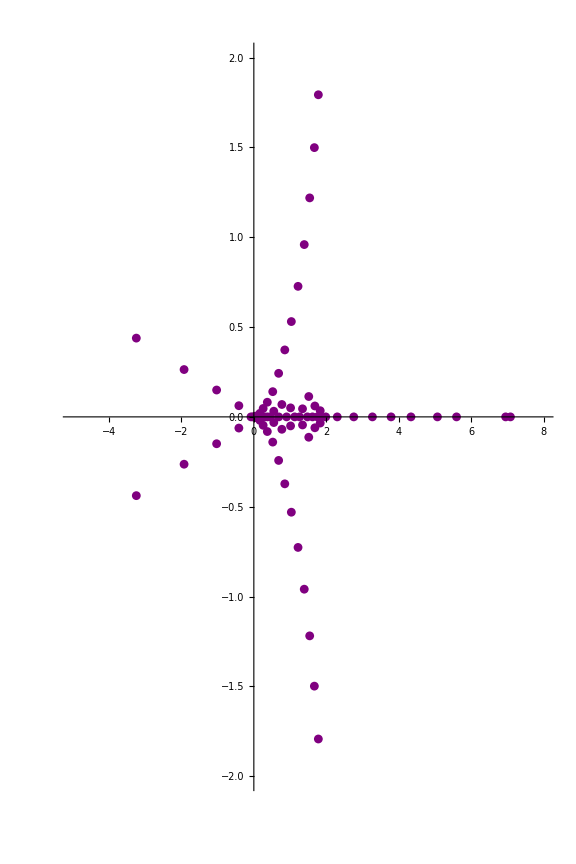

```mathematica
LiEgvRe=Re[LiEgv];
LiEgvIm=Im[LiEgv];
LiEgv2D={LiEgvRe,LiEgvIm}//Transpose;
ListPlot[LiEgv2D,PlotRange->{{-5,8},{-2,2}},PlotStyle->Purple,ImageSize->Large,AspectRatio->1.5]
```

```mathematica
MatrixForm[Mln]
```

(1.1115 | -0.326751 | -0.0207008 | -0.00499405 | -0.00177183 | -0.00077198 | -0.000383761 | -0.000209416 | -0.000122565 | -0.0000757732 | -0.000048962 | -0.0000328131 | -0.0000226756 | -0.0000160859 | -0.0000116725 | -8.6391×10^-6 | -6.50648×10^-6 | -4.97681×10^-6 | -3.8599×10^-6 | -3.03123×10^-6 | -2.40751×10^-6 | -1.93187×10^-6 | -1.56482×10^-6 | -1.27847×10^-6 | -1.05283×10^-6 | -8.7339×10^-7 | -0.439359 | 1.85129 | -1.77383 | 1.24432 | -0.966752 | 0.770192 | -0.636855 | 0.536195 | -0.460768 | 0.400924 | -0.353456 | 0.314432 | -0.282296 | 0.255172 | -0.232229 | 0.212471 | -0.195417 | 0.180495 | -0.167412 | 0.155816 | -0.145518 | 0.136295 | -0.128018 | 0.120538 | -0.113767 | 0.107602 | 3.36842 | -2.71235 | 1.71928 | -1.25748 | 0.962083 | -0.772227 | 0.635844 | -0.536747 | 0.460445 | -0.401123 | 0.353327 | -0.314519 | 0.282236 | -0.255215 | 0.232198 | -0.212493 | 0.1954 | -0.180508 | 0.167402 | -0.155824 | 0.145512 | -0.1363 | 0.128014 | -0.120541 | 0.113765 | -0.107604
-0.326751 | 1.0876 | -0.383384 | -0.0274424 | -0.00723159 | -0.00274446 | -0.00126126 | -0.0006548 | -0.000370444 | -0.00022352 | -0.000141845 | -0.0000937553 | -0.0000640912 | -0.0000450733 | -0.0000324771 | -0.0000238979 | -0.0000179115 | -0.0000136446 | -0.0000105456 | -8.25685×10^-6 | -6.54091×10^-6 | -5.23683×10^-6 | -4.23345×10^-6 | -3.45272×10^-6 | -2.83897×10^-6 | -2.35188×10^-6 | -1.59297 | -0.429911 | 3.30755 | -3.38645 | 2.53358 | -2.04679 | 1.68084 | -1.42076 | 1.21788 | -1.06146 | 0.934703 | -0.83221 | 0.74668 | -0.675266 | 0.614316 | -0.56222 | 0.516968 | -0.477589 | 0.442896 | -0.412276 | 0.384985 | -0.360618 | 0.33869 | -0.318925 | 0.300991 | -0.284695 | -2.71235 | 5.35367 | -4.66425 | 3.29913 | -2.55531 | 2.03881 | -1.68443 | 1.41893 | -1.21891 | 1.06085 | -0.935089 | 0.831955 | -0.746853 | 0.675144 | -0.614404 | 0.562156 | -0.517015 | 0.477553 | -0.442924 | 0.412254 | -0.385002 | 0.360604 | -0.338702 | 0.318916 | -0.300998 | 0.284689
-0.0207008 | -0.383384 | 1.07657 | -0.408095 | -0.031231 | -0.00869306 | -0.00345049 | -0.00164599 | -0.000881855 | -0.000512503 | -0.00031652 | -0.00020499 | -0.000137944 | -0.0000958132 | -0.0000683495 | -0.000049884 | -0.000037135 | -0.0000281279 | -0.0000216346 | -0.0000168693 | -0.0000133159 | -0.0000106281 | -8.56851×10^-6 | -6.97168×10^-6 | -5.72027×10^-6 | -4.72993×10^-6 | 1.7902 | -3.00446 | -0.42555 | 4.79049 | -5.10329 | 3.98661 | -3.31373 | 2.78448 | -2.39494 | 2.08292 | -1.83679 | 1.63374 | -1.46691 | 1.32588 | -1.20672 | 1.10402 | -1.01543 | 0.937875 | -0.869901 | 0.80964 | -0.756138 | 0.708206 | -0.665202 | 0.626333 | -0.591153 | 0.559115 | 1.71928 | -4.66425 | 7.34628 | -6.60281 | 4.98684 | -4.016 | 3.30275 | -2.78951 | 2.39232 | -2.08441 | 1.83588 | -1.63432 | 1.46652 | -1.32615 | 1.20653 | -1.10415 | 1.01532 | -0.937952 | 0.869842 | -0.809685 | 0.756102 | -0.708235 | 0.665179 | -0.626352 | 0.591137 | -0.559128
-0.00499405 | -0.0274424 | -0.408095 | 1.07049 | -0.421371 | -0.0336083 | -0.00970534 | -0.00397661 | -0.00194965 | -0.00106968 | -0.00063472 | -0.000399252 | -0.000262812 | -0.000179444 | -0.000126278 | -0.0000911527 | -0.0000672446 | -0.0000505514 | -0.0000386352 | -0.0000299625 | -0.0000235414 | -0.0000187141 | -0.0000150346 | -0.0000121951 | -9.97903×10^-6 | -8.23151×10^-6 | -1.24038 | 3.40814 | -4.46786 | -0.423149 | 6.29775 | -6.89165 | 5.55422 | -4.71833 | 4.03691 | -3.5215 | 3.09956 | -2.76039 | 2.47631 | -2.23969 | 2.0374 | -1.86471 | 1.71457 | -1.584 | 1.46891 | -1.36737 | 1.27684 | -1.19604 | 1.12331 | -1.05776 | 0.998272 | -0.944228 | -1.25748 | 3.29913 | -6.60281 | 9.342 | -8.54916 | 6.74791 | -5.59069 | 4.70457 | -4.04329 | 3.51814 | -3.1015 | 2.7592 | -2.47708 | 2.23917 | -2.03777 | 1.86445 | -1.71475 | 1.58386 | -1.46902 | 1.36729 | -1.27691 | 1.19599 | -1.12335 | 1.05772 | -0.9983 | 0.944206
-0.00177183 | -0.00723159 | -0.031231 | -0.421371 | 1.06677 | -0.429392 | -0.0352074 | -0.0104363 | -0.00437774 | -0.00219157 | -0.00122489 | -0.000738915 | -0.00047171 | -0.000314663 | -0.000217444 | -0.000154698 | -0.000112784 | -0.0000839639 | -0.0000636509 | -0.000049024 | -0.0000382919 | -0.0000302859 | -0.0000242245 | -0.000019574 | -0.0000159628 | -0.000013128 | 0.968153 | -2.52786 | 5.12798 | -5.96462 | -0.421678 | 7.8227 | -8.72949 | 7.20381 | -6.22581 | 5.40484 | -4.77019 | 4.24101 | -3.80888 | 3.44217 | -3.13311 | 2.86627 | -2.63639 | 2.43497 | -2.25854 | 2.10205 | -1.96317 | 1.8387 | -1.72707 | 1.62614 | -1.53481 | 1.45162 | 0.962083 | -2.55531 | 4.98684 | -8.54916 | 11.3393 | -10.5045 | 8.55955 | -7.24701 | 6.20941 | -5.41251 | 4.76612 | -4.24337 | 3.80741 | -3.44313 | 3.13247 | -2.86673 | 2.63606 | -2.43521 | 2.25836 | -2.10219 | 1.96306 | -1.83879 | 1.727 | -1.6262 | 1.53477 | -1.45166
-0.00077198 | -0.00274446 | -0.00869306 | -0.0336083 | -0.429392 | 1.06431 | -0.434632 | -0.0363381 | -0.0109818 | -0.00469 | -0.00238657 | -0.00135375 | -0.000827653 | -0.000534811 | -0.000360717 | -0.000251795 | -0.000180799 | -0.000132937 | -0.0000997445 | -0.0000761632 | -0.0000590562 | -0.000046417 | -0.0000369266 | -0.0000296973 | -0.0000241188 | -0.0000197636 | -0.769582 | 2.04896 | -3.97974 | 6.91822 | -7.48323 | -0.420707 | 9.36043 | -10.6028 | 8.9139 | -7.81191 | 6.86381 | -6.11773 | 5.48579 | -4.96281 | 4.51391 | -4.13169 | 3.79877 | -3.50965 | 3.25454 | -3.02964 | 2.82902 | -2.65002 | 2.48884 | -2.34362 | 2.21181 | -2.09208 | -0.772227 | 2.03881 | -4.016 | 6.74791 | -10.5045 | 13.3375 | -12.4673 | 10.4073 | -8.96357 | 7.79299 | -6.8727 | 6.11297 | -5.48857 | 4.96108 | -4.51505 | 4.13091 | -3.79932 | 3.50925 | -3.25484 | 3.02942 | -2.82919 | 2.64988 | -2.48894 | 2.34354 | -2.21188 | 2.09203
-0.000383761 | -0.00126126 | -0.00345049 | -0.00970534 | -0.0352074 | -0.434632 | 1.0626 | -0.438251 | -0.0371689 | -0.0113999 | -0.00493764 | -0.00254567 | -0.00146148 | -0.000903438 | -0.000589725 | -0.000401473 | -0.000282656 | -0.00020457 | -0.00015152 | -0.000114463 | -0.000087956 | -0.0000686032 | -0.0000542184 | -0.0000433559 | -0.000035037 | -0.0000285851 | 0.637159 | -1.67985 | 3.31646 | -5.54654 | 8.75732 | -9.01683 | -0.420031 | 10.9076 | -12.5022 | 10.6699 | -9.45935 | 8.39566 | -7.54616 | 6.81681 | -6.20624 | 5.67684 | -5.22203 | 4.82276 | -4.47351 | 4.16342 | -3.88843 | 3.64185 | -3.42078 | 3.22084 | -3.03997 | 2.87519 | 0.635844 | -1.68443 | 3.30275 | -5.59069 | 8.55955 | -12.4673 | 15.3362 | -14.4362 | 12.2817 | -10.7258 | 9.438 | -8.40573 | 7.54076 | -6.81999 | 6.20424 | -5.67816 | 5.22112 | -4.8234 | 4.47305 | -4.16377 | 3.88817 | -3.64205 | 3.42062 | -3.22097 | 3.03987 | -2.87527
-0.000209416 | -0.0006548 | -0.00164599 | -0.00397661 | -0.0104363 | -0.0363381 | -0.438251 | 1.06137 | -0.440861 | -0.0377981 | -0.0117277 | -0.00513726 | -0.002677 | -0.00155225 | -0.000968456 | -0.000637601 | -0.000437525 | -0.000310315 | -0.00022613 | -0.00016856 | -0.000128095 | -0.0000989795 | -0.0000776042 | -0.0000616325 | -0.0000495116 | -0.000040185 | -0.53603 | 1.42128 | -2.78318 | 4.72148 | -7.19556 | 10.6315 | -10.5611 | -0.419542 | 12.4619 | -14.4215 | 12.4614 | -11.1555 | 9.98668 | -9.04155 | 8.2204 | -7.52607 | 6.91867 | -6.39266 | 5.92765 | -5.51826 | 5.15268 | -4.82676 | 4.53311 | -4.26867 | 4.02856 | -3.81051 | -0.536747 | 1.41893 | -2.78951 | 4.70457 | -7.24701 | 10.4073 | -14.4362 | 17.3352 | -16.4098 | 14.1764 | -12.5236 | 11.1318 | -9.99789 | 9.03552 | -8.22396 | 7.52383 | -6.92015 | 6.39164 | -5.92837 | 5.51772 | -5.15307 | 4.82645 | -4.53335 | 4.26849 | -4.0287 | 3.81039
-0.000122565 | -0.000370444 | -0.000881855 | -0.00194965 | -0.00437774 | -0.0109818 | -0.0371689 | -0.440861 | 1.06044 | -0.442806 | -0.0382866 | -0.0119896 | -0.0053005 | -0.00278657 | -0.00162933 | -0.00102453 | -0.000679475 | -0.000469457 | -0.000335096 | -0.000245651 | -0.000184138 | -0.000140669 | -0.000109232 | -0.0000860406 | -0.0000686315 | -0.0000553616 | 0.460865 | -1.21759 | 2.39563 | -4.03537 | 6.22927 | -8.90522 | 12.5316 | -12.1133 | -0.419174 | 14.0216 | -16.3563 | 14.2812 | -12.8911 | 11.6264 | -10.5929 | 9.68554 | -8.91156 | 8.22907 | -7.63383 | 7.10424 | -6.63529 | 6.21434 | -5.83723 | 5.49598 | -5.1874 | 4.90617 | 0.460445 | -1.21891 | 2.39232 | -4.04329 | 6.20941 | -8.96357 | 12.2817 | -16.4098 | 19.3345 | -18.3872 | 16.0867 | -14.3494 | 12.8651 | -11.6387 | 10.5863 | -9.68948 | 8.90908 | -8.23072 | 7.63269 | -7.10506 | 6.6347 | -6.21478 | 5.83689 | -5.49624 | 5.18719 | -4.90634
-0.0000757732 | -0.00022352 | -0.000512503 | -0.00106968 | -0.00219157 | -0.00469 | -0.0113999 | -0.0377981 | -0.442806 | 1.05972 | -0.444296 | -0.0386738 | -0.0122022 | -0.00543571 | -0.0028789 | -0.00169527 | -0.00107317 | -0.000716239 | -0.000497806 | -0.000357322 | -0.000263324 | -0.000198364 | -0.000152243 | -0.00011874 | -0.0000939185 | -0.0000752094 | -0.400864 | 1.06164 | -2.08251 | 3.52235 | -5.40311 | 7.81562 | -10.6609 | 14.4514 | -13.6716 | -0.418892 | 15.5857 | -18.3034 | 16.1236 | -14.6589 | 13.3066 | -12.1915 | 11.2033 | -10.3538 | 9.59937 | -8.93717 | 8.3446 | -7.8171 | 7.34132 | -6.91321 | 6.52424 | -6.17118 | -0.401123 | 1.06085 | -2.08441 | 3.51814 | -5.41251 | 7.79299 | -10.7258 | 14.1764 | -18.3872 | 21.334 | -20.3677 | 18.0095 | -16.1978 | 14.6306 | -13.32 | 12.1843 | -11.2076 | 10.3511 | -9.60118 | 8.93592 | -8.3455 | 7.81644 | -7.34182 | 6.91283 | -6.52453 | 6.17095
-0.000048962 | -0.000141845 | -0.00031652 | -0.00063472 | -0.00122489 | -0.00238657 | -0.00493764 | -0.0117277 | -0.0382866 | -0.444296 | 1.05916 | -0.445463 | -0.0389861 | -0.0123772 | -0.00554897 | -0.00295741 | -0.00175209 | -0.00111558 | -0.000748648 | -0.000523046 | -0.00037729 | -0.000279335 | -0.000211352 | -0.000162888 | -0.000127543 | -0.000101258 | 0.353495 | -0.934591 | 1.83704 | -3.09906 | 4.77116 | -6.86193 | 9.46325 | -12.4522 | 16.3866 | -15.2345 | -0.41867 | 17.1532 | -20.2603 | 17.9846 | -16.4534 | 15.0208 | -13.8303 | 12.7664 | -11.8455 | 11.0223 | -10.2956 | 9.64183 | -9.05709 | 8.52736 | -8.04875 | 7.61228 | 0.353327 | -0.935089 | 1.83588 | -3.1015 | 4.76612 | -6.8727 | 9.438 | -12.5236 | 16.0867 | -20.3677 | 23.3335 | -22.3507 | 19.9423 | -18.0647 | 16.4228 | -15.0353 | 13.8225 | -12.771 | 11.8425 | -11.0242 | 10.2942 | -9.64281 | 9.05637 | -8.5279 | 8.04833 | -7.61261
-0.0000328131 | -0.0000937553 | -0.00020499 | -0.000399252 | -0.000738915 | -0.00135375 | -0.00254567 | -0.00513726 | -0.0119896 | -0.0386738 | -0.445463 | 1.05871 | -0.446395 | -0.0392418 | -0.0125231 | -0.0056448 | -0.00302472 | -0.00180138 | -0.00115276 | -0.000777336 | -0.000545587 | -0.00039527 | -0.000293861 | -0.000223219 | -0.000172677 | -0.000135689 | -0.314406 | 0.832284 | -1.63358 | 2.76071 | -4.24042 | 6.1188 | -8.39365 | 11.1596 | -14.2717 | 18.3339 | -16.8011 | -0.418492 | 18.7236 | -22.2253 | 19.8609 | -18.2703 | 16.7639 | -15.5037 | 14.3687 | -13.3803 | 12.4915 | -11.7028 | 10.9899 | -10.3495 | 9.76688 | -9.23854 | -0.314519 | 0.831955 | -1.63432 | 2.7592 | -4.24337 | 6.11297 | -8.40573 | 11.1318 | -14.3494 | 18.0095 | -22.3507 | 25.3332 | -24.3357 | 21.8832 | -19.9469 | 18.2376 | -16.7794 | 15.4953 | -14.3737 | 13.3771 | -12.4936 | 11.7014 | -10.991 | 10.3487 | -9.76747 | 9.23809
-0.0000226756 | -0.0000640912 | -0.000137944 | -0.000262812 | -0.00047171 | -0.000827653 | -0.00146148 | -0.002677 | -0.0053005 | -0.0122022 | -0.0389861 | -0.446395 | 1.05834 | -0.447151 | -0.0394538 | -0.012646 | -0.00572661 | -0.00308286 | -0.00184441 | -0.00118552 | -0.000802836 | -0.000565783 | -0.000411499 | -0.000307062 | -0.000234072 | -0.000181683 | 0.282314 | -0.746629 | 1.46702 | -2.4761 | 3.80925 | -5.48514 | 7.54732 | -9.98457 | 12.8953 | -16.114 | 20.2911 | -18.3707 | -0.418348 | 20.2962 | -24.1969 | 21.7501 | -20.1062 | 18.5318 | -17.2068 | 16.0052 | -14.9531 | 14.0019 | -13.1538 | 12.3838 | -11.6892 | 11.055 | 0.282236 | -0.746853 | 1.46652 | -2.47708 | 3.80741 | -5.48857 | 7.54076 | -9.99789 | 12.8651 | -16.1978 | 19.9423 | -24.3357 | 27.3329 | -26.3224 | 23.831 | -21.8419 | 20.0713 | -18.5483 | 17.1978 | -16.0106 | 14.9497 | -14.0041 | 13.1522 | -12.3849 | 11.6883 | -11.0556
-0.0000160859 | -0.0000450733 | -0.0000958132 | -0.000179444 | -0.000314663 | -0.000534811 | -0.000903438 | -0.00155225 | -0.00278657 | -0.00543571 | -0.0123772 | -0.0392418 | -0.447151 | 1.05804 | -0.447773 | -0.0396317 | -0.0127506 | -0.00579702 | -0.00313342 | -0.00188218 | -0.00121453 | -0.000825591 | -0.000583937 | -0.000426184 | -0.000319084 | -0.000244013 | -0.255159 | 0.675302 | -1.3258 | 2.23983 | -3.44192 | 4.96324 | -6.8161 | 9.04278 | -11.6242 | 14.6632 | -17.9748 | 22.2563 | -19.9427 | -0.418228 | 21.8708 | -26.1742 | 23.6501 | -21.9583 | 20.3209 | -18.9359 | 17.6718 | -16.5594 | 15.5488 | -14.6438 | 13.8187 | -13.0717 | -0.255215 | 0.675144 | -1.32615 | 2.23917 | -3.44313 | 4.96108 | -6.81999 | 9.03552 | -11.6387 | 14.6306 | -18.0647 | 21.8832 | -26.3224 | 29.3326 | -28.3106 | 25.7844 | -23.7477 | 21.9212 | -20.3385 | 18.9263 | -17.6775 | 16.5558 | -15.5512 | 14.6421 | -13.8199 | 13.0708
-0.0000116725 | -0.0000324771 | -0.0000683495 | -0.000126278 | -0.000217444 | -0.000360717 | -0.000589725 | -0.000968456 | -0.00162933 | -0.0028789 | -0.00554897 | -0.0125231 | -0.0394538 | -0.447773 | 1.05779 | -0.448291 | -0.0397824 | -0.0128403 | -0.00585807 | -0.00317766 | -0.00191551 | -0.00124033 | -0.000845975 | -0.000600305 | -0.000439507 | -0.000330052 | 0.232238 | -0.614291 | 1.20677 | -2.0373 | 3.13329 | -4.51362 | 6.2067 | -8.21963 | 10.5942 | -13.3043 | 16.4578 | -19.851 | 24.2281 | -21.5168 | -0.418129 | 23.4469 | -28.1562 | 25.5593 | -23.8243 | 22.1285 | -20.6877 | 19.3649 | -18.1956 | 17.1283 | -16.1689 | 15.2908 | 0.232198 | -0.614404 | 1.20653 | -2.03777 | 3.13247 | -4.51505 | 6.20424 | -8.22396 | 10.5863 | -13.32 | 16.4228 | -19.9469 | 23.831 | -28.3106 | 31.3324 | -30.3 | 27.7426 | -25.6627 | 23.785 | -22.1471 | 20.6776 | -19.3709 | 18.1918 | -17.1309 | 16.1671 | -15.2921
-8.6391×10^-6 | -0.0000238979 | -0.000049884 | -0.0000911527 | -0.000154698 | -0.000251795 | -0.000401473 | -0.000637601 | -0.00102453 | -0.00169527 | -0.00295741 | -0.0056448 | -0.012646 | -0.0396317 | -0.448291 | 1.05758 | -0.448727 | -0.0399112 | -0.0129178 | -0.00591135 | -0.00321661 | -0.00194508 | -0.00126338 | -0.000864301 | -0.000615111 | -0.000451625 | -0.212464 | 0.562239 | -1.10398 | 1.86478 | -2.86615 | 4.13189 | -5.67653 | 7.52657 | -9.68473 | 12.1929 | -15.0185 | 18.2748 | -21.7401 | 26.2055 | -23.0925 | -0.418045 | 25.0245 | -30.1422 | 27.4766 | -25.7024 | 23.9523 | -22.4594 | 21.0814 | -19.8583 | 18.7372 | -17.7256 | -0.212493 | 0.562156 | -1.10415 | 1.86445 | -2.86673 | 4.13091 | -5.67816 | 7.52383 | -9.68948 | 12.1843 | -15.0353 | 18.2376 | -21.8419 | 25.7844 | -30.3 | 33.3323 | -32.2904 | 29.7049 | -27.5856 | 25.661 | -23.972 | 22.4488 | -21.0877 | 19.8542 | -18.7399 | 17.7237
-6.50648×10^-6 | -0.0000179115 | -0.000037135 | -0.0000672446 | -0.000112784 | -0.000180799 | -0.000282656 | -0.000437525 | -0.000679475 | -0.00107317 | -0.00175209 | -0.00302472 | -0.00572661 | -0.0127506 | -0.0397824 | -0.448727 | 1.0574 | -0.449098 | -0.0400223 | -0.0129853 | -0.00595814 | -0.00325107 | -0.00197142 | -0.00128404 | -0.000880834 | -0.000628542 | 0.195422 | -0.516953 | 1.01545 | -1.71451 | 2.63648 | -3.79863 | 5.22225 | -6.91832 | 8.9121 | -11.2025 | 13.8317 | -16.7615 | 20.1107 | -23.64 | 28.1876 | -24.6697 | -0.417973 | 26.6032 | -32.1317 | 29.4007 | -27.5911 | 25.7903 | -24.2488 | 22.8188 | -21.5447 | 20.3723 | 0.1954 | -0.517015 | 1.01532 | -1.71475 | 2.63606 | -3.79932 | 5.22112 | -6.92015 | 8.90908 | -11.2076 | 13.8225 | -16.7794 | 20.0713 | -23.7477 | 27.7426 | -32.2904 | 35.3321 | -34.2817 | 31.6707 | -29.5155 | 27.5475 | -25.811 | 24.2376 | -22.8254 | 21.5405 | -20.3752
-4.97681×10^-6 | -0.0000136446 | -0.0000281279 | -0.0000505514 | -0.0000839639 | -0.000132937 | -0.00020457 | -0.000310315 | -0.000469457 | -0.000716239 | -0.00111558 | -0.00180138 | -0.00308286 | -0.00579702 | -0.0128403 | -0.0399112 | -0.449098 | 1.05724 | -0.449415 | -0.0401187 | -0.0130445 | -0.00599945 | -0.00328172 | -0.001995 | -0.00130265 | -0.000895798 | -0.180491 | 0.4776 | -0.937853 | 1.58404 | -2.4349 | 3.50975 | -4.8226 | 6.39291 | -8.2287 | 10.3544 | -12.7655 | 15.5051 | -18.5293 | 21.9629 | -25.5492 | 30.1738 | -26.2481 | -0.417911 | 28.1829 | -34.1242 | 31.3308 | -29.489 | 27.6409 | -26.0539 | 24.5748 | -23.2526 | -0.180508 | 0.477553 | -0.937952 | 1.58386 | -2.43521 | 3.50925 | -4.8234 | 6.39164 | -8.23072 | 10.3511 | -12.771 | 15.4953 | -18.5483 | 21.9212 | -25.6627 | 29.7049 | -34.2817 | 37.332 | -36.2738 | 33.6396 | -31.4513 | 29.4433 | -27.6625 | 26.0422 | -24.5818 | 23.2481
-3.8599×10^-6 | -0.0000105456 | -0.0000216346 | -0.0000386352 | -0.0000636509 | -0.0000997445 | -0.00015152 | -0.00022613 | -0.000335096 | -0.000497806 | -0.000748648 | -0.00115276 | -0.00184441 | -0.00313342 | -0.00585807 | -0.0129178 | -0.0400223 | -0.449415 | 1.05711 | -0.44969 | -0.040203 | -0.0130966 | -0.00603611 | -0.00330909 | -0.00201618 | -0.00131946 | 0.167415 | -0.442888 | 0.869918 | -1.46888 | 2.25859 | -3.25447 | 4.47363 | -5.92747 | 7.63409 | -9.59898 | 11.8461 | -14.3678 | 17.2083 | -20.3184 | 23.829 | -27.4663 | 32.1633 | -27.8276 | -0.417858 | 29.7635 | -36.1194 | 33.2661 | -31.3951 | 29.5026 | -27.8731 | 26.3476 | 0.167402 | -0.442924 | 0.869842 | -1.46902 | 2.25836 | -3.25484 | 4.47305 | -5.92837 | 7.63269 | -9.60118 | 11.8425 | -14.3737 | 17.1978 | -20.3385 | 23.785 | -27.5856 | 31.6707 | -36.2738 | 39.3319 | -38.2665 | 35.6111 | -33.3924 | 31.3472 | -29.5252 | 27.8608 | -26.3549
-3.03123×10^-6 | -8.25685×10^-6 | -0.0000168693 | -0.0000299625 | -0.000049024 | -0.0000761632 | -0.000114463 | -0.00016856 | -0.000245651 | -0.000357322 | -0.000523046 | -0.000777336 | -0.00118552 | -0.00188218 | -0.00317766 | -0.00591135 | -0.0129853 | -0.0401187 | -0.44969 | 1.05699 | -0.449929 | -0.0402771 | -0.0131428 | -0.0060688 | -0.00333364 | -0.00203528 | -0.155813 | 0.412283 | -0.809626 | 1.3674 | -2.10201 | 3.0297 | -4.16333 | 5.51839 | -7.10405 | 8.93745 | -11.0218 | 13.3809 | -16.0043 | 18.9374 | -22.126 | 25.7071 | -29.3904 | 34.1559 | -29.408 | -0.417812 | 31.3449 | -38.1168 | 35.2062 | -33.3084 | 31.3742 | -29.7048 | -0.155824 | 0.412254 | -0.809685 | 1.36729 | -2.10219 | 3.02942 | -4.16377 | 5.51772 | -7.10506 | 8.93592 | -11.0242 | 13.3771 | -16.0106 | 18.9263 | -22.1471 | 25.661 | -29.5155 | 33.6396 | -38.2665 | 41.3318 | -40.2599 | 37.5849 | -35.3381 | 33.2584 | -31.3978 | 29.692
-2.40751×10^-6 | -6.54091×10^-6 | -0.0000133159 | -0.0000235414 | -0.0000382919 | -0.0000590562 | -0.000087956 | -0.000128095 | -0.000184138 | -0.000263324 | -0.00037729 | -0.000545587 | -0.000802836 | -0.00121453 | -0.00191551 | -0.00321661 | -0.00595814 | -0.0130445 | -0.040203 | -0.449929 | 1.05689 | -0.450137 | -0.0403425 | -0.0131838 | -0.00609808 | -0.00335574 | 0.14552 | -0.384979 | 0.756148 | -1.27683 | 1.9632 | -2.82897 | 3.8885 | -5.15257 | 6.63544 | -8.34439 | 10.2959 | -12.4911 | 14.9537 | -17.6709 | 20.6892 | -23.9498 | 27.5958 | -31.3205 | 36.1511 | -30.9892 | -0.417771 | 32.9269 | -40.1163 | 37.1503 | -35.2281 | 33.2547 | 0.145512 | -0.385002 | 0.756102 | -1.27691 | 1.96306 | -2.82919 | 3.88817 | -5.15307 | 6.6347 | -8.3455 | 10.2942 | -12.4936 | 14.9497 | -17.6775 | 20.6776 | -23.972 | 27.5475 | -31.4513 | 35.6111 | -40.2599 | 43.3317 | -42.2538 | 39.5608 | -37.2879 | 35.1761 | -33.2793
-1.93187×10^-6 | -5.23683×10^-6 | -0.0000106281 | -0.0000187141 | -0.0000302859 | -0.000046417 | -0.0000686032 | -0.0000989795 | -0.000140669 | -0.000198364 | -0.000279335 | -0.00039527 | -0.000565783 | -0.000825591 | -0.00124033 | -0.00194508 | -0.00325107 | -0.00599945 | -0.0130966 | -0.0402771 | -0.450137 | 1.0568 | -0.450321 | -0.0404007 | -0.0132206 | -0.0061244 | -0.136293 | 0.360623 | -0.708198 | 1.19605 | -1.83868 | 2.65005 | -3.6418 | 4.82683 | -6.21423 | 7.81726 | -9.64161 | 11.7032 | -14.0014 | 16.5601 | -19.3639 | 22.4609 | -25.7878 | 29.4937 | -33.2558 | 38.1487 | -32.5711 | -0.417735 | 34.5096 | -42.1176 | 39.0981 | -37.1537 | -0.1363 | 0.360604 | -0.708235 | 1.19599 | -1.83879 | 2.64988 | -3.64205 | 4.82645 | -6.21478 | 7.81644 | -9.64281 | 11.7014 | -14.0041 | 16.5558 | -19.3709 | 22.4488 | -25.811 | 29.4433 | -33.3924 | 37.5849 | -42.2538 | 45.3316 | -44.2481 | 41.5386 | -39.2414 | 37.0995
-1.56482×10^-6 | -4.23345×10^-6 | -8.56851×10^-6 | -0.0000150346 | -0.0000242245 | -0.0000369266 | -0.0000542184 | -0.0000776042 | -0.000109232 | -0.000152243 | -0.000211352 | -0.000293861 | -0.000411499 | -0.000583937 | -0.000845975 | -0.00126338 | -0.00197142 | -0.00328172 | -0.00603611 | -0.0131428 | -0.0403425 | -0.450321 | 1.05672 | -0.450484 | -0.0404526 | -0.0132536 | 0.128019 | -0.338687 | 0.665209 | -1.12329 | 1.72708 | -2.48881 | 3.42082 | -4.53305 | 5.83731 | -7.3412 | 9.05726 | -10.9897 | 13.1541 | -15.5483 | 18.1963 | -21.0804 | 24.2504 | -27.6383 | 31.3998 | -35.1958 | 40.1482 | -34.1536 | -0.417704 | 36.0928 | -44.1205 | 41.0492 | 0.128014 | -0.338702 | 0.665179 | -1.12335 | 1.727 | -2.48894 | 3.42062 | -4.53335 | 5.83689 | -7.34182 | 9.05637 | -10.991 | 13.1522 | -15.5512 | 18.1918 | -21.0877 | 24.2376 | -27.6625 | 31.3472 | -35.3381 | 39.5608 | -44.2481 | 47.3316 | -46.2429 | 43.5179 | -41.1982
-1.27847×10^-6 | -3.45272×10^-6 | -6.97168×10^-6 | -0.0000121951 | -0.000019574 | -0.0000296973 | -0.0000433559 | -0.0000616325 | -0.0000860406 | -0.00011874 | -0.000162888 | -0.000223219 | -0.000307062 | -0.000426184 | -0.000600305 | -0.000864301 | -0.00128404 | -0.001995 | -0.00330909 | -0.0060688 | -0.0131838 | -0.0404007 | -0.450484 | 1.05664 | -0.450629 | -0.0404991 | -0.120537 | 0.318927 | -0.626328 | 1.05777 | -1.62613 | 2.34364 | -3.22081 | 4.26872 | -5.49591 | 6.9133 | -8.52723 | 10.3496 | -12.3835 | 14.6441 | -17.1278 | 19.859 | -22.8177 | 26.0555 | -29.5 | 33.3132 | -37.1399 | 42.1495 | -35.7366 | -0.417675 | 37.6764 | -46.1248 | -0.120541 | 0.318916 | -0.626352 | 1.05772 | -1.6262 | 2.34354 | -3.22097 | 4.26849 | -5.49624 | 6.91283 | -8.5279 | 10.3487 | -12.3849 | 14.6421 | -17.1309 | 19.8542 | -22.8254 | 26.0422 | -29.5252 | 33.2584 | -37.2879 | 41.5386 | -46.2429 | 49.3315 | -48.238 | 45.4987
-1.05283×10^-6 | -2.83897×10^-6 | -5.72027×10^-6 | -9.97903×10^-6 | -0.0000159628 | -0.0000241188 | -0.000035037 | -0.0000495116 | -0.0000686315 | -0.0000939185 | -0.000127543 | -0.000172677 | -0.000234072 | -0.000319084 | -0.000439507 | -0.000615111 | -0.000880834 | -0.00130265 | -0.00201618 | -0.00333364 | -0.00609808 | -0.0132206 | -0.0404526 | -0.450629 | 1.05658 | -0.450758 | 0.113768 | -0.300989 | 0.591157 | -0.998264 | 1.53482 | -2.21179 | 3.04 | -4.02852 | 5.18745 | -6.52416 | 8.04885 | -9.76674 | 11.6893 | -13.8185 | 16.1692 | -18.7367 | 21.5454 | -24.5738 | 27.8747 | -31.3716 | 35.2329 | -39.0877 | 44.1524 | -37.3202 | -0.41765 | 39.2605 | 0.113765 | -0.300998 | 0.591137 | -0.9983 | 1.53477 | -2.21188 | 3.03987 | -4.0287 | 5.18719 | -6.52453 | 8.04833 | -9.76747 | 11.6883 | -13.8199 | 16.1671 | -18.7399 | 21.5405 | -24.5818 | 27.8608 | -31.3978 | 35.1761 | -39.2414 | 43.5179 | -48.238 | 51.3315 | -50.2334
-8.7339×10^-7 | -2.35188×10^-6 | -4.72993×10^-6 | -8.23151×10^-6 | -0.000013128 | -0.0000197636 | -0.0000285851 | -0.000040185 | -0.0000553616 | -0.0000752094 | -0.000101258 | -0.000135689 | -0.000181683 | -0.000244013 | -0.000330052 | -0.000451625 | -0.000628542 | -0.000895798 | -0.00131946 | -0.00203528 | -0.00335574 | -0.0061244 | -0.0132536 | -0.0404991 | -0.450758 | 1.05652 | -0.107601 | 0.284697 | -0.559111 | 0.944235 | -1.45161 | 2.0921 | -2.87517 | 3.81054 | -4.90613 | 6.17124 | -7.6122 | 9.23865 | -11.0548 | 13.0719 | -15.2906 | 17.726 | -20.3718 | 23.2533 | -26.3466 | 29.7064 | -33.2521 | 37.1585 | -41.0388 | 46.1568 | -38.9041 | -0.417627 | -0.107604 | 0.284689 | -0.559128 | 0.944206 | -1.45166 | 2.09203 | -2.87527 | 3.81039 | -4.90634 | 6.17095 | -7.61261 | 9.23809 | -11.0556 | 13.0708 | -15.2921 | 17.7237 | -20.3752 | 23.2481 | -26.3549 | 29.692 | -33.2793 | 37.0995 | -41.1982 | 45.4987 | -50.2334 | 53.3314
-0.0216968 | 0.0961322 | -0.0254573 | -0.00137556 | -0.000277051 | -0.0000808411 | -0.0000285076 | -0.0000112308 | -4.71106×10^-6 | -2.02108×10^-6 | -8.43602×10^-7 | -3.09995×10^-7 | -6.58031×10^-8 | 4.33113×10^-8 | 8.7981×10^-8 | 1.01765×10^-7 | 1.01037×10^-7 | 9.3904×10^-8 | 8.43932×10^-8 | 7.4471×10^-8 | 6.50543×10^-8 | 5.65236×10^-8 | 4.89898×10^-8 | 4.24344×10^-8 | 3.67756×10^-8 | 3.19118×10^-8 | 1.1115 | -0.326751 | -0.0207008 | -0.00499405 | -0.00177183 | -0.00077198 | -0.000383761 | -0.000209416 | -0.000122565 | -0.0000757732 | -0.000048962 | -0.0000328131 | -0.0000226756 | -0.0000160859 | -0.0000116725 | -8.6391×10^-6 | -6.50648×10^-6 | -4.97681×10^-6 | -3.8599×10^-6 | -3.03123×10^-6 | -2.40751×10^-6 | -1.93187×10^-6 | -1.56482×10^-6 | -1.27847×10^-6 | -1.05283×10^-6 | -8.7339×10^-7 | 1.1115 | -0.326751 | -0.0207008 | -0.00499405 | -0.00177183 | -0.00077198 | -0.000383761 | -0.000209416 | -0.000122565 | -0.0000757732 | -0.000048962 | -0.0000328131 | -0.0000226756 | -0.0000160859 | -0.0000116725 | -8.6391×10^-6 | -6.50648×10^-6 | -4.97681×10^-6 | -3.8599×10^-6 | -3.03123×10^-6 | -2.40751×10^-6 | -1.93187×10^-6 | -1.56482×10^-6 | -1.27847×10^-6 | -1.05283×10^-6 | -8.7339×10^-7
-0.0759217 | -0.0225366 | 0.0977493 | -0.0284825 | -0.0016586 | -0.000353012 | -0.00010704 | -0.0000386158 | -0.0000153004 | -6.30956×10^-6 | -2.55904×10^-6 | -9.20236×10^-7 | -1.92096×10^-7 | 1.24771×10^-7 | 2.50757×10^-7 | 2.87514×10^-7 | 2.83384×10^-7 | 2.61773×10^-7 | 2.34043×10^-7 | 2.0561×10^-7 | 1.78923×10^-7 | 1.54944×10^-7 | 1.33902×10^-7 | 1.15682×10^-7 | 1.00025×10^-7 | 8.66183×10^-8 | -0.326751 | 1.0876 | -0.383384 | -0.0274424 | -0.00723159 | -0.00274446 | -0.00126126 | -0.0006548 | -0.000370444 | -0.00022352 | -0.000141845 | -0.0000937553 | -0.0000640912 | -0.0000450733 | -0.0000324771 | -0.0000238979 | -0.0000179115 | -0.0000136446 | -0.0000105456 | -8.25685×10^-6 | -6.54091×10^-6 | -5.23683×10^-6 | -4.23345×10^-6 | -3.45272×10^-6 | -2.83897×10^-6 | -2.35188×10^-6 | -0.326751 | 1.0876 | -0.383384 | -0.0274424 | -0.00723159 | -0.00274446 | -0.00126126 | -0.0006548 | -0.000370444 | -0.00022352 | -0.000141845 | -0.0000937553 | -0.0000640912 | -0.0000450733 | -0.0000324771 | -0.0000238979 | -0.0000179115 | -0.0000136446 | -0.0000105456 | -8.25685×10^-6 | -6.54091×10^-6 | -5.23683×10^-6 | -4.23345×10^-6 | -3.45272×10^-6 | -2.83897×10^-6 | -2.35188×10^-6
0.0327309 | -0.0854417 | -0.0182596 | 0.0914105 | -0.0278457 | -0.00167991 | -0.000366575 | -0.000112619 | -0.0000405676 | -0.0000157142 | -6.09952×10^-6 | -2.12377×10^-6 | -4.32588×10^-7 | 2.75647×10^-7 | 5.45581×10^-7 | 6.17837×10^-7 | 6.02765×10^-7 | 5.5206×10^-7 | 4.90029×10^-7 | 4.27857×10^-7 | 3.70359×10^-7 | 3.19254×10^-7 | 2.74794×10^-7 | 2.36576×10^-7 | 2.03924×10^-7 | 1.76123×10^-7 | -0.0207008 | -0.383384 | 1.07657 | -0.408095 | -0.031231 | -0.00869306 | -0.00345049 | -0.00164599 | -0.000881855 | -0.000512503 | -0.00031652 | -0.00020499 | -0.000137944 | -0.0000958132 | -0.0000683495 | -0.000049884 | -0.000037135 | -0.0000281279 | -0.0000216346 | -0.0000168693 | -0.0000133159 | -0.0000106281 | -8.56851×10^-6 | -6.97168×10^-6 | -5.72027×10^-6 | -4.72993×10^-6 | -0.0207008 | -0.383384 | 1.07657 | -0.408095 | -0.031231 | -0.00869306 | -0.00345049 | -0.00164599 | -0.000881855 | -0.000512503 | -0.00031652 | -0.00020499 | -0.000137944 | -0.0000958132 | -0.0000683495 | -0.000049884 | -0.000037135 | -0.0000281279 | -0.0000216346 | -0.0000168693 | -0.0000133159 | -0.0000106281 | -8.56851×10^-6 | -6.97168×10^-6 | -5.72027×10^-6 | -4.72993×10^-6
0.00249712 | 0.0363945 | -0.0847928 | -0.0143437 | 0.0828712 | -0.0257557 | -0.00157472 | -0.000345245 | -0.000105246 | -0.0000368852 | -0.0000133972 | -4.45054×10^-6 | -8.75527×10^-7 | 5.43226×10^-7 | 1.05293×10^-6 | 1.17252×10^-6 | 1.12833×10^-6 | 1.02174×10^-6 | 8.98336×10^-7 | 7.78047×10^-7 | 6.68843×10^-7 | 5.73118×10^-7 | 4.90752×10^-7 | 4.20574×10^-7 | 3.61075×10^-7 | 3.10716×10^-7 | -0.00499405 | -0.0274424 | -0.408095 | 1.07049 | -0.421371 | -0.0336083 | -0.00970534 | -0.00397661 | -0.00194965 | -0.00106968 | -0.00063472 | -0.000399252 | -0.000262812 | -0.000179444 | -0.000126278 | -0.0000911527 | -0.0000672446 | -0.0000505514 | -0.0000386352 | -0.0000299625 | -0.0000235414 | -0.0000187141 | -0.0000150346 | -0.0000121951 | -9.97903×10^-6 | -8.23151×10^-6 | -0.00499405 | -0.0274424 | -0.408095 | 1.07049 | -0.421371 | -0.0336083 | -0.00970534 | -0.00397661 | -0.00194965 | -0.00106968 | -0.00063472 | -0.000399252 | -0.000262812 | -0.000179444 | -0.000126278 | -0.0000911527 | -0.0000672446 | -0.0000505514 | -0.0000386352 | -0.0000299625 | -0.0000235414 | -0.0000187141 | -0.0000150346 | -0.0000121951 | -9.97903×10^-6 | -8.23151×10^-6
0.000678055 | 0.00282722 | 0.0358571 | -0.08023 | -0.0112169 | 0.0735445 | -0.0229665 | -0.00140043 | -0.000302948 | -0.0000894615 | -0.0000292982 | -9.08228×10^-6 | -1.7008×10^-6 | 1.01726×10^-6 | 1.91685×10^-6 | 2.08751×10^-6 | 1.97307×10^-6 | 1.76055×10^-6 | 1.52906×10^-6 | 1.31072×10^-6 | 1.1169×10^-6 | 9.49863×10^-7 | 8.08058×10^-7 | 6.8858×10^-7 | 5.88229×10^-7 | 5.03989×10^-7 | -0.00177183 | -0.00723159 | -0.031231 | -0.421371 | 1.06677 | -0.429392 | -0.0352074 | -0.0104363 | -0.00437774 | -0.00219157 | -0.00122489 | -0.000738915 | -0.00047171 | -0.000314663 | -0.000217444 | -0.000154698 | -0.000112784 | -0.0000839639 | -0.0000636509 | -0.000049024 | -0.0000382919 | -0.0000302859 | -0.0000242245 | -0.000019574 | -0.0000159628 | -0.000013128 | -0.00177183 | -0.00723159 | -0.031231 | -0.421371 | 1.06677 | -0.429392 | -0.0352074 | -0.0104363 | -0.00437774 | -0.00219157 | -0.00122489 | -0.000738915 | -0.00047171 | -0.000314663 | -0.000217444 | -0.000154698 | -0.000112784 | -0.0000839639 | -0.0000636509 | -0.000049024 | -0.0000382919 | -0.0000302859 | -0.0000242245 | -0.000019574 | -0.0000159628 | -0.000013128
0.000261702 | 0.000786772 | 0.00281255 | 0.0337427 | -0.073791 | -0.00874901 | 0.0639 | -0.0197995 | -0.0011853 | -0.000247395 | -0.0000680522 | -0.0000189729 | -3.30857×10^-6 | 1.88047×10^-6 | 3.41078×10^-6 | 3.60654×10^-6 | 3.33009×10^-6 | 2.91576×10^-6 | 2.49329×10^-6 | 2.10972×10^-6 | 1.77816×10^-6 | 1.49816×10^-6 | 1.26428×10^-6 | 1.06984×10^-6 | 9.08347×10^-7 | 7.74119×10^-7 | -0.00077198 | -0.00274446 | -0.00869306 | -0.0336083 | -0.429392 | 1.06431 | -0.434632 | -0.0363381 | -0.0109818 | -0.00469 | -0.00238657 | -0.00135375 | -0.000827653 | -0.000534811 | -0.000360717 | -0.000251795 | -0.000180799 | -0.000132937 | -0.0000997445 | -0.0000761632 | -0.0000590562 | -0.000046417 | -0.0000369266 | -0.0000296973 | -0.0000241188 | -0.0000197636 | -0.00077198 | -0.00274446 | -0.00869306 | -0.0336083 | -0.429392 | 1.06431 | -0.434632 | -0.0363381 | -0.0109818 | -0.00469 | -0.00238657 | -0.00135375 | -0.000827653 | -0.000534811 | -0.000360717 | -0.000251795 | -0.000180799 | -0.000132937 | -0.0000997445 | -0.0000761632 | -0.0000590562 | -0.000046417 | -0.0000369266 | -0.0000296973 | -0.0000241188 | -0.0000197636
0.000121542 | 0.000311346 | 0.000793736 | 0.00266168 | 0.0308975 | -0.0663257 | -0.00677811 | 0.0541214 | -0.0164112 | -0.000944562 | -0.000183105 | -0.0000427762 | -6.69574×10^-6 | 3.53809×10^-6 | 6.08991×10^-6 | 6.1912×10^-6 | 5.54502×10^-6 | 4.73885×10^-6 | 3.97332×10^-6 | 3.30796×10^-6 | 2.75051×10^-6 | 2.29092×10^-6 | 1.91439×10^-6 | 1.60629×10^-6 | 1.35382×10^-6 | 1.1463×10^-6 | -0.000383761 | -0.00126126 | -0.00345049 | -0.00970534 | -0.0352074 | -0.434632 | 1.0626 | -0.438251 | -0.0371689 | -0.0113999 | -0.00493764 | -0.00254567 | -0.00146148 | -0.000903438 | -0.000589725 | -0.000401473 | -0.000282656 | -0.00020457 | -0.00015152 | -0.000114463 | -0.000087956 | -0.0000686032 | -0.0000542184 | -0.0000433559 | -0.000035037 | -0.0000285851 | -0.000383761 | -0.00126126 | -0.00345049 | -0.00970534 | -0.0352074 | -0.434632 | 1.0626 | -0.438251 | -0.0371689 | -0.0113999 | -0.00493764 | -0.00254567 | -0.00146148 | -0.000903438 | -0.000589725 | -0.000401473 | -0.000282656 | -0.00020457 | -0.00015152 | -0.000114463 | -0.000087956 | -0.0000686032 | -0.0000542184 | -0.0000433559 | -0.000035037 | -0.0000285851
0.0000635474 | 0.000148043 | 0.000318869 | 0.000757769 | 0.00244571 | 0.0276689 | -0.0582456 | -0.00517826 | 0.0442884 | -0.012885 | -0.000687 | -0.000112853 | -0.0000147746 | 6.99697×10^-6 | 0.0000111824 | 0.0000107765 | 9.27098×10^-6 | 7.67898×10^-6 | 6.27985×10^-6 | 5.12321×10^-6 | 4.18899×10^-6 | 3.44031×10^-6 | 2.84076×10^-6 | 2.35932×10^-6 | 1.97098×10^-6 | 1.65605×10^-6 | -0.000209416 | -0.0006548 | -0.00164599 | -0.00397661 | -0.0104363 | -0.0363381 | -0.438251 | 1.06137 | -0.440861 | -0.0377981 | -0.0117277 | -0.00513726 | -0.002677 | -0.00155225 | -0.000968456 | -0.000637601 | -0.000437525 | -0.000310315 | -0.00022613 | -0.00016856 | -0.000128095 | -0.0000989795 | -0.0000776042 | -0.0000616325 | -0.0000495116 | -0.000040185 | -0.000209416 | -0.0006548 | -0.00164599 | -0.00397661 | -0.0104363 | -0.0363381 | -0.438251 | 1.06137 | -0.440861 | -0.0377981 | -0.0117277 | -0.00513726 | -0.002677 | -0.00155225 | -0.000968456 | -0.000637601 | -0.000437525 | -0.000310315 | -0.00022613 | -0.00016856 | -0.000128095 | -0.0000989795 | -0.0000776042 | -0.0000616325 | -0.0000495116 | -0.000040185
0.0000361306 | 0.0000790901 | 0.000153892 | 0.000307422 | 0.000700348 | 0.00219497 | 0.0242216 | -0.0497717 | -0.00385848 | 0.0344377 | -0.00926884 | -0.000417964 | -0.0000384103 | 0.000015192 | 0.0000217336 | 0.0000194269 | 0.0000158285 | 0.0000125835 | 9.96688×10^-6 | 7.92609×10^-6 | 6.34723×10^-6 | 5.12367×10^-6 | 4.16992×10^-6 | 3.42084×10^-6 | 2.82774×10^-6 | 2.35427×10^-6 | -0.000122565 | -0.000370444 | -0.000881855 | -0.00194965 | -0.00437774 | -0.0109818 | -0.0371689 | -0.440861 | 1.06044 | -0.442806 | -0.0382866 | -0.0119896 | -0.0053005 | -0.00278657 | -0.00162933 | -0.00102453 | -0.000679475 | -0.000469457 | -0.000335096 | -0.000245651 | -0.000184138 | -0.000140669 | -0.000109232 | -0.0000860406 | -0.0000686315 | -0.0000553616 | -0.000122565 | -0.000370444 | -0.000881855 | -0.00194965 | -0.00437774 | -0.0109818 | -0.0371689 | -0.440861 | 1.06044 | -0.442806 | -0.0382866 | -0.0119896 | -0.0053005 | -0.00278657 | -0.00162933 | -0.00102453 | -0.000679475 | -0.000469457 | -0.000335096 | -0.000245651 | -0.000184138 | -0.000140669 | -0.000109232 | -0.0000860406 | -0.0000686315 | -0.0000553616
0.0000218806 | 0.0000458551 | 0.0000833878 | 0.000149862 | 0.000286053 | 0.000631092 | 0.00192423 | 0.0206415 | -0.0410324 | -0.00275356 | 0.0245866 | -0.00559172 | -0.000140853 | 0.0000390521 | 0.0000466042 | 0.0000372521 | 0.0000281283 | 0.0000211627 | 0.0000160779 | 0.0000123765 | 9.65628×10^-6 | 7.63082×10^-6 | 6.10172×10^-6 | 4.93184×10^-6 | 4.02559×10^-6 | 3.31537×10^-6 | -0.0000757732 | -0.00022352 | -0.000512503 | -0.00106968 | -0.00219157 | -0.00469 | -0.0113999 | -0.0377981 | -0.442806 | 1.05972 | -0.444296 | -0.0386738 | -0.0122022 | -0.00543571 | -0.0028789 | -0.00169527 | -0.00107317 | -0.000716239 | -0.000497806 | -0.000357322 | -0.000263324 | -0.000198364 | -0.000152243 | -0.00011874 | -0.0000939185 | -0.0000752094 | -0.0000757732 | -0.00022352 | -0.000512503 | -0.00106968 | -0.00219157 | -0.00469 | -0.0113999 | -0.0377981 | -0.442806 | 1.05972 | -0.444296 | -0.0386738 | -0.0122022 | -0.00543571 | -0.0028789 | -0.00169527 | -0.00107317 | -0.000716239 | -0.000497806 | -0.000357322 | -0.000263324 | -0.000198364 | -0.000152243 | -0.00011874 | -0.0000939185 | -0.0000752094
0.0000139239 | 0.0000282643 | 0.000048993 | 0.0000820063 | 0.000140436 | 0.000259016 | 0.000554852 | 0.00164132 | 0.0169768 | -0.0321066 | -0.00181632 | 0.0147433 | -0.00187195 | 0.000142095 | 0.00011874 | 0.0000790989 | 0.000053365 | 0.0000371815 | 0.0000267167 | 0.0000197157 | 0.0000148827 | 0.0000114536 | 8.96237×10^-6 | 7.11487×10^-6 | 5.72006×10^-6 | 4.6504×10^-6 | -0.000048962 | -0.000141845 | -0.00031652 | -0.00063472 | -0.00122489 | -0.00238657 | -0.00493764 | -0.0117277 | -0.0382866 | -0.444296 | 1.05916 | -0.445463 | -0.0389861 | -0.0123772 | -0.00554897 | -0.00295741 | -0.00175209 | -0.00111558 | -0.000748648 | -0.000523046 | -0.00037729 | -0.000279335 | -0.000211352 | -0.000162888 | -0.000127543 | -0.000101258 | -0.000048962 | -0.000141845 | -0.00031652 | -0.00063472 | -0.00122489 | -0.00238657 | -0.00493764 | -0.0117277 | -0.0382866 | -0.444296 | 1.05916 | -0.445463 | -0.0389861 | -0.0123772 | -0.00554897 | -0.00295741 | -0.00175209 | -0.00111558 | -0.000748648 | -0.000523046 | -0.00037729 | -0.000279335 | -0.000211352 | -0.000162888 | -0.000127543 | -0.000101258
9.22304×10^-6 | 0.0000182753 | 0.0000305735 | 0.0000486387 | 0.0000773966 | 0.000127825 | 0.000228542 | 0.000474283 | 0.00135071 | 0.0132562 | -0.0230453 | -0.00101206 | 0.00491128 | 0.00187845 | 0.000429358 | 0.000200098 | 0.000112417 | 0.0000699354 | 0.0000465086 | 0.0000324435 | 0.000023467 | 0.0000174661 | 0.000013305 | 0.0000103326 | 8.15646×10^-6 | 6.52965×10^-6 | -0.0000328131 | -0.0000937553 | -0.00020499 | -0.000399252 | -0.000738915 | -0.00135375 | -0.00254567 | -0.00513726 | -0.0119896 | -0.0386738 | -0.445463 | 1.05871 | -0.446395 | -0.0392418 | -0.0125231 | -0.0056448 | -0.00302472 | -0.00180138 | -0.00115276 | -0.000777336 | -0.000545587 | -0.00039527 | -0.000293861 | -0.000223219 | -0.000172677 | -0.000135689 | -0.0000328131 | -0.0000937553 | -0.00020499 | -0.000399252 | -0.000738915 | -0.00135375 | -0.00254567 | -0.00513726 | -0.0119896 | -0.0386738 | -0.445463 | 1.05871 | -0.446395 | -0.0392418 | -0.0125231 | -0.0056448 | -0.00302472 | -0.00180138 | -0.00115276 | -0.000777336 | -0.000545587 | -0.00039527 | -0.000293861 | -0.000223219 | -0.000172677 | -0.000135689
6.31562×10^-6 | 0.0000122815 | 0.0000199957 | 0.0000306261 | 0.0000462256 | 0.0000708215 | 0.000113228 | 0.000195886 | 0.00039093 | 0.00105508 | 0.00949746 | -0.013883 | -0.000314835 | -0.00490808 | 0.00565133 | 0.000719874 | 0.000282733 | 0.000146371 | 0.0000868623 | 0.000056051 | 0.0000383072 | 0.0000273088 | 0.0000201114 | 0.0000151999 | 0.0000117343 | 9.22112×10^-6 | -0.0000226756 | -0.0000640912 | -0.000137944 | -0.000262812 | -0.00047171 | -0.000827653 | -0.00146148 | -0.002677 | -0.0053005 | -0.0122022 | -0.0389861 | -0.446395 | 1.05834 | -0.447151 | -0.0394538 | -0.012646 | -0.00572661 | -0.00308286 | -0.00184441 | -0.00118552 | -0.000802836 | -0.000565783 | -0.000411499 | -0.000307062 | -0.000234072 | -0.000181683 | -0.0000226756 | -0.0000640912 | -0.000137944 | -0.000262812 | -0.00047171 | -0.000827653 | -0.00146148 | -0.002677 | -0.0053005 | -0.0122022 | -0.0389861 | -0.446395 | 1.05834 | -0.447151 | -0.0394538 | -0.012646 | -0.00572661 | -0.00308286 | -0.00184441 | -0.00118552 | -0.000802836 | -0.000565783 | -0.000411499 | -0.000307062 | -0.000234072 | -0.000181683
4.44768×10^-6 | 8.52089×10^-6 | 0.0000135804 | 0.0000202006 | 0.0000293036 | 0.000042523 | 0.0000629904 | 0.0000973438 | 0.000161799 | 0.000305735 | 0.000756072 | 0.00571206 | -0.0046433 | 0.000295092 | -0.0147147 | 0.00944104 | 0.00101289 | 0.000366357 | 0.000180823 | 0.00010407 | 0.0000657641 | 0.0000442801 | 0.0000312234 | 0.0000228066 | 0.0000171299 | 0.0000131613 | -0.0000160859 | -0.0000450733 | -0.0000958132 | -0.000179444 | -0.000314663 | -0.000534811 | -0.000903438 | -0.00155225 | -0.00278657 | -0.00543571 | -0.0123772 | -0.0392418 | -0.447151 | 1.05804 | -0.447773 | -0.0396317 | -0.0127506 | -0.00579702 | -0.00313342 | -0.00188218 | -0.00121453 | -0.000825591 | -0.000583937 | -0.000426184 | -0.000319084 | -0.000244013 | -0.0000160859 | -0.0000450733 | -0.0000958132 | -0.000179444 | -0.000314663 | -0.000534811 | -0.000903438 | -0.00155225 | -0.00278657 | -0.00543571 | -0.0123772 | -0.0392418 | -0.447151 | 1.05804 | -0.447773 | -0.0396317 | -0.0127506 | -0.00579702 | -0.00313342 | -0.00188218 | -0.00121453 | -0.000825591 | -0.000583937 | -0.000426184 | -0.000319084 | -0.000244013
3.20832×10^-6 | 6.07274×10^-6 | 9.51471×10^-6 | 0.0000138295 | 0.0000194537 | 0.0000270967 | 0.0000379769 | 0.0000543266 | 0.0000805963 | 0.000126748 | 0.000219295 | 0.000454771 | 0.00190764 | 0.00465664 | 0.000832945 | -0.0245091 | 0.0132435 | 0.00130784 | 0.000450758 | 0.000215667 | 0.000121502 | 0.0000756139 | 0.0000503409 | 0.0000351966 | 0.0000255423 | 0.0000190886 | -0.0000116725 | -0.0000324771 | -0.0000683495 | -0.000126278 | -0.000217444 | -0.000360717 | -0.000589725 | -0.000968456 | -0.00162933 | -0.0028789 | -0.00554897 | -0.0125231 | -0.0394538 | -0.447773 | 1.05779 | -0.448291 | -0.0397824 | -0.0128403 | -0.00585807 | -0.00317766 | -0.00191551 | -0.00124033 | -0.000845975 | -0.000600305 | -0.000439507 | -0.000330052 | -0.0000116725 | -0.0000324771 | -0.0000683495 | -0.000126278 | -0.000217444 | -0.000360717 | -0.000589725 | -0.000968456 | -0.00162933 | -0.0028789 | -0.00554897 | -0.0125231 | -0.0394538 | -0.447773 | 1.05779 | -0.448291 | -0.0397824 | -0.0128403 | -0.00585807 | -0.00317766 | -0.00191551 | -0.00124033 | -0.000845975 | -0.000600305 | -0.000439507 | -0.000330052
2.36301×10^-6 | 4.42857×10^-6 | 6.84271×10^-6 | 9.76212×10^-6 | 0.0000134006 | 0.0000180797 | 0.000024299 | 0.0000328606 | 0.0000450946 | 0.0000632565 | 0.000091032 | 0.000132 | 0.000151883 | -0.00191058 | 0.0140044 | 0.00131065 | -0.0342921 | 0.0170559 | 0.00160433 | 0.000535777 | 0.000250826 | 0.000139113 | 0.0000855738 | 0.0000564727 | 0.0000392175 | 0.0000283108 | -8.6391×10^-6 | -0.0000238979 | -0.000049884 | -0.0000911527 | -0.000154698 | -0.000251795 | -0.000401473 | -0.000637601 | -0.00102453 | -0.00169527 | -0.00295741 | -0.0056448 | -0.012646 | -0.0396317 | -0.448291 | 1.05758 | -0.448727 | -0.0399112 | -0.0129178 | -0.00591135 | -0.00321661 | -0.00194508 | -0.00126338 | -0.000864301 | -0.000615111 | -0.000451625 | -8.6391×10^-6 | -0.0000238979 | -0.000049884 | -0.0000911527 | -0.000154698 | -0.000251795 | -0.000401473 | -0.000637601 | -0.00102453 | -0.00169527 | -0.00295741 | -0.0056448 | -0.012646 | -0.0396317 | -0.448291 | 1.05758 | -0.448727 | -0.0399112 | -0.0129178 | -0.00591135 | -0.00321661 | -0.00194508 | -0.00126338 | -0.000864301 | -0.000615111 | -0.000451625
1.77246×10^-6 | 3.2945×10^-6 | 5.03215×10^-6 | 7.07021×10^-6 | 9.51506×10^-6 | 0.000012515 | 0.0000162782 | 0.0000210943 | 0.0000273482 | 0.0000354657 | 0.000045502 | 0.0000548527 | 0.0000441098 | -0.000152113 | -0.00573898 | 0.0233907 | 0.00173767 | -0.0440644 | 0.0208761 | 0.00190205 | 0.000621294 | 0.000286238 | 0.000156869 | 0.0000956232 | 0.0000626624 | 0.0000432771 | -6.50648×10^-6 | -0.0000179115 | -0.000037135 | -0.0000672446 | -0.000112784 | -0.000180799 | -0.000282656 | -0.000437525 | -0.000679475 | -0.00107317 | -0.00175209 | -0.00302472 | -0.00572661 | -0.0127506 | -0.0397824 | -0.448727 | 1.0574 | -0.449098 | -0.0400223 | -0.0129853 | -0.00595814 | -0.00325107 | -0.00197142 | -0.00128404 | -0.000880834 | -0.000628542 | -6.50648×10^-6 | -0.0000179115 | -0.000037135 | -0.0000672446 | -0.000112784 | -0.000180799 | -0.000282656 | -0.000437525 | -0.000679475 | -0.00107317 | -0.00175209 | -0.00302472 | -0.00572661 | -0.0127506 | -0.0397824 | -0.448727 | 1.0574 | -0.449098 | -0.0400223 | -0.0129853 | -0.00595814 | -0.00325107 | -0.00197142 | -0.00128404 | -0.000880834 | -0.000628542
1.35111×10^-6 | 2.49395×10^-6 | 3.77281×10^-6 | 5.23391×10^-6 | 6.92981×10^-6 | 8.92797×10^-6 | 0.0000113122 | 0.0000141773 | 0.0000176026 | 0.0000215549 | 0.0000255545 | 0.0000274526 | 0.0000183457 | -0.0000441962 | -0.000456884 | -0.00957497 | 0.0328084 | 0.00212159 | -0.053827 | 0.0247023 | 0.00220075 | 0.000707213 | 0.000321857 | 0.000174744 | 0.000105746 | 0.0000688995 | -4.97681×10^-6 | -0.0000136446 | -0.0000281279 | -0.0000505514 | -0.0000839639 | -0.000132937 | -0.00020457 | -0.000310315 | -0.000469457 | -0.000716239 | -0.00111558 | -0.00180138 | -0.00308286 | -0.00579702 | -0.0128403 | -0.0399112 | -0.449098 | 1.05724 | -0.449415 | -0.0401187 | -0.0130445 | -0.00599945 | -0.00328172 | -0.001995 | -0.00130265 | -0.000895798 | -4.97681×10^-6 | -0.0000136446 | -0.0000281279 | -0.0000505514 | -0.0000839639 | -0.000132937 | -0.00020457 | -0.000310315 | -0.000469457 | -0.000716239 | -0.00111558 | -0.00180138 | -0.00308286 | -0.00579702 | -0.0128403 | -0.0399112 | -0.449098 | 1.05724 | -0.449415 | -0.0401187 | -0.0130445 | -0.00599945 | -0.00328172 | -0.001995 | -0.00130265 | -0.000895798
1.04483×10^-6 | 1.91725×10^-6 | 2.87683×10^-6 | 3.9485×10^-6 | 5.15719×10^-6 | 6.53153×10^-6 | 8.10067×10^-6 | 9.88379×10^-6 | 0.0000118621 | 0.0000139043 | 0.0000155588 | 0.0000154393 | 9.19126×10^-6 | -0.0000183946 | -0.000132794 | -0.000762199 | -0.0134167 | 0.0422521 | 0.00246858 | -0.0635808 | 0.0285334 | 0.00250026 | 0.000793463 | 0.000357645 | 0.000192716 | 0.000115928 | -3.8599×10^-6 | -0.0000105456 | -0.0000216346 | -0.0000386352 | -0.0000636509 | -0.0000997445 | -0.00015152 | -0.00022613 | -0.000335096 | -0.000497806 | -0.000748648 | -0.00115276 | -0.00184441 | -0.00313342 | -0.00585807 | -0.0129178 | -0.0400223 | -0.449415 | 1.05711 | -0.44969 | -0.040203 | -0.0130966 | -0.00603611 | -0.00330909 | -0.00201618 | -0.00131946 | -3.8599×10^-6 | -0.0000105456 | -0.0000216346 | -0.0000386352 | -0.0000636509 | -0.0000997445 | -0.00015152 | -0.00022613 | -0.000335096 | -0.000497806 | -0.000748648 | -0.00115276 | -0.00184441 | -0.00313342 | -0.00585807 | -0.0129178 | -0.0400223 | -0.449415 | 1.05711 | -0.44969 | -0.040203 | -0.0130966 | -0.00603611 | -0.00330909 | -0.00201618 | -0.00131946
8.18468×10^-7 | 1.49429×10^-6 | 2.2266×10^-6 | 3.0284×10^-6 | 3.91019×10^-6 | 4.88175×10^-6 | 5.94814×10^-6 | 7.09997×10^-6 | 8.29164×10^-6 | 9.39066×10^-6 | 0.0000100548 | 9.41422×10^-6 | 5.17521×10^-6 | -9.22385×10^-6 | -0.0000553017 | -0.000221595 | -0.00106789 | -0.0172627 | 0.0517175 | 0.00278368 | -0.0733264 | 0.0323685 | 0.00280044 | 0.000879985 | 0.000393573 | 0.000210769 | -3.03123×10^-6 | -8.25685×10^-6 | -0.0000168693 | -0.0000299625 | -0.000049024 | -0.0000761632 | -0.000114463 | -0.00016856 | -0.000245651 | -0.000357322 | -0.000523046 | -0.000777336 | -0.00118552 | -0.00188218 | -0.00317766 | -0.00591135 | -0.0129853 | -0.0401187 | -0.44969 | 1.05699 | -0.449929 | -0.0402771 | -0.0131428 | -0.0060688 | -0.00333364 | -0.00203528 | -3.03123×10^-6 | -8.25685×10^-6 | -0.0000168693 | -0.0000299625 | -0.000049024 | -0.0000761632 | -0.000114463 | -0.00016856 | -0.000245651 | -0.000357322 | -0.000523046 | -0.000777336 | -0.00118552 | -0.00188218 | -0.00317766 | -0.00591135 | -0.0129853 | -0.0401187 | -0.44969 | 1.05699 | -0.449929 | -0.0402771 | -0.0131428 | -0.0060688 | -0.00333364 | -0.00203528
6.48647×10^-7 | 1.17908×10^-6 | 1.74639×10^-6 | 2.35681×10^-6 | 3.01332×10^-6 | 3.71662×10^-6 | 4.46152×10^-6 | 5.22927×10^-6 | 5.9718×10^-6 | 6.57861×10^-6 | 6.80346×10^-6 | 6.09329×10^-6 | 3.15958×10^-6 | -5.1987×10^-6 | -0.000027751 | -0.0000923277 | -0.000310538 | -0.00137385 | -0.021112 | 0.0612012 | 0.00307107 | -0.0830646 | 0.0362067 | 0.00310117 | 0.000966735 | 0.000429618 | -2.40751×10^-6 | -6.54091×10^-6 | -0.0000133159 | -0.0000235414 | -0.0000382919 | -0.0000590562 | -0.000087956 | -0.000128095 | -0.000184138 | -0.000263324 | -0.00037729 | -0.000545587 | -0.000802836 | -0.00121453 | -0.00191551 | -0.00321661 | -0.00595814 | -0.0130445 | -0.040203 | -0.449929 | 1.05689 | -0.450137 | -0.0403425 | -0.0131838 | -0.00609808 | -0.00335574 | -2.40751×10^-6 | -6.54091×10^-6 | -0.0000133159 | -0.0000235414 | -0.0000382919 | -0.0000590562 | -0.000087956 | -0.000128095 | -0.000184138 | -0.000263324 | -0.00037729 | -0.000545587 | -0.000802836 | -0.00121453 | -0.00191551 | -0.00321661 | -0.00595814 | -0.0130445 | -0.040203 | -0.449929 | 1.05689 | -0.450137 | -0.0403425 | -0.0131838 | -0.00609808 | -0.00335574
5.19515×10^-7 | 9.40757×10^-7 | 1.38616×10^-6 | 1.85809×10^-6 | 2.35568×10^-6 | 2.87543×10^-6 | 3.40832×10^-6 | 3.93395×10^-6 | 4.40959×10^-6 | 4.74844×10^-6 | 4.77506×10^-6 | 4.12945×10^-6 | 2.0477×10^-6 | -3.17732×10^-6 | -0.0000156541 | -0.00004636 | -0.000129438 | -0.000399576 | -0.00167997 | -0.0249639 | 0.0707004 | 0.00333424 | -0.092796 | 0.0400476 | 0.00340235 | 0.00105367 | -1.93187×10^-6 | -5.23683×10^-6 | -0.0000106281 | -0.0000187141 | -0.0000302859 | -0.000046417 | -0.0000686032 | -0.0000989795 | -0.000140669 | -0.000198364 | -0.000279335 | -0.00039527 | -0.000565783 | -0.000825591 | -0.00124033 | -0.00194508 | -0.00325107 | -0.00599945 | -0.0130966 | -0.0402771 | -0.450137 | 1.0568 | -0.450321 | -0.0404007 | -0.0132206 | -0.0061244 | -1.93187×10^-6 | -5.23683×10^-6 | -0.0000106281 | -0.0000187141 | -0.0000302859 | -0.000046417 | -0.0000686032 | -0.0000989795 | -0.000140669 | -0.000198364 | -0.000279335 | -0.00039527 | -0.000565783 | -0.000825591 | -0.00124033 | -0.00194508 | -0.00325107 | -0.00599945 | -0.0130966 | -0.0402771 | -0.450137 | 1.0568 | -0.450321 | -0.0404007 | -0.0132206 | -0.0061244
4.20112×10^-7 | 7.58222×10^-7 | 1.11212×10^-6 | 1.48202×10^-6 | 1.86517×10^-6 | 2.25635×10^-6 | 2.6456×10^-6 | 3.01392×10^-6 | 3.32561×10^-6 | 3.51386×10^-6 | 3.45307×10^-6 | 2.9029×10^-6 | 1.38961×10^-6 | -2.06151×10^-6 | -9.57613×10^-6 | -0.0000261701 | -0.0000650287 | -0.000166608 | -0.000488676 | -0.00198621 | -0.0288178 | 0.0802129 | 0.00357609 | -0.102521 | 0.0438906 | 0.00370393 | -1.56482×10^-6 | -4.23345×10^-6 | -8.56851×10^-6 | -0.0000150346 | -0.0000242245 | -0.0000369266 | -0.0000542184 | -0.0000776042 | -0.000109232 | -0.000152243 | -0.000211352 | -0.000293861 | -0.000411499 | -0.000583937 | -0.000845975 | -0.00126338 | -0.00197142 | -0.00328172 | -0.00603611 | -0.0131428 | -0.0403425 | -0.450321 | 1.05672 | -0.450484 | -0.0404526 | -0.0132536 | -1.56482×10^-6 | -4.23345×10^-6 | -8.56851×10^-6 | -0.0000150346 | -0.0000242245 | -0.0000369266 | -0.0000542184 | -0.0000776042 | -0.000109232 | -0.000152243 | -0.000211352 | -0.000293861 | -0.000411499 | -0.000583937 | -0.000845975 | -0.00126338 | -0.00197142 | -0.00328172 | -0.00603611 | -0.0131428 | -0.0403425 | -0.450321 | 1.05672 | -0.450484 | -0.0404526 | -0.0132536
3.42734×10^-7 | 6.16755×10^-7 | 9.01008×10^-7 | 1.19452×10^-6 | 1.49373×10^-6 | 1.79295×10^-6 | 2.08257×10^-6 | 2.34597×10^-6 | 2.55407×10^-6 | 2.6557×10^-6 | 2.56×10^-6 | 2.10257×10^-6 | 9.78198×10^-7 | -1.4006×10^-6 | -6.21921×10^-6 | -0.0000160218 | -0.0000367312 | -0.0000837404 | -0.000203818 | -0.000577815 | -0.00229251 | -0.0326731 | 0.0897369 | 0.00379912 | -0.112241 | 0.0477354 | -1.27847×10^-6 | -3.45272×10^-6 | -6.97168×10^-6 | -0.0000121951 | -0.000019574 | -0.0000296973 | -0.0000433559 | -0.0000616325 | -0.0000860406 | -0.00011874 | -0.000162888 | -0.000223219 | -0.000307062 | -0.000426184 | -0.000600305 | -0.000864301 | -0.00128404 | -0.001995 | -0.00330909 | -0.0060688 | -0.0131838 | -0.0404007 | -0.450484 | 1.05664 | -0.450629 | -0.0404991 | -1.27847×10^-6 | -3.45272×10^-6 | -6.97168×10^-6 | -0.0000121951 | -0.000019574 | -0.0000296973 | -0.0000433559 | -0.0000616325 | -0.0000860406 | -0.00011874 | -0.000162888 | -0.000223219 | -0.000307062 | -0.000426184 | -0.000600305 | -0.000864301 | -0.00128404 | -0.001995 | -0.00330909 | -0.0060688 | -0.0131838 | -0.0404007 | -0.450484 | 1.05664 | -0.450629 | -0.0404991
2.81881×10^-7 | 5.05928×10^-7 | 7.36492×10^-7 | 9.71981×10^-7 | 1.20862×10^-6 | 1.44082×10^-6 | 1.65989×10^-6 | 1.85168×10^-6 | 1.99275×10^-6 | 2.04383×10^-6 | 1.93833×10^-6 | 1.56127×10^-6 | 7.09485×10^-7 | -9.87103×10^-7 | -4.22961×10^-6 | -0.0000104141 | -0.0000225029 | -0.0000473259 | -0.000102483 | -0.000241054 | -0.000666974 | -0.00259885 | -0.0365296 | 0.0992709 | 0.00400542 | -0.121956 | -1.05283×10^-6 | -2.83897×10^-6 | -5.72027×10^-6 | -9.97903×10^-6 | -0.0000159628 | -0.0000241188 | -0.000035037 | -0.0000495116 | -0.0000686315 | -0.0000939185 | -0.000127543 | -0.000172677 | -0.000234072 | -0.000319084 | -0.000439507 | -0.000615111 | -0.000880834 | -0.00130265 | -0.00201618 | -0.00333364 | -0.00609808 | -0.0132206 | -0.0404526 | -0.450629 | 1.05658 | -0.450758 | -1.05283×10^-6 | -2.83897×10^-6 | -5.72027×10^-6 | -9.97903×10^-6 | -0.0000159628 | -0.0000241188 | -0.000035037 | -0.0000495116 | -0.0000686315 | -0.0000939185 | -0.000127543 | -0.000172677 | -0.000234072 | -0.000319084 | -0.000439507 | -0.000615111 | -0.000880834 | -0.00130265 | -0.00201618 | -0.00333364 | -0.00609808 | -0.0132206 | -0.0404526 | -0.450629 | 1.05658 | -0.450758
2.33571×10^-7 | 4.18248×10^-7 | 6.06941×10^-7 | 7.97781×10^-7 | 9.87076×10^-7 | 1.16963×10^-6 | 1.33779×10^-6 | 1.47969×10^-6 | 1.57649×10^-6 | 1.5979×10^-6 | 1.49442×10^-6 | 1.18399×10^-6 | 5.27556×10^-7 | -7.16803×10^-7 | -2.98399×10^-6 | -7.08871×10^-6 | -0.0000146375 | -0.0000290109 | -0.0000579454 | -0.000121247 | -0.000278307 | -0.000756141 | -0.00290519 | -0.040387 | 0.108814 | 0.0041968 | -8.7339×10^-7 | -2.35188×10^-6 | -4.72993×10^-6 | -8.23151×10^-6 | -0.000013128 | -0.0000197636 | -0.0000285851 | -0.000040185 | -0.0000553616 | -0.0000752094 | -0.000101258 | -0.000135689 | -0.000181683 | -0.000244013 | -0.000330052 | -0.000451625 | -0.000628542 | -0.000895798 | -0.00131946 | -0.00203528 | -0.00335574 | -0.0061244 | -0.0132536 | -0.0404991 | -0.450758 | 1.05652 | -8.7339×10^-7 | -2.35188×10^-6 | -4.72993×10^-6 | -8.23151×10^-6 | -0.000013128 | -0.0000197636 | -0.0000285851 | -0.000040185 | -0.0000553616 | -0.0000752094 | -0.000101258 | -0.000135689 | -0.000181683 | -0.000244013 | -0.000330052 | -0.000451625 | -0.000628542 | -0.000895798 | -0.00131946 | -0.00203528 | -0.00335574 | -0.0061244 | -0.0132536 | -0.0404991 | -0.450758 | 1.05652
-0.195271 | 0.0377228 | 0.00169716 | 0.00030309 | 0.0000814112 | 0.0000271246 | 0.0000103113 | 4.25996×10^-6 | 1.84563×10^-6 | 8.10296×10^-7 | 3.4407×10^-7 | 1.28104×10^-7 | 2.74738×10^-8 | -1.82323×10^-8 | -3.72844×10^-8 | -4.33639×10^-8 | -4.32514×10^-8 | -4.0354×10^-8 | -3.63866×10^-8 | -3.21997×10^-8 | -2.8197×10^-8 | -2.45519×10^-8 | -2.13196×10^-8 | -1.84969×10^-8 | -1.60534×10^-8 | -1.3949×10^-8 | 0.741001 | -0.358372 | 0.0414016 | 0.000768315 | -0.0000824105 | -0.0000934968 | -0.000061083 | -0.0000380756 | -0.0000240974 | -0.0000156772 | -0.0000104966 | -7.21963×10^-6 | -5.08819×10^-6 | -3.66514×10^-6 | -2.6921×10^-6 | -2.01223×10^-6 | -1.52784×10^-6 | -1.17657×10^-6 | -9.17737×10^-7 | -7.2422×10^-7 | -5.77604×10^-7 | -4.65166×10^-7 | -3.77978×10^-7 | -3.09668×10^-7 | -2.55631×10^-7 | -2.12521×10^-7 | 1.1115 | -0.326751 | -0.0207008 | -0.00499405 | -0.00177183 | -0.00077198 | -0.000383761 | -0.000209416 | -0.000122565 | -0.0000757732 | -0.000048962 | -0.0000328131 | -0.0000226756 | -0.0000160859 | -0.0000116725 | -8.6391×10^-6 | -6.50648×10^-6 | -4.97681×10^-6 | -3.8599×10^-6 | -3.03123×10^-6 | -2.40751×10^-6 | -1.93187×10^-6 | -1.56482×10^-6 | -1.27847×10^-6 | -1.05283×10^-6 | -8.7339×10^-7
0.0574042 | -0.125561 | 0.0314318 | 0.00166549 | 0.000332274 | 0.0000964306 | 0.0000338889 | 0.00001332 | 5.57831×10^-6 | 2.39026×10^-6 | 9.96786×10^-7 | 3.66025×10^-7 | 7.7653×10^-8 | -5.10876×10^-8 | -1.03739×10^-7 | -1.19955×10^-7 | -1.19065×10^-7 | -1.10636×10^-7 | -9.94117×10^-8 | -8.77096×10^-8 | -7.6608×10^-8 | -6.65544×10^-8 | -5.76779×10^-8 | -4.99538×10^-8 | -4.32883×10^-8 | -3.75621×10^-8 | -0.358372 | 0.788807 | -0.412876 | 0.0503465 | 0.00084277 | -0.000183135 | -0.000169178 | -0.00011018 | -0.0000698278 | -0.0000450824 | -0.0000299107 | -0.0000203968 | -0.0000142667 | -0.0000102098 | -7.45744×10^-6 | -5.54751×10^-6 | -4.19482×10^-6 | -3.21895×10^-6 | -2.50311×10^-6 | -1.97001×10^-6 | -1.5675×10^-6 | -1.25977×10^-6 | -1.02176×10^-6 | -8.35737×10^-7 | -6.88933×10^-7 | -5.72018×10^-7 | -0.326751 | 1.0876 | -0.383384 | -0.0274424 | -0.00723159 | -0.00274446 | -0.00126126 | -0.0006548 | -0.000370444 | -0.00022352 | -0.000141845 | -0.0000937553 | -0.0000640912 | -0.0000450733 | -0.0000324771 | -0.0000238979 | -0.0000179115 | -0.0000136446 | -0.0000105456 | -8.25685×10^-6 | -6.54091×10^-6 | -5.23683×10^-6 | -4.23345×10^-6 | -3.45272×10^-6 | -2.83897×10^-6 | -2.35188×10^-6
0.00363676 | 0.0442611 | -0.0882622 | 0.0247674 | 0.00143499 | 0.000305443 | 0.0000927114 | 0.000033483 | 0.0000132794 | 5.48055×10^-6 | 2.22428×10^-6 | 8.00292×10^-7 | 1.67133×10^-7 | -1.08598×10^-7 | -2.18323×10^-7 | -2.50392×10^-7 | -2.46853×10^-7 | -2.28072×10^-7 | -2.03946×10^-7 | -1.79197×10^-7 | -1.55958×10^-7 | -1.35072×10^-7 | -1.1674×10^-7 | -1.00866×10^-7 | -8.72221×10^-8 | -7.55422×10^-8 | 0.0414016 | -0.412876 | 0.806082 | -0.435455 | 0.0544401 | 0.000820576 | -0.000273904 | -0.000234769 | -0.000153802 | -0.000098986 | -0.0000649863 | -0.0000438189 | -0.0000303348 | -0.0000215142 | -0.0000155933 | -0.0000115231 | -8.66397×10^-6 | -6.61597×10^-6 | -5.12295×10^-6 | -4.01708×10^-6 | -3.18606×10^-6 | -2.55333×10^-6 | -2.06579×10^-6 | -1.68597×10^-6 | -1.38703×10^-6 | -1.14961×10^-6 | -0.0207008 | -0.383384 | 1.07657 | -0.408095 | -0.031231 | -0.00869306 | -0.00345049 | -0.00164599 | -0.000881855 | -0.000512503 | -0.00031652 | -0.00020499 | -0.000137944 | -0.0000958132 | -0.0000683495 | -0.000049884 | -0.000037135 | -0.0000281279 | -0.0000216346 | -0.0000168693 | -0.0000133159 | -0.0000106281 | -8.56851×10^-6 | -6.97168×10^-6 | -5.72027×10^-6 | -4.72993×10^-6
0.000877365 | 0.00316818 | 0.0334577 | -0.0649684 | 0.019361 | 0.00118088 | 0.000260773 | 0.0000808928 | 0.0000293588 | 0.0000114388 | 4.46036×10^-6 | 1.5587×10^-6 | 3.18423×10^-7 | -2.03388×10^-7 | -4.0336×10^-7 | -4.5754×10^-7 | -4.47004×10^-7 | -4.09891×10^-7 | -3.64208×10^-7 | -3.18281×10^-7 | -2.75721×10^-7 | -2.37835×10^-7 | -2.04837×10^-7 | -1.76439×10^-7 | -1.52159×10^-7 | -1.31466×10^-7 | 0.000768315 | 0.0503465 | -0.435455 | 0.814289 | -0.447201 | 0.0566677 | 0.000775669 | -0.000349764 | -0.000289643 | -0.000191261 | -0.000124746 | -0.0000830491 | -0.0000567542 | -0.0000397852 | -0.0000285459 | -0.0000209124 | -0.000015607 | -0.0000118419 | -9.11913×10^-6 | -7.1165×10^-6 | -5.62082×10^-6 | -4.48815×10^-6 | -3.61949×10^-6 | -2.94558×10^-6 | -2.41723×10^-6 | -1.99895×10^-6 | -0.00499405 | -0.0274424 | -0.408095 | 1.07049 | -0.421371 | -0.0336083 | -0.00970534 | -0.00397661 | -0.00194965 | -0.00106968 | -0.00063472 | -0.000399252 | -0.000262812 | -0.000179444 | -0.000126278 | -0.0000911527 | -0.0000672446 | -0.0000505514 | -0.0000386352 | -0.0000299625 | -0.0000235414 | -0.0000187141 | -0.0000150346 | -0.0000121951 | -9.97903×10^-6 | -8.23151×10^-6
0.000311278 | 0.000834874 | 0.00256048 | 0.0255731 | -0.0490155 | 0.0150873 | 0.000945988 | 0.000212297 | 0.000065922 | 0.000023436 | 8.60763×10^-6 | 2.88476×10^-6 | 5.71524×10^-7 | -3.56649×10^-7 | -6.94563×10^-7 | -7.76505×10^-7 | -7.49724×10^-7 | -6.80813×10^-7 | -6.00027×10^-7 | -5.20764×10^-7 | -4.48481×10^-7 | -3.84901×10^-7 | -3.30042×10^-7 | -2.83195×10^-7 | -2.43398×10^-7 | -2.09668×10^-7 | -0.0000824105 | 0.00084277 | 0.0544401 | -0.447201 | 0.818832 | -0.454138 | 0.0580135 | 0.000728835 | -0.000411926 | -0.000335101 | -0.000223032 | -0.000147127 | -0.0000991009 | -0.0000684887 | -0.0000485204 | -0.0000351569 | -0.0000259914 | -0.0000195622 | -0.0000149598 | -0.0000116045 | -9.11773×10^-6 | -7.24719×10^-6 | -5.82113×10^-6 | -4.72058×10^-6 | -3.86165×10^-6 | -3.18446×10^-6 | -0.00177183 | -0.00723159 | -0.031231 | -0.421371 | 1.06677 | -0.429392 | -0.0352074 | -0.0104363 | -0.00437774 | -0.00219157 | -0.00122489 | -0.000738915 | -0.00047171 | -0.000314663 | -0.000217444 | -0.000154698 | -0.000112784 | -0.0000839639 | -0.0000636509 | -0.000049024 | -0.0000382919 | -0.0000302859 | -0.0000242245 | -0.000019574 | -0.0000159628 | -0.000013128
0.000135623 | 0.000316843 | 0.0007127 | 0.0020397 | 0.0197296 | -0.0373962 | 0.0116781 | 0.000739195 | 0.000165369 | 0.0000501535 | 0.0000167711 | 5.2851×10^-6 | 1.00278×10^-6 | -6.06173×10^-7 | -1.15221×10^-6 | -1.26388×10^-6 | -1.20185×10^-6 | -1.0779×10^-6 | -9.40276×10^-7 | -8.09054×10^-7 | -6.91675×10^-7 | -5.8991×10^-7 | -5.031×10^-7 | -4.29659×10^-7 | -3.6776×10^-7 | -3.15646×10^-7 | -0.0000934968 | -0.000183135 | 0.000820576 | 0.0566677 | -0.454138 | 0.821609 | -0.458592 | 0.0588874 | 0.000686095 | -0.000462786 | -0.000372787 | -0.000249919 | -0.000166461 | -0.000113236 | -0.0000790048 | -0.0000564751 | -0.0000412661 | -0.0000307481 | -0.0000233122 | -0.0000179496 | -0.0000140127 | -0.0000110758 | -8.85284×10^-6 | -7.14817×10^-6 | -5.82535×10^-6 | -4.78762×10^-6 | -0.00077198 | -0.00274446 | -0.00869306 | -0.0336083 | -0.429392 | 1.06431 | -0.434632 | -0.0363381 | -0.0109818 | -0.00469 | -0.00238657 | -0.00135375 | -0.000827653 | -0.000534811 | -0.000360717 | -0.000251795 | -0.000180799 | -0.000132937 | -0.0000997445 | -0.0000761632 | -0.0000590562 | -0.000046417 | -0.0000369266 | -0.0000296973 | -0.0000241188 | -0.0000197636
0.0000674199 | 0.000145611 | 0.000282889 | 0.000589019 | 0.00161769 | 0.0152714 | -0.0285512 | 0.00891497 | 0.000559707 | 0.000121907 | 0.0000346982 | 9.93843×10^-6 | 1.77073×10^-6 | -1.02399×10^-6 | -1.88371×10^-6 | -2.01519×10^-6 | -1.87894×10^-6 | -1.65874×10^-6 | -1.42836×10^-6 | -1.2159×10^-6 | -1.03015×10^-6 | -8.71872×10^-7 | -7.38689×10^-7 | -6.27271×10^-7 | -5.3424×10^-7 | -4.56535×10^-7 | -0.000061083 | -0.000169178 | -0.000273904 | 0.000775669 | 0.0580135 | -0.458592 | 0.82343 | -0.461627 | 0.0594862 | 0.000648791 | -0.00050462 | -0.000404194 | -0.00027273 | -0.000183157 | -0.000125644 | -0.0000883776 | -0.0000636641 | -0.0000468579 | -0.0000351533 | -0.0000268227 | -0.0000207766 | -0.000016311 | -0.0000129605 | -0.0000104109 | -8.44555×10^-6 | -6.91299×10^-6 | -0.000383761 | -0.00126126 | -0.00345049 | -0.00970534 | -0.0352074 | -0.434632 | 1.0626 | -0.438251 | -0.0371689 | -0.0113999 | -0.00493764 | -0.00254567 | -0.00146148 | -0.000903438 | -0.000589725 | -0.000401473 | -0.000282656 | -0.00020457 | -0.00015152 | -0.000114463 | -0.000087956 | -0.0000686032 | -0.0000542184 | -0.0000433559 | -0.000035037 | -0.0000285851
0.0000367906 | 0.0000755956 | 0.000134947 | 0.000241341 | 0.000479523 | 0.00127679 | 0.0117754 | -0.0215904 | 0.00663869 | 0.000404202 | 0.000082414 | 0.0000200561 | 3.24345×10^-6 | -1.75937×10^-6 | -3.09346×10^-6 | -3.20043×10^-6 | -2.90842×10^-6 | -2.51616×10^-6 | -2.13169×10^-6 | -1.79055×10^-6 | -1.50026×10^-6 | -1.25792×10^-6 | -1.05731×10^-6 | -8.91695×10^-7 | -7.54946×10^-7 | -6.41799×10^-7 | -0.0000380756 | -0.00011018 | -0.000234769 | -0.000349764 | 0.000728835 | 0.0588874 | -0.461627 | 0.824688 | -0.463791 | 0.0599139 | 0.000616742 | -0.000539302 | -0.000430551 | -0.000292175 | -0.000197608 | -0.000136539 | -0.0000967164 | -0.0000701382 | -0.0000519505 | -0.0000392069 | -0.0000300842 | -0.0000234264 | -0.0000184832 | -0.0000147556 | -0.0000119055 | -9.69856×10^-6 | -0.000209416 | -0.0006548 | -0.00164599 | -0.00397661 | -0.0104363 | -0.0363381 | -0.438251 | 1.06137 | -0.440861 | -0.0377981 | -0.0117277 | -0.00513726 | -0.002677 | -0.00155225 | -0.000968456 | -0.000637601 | -0.000437525 | -0.000310315 | -0.00022613 | -0.00016856 | -0.000128095 | -0.0000989795 | -0.0000776042 | -0.0000616325 | -0.0000495116 | -0.000040185
0.0000215324 | 0.000042767 | 0.0000722989 | 0.000118325 | 0.000201147 | 0.000385861 | 0.000998692 | 0.00896805 | -0.0159686 | 0.00473523 | 0.000269051 | 0.0000468079 | 6.42209×10^-6 | -3.15839×10^-6 | -5.20443×10^-6 | -5.14263×10^-6 | -4.51676×10^-6 | -3.80655×10^-6 | -3.1589×10^-6 | -2.60946×10^-6 | -2.15665×10^-6 | -1.78775×10^-6 | -1.48822×10^-6 | -1.24483×10^-6 | -1.04648×10^-6 | -8.84185×10^-7 | -0.0000240974 | -0.0000698278 | -0.000153802 | -0.000289643 | -0.000411926 | 0.000686095 | 0.0594862 | -0.463791 | 0.825592 | -0.465389 | 0.0602298 | 0.000589324 | -0.000568301 | -0.000452838 | -0.000308844 | -0.000210163 | -0.000146123 | -0.000104138 | -0.0000759624 | -0.0000565775 | -0.000042924 | -0.0000331005 | -0.0000258967 | -0.0000205232 | -0.0000164533 | -0.0000133282 | -0.000122565 | -0.000370444 | -0.000881855 | -0.00194965 | -0.00437774 | -0.0109818 | -0.0371689 | -0.440861 | 1.06044 | -0.442806 | -0.0382866 | -0.0119896 | -0.0053005 | -0.00278657 | -0.00162933 | -0.00102453 | -0.000679475 | -0.000469457 | -0.000335096 | -0.000245651 | -0.000184138 | -0.000140669 | -0.000109232 | -0.0000860406 | -0.0000686315 | -0.0000553616
0.000013312 | 0.000025805 | 0.0000420176 | 0.0000649189 | 0.000100697 | 0.00016479 | 0.000306305 | 0.000768895 | 0.00666798 | -0.0113323 | 0.00312219 | 0.000150984 | 0.0000147842 | -6.16102×10^-6 | -9.19585×10^-6 | -8.50939×10^-6 | -7.1338×10^-6 | -5.80755×10^-6 | -4.69274×10^-6 | -3.7957×10^-6 | -3.08409×10^-6 | -2.52099×10^-6 | -2.07421×10^-6 | -1.71793×10^-6 | -1.43206×10^-6 | -1.20118×10^-6 | -0.0000156772 | -0.0000450824 | -0.000098986 | -0.000191261 | -0.000335101 | -0.000462786 | 0.000648791 | 0.0599139 | -0.465389 | 0.826265 | -0.466604 | 0.0604694 | 0.000565844 | -0.000592757 | -0.000471825 | -0.000323217 | -0.000221117 | -0.000154579 | -0.000110753 | -0.0000812039 | -0.0000607787 | -0.0000463269 | -0.0000358833 | -0.0000281921 | -0.0000224317 | -0.0000180514 | -0.0000757732 | -0.00022352 | -0.000512503 | -0.00106968 | -0.00219157 | -0.00469 | -0.0113999 | -0.0377981 | -0.442806 | 1.05972 | -0.444296 | -0.0386738 | -0.0122022 | -0.00543571 | -0.0028789 | -0.00169527 | -0.00107317 | -0.000716239 | -0.000497806 | -0.000357322 | -0.000263324 | -0.000198364 | -0.000152243 | -0.00011874 | -0.0000939185 | -0.0000752094
8.60175×10^-6 | 0.0000163758 | 0.0000259499 | 0.0000385213 | 0.0000562807 | 0.0000838556 | 0.00013267 | 0.000238567 | 0.000576538 | 0.00475116 | -0.00744302 | 0.00173911 | 0.0000472356 | -0.0000140288 | -0.0000177246 | -0.0000148447 | -0.0000116469 | -9.04555×10^-6 | -7.05738×10^-6 | -5.55613×10^-6 | -4.41888×10^-6 | -3.55005×10^-6 | -2.87953×10^-6 | -2.35665×10^-6 | -1.94476×10^-6 | -1.61721×10^-6 | -0.0000104966 | -0.0000299107 | -0.0000649863 | -0.000124746 | -0.000223032 | -0.000372787 | -0.00050462 | 0.000616742 | 0.0602298 | -0.466604 | 0.826778 | -0.467549 | 0.0606554 | 0.000545665 | -0.000613552 | -0.000488119 | -0.000335684 | -0.000230718 | -0.000162064 | -0.000116664 | -0.0000859268 | -0.0000645946 | -0.0000494409 | -0.0000384474 | -0.0000303209 | -0.0000242125 | -0.000048962 | -0.000141845 | -0.00031652 | -0.00063472 | -0.00122489 | -0.00238657 | -0.00493764 | -0.0117277 | -0.0382866 | -0.444296 | 1.05916 | -0.445463 | -0.0389861 | -0.0123772 | -0.00554897 | -0.00295741 | -0.00175209 | -0.00111558 | -0.000748648 | -0.000523046 | -0.00037729 | -0.000279335 | -0.000211352 | -0.000162888 | -0.000127543 | -0.000101258
5.76468×10^-6 | 0.0000108239 | 0.0000168061 | 0.0000242307 | 0.0000339514 | 0.0000475659 | 0.0000683998 | 0.000104503 | 0.000180545 | 0.000413566 | 0.0031304 | -0.00413326 | 0.000540852 | -0.0000444779 | -0.0000400016 | -0.000028334 | -0.0000201066 | -0.0000146064 | -0.0000108669 | -8.25736×10^-6 | -6.38999×10^-6 | -5.02345×10^-6 | -4.00366×10^-6 | -3.22951×10^-6 | -2.63295×10^-6 | -2.1671×10^-6 | -7.21963×10^-6 | -0.0000203968 | -0.0000438189 | -0.0000830491 | -0.000147127 | -0.000249919 | -0.000404194 | -0.000539302 | 0.000589324 | 0.0604694 | -0.467549 | 0.827179 | -0.468298 | 0.0608025 | 0.000528243 | -0.000631371 | -0.000502198 | -0.00034656 | -0.000239173 | -0.000168714 | -0.000121958 | -0.0000901903 | -0.0000680642 | -0.0000522914 | -0.0000408097 | -0.0000322938 | -0.0000328131 | -0.0000937553 | -0.00020499 | -0.000399252 | -0.000738915 | -0.00135375 | -0.00254567 | -0.00513726 | -0.0119896 | -0.0386738 | -0.445463 | 1.05871 | -0.446395 | -0.0392418 | -0.0125231 | -0.0056448 | -0.00302472 | -0.00180138 | -0.00115276 | -0.000777336 | -0.000545587 | -0.00039527 | -0.000293861 | -0.000223219 | -0.000172677 | -0.000135689
3.9837×10^-6 | 7.39922×10^-6 | 0.0000113093 | 0.0000159501 | 0.000021674 | 0.0000290808 | 0.0000392686 | 0.0000544559 | 0.0000798175 | 0.000130486 | 0.000273966 | 0.00174275 | -0.00128229 | -0.000506816 | -0.000126024 | -0.0000634766 | -0.0000380672 | -0.000024997 | -0.0000173869 | -0.0000125934 | -9.40293×10^-6 | -7.19049×10^-6 | -5.60639×10^-6 | -4.44256×10^-6 | -3.5691×10^-6 | -2.90168×10^-6 | -5.08819×10^-6 | -0.0000142667 | -0.0000303348 | -0.0000567542 | -0.0000991009 | -0.000166461 | -0.00027273 | -0.000430551 | -0.000568301 | 0.000565844 | 0.0606554 | -0.468298 | 0.827497 | -0.468903 | 0.0609209 | 0.000513125 | -0.000646749 | -0.00051444 | -0.000356099 | -0.000246651 | -0.000174643 | -0.000126713 | -0.000094047 | -0.0000712234 | -0.0000549029 | -0.0000429862 | -0.0000226756 | -0.0000640912 | -0.000137944 | -0.000262812 | -0.00047171 | -0.000827653 | -0.00146148 | -0.002677 | -0.0053005 | -0.0122022 | -0.0389861 | -0.446395 | 1.05834 | -0.447151 | -0.0394538 | -0.012646 | -0.00572661 | -0.00308286 | -0.00184441 | -0.00118552 | -0.000802836 | -0.000565783 | -0.000411499 | -0.000307062 | -0.000234072 | -0.000181683
2.826×10^-6 | 5.20364×10^-6 | 7.85524×10^-6 | 0.0000108905 | 0.000014458 | 0.0000187914 | 0.0000242745 | 0.0000315761 | 0.0000419615 | 0.0000581279 | 0.0000869783 | 0.000153202 | 0.000541768 | 0.00119922 | -0.00143029 | -0.000198931 | -0.0000847586 | -0.0000470046 | -0.0000295382 | -0.0000199937 | -0.0000142247 | -0.0000104924 | -7.95574×10^-6 | -6.166×10^-6 | -4.86535×10^-6 | -3.89716×10^-6 | -3.66514×10^-6 | -0.0000102098 | -0.0000215142 | -0.0000397852 | -0.0000684887 | -0.000113236 | -0.000183157 | -0.000292175 | -0.000452838 | -0.000592757 | 0.000545665 | 0.0608025 | -0.468903 | 0.827755 | -0.469399 | 0.0610175 | 0.000499938 | -0.00066011 | -0.00052515 | -0.000364509 | -0.000253295 | -0.000179948 | -0.000130998 | -0.0000975439 | -0.0000741052 | -0.0000572986 | -0.0000160859 | -0.0000450733 | -0.0000958132 | -0.000179444 | -0.000314663 | -0.000534811 | -0.000903438 | -0.00155225 | -0.00278657 | -0.00543571 | -0.0123772 | -0.0392418 | -0.447151 | 1.05804 | -0.447773 | -0.0396317 | -0.0127506 | -0.00579702 | -0.00313342 | -0.00188218 | -0.00121453 | -0.000825591 | -0.000583937 | -0.000426184 | -0.000319084 | -0.000244013
2.05064×10^-6 | 3.74942×10^-6 | 5.60363×10^-6 | 7.66384×10^-6 | 9.99103×10^-6 | 0.0000126743 | 0.0000158453 | 0.0000197005 | 0.0000245352 | 0.0000307861 | 0.0000389942 | 0.0000488908 | 0.0000478022 | -0.000507521 | 0.00337882 | -0.00225019 | -0.000264451 | -0.000104114 | -0.0000552231 | -0.0000337552 | -0.0000224347 | -0.0000157633 | -0.0000115258 | -8.68518×10^-6 | -6.70155×10^-6 | -5.27129×10^-6 | -2.6921×10^-6 | -7.45744×10^-6 | -0.0000155933 | -0.0000285459 | -0.0000485204 | -0.0000790048 | -0.000125644 | -0.000197608 | -0.000308844 | -0.000471825 | -0.000613552 | 0.000528243 | 0.0609209 | -0.469399 | 0.827966 | -0.46981 | 0.0610974 | 0.000488376 | -0.000671789 | -0.000534571 | -0.00037196 | -0.000259221 | -0.000184712 | -0.000134869 | -0.000100722 | -0.0000767386 | -0.0000116725 | -0.0000324771 | -0.0000683495 | -0.000126278 | -0.000217444 | -0.000360717 | -0.000589725 | -0.000968456 | -0.00162933 | -0.0028789 | -0.00554897 | -0.0125231 | -0.0394538 | -0.447773 | 1.05779 | -0.448291 | -0.0397824 | -0.0128403 | -0.00585807 | -0.00317766 | -0.00191551 | -0.00124033 | -0.000845975 | -0.000600305 | -0.000439507 | -0.000330052
1.51774×10^-6 | 2.75897×10^-6 | 4.08974×10^-6 | 5.53208×10^-6 | 7.108×10^-6 | 8.84717×10^-6 | 0.0000107872 | 0.0000129702 | 0.0000154279 | 0.0000181287 | 0.0000207826 | 0.0000220376 | 0.0000153219 | -0.0000449198 | -0.00143194 | 0.0053085 | -0.00298288 | -0.000323617 | -0.000121774 | -0.0000627942 | -0.0000376734 | -0.0000247198 | -0.0000172126 | -0.0000125046 | -9.37914×10^-6 | -7.21295×10^-6 | -2.01223×10^-6 | -5.54751×10^-6 | -0.0000115231 | -0.0000209124 | -0.0000351569 | -0.0000564751 | -0.0000883776 | -0.000136539 | -0.000210163 | -0.000323217 | -0.000488119 | -0.000631371 | 0.000513125 | 0.0610175 | -0.46981 | 0.828141 | -0.470154 | 0.0611641 | 0.000478189 | -0.000682057 | -0.000542901 | -0.00037859 | -0.000264529 | -0.000189004 | -0.000138377 | -0.000103617 | -8.6391×10^-6 | -0.0000238979 | -0.000049884 | -0.0000911527 | -0.000154698 | -0.000251795 | -0.000401473 | -0.000637601 | -0.00102453 | -0.00169527 | -0.00295741 | -0.0056448 | -0.012646 | -0.0396317 | -0.448291 | 1.05758 | -0.448727 | -0.0399112 | -0.0129178 | -0.00591135 | -0.00321661 | -0.00194508 | -0.00126338 | -0.000864301 | -0.000615111 | -0.000451625
1.14307×10^-6 | 2.06785×10^-6 | 3.04451×10^-6 | 4.08109×10^-6 | 5.18216×10^-6 | 6.35261×10^-6 | 7.59469×10^-6 | 8.90019×10^-6 | 0.0000102319 | 0.0000114761 | 0.0000123125 | 0.0000118086 | 6.93836×10^-6 | -0.0000144519 | -0.000127074 | -0.00225238 | 0.00702897 | -0.00364147 | -0.000377284 | -0.000137938 | -0.0000697825 | -0.0000413176 | -0.0000268593 | -0.0000185775 | -0.0000134308 | -0.0000100385 | -1.52784×10^-6 | -4.19482×10^-6 | -8.66397×10^-6 | -0.000015607 | -0.0000259914 | -0.0000412661 | -0.0000636641 | -0.0000967164 | -0.000146123 | -0.000221117 | -0.000335684 | -0.000502198 | -0.000646749 | 0.000499938 | 0.0610974 | -0.470154 | 0.828288 | -0.470446 | 0.0612204 | 0.000469171 | -0.000691131 | -0.000550303 | -0.000384516 | -0.0002693 | -0.000192884 | -0.000141564 | -6.50648×10^-6 | -0.0000179115 | -0.000037135 | -0.0000672446 | -0.000112784 | -0.000180799 | -0.000282656 | -0.000437525 | -0.000679475 | -0.00107317 | -0.00175209 | -0.00302472 | -0.00572661 | -0.0127506 | -0.0397824 | -0.448727 | 1.0574 | -0.449098 | -0.0400223 | -0.0129853 | -0.00595814 | -0.00325107 | -0.00197142 | -0.00128404 | -0.000880834 | -0.000628542
8.74336×10^-7 | 1.57524×10^-6 | 2.30606×10^-6 | 3.06797×10^-6 | 3.85794×10^-6 | 4.67091×10^-6 | 5.4966×10^-6 | 6.31246×10^-6 | 7.06931×10^-6 | 7.65924×10^-6 | 7.83947×10^-6 | 7.03269×10^-6 | 3.73519×10^-6 | -6.57054×10^-6 | -0.0000410147 | -0.000200334 | -0.00298535 | 0.00857254 | -0.00423657 | -0.000426167 | -0.000152779 | -0.0000762465 | -0.0000447112 | -0.0000288635 | -0.0000198626 | -0.0000143069 | -1.17657×10^-6 | -3.21895×10^-6 | -6.61597×10^-6 | -0.0000118419 | -0.0000195622 | -0.0000307481 | -0.0000468579 | -0.0000701382 | -0.000104138 | -0.000154579 | -0.000230718 | -0.00034656 | -0.00051444 | -0.00066011 | 0.000488376 | 0.0611641 | -0.470446 | 0.828412 | -0.470695 | 0.0612683 | 0.000461152 | -0.00069919 | -0.000556908 | -0.000389833 | -0.000273604 | -0.000196401 | -4.97681×10^-6 | -0.0000136446 | -0.0000281279 | -0.0000505514 | -0.0000839639 | -0.000132937 | -0.00020457 | -0.000310315 | -0.000469457 | -0.000716239 | -0.00111558 | -0.00180138 | -0.00308286 | -0.00579702 | -0.0128403 | -0.0399112 | -0.449098 | 1.05724 | -0.449415 | -0.0401187 | -0.0130445 | -0.00599945 | -0.00328172 | -0.001995 | -0.00130265 | -0.000895798
6.78115×10^-7 | 1.21747×10^-6 | 1.77372×10^-6 | 2.34477×10^-6 | 2.92461×10^-6 | 3.50466×10^-6 | 4.0712×10^-6 | 4.59997×10^-6 | 5.04603×10^-6 | 5.32339×10^-6 | 5.26096×10^-6 | 4.50042×10^-6 | 2.23469×10^-6 | -3.55152×10^-6 | -0.000018712 | -0.0000648409 | -0.000266046 | -0.00364404 | 0.00996518 | -0.00477689 | -0.000470863 | -0.000166443 | -0.0000822379 | -0.0000478757 | -0.0000307425 | -0.0000210732 | -9.17737×10^-7 | -2.50311×10^-6 | -5.12295×10^-6 | -9.11913×10^-6 | -0.0000149598 | -0.0000233122 | -0.0000351533 | -0.0000519505 | -0.0000759624 | -0.000110753 | -0.000162064 | -0.000239173 | -0.000356099 | -0.00052515 | -0.000671789 | 0.000478189 | 0.0612204 | -0.470695 | 0.828519 | -0.47091 | 0.0613094 | 0.000453992 | -0.00070638 | -0.000562827 | -0.000394622 | -0.000277499 | -3.8599×10^-6 | -0.0000105456 | -0.0000216346 | -0.0000386352 | -0.0000636509 | -0.0000997445 | -0.00015152 | -0.00022613 | -0.000335096 | -0.000497806 | -0.000748648 | -0.00115276 | -0.00184441 | -0.00313342 | -0.00585807 | -0.0129178 | -0.0400223 | -0.449415 | 1.05711 | -0.44969 | -0.040203 | -0.0130966 | -0.00603611 | -0.00330909 | -0.00201618 | -0.00131946
5.32533×10^-7 | 9.53239×10^-7 | 1.38303×10^-6 | 1.81843×10^-6 | 2.25254×10^-6 | 2.6761×10^-6 | 3.07551×10^-6 | 3.42887×10^-6 | 3.69913×10^-6 | 3.82109×10^-6 | 3.67559×10^-6 | 3.03476×10^-6 | 1.43638×10^-6 | -2.13332×10^-6 | -0.0000101502 | -0.000029672 | -0.0000863191 | -0.000325299 | -0.00423916 | 0.011228 | -0.00526963 | -0.000511878 | -0.000179061 | -0.000087803 | -0.0000508309 | -0.0000325057 | -7.2422×10^-7 | -1.97001×10^-6 | -4.01708×10^-6 | -7.1165×10^-6 | -0.0000116045 | -0.0000179496 | -0.0000268227 | -0.0000392069 | -0.0000565775 | -0.0000812039 | -0.000116664 | -0.000168714 | -0.000246651 | -0.000364509 | -0.000534571 | -0.000682057 | 0.000469171 | 0.0612683 | -0.47091 | 0.82861 | -0.471096 | 0.061345 | 0.000447574 | -0.00071282 | -0.000568152 | -0.000398951 | -3.03123×10^-6 | -8.25685×10^-6 | -0.0000168693 | -0.0000299625 | -0.000049024 | -0.0000761632 | -0.000114463 | -0.00016856 | -0.000245651 | -0.000357322 | -0.000523046 | -0.000777336 | -0.00118552 | -0.00188218 | -0.00317766 | -0.00591135 | -0.0129853 | -0.0401187 | -0.44969 | 1.05699 | -0.449929 | -0.0402771 | -0.0131428 | -0.0060688 | -0.00333364 | -0.00203528
4.22956×10^-7 | 7.55136×10^-7 | 1.09171×10^-6 | 1.42873×10^-6 | 1.75942×10^-6 | 2.07502×10^-6 | 2.36329×10^-6 | 2.60572×10^-6 | 2.77284×10^-6 | 2.8159×10^-6 | 2.65133×10^-6 | 2.13×10^-6 | 9.72716×10^-7 | -1.37659×10^-6 | -6.11856×10^-6 | -0.0000161457 | -0.0000396063 | -0.00010577 | -0.000378987 | -0.00477943 | 0.0123784 | -0.00572076 | -0.00054964 | -0.000190743 | -0.0000929827 | -0.0000535949 | -5.77604×10^-7 | -1.5675×10^-6 | -3.18606×10^-6 | -5.62082×10^-6 | -9.11773×10^-6 | -0.0000140127 | -0.0000207766 | -0.0000300842 | -0.000042924 | -0.0000607787 | -0.0000859268 | -0.000121958 | -0.000174643 | -0.000253295 | -0.00037196 | -0.000542901 | -0.000691131 | 0.000461152 | 0.0613094 | -0.471096 | 0.828689 | -0.471259 | 0.0613759 | 0.000441798 | -0.000718614 | -0.00057296 | -2.40751×10^-6 | -6.54091×10^-6 | -0.0000133159 | -0.0000235414 | -0.0000382919 | -0.0000590562 | -0.000087956 | -0.000128095 | -0.000184138 | -0.000263324 | -0.00037729 | -0.000545587 | -0.000802836 | -0.00121453 | -0.00191551 | -0.00321661 | -0.00595814 | -0.0130445 | -0.040203 | -0.449929 | 1.05689 | -0.450137 | -0.0403425 | -0.0131838 | -0.00609808 | -0.00335574
3.39394×10^-7 | 6.04582×10^-7 | 8.71344×10^-7 | 1.13576×10^-6 | 1.39157×10^-6 | 1.63093×10^-6 | 1.8433×10^-6 | 2.01346×10^-6 | 2.11826×10^-6 | 2.12124×10^-6 | 1.96297×10^-6 | 1.54315×10^-6 | 6.85504×10^-7 | -9.35752×10^-7 | -3.96189×10^-6 | -9.76329×10^-6 | -0.0000216113 | -0.000048646 | -0.00012346 | -0.000427849 | -0.00527207 | 0.0134307 | -0.00613532 | -0.000584515 | -0.000201586 | -0.0000978134 | -4.65166×10^-7 | -1.25977×10^-6 | -2.55333×10^-6 | -4.48815×10^-6 | -7.24719×10^-6 | -0.0000110758 | -0.000016311 | -0.0000234264 | -0.0000331005 | -0.0000463269 | -0.0000645946 | -0.0000901903 | -0.000126713 | -0.000179948 | -0.000259221 | -0.00037859 | -0.000550303 | -0.00069919 | 0.000453992 | 0.061345 | -0.471259 | 0.828759 | -0.471401 | 0.061403 | 0.000436583 | -0.000723843 | -1.93187×10^-6 | -5.23683×10^-6 | -0.0000106281 | -0.0000187141 | -0.0000302859 | -0.000046417 | -0.0000686032 | -0.0000989795 | -0.000140669 | -0.000198364 | -0.000279335 | -0.00039527 | -0.000565783 | -0.000825591 | -0.00124033 | -0.00194508 | -0.00325107 | -0.00599945 | -0.0130966 | -0.0402771 | -0.450137 | 1.0568 | -0.450321 | -0.0404007 | -0.0132206 | -0.0061244
2.74911×10^-7 | 4.88744×10^-7 | 7.02489×10^-7 | 9.12455×10^-7 | 1.11306×10^-6 | 1.29747×10^-6 | 1.45679×10^-6 | 1.57864×10^-6 | 1.64487×10^-6 | 1.62804×10^-6 | 1.48523×10^-6 | 1.14725×10^-6 | 4.98572×10^-7 | -6.61853×10^-7 | -2.70223×10^-6 | -6.3415×10^-6 | -0.0000131049 | -0.0000266095 | -0.0000569015 | -0.000139611 | -0.000472497 | -0.0057231 | 0.014397 | -0.00651758 | -0.000616816 | -0.000211674 | -3.77978×10^-7 | -1.02176×10^-6 | -2.06579×10^-6 | -3.61949×10^-6 | -5.82113×10^-6 | -8.85284×10^-6 | -0.0000129605 | -0.0000184832 | -0.0000258967 | -0.0000358833 | -0.0000494409 | -0.0000680642 | -0.000094047 | -0.000130998 | -0.000184712 | -0.000264529 | -0.000384516 | -0.000556908 | -0.00070638 | 0.000447574 | 0.0613759 | -0.471401 | 0.828819 | -0.471528 | 0.0614268 | 0.000431859 | -1.56482×10^-6 | -4.23345×10^-6 | -8.56851×10^-6 | -0.0000150346 | -0.0000242245 | -0.0000369266 | -0.0000542184 | -0.0000776042 | -0.000109232 | -0.000152243 | -0.000211352 | -0.000293861 | -0.000411499 | -0.000583937 | -0.000845975 | -0.00126338 | -0.00197142 | -0.00328172 | -0.00603611 | -0.0131428 | -0.0403425 | -0.450321 | 1.05672 | -0.450484 | -0.0404526 | -0.0132536
2.24605×10^-7 | 3.98611×10^-7 | 5.71573×10^-7 | 7.40125×10^-7 | 8.99377×10^-7 | 1.04346×10^-6 | 1.16493×10^-6 | 1.25374×10^-6 | 1.29564×10^-6 | 1.26977×10^-6 | 1.14466×10^-6 | 8.71456×10^-7 | 3.72037×10^-7 | -4.83051×10^-7 | -1.91751×10^-6 | -4.33835×10^-6 | -8.53559×10^-6 | -0.0000161763 | -0.0000311942 | -0.0000644667 | -0.000154411 | -0.000513449 | -0.00613754 | 0.0152875 | -0.00687113 | -0.000646815 | -3.09668×10^-7 | -8.35737×10^-7 | -1.68597×10^-6 | -2.94558×10^-6 | -4.72058×10^-6 | -7.14817×10^-6 | -0.0000104109 | -0.0000147556 | -0.0000205232 | -0.0000281921 | -0.0000384474 | -0.0000522914 | -0.0000712234 | -0.0000975439 | -0.000134869 | -0.000189004 | -0.0002693 | -0.000389833 | -0.000562827 | -0.00071282 | 0.000441798 | 0.061403 | -0.471528 | 0.828873 | -0.471639 | 0.0614479 | -1.27847×10^-6 | -3.45272×10^-6 | -6.97168×10^-6 | -0.0000121951 | -0.000019574 | -0.0000296973 | -0.0000433559 | -0.0000616325 | -0.0000860406 | -0.00011874 | -0.000162888 | -0.000223219 | -0.000307062 | -0.000426184 | -0.000600305 | -0.000864301 | -0.00128404 | -0.001995 | -0.00330909 | -0.0060688 | -0.0131838 | -0.0404007 | -0.450484 | 1.05664 | -0.450629 | -0.0404991
1.84963×10^-7 | 3.27754×10^-7 | 4.68977×10^-7 | 6.05629×10^-7 | 7.33451×10^-7 | 8.47448×10^-7 | 9.41409×10^-7 | 1.00717×10^-6 | 1.03348×10^-6 | 1.00434×10^-6 | 8.96282×10^-7 | 6.74138×10^-7 | 2.83602×10^-7 | -3.6166×10^-7 | -1.40388×10^-6 | -3.08754×10^-6 | -5.85528×10^-6 | -0.0000105624 | -0.0000190062 | -0.000035412 | -0.0000714215 | -0.000168019 | -0.000551139 | -0.00651967 | 0.0161106 | -0.0071991 | -2.55631×10^-7 | -6.88933×10^-7 | -1.38703×10^-6 | -2.41723×10^-6 | -3.86165×10^-6 | -5.82535×10^-6 | -8.44555×10^-6 | -0.0000119055 | -0.0000164533 | -0.0000224317 | -0.0000303209 | -0.0000408097 | -0.0000549029 | -0.0000741052 | -0.000100722 | -0.000138377 | -0.000192884 | -0.000273604 | -0.000394622 | -0.000568152 | -0.000718614 | 0.000436583 | 0.0614268 | -0.471639 | 0.82892 | -0.471739 | -1.05283×10^-6 | -2.83897×10^-6 | -5.72027×10^-6 | -9.97903×10^-6 | -0.0000159628 | -0.0000241188 | -0.000035037 | -0.0000495116 | -0.0000686315 | -0.0000939185 | -0.000127543 | -0.000172677 | -0.000234072 | -0.000319084 | -0.000439507 | -0.000615111 | -0.000880834 | -0.00130265 | -0.00201618 | -0.00333364 | -0.00609808 | -0.0132206 | -0.0404526 | -0.450629 | 1.05658 | -0.450758
1.53439×10^-7 | 2.71521×10^-7 | 3.87783×10^-7 | 4.99572×10^-7 | 6.03198×10^-7 | 6.94421×10^-7 | 7.68053×10^-7 | 8.1745×10^-7 | 8.3366×10^-7 | 8.04267×10^-7 | 7.11571×10^-7 | 5.29735×10^-7 | 2.20128×10^-7 | -2.76573×10^-7 | -1.05426×10^-6 | -2.26693×10^-6 | -4.17819×10^-6 | -7.26349×10^-6 | -0.0000124383 | -0.0000216201 | -0.0000393029 | -0.0000778345 | -0.000180571 | -0.000585939 | -0.00687311 | 0.0168738 | -2.12521×10^-7 | -5.72018×10^-7 | -1.14961×10^-6 | -1.99895×10^-6 | -3.18446×10^-6 | -4.78762×10^-6 | -6.91299×10^-6 | -9.69856×10^-6 | -0.0000133282 | -0.0000180514 | -0.0000242125 | -0.0000322938 | -0.0000429862 | -0.0000572986 | -0.0000767386 | -0.000103617 | -0.000141564 | -0.000196401 | -0.000277499 | -0.000398951 | -0.00057296 | -0.000723843 | 0.000431859 | 0.0614479 | -0.471739 | 0.828963 | -8.7339×10^-7 | -2.35188×10^-6 | -4.72993×10^-6 | -8.23151×10^-6 | -0.000013128 | -0.0000197636 | -0.0000285851 | -0.000040185 | -0.0000553616 | -0.0000752094 | -0.000101258 | -0.000135689 | -0.000181683 | -0.000244013 | -0.000330052 | -0.000451625 | -0.000628542 | -0.000895798 | -0.00131946 | -0.00203528 | -0.00335574 | -0.0061244 | -0.0132536 | -0.0404991 | -0.450758 | 1.05652)

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tep/Dropbox/Mon Mac (MBP-de-admin)/Documents/GitHub/Linear-Galactic-Disk-Theory/code/nb

```mathematica
tabMlnN15eps0dot1=Import["../data/Dump_Matrix.hf5",{"Datasets","tabMln"}]//Transpose;
```

```mathematica
MatrixForm[tabMlnN15eps0dot1]
```

(1.1115 | -0.326751 | -0.0207008 | -0.00499405 | -0.00177183 | -0.00077198 | -0.000383761 | -0.000209416 | -0.000122565 | -0.0000757732 | -0.000048962 | -0.0000328131 | -0.0000226756 | -0.0000160859 | -0.0000116725 | -8.6391×10^-6 | -6.50648×10^-6 | -4.97681×10^-6 | -3.8599×10^-6 | -3.03123×10^-6 | -2.4075×10^-6 | -1.93187×10^-6 | -1.56482×10^-6 | -1.27847×10^-6 | -1.05283×10^-6 | -8.73392×10^-7 | -0.439359 | 1.85129 | -1.77383 | 1.24432 | -0.966752 | 0.770192 | -0.636855 | 0.536195 | -0.460768 | 0.400924 | -0.353456 | 0.314432 | -0.282296 | 0.255172 | -0.232229 | 0.212471 | -0.195417 | 0.180495 | -0.167412 | 0.155816 | -0.145518 | 0.136295 | -0.128018 | 0.120538 | -0.113767 | 0.107602 | 3.36842 | -2.71235 | 1.71928 | -1.25748 | 0.962083 | -0.772227 | 0.635844 | -0.536747 | 0.460445 | -0.401123 | 0.353327 | -0.314519 | 0.282236 | -0.255215 | 0.232198 | -0.212493 | 0.1954 | -0.180508 | 0.167402 | -0.155824 | 0.145512 | -0.1363 | 0.128014 | -0.120541 | 0.113765 | -0.107604
-0.326751 | 1.0876 | -0.383384 | -0.0274424 | -0.00723159 | -0.00274446 | -0.00126126 | -0.0006548 | -0.000370444 | -0.00022352 | -0.000141845 | -0.0000937553 | -0.0000640912 | -0.0000450733 | -0.0000324771 | -0.0000238979 | -0.0000179115 | -0.0000136446 | -0.0000105456 | -8.25685×10^-6 | -6.54091×10^-6 | -5.23682×10^-6 | -4.23345×10^-6 | -3.45273×10^-6 | -2.83897×10^-6 | -2.35186×10^-6 | -1.59297 | -0.429911 | 3.30755 | -3.38645 | 2.53358 | -2.04679 | 1.68084 | -1.42076 | 1.21788 | -1.06146 | 0.934703 | -0.83221 | 0.74668 | -0.675266 | 0.614316 | -0.56222 | 0.516968 | -0.477589 | 0.442896 | -0.412276 | 0.384985 | -0.360618 | 0.33869 | -0.318925 | 0.300991 | -0.284695 | -2.71235 | 5.35367 | -4.66425 | 3.29913 | -2.55531 | 2.03881 | -1.68443 | 1.41893 | -1.21891 | 1.06085 | -0.935089 | 0.831955 | -0.746853 | 0.675144 | -0.614404 | 0.562156 | -0.517015 | 0.477553 | -0.442924 | 0.412254 | -0.385002 | 0.360604 | -0.338702 | 0.318916 | -0.300998 | 0.284689
-0.0207008 | -0.383384 | 1.07657 | -0.408095 | -0.031231 | -0.00869306 | -0.00345049 | -0.00164599 | -0.000881855 | -0.000512503 | -0.00031652 | -0.00020499 | -0.000137944 | -0.0000958132 | -0.0000683495 | -0.000049884 | -0.000037135 | -0.0000281279 | -0.0000216346 | -0.0000168693 | -0.0000133159 | -0.0000106281 | -8.5685×10^-6 | -6.97167×10^-6 | -5.72029×10^-6 | -4.72993×10^-6 | 1.7902 | -3.00446 | -0.42555 | 4.79049 | -5.10329 | 3.98661 | -3.31373 | 2.78448 | -2.39494 | 2.08292 | -1.83679 | 1.63374 | -1.46691 | 1.32588 | -1.20672 | 1.10402 | -1.01543 | 0.937875 | -0.869901 | 0.80964 | -0.756138 | 0.708206 | -0.665202 | 0.626333 | -0.591153 | 0.559115 | 1.71928 | -4.66425 | 7.34628 | -6.60281 | 4.98684 | -4.016 | 3.30275 | -2.78951 | 2.39232 | -2.08441 | 1.83588 | -1.63432 | 1.46652 | -1.32615 | 1.20653 | -1.10415 | 1.01532 | -0.937952 | 0.869842 | -0.809685 | 0.756102 | -0.708235 | 0.665179 | -0.626352 | 0.591137 | -0.559128
-0.00499405 | -0.0274424 | -0.408095 | 1.07049 | -0.421371 | -0.0336083 | -0.00970534 | -0.00397661 | -0.00194965 | -0.00106968 | -0.00063472 | -0.000399252 | -0.000262812 | -0.000179444 | -0.000126278 | -0.0000911527 | -0.0000672446 | -0.0000505514 | -0.0000386352 | -0.0000299625 | -0.0000235414 | -0.000018714 | -0.0000150346 | -0.0000121952 | -9.97902×10^-6 | -8.23147×10^-6 | -1.24038 | 3.40814 | -4.46786 | -0.423149 | 6.29775 | -6.89165 | 5.55422 | -4.71833 | 4.03691 | -3.5215 | 3.09956 | -2.76039 | 2.47631 | -2.23969 | 2.0374 | -1.86471 | 1.71457 | -1.584 | 1.46891 | -1.36737 | 1.27684 | -1.19604 | 1.12331 | -1.05776 | 0.998272 | -0.944228 | -1.25748 | 3.29913 | -6.60281 | 9.342 | -8.54916 | 6.74791 | -5.59069 | 4.70457 | -4.04329 | 3.51814 | -3.1015 | 2.7592 | -2.47708 | 2.23917 | -2.03777 | 1.86445 | -1.71475 | 1.58386 | -1.46902 | 1.36729 | -1.27691 | 1.19599 | -1.12335 | 1.05772 | -0.9983 | 0.944206
-0.00177183 | -0.00723159 | -0.031231 | -0.421371 | 1.06677 | -0.429392 | -0.0352074 | -0.0104363 | -0.00437774 | -0.00219157 | -0.00122489 | -0.000738915 | -0.00047171 | -0.000314663 | -0.000217444 | -0.000154698 | -0.000112784 | -0.0000839639 | -0.0000636509 | -0.000049024 | -0.0000382919 | -0.0000302859 | -0.0000242245 | -0.0000195739 | -0.0000159628 | -0.000013128 | 0.968153 | -2.52786 | 5.12798 | -5.96462 | -0.421678 | 7.8227 | -8.72949 | 7.20381 | -6.22581 | 5.40484 | -4.77019 | 4.24101 | -3.80888 | 3.44217 | -3.13311 | 2.86627 | -2.63639 | 2.43497 | -2.25854 | 2.10205 | -1.96317 | 1.8387 | -1.72707 | 1.62614 | -1.53481 | 1.45162 | 0.962083 | -2.55531 | 4.98684 | -8.54916 | 11.3393 | -10.5045 | 8.55955 | -7.24701 | 6.20941 | -5.41251 | 4.76612 | -4.24337 | 3.80741 | -3.44313 | 3.13247 | -2.86673 | 2.63606 | -2.43521 | 2.25836 | -2.10219 | 1.96306 | -1.83879 | 1.727 | -1.6262 | 1.53477 | -1.45166
-0.00077198 | -0.00274446 | -0.00869306 | -0.0336083 | -0.429392 | 1.06431 | -0.434632 | -0.0363381 | -0.0109818 | -0.00469 | -0.00238657 | -0.00135375 | -0.000827653 | -0.000534811 | -0.000360717 | -0.000251795 | -0.000180799 | -0.000132937 | -0.0000997445 | -0.0000761632 | -0.0000590562 | -0.000046417 | -0.0000369266 | -0.0000296973 | -0.0000241188 | -0.0000197635 | -0.769582 | 2.04896 | -3.97974 | 6.91822 | -7.48323 | -0.420707 | 9.36043 | -10.6028 | 8.9139 | -7.81191 | 6.86381 | -6.11773 | 5.48579 | -4.96281 | 4.51391 | -4.13169 | 3.79877 | -3.50965 | 3.25454 | -3.02964 | 2.82902 | -2.65002 | 2.48884 | -2.34362 | 2.21181 | -2.09208 | -0.772227 | 2.03881 | -4.016 | 6.74791 | -10.5045 | 13.3375 | -12.4673 | 10.4073 | -8.96357 | 7.79299 | -6.8727 | 6.11297 | -5.48857 | 4.96108 | -4.51505 | 4.13091 | -3.79932 | 3.50925 | -3.25484 | 3.02942 | -2.82919 | 2.64988 | -2.48894 | 2.34354 | -2.21188 | 2.09203
-0.000383761 | -0.00126126 | -0.00345049 | -0.00970534 | -0.0352074 | -0.434632 | 1.0626 | -0.438251 | -0.0371689 | -0.0113999 | -0.00493764 | -0.00254567 | -0.00146148 | -0.000903438 | -0.000589725 | -0.000401473 | -0.000282656 | -0.00020457 | -0.00015152 | -0.000114463 | -0.000087956 | -0.0000686032 | -0.0000542184 | -0.0000433559 | -0.000035037 | -0.0000285851 | 0.637159 | -1.67985 | 3.31646 | -5.54654 | 8.75732 | -9.01683 | -0.420031 | 10.9076 | -12.5022 | 10.6699 | -9.45935 | 8.39566 | -7.54616 | 6.81681 | -6.20624 | 5.67684 | -5.22203 | 4.82276 | -4.47351 | 4.16342 | -3.88843 | 3.64185 | -3.42078 | 3.22084 | -3.03997 | 2.87519 | 0.635844 | -1.68443 | 3.30275 | -5.59069 | 8.55955 | -12.4673 | 15.3362 | -14.4362 | 12.2817 | -10.7258 | 9.438 | -8.40573 | 7.54076 | -6.81999 | 6.20424 | -5.67816 | 5.22112 | -4.8234 | 4.47305 | -4.16377 | 3.88817 | -3.64205 | 3.42062 | -3.22097 | 3.03987 | -2.87527
-0.000209416 | -0.0006548 | -0.00164599 | -0.00397661 | -0.0104363 | -0.0363381 | -0.438251 | 1.06137 | -0.440861 | -0.0377981 | -0.0117277 | -0.00513726 | -0.002677 | -0.00155225 | -0.000968456 | -0.000637601 | -0.000437525 | -0.000310315 | -0.00022613 | -0.00016856 | -0.000128095 | -0.0000989795 | -0.0000776042 | -0.0000616325 | -0.0000495116 | -0.0000401851 | -0.53603 | 1.42128 | -2.78318 | 4.72148 | -7.19556 | 10.6315 | -10.5611 | -0.419542 | 12.4619 | -14.4215 | 12.4614 | -11.1555 | 9.98668 | -9.04155 | 8.2204 | -7.52607 | 6.91867 | -6.39266 | 5.92765 | -5.51826 | 5.15268 | -4.82676 | 4.53311 | -4.26867 | 4.02856 | -3.81051 | -0.536747 | 1.41893 | -2.78951 | 4.70457 | -7.24701 | 10.4073 | -14.4362 | 17.3352 | -16.4098 | 14.1764 | -12.5236 | 11.1318 | -9.99789 | 9.03552 | -8.22396 | 7.52383 | -6.92015 | 6.39164 | -5.92837 | 5.51772 | -5.15307 | 4.82645 | -4.53335 | 4.26849 | -4.0287 | 3.81039
-0.000122565 | -0.000370444 | -0.000881855 | -0.00194965 | -0.00437774 | -0.0109818 | -0.0371689 | -0.440861 | 1.06044 | -0.442806 | -0.0382866 | -0.0119896 | -0.0053005 | -0.00278657 | -0.00162933 | -0.00102453 | -0.000679475 | -0.000469457 | -0.000335096 | -0.000245651 | -0.000184138 | -0.000140669 | -0.000109232 | -0.0000860406 | -0.0000686314 | -0.0000553616 | 0.460865 | -1.21759 | 2.39563 | -4.03537 | 6.22927 | -8.90522 | 12.5316 | -12.1133 | -0.419174 | 14.0216 | -16.3563 | 14.2812 | -12.8911 | 11.6264 | -10.5929 | 9.68554 | -8.91156 | 8.22907 | -7.63383 | 7.10424 | -6.63529 | 6.21434 | -5.83723 | 5.49598 | -5.1874 | 4.90617 | 0.460445 | -1.21891 | 2.39232 | -4.04329 | 6.20941 | -8.96357 | 12.2817 | -16.4098 | 19.3345 | -18.3872 | 16.0867 | -14.3494 | 12.8651 | -11.6387 | 10.5863 | -9.68948 | 8.90908 | -8.23072 | 7.63269 | -7.10506 | 6.6347 | -6.21478 | 5.83689 | -5.49624 | 5.18719 | -4.90634
-0.0000757732 | -0.00022352 | -0.000512503 | -0.00106968 | -0.00219157 | -0.00469 | -0.0113999 | -0.0377981 | -0.442806 | 1.05972 | -0.444296 | -0.0386738 | -0.0122022 | -0.00543571 | -0.0028789 | -0.00169527 | -0.00107317 | -0.000716239 | -0.000497806 | -0.000357322 | -0.000263324 | -0.000198364 | -0.000152243 | -0.00011874 | -0.0000939184 | -0.0000752095 | -0.400864 | 1.06164 | -2.08251 | 3.52235 | -5.40311 | 7.81562 | -10.6609 | 14.4514 | -13.6716 | -0.418892 | 15.5857 | -18.3034 | 16.1236 | -14.6589 | 13.3066 | -12.1915 | 11.2033 | -10.3538 | 9.59937 | -8.93717 | 8.3446 | -7.8171 | 7.34132 | -6.91321 | 6.52424 | -6.17118 | -0.401123 | 1.06085 | -2.08441 | 3.51814 | -5.41251 | 7.79299 | -10.7258 | 14.1764 | -18.3872 | 21.334 | -20.3677 | 18.0095 | -16.1978 | 14.6306 | -13.32 | 12.1843 | -11.2076 | 10.3511 | -9.60118 | 8.93592 | -8.3455 | 7.81644 | -7.34182 | 6.91283 | -6.52453 | 6.17095
-0.000048962 | -0.000141845 | -0.00031652 | -0.00063472 | -0.00122489 | -0.00238657 | -0.00493764 | -0.0117277 | -0.0382866 | -0.444296 | 1.05916 | -0.445463 | -0.0389861 | -0.0123772 | -0.00554897 | -0.00295741 | -0.00175209 | -0.00111558 | -0.000748648 | -0.000523046 | -0.00037729 | -0.000279335 | -0.000211352 | -0.000162888 | -0.000127543 | -0.000101258 | 0.353495 | -0.934591 | 1.83704 | -3.09906 | 4.77116 | -6.86193 | 9.46325 | -12.4522 | 16.3866 | -15.2345 | -0.41867 | 17.1532 | -20.2603 | 17.9846 | -16.4534 | 15.0208 | -13.8303 | 12.7664 | -11.8455 | 11.0223 | -10.2956 | 9.64183 | -9.05709 | 8.52736 | -8.04875 | 7.61228 | 0.353327 | -0.935089 | 1.83588 | -3.1015 | 4.76612 | -6.8727 | 9.438 | -12.5236 | 16.0867 | -20.3677 | 23.3335 | -22.3507 | 19.9423 | -18.0647 | 16.4228 | -15.0353 | 13.8225 | -12.771 | 11.8425 | -11.0242 | 10.2942 | -9.64281 | 9.05637 | -8.5279 | 8.04833 | -7.61261
-0.0000328131 | -0.0000937553 | -0.00020499 | -0.000399252 | -0.000738915 | -0.00135375 | -0.00254567 | -0.00513726 | -0.0119896 | -0.0386738 | -0.445463 | 1.05871 | -0.446395 | -0.0392418 | -0.0125231 | -0.0056448 | -0.00302472 | -0.00180138 | -0.00115276 | -0.000777336 | -0.000545587 | -0.00039527 | -0.000293861 | -0.000223219 | -0.000172677 | -0.000135689 | -0.314406 | 0.832284 | -1.63358 | 2.76071 | -4.24042 | 6.1188 | -8.39365 | 11.1596 | -14.2717 | 18.3339 | -16.8011 | -0.418492 | 18.7236 | -22.2253 | 19.8609 | -18.2703 | 16.7639 | -15.5037 | 14.3687 | -13.3803 | 12.4915 | -11.7028 | 10.9899 | -10.3495 | 9.76688 | -9.23854 | -0.314519 | 0.831955 | -1.63432 | 2.7592 | -4.24337 | 6.11297 | -8.40573 | 11.1318 | -14.3494 | 18.0095 | -22.3507 | 25.3332 | -24.3357 | 21.8832 | -19.9469 | 18.2376 | -16.7794 | 15.4953 | -14.3737 | 13.3771 | -12.4936 | 11.7014 | -10.991 | 10.3487 | -9.76747 | 9.23809
-0.0000226756 | -0.0000640912 | -0.000137944 | -0.000262812 | -0.00047171 | -0.000827653 | -0.00146148 | -0.002677 | -0.0053005 | -0.0122022 | -0.0389861 | -0.446395 | 1.05834 | -0.447151 | -0.0394538 | -0.012646 | -0.00572661 | -0.00308286 | -0.00184441 | -0.00118552 | -0.000802836 | -0.000565783 | -0.000411498 | -0.000307063 | -0.000234072 | -0.000181684 | 0.282314 | -0.746629 | 1.46702 | -2.4761 | 3.80925 | -5.48514 | 7.54732 | -9.98457 | 12.8953 | -16.114 | 20.2911 | -18.3707 | -0.418348 | 20.2962 | -24.1969 | 21.7501 | -20.1062 | 18.5318 | -17.2068 | 16.0052 | -14.9531 | 14.0019 | -13.1538 | 12.3838 | -11.6892 | 11.055 | 0.282236 | -0.746853 | 1.46652 | -2.47708 | 3.80741 | -5.48857 | 7.54076 | -9.99789 | 12.8651 | -16.1978 | 19.9423 | -24.3357 | 27.3329 | -26.3224 | 23.831 | -21.8419 | 20.0713 | -18.5483 | 17.1978 | -16.0106 | 14.9497 | -14.0041 | 13.1522 | -12.3849 | 11.6883 | -11.0556
-0.0000160859 | -0.0000450733 | -0.0000958132 | -0.000179444 | -0.000314663 | -0.000534811 | -0.000903438 | -0.00155225 | -0.00278657 | -0.00543571 | -0.0123772 | -0.0392418 | -0.447151 | 1.05804 | -0.447773 | -0.0396317 | -0.0127506 | -0.00579702 | -0.00313342 | -0.00188218 | -0.00121453 | -0.000825591 | -0.000583937 | -0.000426184 | -0.000319083 | -0.000244013 | -0.255159 | 0.675302 | -1.3258 | 2.23983 | -3.44192 | 4.96324 | -6.8161 | 9.04278 | -11.6242 | 14.6632 | -17.9748 | 22.2563 | -19.9427 | -0.418228 | 21.8708 | -26.1742 | 23.6501 | -21.9583 | 20.3209 | -18.9359 | 17.6718 | -16.5594 | 15.5488 | -14.6438 | 13.8187 | -13.0717 | -0.255215 | 0.675144 | -1.32615 | 2.23917 | -3.44313 | 4.96108 | -6.81999 | 9.03552 | -11.6387 | 14.6306 | -18.0647 | 21.8832 | -26.3224 | 29.3326 | -28.3106 | 25.7844 | -23.7477 | 21.9212 | -20.3385 | 18.9263 | -17.6775 | 16.5558 | -15.5512 | 14.6421 | -13.8199 | 13.0708
-0.0000116725 | -0.0000324771 | -0.0000683495 | -0.000126278 | -0.000217444 | -0.000360717 | -0.000589725 | -0.000968456 | -0.00162933 | -0.0028789 | -0.00554897 | -0.0125231 | -0.0394538 | -0.447773 | 1.05779 | -0.448291 | -0.0397824 | -0.0128403 | -0.00585807 | -0.00317766 | -0.00191551 | -0.00124033 | -0.000845975 | -0.000600306 | -0.000439507 | -0.000330052 | 0.232238 | -0.614291 | 1.20677 | -2.0373 | 3.13329 | -4.51362 | 6.2067 | -8.21963 | 10.5942 | -13.3043 | 16.4578 | -19.851 | 24.2281 | -21.5168 | -0.418129 | 23.4469 | -28.1562 | 25.5593 | -23.8243 | 22.1285 | -20.6877 | 19.3649 | -18.1956 | 17.1283 | -16.1689 | 15.2908 | 0.232198 | -0.614404 | 1.20653 | -2.03777 | 3.13247 | -4.51505 | 6.20424 | -8.22396 | 10.5863 | -13.32 | 16.4228 | -19.9469 | 23.831 | -28.3106 | 31.3324 | -30.3 | 27.7426 | -25.6627 | 23.785 | -22.1471 | 20.6776 | -19.3709 | 18.1918 | -17.1309 | 16.1671 | -15.2921
-8.6391×10^-6 | -0.0000238979 | -0.000049884 | -0.0000911527 | -0.000154698 | -0.000251795 | -0.000401473 | -0.000637601 | -0.00102453 | -0.00169527 | -0.00295741 | -0.0056448 | -0.012646 | -0.0396317 | -0.448291 | 1.05758 | -0.448727 | -0.0399112 | -0.0129178 | -0.00591135 | -0.00321661 | -0.00194508 | -0.00126338 | -0.000864301 | -0.000615111 | -0.000451625 | -0.212464 | 0.562239 | -1.10398 | 1.86478 | -2.86615 | 4.13189 | -5.67653 | 7.52657 | -9.68473 | 12.1929 | -15.0185 | 18.2748 | -21.7401 | 26.2055 | -23.0925 | -0.418045 | 25.0245 | -30.1422 | 27.4766 | -25.7024 | 23.9523 | -22.4594 | 21.0814 | -19.8583 | 18.7372 | -17.7256 | -0.212493 | 0.562156 | -1.10415 | 1.86445 | -2.86673 | 4.13091 | -5.67816 | 7.52383 | -9.68948 | 12.1843 | -15.0353 | 18.2376 | -21.8419 | 25.7844 | -30.3 | 33.3323 | -32.2904 | 29.7049 | -27.5856 | 25.661 | -23.972 | 22.4488 | -21.0877 | 19.8542 | -18.7399 | 17.7237
-6.50648×10^-6 | -0.0000179115 | -0.000037135 | -0.0000672446 | -0.000112784 | -0.000180799 | -0.000282656 | -0.000437525 | -0.000679475 | -0.00107317 | -0.00175209 | -0.00302472 | -0.00572661 | -0.0127506 | -0.0397824 | -0.448727 | 1.0574 | -0.449098 | -0.0400223 | -0.0129853 | -0.00595814 | -0.00325107 | -0.00197142 | -0.00128404 | -0.000880834 | -0.000628542 | 0.195422 | -0.516953 | 1.01545 | -1.71451 | 2.63648 | -3.79863 | 5.22225 | -6.91832 | 8.9121 | -11.2025 | 13.8317 | -16.7615 | 20.1107 | -23.64 | 28.1876 | -24.6697 | -0.417973 | 26.6032 | -32.1317 | 29.4007 | -27.5911 | 25.7903 | -24.2488 | 22.8188 | -21.5447 | 20.3723 | 0.1954 | -0.517015 | 1.01532 | -1.71475 | 2.63606 | -3.79932 | 5.22112 | -6.92015 | 8.90908 | -11.2076 | 13.8225 | -16.7794 | 20.0713 | -23.7477 | 27.7426 | -32.2904 | 35.3321 | -34.2817 | 31.6707 | -29.5155 | 27.5475 | -25.811 | 24.2376 | -22.8254 | 21.5405 | -20.3752
-4.97681×10^-6 | -0.0000136446 | -0.0000281279 | -0.0000505514 | -0.0000839639 | -0.000132937 | -0.00020457 | -0.000310315 | -0.000469457 | -0.000716239 | -0.00111558 | -0.00180138 | -0.00308286 | -0.00579702 | -0.0128403 | -0.0399112 | -0.449098 | 1.05724 | -0.449415 | -0.0401187 | -0.0130445 | -0.00599945 | -0.00328172 | -0.001995 | -0.00130265 | -0.000895798 | -0.180491 | 0.4776 | -0.937853 | 1.58404 | -2.4349 | 3.50975 | -4.8226 | 6.39291 | -8.2287 | 10.3544 | -12.7655 | 15.5051 | -18.5293 | 21.9629 | -25.5492 | 30.1738 | -26.2481 | -0.417911 | 28.1829 | -34.1242 | 31.3308 | -29.489 | 27.6409 | -26.0539 | 24.5748 | -23.2526 | -0.180508 | 0.477553 | -0.937952 | 1.58386 | -2.43521 | 3.50925 | -4.8234 | 6.39164 | -8.23072 | 10.3511 | -12.771 | 15.4953 | -18.5483 | 21.9212 | -25.6627 | 29.7049 | -34.2817 | 37.332 | -36.2738 | 33.6396 | -31.4513 | 29.4433 | -27.6625 | 26.0422 | -24.5818 | 23.2481
-3.8599×10^-6 | -0.0000105456 | -0.0000216346 | -0.0000386352 | -0.0000636509 | -0.0000997445 | -0.00015152 | -0.00022613 | -0.000335096 | -0.000497806 | -0.000748648 | -0.00115276 | -0.00184441 | -0.00313342 | -0.00585807 | -0.0129178 | -0.0400223 | -0.449415 | 1.05711 | -0.44969 | -0.040203 | -0.0130966 | -0.00603611 | -0.00330909 | -0.00201618 | -0.00131946 | 0.167415 | -0.442888 | 0.869918 | -1.46888 | 2.25859 | -3.25447 | 4.47363 | -5.92747 | 7.63409 | -9.59898 | 11.8461 | -14.3678 | 17.2083 | -20.3184 | 23.829 | -27.4663 | 32.1633 | -27.8276 | -0.417858 | 29.7635 | -36.1194 | 33.2661 | -31.3951 | 29.5026 | -27.8731 | 26.3476 | 0.167402 | -0.442924 | 0.869842 | -1.46902 | 2.25836 | -3.25484 | 4.47305 | -5.92837 | 7.63269 | -9.60118 | 11.8425 | -14.3737 | 17.1978 | -20.3385 | 23.785 | -27.5856 | 31.6707 | -36.2738 | 39.3319 | -38.2665 | 35.6111 | -33.3924 | 31.3472 | -29.5252 | 27.8608 | -26.3549
-3.03123×10^-6 | -8.25685×10^-6 | -0.0000168693 | -0.0000299625 | -0.000049024 | -0.0000761632 | -0.000114463 | -0.00016856 | -0.000245651 | -0.000357322 | -0.000523046 | -0.000777336 | -0.00118552 | -0.00188218 | -0.00317766 | -0.00591135 | -0.0129853 | -0.0401187 | -0.44969 | 1.05699 | -0.449929 | -0.0402771 | -0.0131428 | -0.0060688 | -0.00333364 | -0.00203528 | -0.155813 | 0.412283 | -0.809626 | 1.3674 | -2.10201 | 3.0297 | -4.16333 | 5.51839 | -7.10405 | 8.93745 | -11.0218 | 13.3809 | -16.0043 | 18.9374 | -22.126 | 25.7071 | -29.3904 | 34.1559 | -29.408 | -0.417812 | 31.3449 | -38.1168 | 35.2062 | -33.3084 | 31.3742 | -29.7048 | -0.155824 | 0.412254 | -0.809685 | 1.36729 | -2.10219 | 3.02942 | -4.16377 | 5.51772 | -7.10506 | 8.93592 | -11.0242 | 13.3771 | -16.0106 | 18.9263 | -22.1471 | 25.661 | -29.5155 | 33.6396 | -38.2665 | 41.3318 | -40.2599 | 37.5849 | -35.3381 | 33.2584 | -31.3978 | 29.692
-2.4075×10^-6 | -6.54091×10^-6 | -0.0000133159 | -0.0000235414 | -0.0000382919 | -0.0000590562 | -0.000087956 | -0.000128095 | -0.000184138 | -0.000263324 | -0.00037729 | -0.000545587 | -0.000802836 | -0.00121453 | -0.00191551 | -0.00321661 | -0.00595814 | -0.0130445 | -0.040203 | -0.449929 | 1.05689 | -0.450137 | -0.0403425 | -0.0131838 | -0.00609807 | -0.00335574 | 0.14552 | -0.384979 | 0.756148 | -1.27683 | 1.9632 | -2.82897 | 3.8885 | -5.15257 | 6.63544 | -8.34439 | 10.2959 | -12.4911 | 14.9537 | -17.6709 | 20.6892 | -23.9498 | 27.5958 | -31.3205 | 36.1511 | -30.9892 | -0.417771 | 32.9269 | -40.1163 | 37.1503 | -35.2281 | 33.2547 | 0.145512 | -0.385002 | 0.756102 | -1.27691 | 1.96306 | -2.82919 | 3.88817 | -5.15307 | 6.6347 | -8.3455 | 10.2942 | -12.4936 | 14.9497 | -17.6775 | 20.6776 | -23.972 | 27.5475 | -31.4513 | 35.6111 | -40.2599 | 43.3317 | -42.2538 | 39.5608 | -37.2879 | 35.1761 | -33.2793
-1.93187×10^-6 | -5.23682×10^-6 | -0.0000106281 | -0.000018714 | -0.0000302859 | -0.000046417 | -0.0000686032 | -0.0000989795 | -0.000140669 | -0.000198364 | -0.000279335 | -0.00039527 | -0.000565783 | -0.000825591 | -0.00124033 | -0.00194508 | -0.00325107 | -0.00599945 | -0.0130966 | -0.0402771 | -0.450137 | 1.0568 | -0.450321 | -0.0404007 | -0.0132206 | -0.0061244 | -0.136293 | 0.360623 | -0.708198 | 1.19605 | -1.83868 | 2.65005 | -3.6418 | 4.82683 | -6.21423 | 7.81726 | -9.64161 | 11.7032 | -14.0014 | 16.5601 | -19.3639 | 22.4609 | -25.7878 | 29.4937 | -33.2558 | 38.1487 | -32.5711 | -0.417735 | 34.5096 | -42.1176 | 39.0981 | -37.1537 | -0.1363 | 0.360604 | -0.708235 | 1.19599 | -1.83879 | 2.64988 | -3.64205 | 4.82645 | -6.21478 | 7.81644 | -9.64281 | 11.7014 | -14.0041 | 16.5558 | -19.3709 | 22.4488 | -25.811 | 29.4433 | -33.3924 | 37.5849 | -42.2538 | 45.3316 | -44.2481 | 41.5386 | -39.2414 | 37.0995
-1.56482×10^-6 | -4.23345×10^-6 | -8.5685×10^-6 | -0.0000150346 | -0.0000242245 | -0.0000369266 | -0.0000542184 | -0.0000776042 | -0.000109232 | -0.000152243 | -0.000211352 | -0.000293861 | -0.000411498 | -0.000583937 | -0.000845975 | -0.00126338 | -0.00197142 | -0.00328172 | -0.00603611 | -0.0131428 | -0.0403425 | -0.450321 | 1.05672 | -0.450484 | -0.0404526 | -0.0132536 | 0.128019 | -0.338687 | 0.665209 | -1.12329 | 1.72708 | -2.48881 | 3.42082 | -4.53305 | 5.83731 | -7.3412 | 9.05726 | -10.9897 | 13.1541 | -15.5483 | 18.1963 | -21.0804 | 24.2504 | -27.6383 | 31.3998 | -35.1958 | 40.1482 | -34.1536 | -0.417704 | 36.0928 | -44.1205 | 41.0492 | 0.128014 | -0.338702 | 0.665179 | -1.12335 | 1.727 | -2.48894 | 3.42062 | -4.53335 | 5.83689 | -7.34182 | 9.05637 | -10.991 | 13.1522 | -15.5512 | 18.1918 | -21.0877 | 24.2376 | -27.6625 | 31.3472 | -35.3381 | 39.5608 | -44.2481 | 47.3316 | -46.2429 | 43.5179 | -41.1982
-1.27847×10^-6 | -3.45273×10^-6 | -6.97167×10^-6 | -0.0000121952 | -0.0000195739 | -0.0000296973 | -0.0000433559 | -0.0000616325 | -0.0000860406 | -0.00011874 | -0.000162888 | -0.000223219 | -0.000307063 | -0.000426184 | -0.000600306 | -0.000864301 | -0.00128404 | -0.001995 | -0.00330909 | -0.0060688 | -0.0131838 | -0.0404007 | -0.450484 | 1.05664 | -0.450629 | -0.0404991 | -0.120537 | 0.318927 | -0.626328 | 1.05777 | -1.62613 | 2.34364 | -3.22081 | 4.26872 | -5.49591 | 6.9133 | -8.52723 | 10.3496 | -12.3835 | 14.6441 | -17.1278 | 19.859 | -22.8177 | 26.0555 | -29.5 | 33.3132 | -37.1399 | 42.1495 | -35.7366 | -0.417675 | 37.6764 | -46.1248 | -0.120541 | 0.318916 | -0.626352 | 1.05772 | -1.6262 | 2.34354 | -3.22097 | 4.26849 | -5.49624 | 6.91283 | -8.5279 | 10.3487 | -12.3849 | 14.6421 | -17.1309 | 19.8542 | -22.8254 | 26.0422 | -29.5252 | 33.2584 | -37.2879 | 41.5386 | -46.2429 | 49.3315 | -48.238 | 45.4987
-1.05283×10^-6 | -2.83897×10^-6 | -5.72029×10^-6 | -9.97902×10^-6 | -0.0000159628 | -0.0000241188 | -0.000035037 | -0.0000495116 | -0.0000686314 | -0.0000939184 | -0.000127543 | -0.000172677 | -0.000234072 | -0.000319083 | -0.000439507 | -0.000615111 | -0.000880834 | -0.00130265 | -0.00201618 | -0.00333364 | -0.00609807 | -0.0132206 | -0.0404526 | -0.450629 | 1.05658 | -0.450758 | 0.113768 | -0.300989 | 0.591157 | -0.998265 | 1.53482 | -2.21179 | 3.04 | -4.02852 | 5.18745 | -6.52416 | 8.04885 | -9.76674 | 11.6893 | -13.8185 | 16.1692 | -18.7367 | 21.5454 | -24.5738 | 27.8747 | -31.3716 | 35.2329 | -39.0877 | 44.1524 | -37.3202 | -0.41765 | 39.2605 | 0.113765 | -0.300998 | 0.591137 | -0.9983 | 1.53477 | -2.21188 | 3.03987 | -4.0287 | 5.18719 | -6.52453 | 8.04833 | -9.76747 | 11.6883 | -13.8199 | 16.1671 | -18.7399 | 21.5405 | -24.5818 | 27.8608 | -31.3978 | 35.1761 | -39.2414 | 43.5179 | -48.238 | 51.3315 | -50.2334
-8.73392×10^-7 | -2.35186×10^-6 | -4.72993×10^-6 | -8.23147×10^-6 | -0.000013128 | -0.0000197635 | -0.0000285851 | -0.0000401851 | -0.0000553616 | -0.0000752095 | -0.000101258 | -0.000135689 | -0.000181684 | -0.000244013 | -0.000330052 | -0.000451625 | -0.000628542 | -0.000895798 | -0.00131946 | -0.00203528 | -0.00335574 | -0.0061244 | -0.0132536 | -0.0404991 | -0.450758 | 1.05652 | -0.107601 | 0.284697 | -0.559111 | 0.944235 | -1.45161 | 2.0921 | -2.87517 | 3.81054 | -4.90613 | 6.17124 | -7.6122 | 9.23865 | -11.0548 | 13.0719 | -15.2906 | 17.726 | -20.3718 | 23.2533 | -26.3466 | 29.7064 | -33.2521 | 37.1585 | -41.0388 | 46.1568 | -38.9041 | 357.798 | -0.107604 | 0.284689 | -0.559128 | 0.944206 | -1.45166 | 2.09203 | -2.87527 | 3.81039 | -4.90634 | 6.17095 | -7.61261 | 9.23809 | -11.0556 | 13.0708 | -15.2921 | 17.7237 | -20.3752 | 23.2481 | -26.3549 | 29.692 | -33.2793 | 37.0995 | -41.1982 | 45.4987 | -50.2334 | 53.3314
-0.0216968 | 0.0961322 | -0.0254573 | -0.00137556 | -0.000277051 | -0.0000808411 | -0.0000285076 | -0.0000112308 | -4.71106×10^-6 | -2.02108×10^-6 | -8.43602×10^-7 | -3.09995×10^-7 | -6.58031×10^-8 | 4.33113×10^-8 | 8.7981×10^-8 | 1.01765×10^-7 | 1.01037×10^-7 | 9.3904×10^-8 | 8.43932×10^-8 | 7.44711×10^-8 | 6.50542×10^-8 | 5.65237×10^-8 | 4.89904×10^-8 | 4.24338×10^-8 | 3.67747×10^-8 | 3.19124×10^-8 | 1.1115 | -0.326751 | -0.0207008 | -0.00499405 | -0.00177183 | -0.00077198 | -0.000383761 | -0.000209416 | -0.000122565 | -0.0000757732 | -0.000048962 | -0.0000328131 | -0.0000226756 | -0.0000160859 | -0.0000116725 | -8.6391×10^-6 | -6.50648×10^-6 | -4.97681×10^-6 | -3.8599×10^-6 | -3.03123×10^-6 | -2.4075×10^-6 | -1.93187×10^-6 | -1.56482×10^-6 | -1.27847×10^-6 | -1.05283×10^-6 | -8.73392×10^-7 | 1.1115 | -0.326751 | -0.0207008 | -0.00499405 | -0.00177183 | -0.00077198 | -0.000383761 | -0.000209416 | -0.000122565 | -0.0000757732 | -0.000048962 | -0.0000328131 | -0.0000226756 | -0.0000160859 | -0.0000116725 | -8.6391×10^-6 | -6.50648×10^-6 | -4.97681×10^-6 | -3.8599×10^-6 | -3.03123×10^-6 | -2.4075×10^-6 | -1.93187×10^-6 | -1.56482×10^-6 | -1.27847×10^-6 | -1.05283×10^-6 | -8.73392×10^-7
-0.0759217 | -0.0225366 | 0.0977493 | -0.0284825 | -0.0016586 | -0.000353012 | -0.00010704 | -0.0000386158 | -0.0000153004 | -6.30956×10^-6 | -2.55904×10^-6 | -9.20236×10^-7 | -1.92096×10^-7 | 1.24771×10^-7 | 2.50757×10^-7 | 2.87514×10^-7 | 2.83384×10^-7 | 2.61773×10^-7 | 2.34043×10^-7 | 2.0561×10^-7 | 1.78923×10^-7 | 1.54943×10^-7 | 1.33902×10^-7 | 1.15683×10^-7 | 1.00028×10^-7 | 8.66265×10^-8 | -0.326751 | 1.0876 | -0.383384 | -0.0274424 | -0.00723159 | -0.00274446 | -0.00126126 | -0.0006548 | -0.000370444 | -0.00022352 | -0.000141845 | -0.0000937553 | -0.0000640912 | -0.0000450733 | -0.0000324771 | -0.0000238979 | -0.0000179115 | -0.0000136446 | -0.0000105456 | -8.25685×10^-6 | -6.54091×10^-6 | -5.23682×10^-6 | -4.23345×10^-6 | -3.45273×10^-6 | -2.83897×10^-6 | -2.35186×10^-6 | -0.326751 | 1.0876 | -0.383384 | -0.0274424 | -0.00723159 | -0.00274446 | -0.00126126 | -0.0006548 | -0.000370444 | -0.00022352 | -0.000141845 | -0.0000937553 | -0.0000640912 | -0.0000450733 | -0.0000324771 | -0.0000238979 | -0.0000179115 | -0.0000136446 | -0.0000105456 | -8.25685×10^-6 | -6.54091×10^-6 | -5.23682×10^-6 | -4.23345×10^-6 | -3.45273×10^-6 | -2.83897×10^-6 | -2.35186×10^-6
0.0327309 | -0.0854417 | -0.0182596 | 0.0914105 | -0.0278457 | -0.00167991 | -0.000366575 | -0.000112619 | -0.0000405676 | -0.0000157142 | -6.09952×10^-6 | -2.12377×10^-6 | -4.32588×10^-7 | 2.75647×10^-7 | 5.45581×10^-7 | 6.17837×10^-7 | 6.02765×10^-7 | 5.5206×10^-7 | 4.90029×10^-7 | 4.27857×10^-7 | 3.70358×10^-7 | 3.19254×10^-7 | 2.74795×10^-7 | 2.36574×10^-7 | 2.03923×10^-7 | 1.76116×10^-7 | -0.0207008 | -0.383384 | 1.07657 | -0.408095 | -0.031231 | -0.00869306 | -0.00345049 | -0.00164599 | -0.000881855 | -0.000512503 | -0.00031652 | -0.00020499 | -0.000137944 | -0.0000958132 | -0.0000683495 | -0.000049884 | -0.000037135 | -0.0000281279 | -0.0000216346 | -0.0000168693 | -0.0000133159 | -0.0000106281 | -8.5685×10^-6 | -6.97167×10^-6 | -5.72029×10^-6 | -4.72993×10^-6 | -0.0207008 | -0.383384 | 1.07657 | -0.408095 | -0.031231 | -0.00869306 | -0.00345049 | -0.00164599 | -0.000881855 | -0.000512503 | -0.00031652 | -0.00020499 | -0.000137944 | -0.0000958132 | -0.0000683495 | -0.000049884 | -0.000037135 | -0.0000281279 | -0.0000216346 | -0.0000168693 | -0.0000133159 | -0.0000106281 | -8.5685×10^-6 | -6.97167×10^-6 | -5.72029×10^-6 | -4.72993×10^-6
0.00249712 | 0.0363945 | -0.0847928 | -0.0143437 | 0.0828712 | -0.0257557 | -0.00157472 | -0.000345245 | -0.000105246 | -0.0000368852 | -0.0000133972 | -4.45054×10^-6 | -8.75527×10^-7 | 5.43226×10^-7 | 1.05293×10^-6 | 1.17252×10^-6 | 1.12833×10^-6 | 1.02174×10^-6 | 8.98336×10^-7 | 7.78047×10^-7 | 6.68843×10^-7 | 5.73118×10^-7 | 4.90751×10^-7 | 4.20575×10^-7 | 3.6108×10^-7 | 3.10739×10^-7 | -0.00499405 | -0.0274424 | -0.408095 | 1.07049 | -0.421371 | -0.0336083 | -0.00970534 | -0.00397661 | -0.00194965 | -0.00106968 | -0.00063472 | -0.000399252 | -0.000262812 | -0.000179444 | -0.000126278 | -0.0000911527 | -0.0000672446 | -0.0000505514 | -0.0000386352 | -0.0000299625 | -0.0000235414 | -0.000018714 | -0.0000150346 | -0.0000121952 | -9.97902×10^-6 | -8.23147×10^-6 | -0.00499405 | -0.0274424 | -0.408095 | 1.07049 | -0.421371 | -0.0336083 | -0.00970534 | -0.00397661 | -0.00194965 | -0.00106968 | -0.00063472 | -0.000399252 | -0.000262812 | -0.000179444 | -0.000126278 | -0.0000911527 | -0.0000672446 | -0.0000505514 | -0.0000386352 | -0.0000299625 | -0.0000235414 | -0.000018714 | -0.0000150346 | -0.0000121952 | -9.97902×10^-6 | -8.23147×10^-6
0.000678055 | 0.00282722 | 0.0358571 | -0.08023 | -0.0112169 | 0.0735445 | -0.0229665 | -0.00140043 | -0.000302948 | -0.0000894615 | -0.0000292982 | -9.08228×10^-6 | -1.7008×10^-6 | 1.01726×10^-6 | 1.91685×10^-6 | 2.08751×10^-6 | 1.97307×10^-6 | 1.76055×10^-6 | 1.52906×10^-6 | 1.31072×10^-6 | 1.1169×10^-6 | 9.49863×10^-7 | 8.0806×10^-7 | 6.88578×10^-7 | 5.88224×10^-7 | 5.03986×10^-7 | -0.00177183 | -0.00723159 | -0.031231 | -0.421371 | 1.06677 | -0.429392 | -0.0352074 | -0.0104363 | -0.00437774 | -0.00219157 | -0.00122489 | -0.000738915 | -0.00047171 | -0.000314663 | -0.000217444 | -0.000154698 | -0.000112784 | -0.0000839639 | -0.0000636509 | -0.000049024 | -0.0000382919 | -0.0000302859 | -0.0000242245 | -0.0000195739 | -0.0000159628 | -0.000013128 | -0.00177183 | -0.00723159 | -0.031231 | -0.421371 | 1.06677 | -0.429392 | -0.0352074 | -0.0104363 | -0.00437774 | -0.00219157 | -0.00122489 | -0.000738915 | -0.00047171 | -0.000314663 | -0.000217444 | -0.000154698 | -0.000112784 | -0.0000839639 | -0.0000636509 | -0.000049024 | -0.0000382919 | -0.0000302859 | -0.0000242245 | -0.0000195739 | -0.0000159628 | -0.000013128
0.000261702 | 0.000786772 | 0.00281255 | 0.0337427 | -0.073791 | -0.00874901 | 0.0639 | -0.0197995 | -0.0011853 | -0.000247395 | -0.0000680522 | -0.0000189729 | -3.30857×10^-6 | 1.88047×10^-6 | 3.41078×10^-6 | 3.60654×10^-6 | 3.33009×10^-6 | 2.91576×10^-6 | 2.49329×10^-6 | 2.10972×10^-6 | 1.77816×10^-6 | 1.49815×10^-6 | 1.26428×10^-6 | 1.06984×10^-6 | 9.08353×10^-7 | 7.74099×10^-7 | -0.00077198 | -0.00274446 | -0.00869306 | -0.0336083 | -0.429392 | 1.06431 | -0.434632 | -0.0363381 | -0.0109818 | -0.00469 | -0.00238657 | -0.00135375 | -0.000827653 | -0.000534811 | -0.000360717 | -0.000251795 | -0.000180799 | -0.000132937 | -0.0000997445 | -0.0000761632 | -0.0000590562 | -0.000046417 | -0.0000369266 | -0.0000296973 | -0.0000241188 | -0.0000197635 | -0.00077198 | -0.00274446 | -0.00869306 | -0.0336083 | -0.429392 | 1.06431 | -0.434632 | -0.0363381 | -0.0109818 | -0.00469 | -0.00238657 | -0.00135375 | -0.000827653 | -0.000534811 | -0.000360717 | -0.000251795 | -0.000180799 | -0.000132937 | -0.0000997445 | -0.0000761632 | -0.0000590562 | -0.000046417 | -0.0000369266 | -0.0000296973 | -0.0000241188 | -0.0000197635
0.000121542 | 0.000311346 | 0.000793736 | 0.00266168 | 0.0308975 | -0.0663257 | -0.00677811 | 0.0541214 | -0.0164112 | -0.000944562 | -0.000183105 | -0.0000427762 | -6.69574×10^-6 | 3.53809×10^-6 | 6.08991×10^-6 | 6.1912×10^-6 | 5.54502×10^-6 | 4.73885×10^-6 | 3.97332×10^-6 | 3.30796×10^-6 | 2.75051×10^-6 | 2.29092×10^-6 | 1.91439×10^-6 | 1.60629×10^-6 | 1.35381×10^-6 | 1.14629×10^-6 | -0.000383761 | -0.00126126 | -0.00345049 | -0.00970534 | -0.0352074 | -0.434632 | 1.0626 | -0.438251 | -0.0371689 | -0.0113999 | -0.00493764 | -0.00254567 | -0.00146148 | -0.000903438 | -0.000589725 | -0.000401473 | -0.000282656 | -0.00020457 | -0.00015152 | -0.000114463 | -0.000087956 | -0.0000686032 | -0.0000542184 | -0.0000433559 | -0.000035037 | -0.0000285851 | -0.000383761 | -0.00126126 | -0.00345049 | -0.00970534 | -0.0352074 | -0.434632 | 1.0626 | -0.438251 | -0.0371689 | -0.0113999 | -0.00493764 | -0.00254567 | -0.00146148 | -0.000903438 | -0.000589725 | -0.000401473 | -0.000282656 | -0.00020457 | -0.00015152 | -0.000114463 | -0.000087956 | -0.0000686032 | -0.0000542184 | -0.0000433559 | -0.000035037 | -0.0000285851
0.0000635474 | 0.000148043 | 0.000318869 | 0.000757769 | 0.00244571 | 0.0276689 | -0.0582456 | -0.00517826 | 0.0442884 | -0.012885 | -0.000687 | -0.000112853 | -0.0000147746 | 6.99697×10^-6 | 0.0000111824 | 0.0000107765 | 9.27098×10^-6 | 7.67898×10^-6 | 6.27985×10^-6 | 5.12321×10^-6 | 4.18899×10^-6 | 3.44031×10^-6 | 2.84076×10^-6 | 2.35932×10^-6 | 1.97098×10^-6 | 1.65605×10^-6 | -0.000209416 | -0.0006548 | -0.00164599 | -0.00397661 | -0.0104363 | -0.0363381 | -0.438251 | 1.06137 | -0.440861 | -0.0377981 | -0.0117277 | -0.00513726 | -0.002677 | -0.00155225 | -0.000968456 | -0.000637601 | -0.000437525 | -0.000310315 | -0.00022613 | -0.00016856 | -0.000128095 | -0.0000989795 | -0.0000776042 | -0.0000616325 | -0.0000495116 | -0.0000401851 | -0.000209416 | -0.0006548 | -0.00164599 | -0.00397661 | -0.0104363 | -0.0363381 | -0.438251 | 1.06137 | -0.440861 | -0.0377981 | -0.0117277 | -0.00513726 | -0.002677 | -0.00155225 | -0.000968456 | -0.000637601 | -0.000437525 | -0.000310315 | -0.00022613 | -0.00016856 | -0.000128095 | -0.0000989795 | -0.0000776042 | -0.0000616325 | -0.0000495116 | -0.0000401851
0.0000361306 | 0.0000790901 | 0.000153892 | 0.000307422 | 0.000700348 | 0.00219497 | 0.0242216 | -0.0497717 | -0.00385848 | 0.0344377 | -0.00926884 | -0.000417964 | -0.0000384103 | 0.000015192 | 0.0000217336 | 0.0000194269 | 0.0000158285 | 0.0000125835 | 9.96688×10^-6 | 7.92609×10^-6 | 6.34723×10^-6 | 5.12367×10^-6 | 4.16992×10^-6 | 3.42085×10^-6 | 2.82774×10^-6 | 2.35427×10^-6 | -0.000122565 | -0.000370444 | -0.000881855 | -0.00194965 | -0.00437774 | -0.0109818 | -0.0371689 | -0.440861 | 1.06044 | -0.442806 | -0.0382866 | -0.0119896 | -0.0053005 | -0.00278657 | -0.00162933 | -0.00102453 | -0.000679475 | -0.000469457 | -0.000335096 | -0.000245651 | -0.000184138 | -0.000140669 | -0.000109232 | -0.0000860406 | -0.0000686314 | -0.0000553616 | -0.000122565 | -0.000370444 | -0.000881855 | -0.00194965 | -0.00437774 | -0.0109818 | -0.0371689 | -0.440861 | 1.06044 | -0.442806 | -0.0382866 | -0.0119896 | -0.0053005 | -0.00278657 | -0.00162933 | -0.00102453 | -0.000679475 | -0.000469457 | -0.000335096 | -0.000245651 | -0.000184138 | -0.000140669 | -0.000109232 | -0.0000860406 | -0.0000686314 | -0.0000553616
0.0000218806 | 0.0000458551 | 0.0000833878 | 0.000149862 | 0.000286053 | 0.000631092 | 0.00192423 | 0.0206415 | -0.0410324 | -0.00275356 | 0.0245866 | -0.00559172 | -0.000140853 | 0.0000390521 | 0.0000466042 | 0.0000372521 | 0.0000281283 | 0.0000211627 | 0.0000160779 | 0.0000123765 | 9.65628×10^-6 | 7.63081×10^-6 | 6.10172×10^-6 | 4.93186×10^-6 | 4.02558×10^-6 | 3.31533×10^-6 | -0.0000757732 | -0.00022352 | -0.000512503 | -0.00106968 | -0.00219157 | -0.00469 | -0.0113999 | -0.0377981 | -0.442806 | 1.05972 | -0.444296 | -0.0386738 | -0.0122022 | -0.00543571 | -0.0028789 | -0.00169527 | -0.00107317 | -0.000716239 | -0.000497806 | -0.000357322 | -0.000263324 | -0.000198364 | -0.000152243 | -0.00011874 | -0.0000939184 | -0.0000752095 | -0.0000757732 | -0.00022352 | -0.000512503 | -0.00106968 | -0.00219157 | -0.00469 | -0.0113999 | -0.0377981 | -0.442806 | 1.05972 | -0.444296 | -0.0386738 | -0.0122022 | -0.00543571 | -0.0028789 | -0.00169527 | -0.00107317 | -0.000716239 | -0.000497806 | -0.000357322 | -0.000263324 | -0.000198364 | -0.000152243 | -0.00011874 | -0.0000939184 | -0.0000752095
0.0000139239 | 0.0000282643 | 0.000048993 | 0.0000820063 | 0.000140436 | 0.000259016 | 0.000554852 | 0.00164132 | 0.0169768 | -0.0321066 | -0.00181632 | 0.0147433 | -0.00187195 | 0.000142095 | 0.00011874 | 0.0000790989 | 0.000053365 | 0.0000371815 | 0.0000267167 | 0.0000197157 | 0.0000148827 | 0.0000114537 | 8.96236×10^-6 | 7.11486×10^-6 | 5.72006×10^-6 | 4.65039×10^-6 | -0.000048962 | -0.000141845 | -0.00031652 | -0.00063472 | -0.00122489 | -0.00238657 | -0.00493764 | -0.0117277 | -0.0382866 | -0.444296 | 1.05916 | -0.445463 | -0.0389861 | -0.0123772 | -0.00554897 | -0.00295741 | -0.00175209 | -0.00111558 | -0.000748648 | -0.000523046 | -0.00037729 | -0.000279335 | -0.000211352 | -0.000162888 | -0.000127543 | -0.000101258 | -0.000048962 | -0.000141845 | -0.00031652 | -0.00063472 | -0.00122489 | -0.00238657 | -0.00493764 | -0.0117277 | -0.0382866 | -0.444296 | 1.05916 | -0.445463 | -0.0389861 | -0.0123772 | -0.00554897 | -0.00295741 | -0.00175209 | -0.00111558 | -0.000748648 | -0.000523046 | -0.00037729 | -0.000279335 | -0.000211352 | -0.000162888 | -0.000127543 | -0.000101258
9.22304×10^-6 | 0.0000182753 | 0.0000305735 | 0.0000486387 | 0.0000773966 | 0.000127825 | 0.000228542 | 0.000474283 | 0.00135071 | 0.0132562 | -0.0230453 | -0.00101206 | 0.00491128 | 0.00187845 | 0.000429358 | 0.000200098 | 0.000112417 | 0.0000699354 | 0.0000465086 | 0.0000324435 | 0.000023467 | 0.0000174661 | 0.000013305 | 0.0000103326 | 8.15645×10^-6 | 6.52963×10^-6 | -0.0000328131 | -0.0000937553 | -0.00020499 | -0.000399252 | -0.000738915 | -0.00135375 | -0.00254567 | -0.00513726 | -0.0119896 | -0.0386738 | -0.445463 | 1.05871 | -0.446395 | -0.0392418 | -0.0125231 | -0.0056448 | -0.00302472 | -0.00180138 | -0.00115276 | -0.000777336 | -0.000545587 | -0.00039527 | -0.000293861 | -0.000223219 | -0.000172677 | -0.000135689 | -0.0000328131 | -0.0000937553 | -0.00020499 | -0.000399252 | -0.000738915 | -0.00135375 | -0.00254567 | -0.00513726 | -0.0119896 | -0.0386738 | -0.445463 | 1.05871 | -0.446395 | -0.0392418 | -0.0125231 | -0.0056448 | -0.00302472 | -0.00180138 | -0.00115276 | -0.000777336 | -0.000545587 | -0.00039527 | -0.000293861 | -0.000223219 | -0.000172677 | -0.000135689
6.31562×10^-6 | 0.0000122815 | 0.0000199957 | 0.0000306261 | 0.0000462256 | 0.0000708215 | 0.000113228 | 0.000195886 | 0.00039093 | 0.00105508 | 0.00949746 | -0.013883 | -0.000314835 | -0.00490808 | 0.00565133 | 0.000719874 | 0.000282733 | 0.000146371 | 0.0000868623 | 0.000056051 | 0.0000383072 | 0.0000273088 | 0.0000201114 | 0.0000151998 | 0.0000117343 | 9.22113×10^-6 | -0.0000226756 | -0.0000640912 | -0.000137944 | -0.000262812 | -0.00047171 | -0.000827653 | -0.00146148 | -0.002677 | -0.0053005 | -0.0122022 | -0.0389861 | -0.446395 | 1.05834 | -0.447151 | -0.0394538 | -0.012646 | -0.00572661 | -0.00308286 | -0.00184441 | -0.00118552 | -0.000802836 | -0.000565783 | -0.000411498 | -0.000307063 | -0.000234072 | -0.000181684 | -0.0000226756 | -0.0000640912 | -0.000137944 | -0.000262812 | -0.00047171 | -0.000827653 | -0.00146148 | -0.002677 | -0.0053005 | -0.0122022 | -0.0389861 | -0.446395 | 1.05834 | -0.447151 | -0.0394538 | -0.012646 | -0.00572661 | -0.00308286 | -0.00184441 | -0.00118552 | -0.000802836 | -0.000565783 | -0.000411498 | -0.000307063 | -0.000234072 | -0.000181684
4.44768×10^-6 | 8.52089×10^-6 | 0.0000135804 | 0.0000202006 | 0.0000293036 | 0.000042523 | 0.0000629904 | 0.0000973438 | 0.000161799 | 0.000305735 | 0.000756072 | 0.00571206 | -0.0046433 | 0.000295092 | -0.0147147 | 0.00944104 | 0.00101289 | 0.000366357 | 0.000180823 | 0.00010407 | 0.0000657641 | 0.0000442801 | 0.0000312234 | 0.0000228066 | 0.0000171299 | 0.0000131613 | -0.0000160859 | -0.0000450733 | -0.0000958132 | -0.000179444 | -0.000314663 | -0.000534811 | -0.000903438 | -0.00155225 | -0.00278657 | -0.00543571 | -0.0123772 | -0.0392418 | -0.447151 | 1.05804 | -0.447773 | -0.0396317 | -0.0127506 | -0.00579702 | -0.00313342 | -0.00188218 | -0.00121453 | -0.000825591 | -0.000583937 | -0.000426184 | -0.000319083 | -0.000244013 | -0.0000160859 | -0.0000450733 | -0.0000958132 | -0.000179444 | -0.000314663 | -0.000534811 | -0.000903438 | -0.00155225 | -0.00278657 | -0.00543571 | -0.0123772 | -0.0392418 | -0.447151 | 1.05804 | -0.447773 | -0.0396317 | -0.0127506 | -0.00579702 | -0.00313342 | -0.00188218 | -0.00121453 | -0.000825591 | -0.000583937 | -0.000426184 | -0.000319083 | -0.000244013
3.20832×10^-6 | 6.07274×10^-6 | 9.51471×10^-6 | 0.0000138295 | 0.0000194537 | 0.0000270967 | 0.0000379769 | 0.0000543266 | 0.0000805963 | 0.000126748 | 0.000219295 | 0.000454771 | 0.00190764 | 0.00465664 | 0.000832945 | -0.0245091 | 0.0132435 | 0.00130784 | 0.000450758 | 0.000215667 | 0.000121502 | 0.0000756139 | 0.0000503409 | 0.0000351966 | 0.0000255423 | 0.0000190886 | -0.0000116725 | -0.0000324771 | -0.0000683495 | -0.000126278 | -0.000217444 | -0.000360717 | -0.000589725 | -0.000968456 | -0.00162933 | -0.0028789 | -0.00554897 | -0.0125231 | -0.0394538 | -0.447773 | 1.05779 | -0.448291 | -0.0397824 | -0.0128403 | -0.00585807 | -0.00317766 | -0.00191551 | -0.00124033 | -0.000845975 | -0.000600306 | -0.000439507 | -0.000330052 | -0.0000116725 | -0.0000324771 | -0.0000683495 | -0.000126278 | -0.000217444 | -0.000360717 | -0.000589725 | -0.000968456 | -0.00162933 | -0.0028789 | -0.00554897 | -0.0125231 | -0.0394538 | -0.447773 | 1.05779 | -0.448291 | -0.0397824 | -0.0128403 | -0.00585807 | -0.00317766 | -0.00191551 | -0.00124033 | -0.000845975 | -0.000600306 | -0.000439507 | -0.000330052
2.36301×10^-6 | 4.42857×10^-6 | 6.84271×10^-6 | 9.76212×10^-6 | 0.0000134006 | 0.0000180797 | 0.000024299 | 0.0000328606 | 0.0000450946 | 0.0000632565 | 0.000091032 | 0.000132 | 0.000151883 | -0.00191058 | 0.0140044 | 0.00131065 | -0.0342921 | 0.0170559 | 0.00160433 | 0.000535777 | 0.000250826 | 0.000139113 | 0.0000855738 | 0.0000564727 | 0.0000392175 | 0.0000283108 | -8.6391×10^-6 | -0.0000238979 | -0.000049884 | -0.0000911527 | -0.000154698 | -0.000251795 | -0.000401473 | -0.000637601 | -0.00102453 | -0.00169527 | -0.00295741 | -0.0056448 | -0.012646 | -0.0396317 | -0.448291 | 1.05758 | -0.448727 | -0.0399112 | -0.0129178 | -0.00591135 | -0.00321661 | -0.00194508 | -0.00126338 | -0.000864301 | -0.000615111 | -0.000451625 | -8.6391×10^-6 | -0.0000238979 | -0.000049884 | -0.0000911527 | -0.000154698 | -0.000251795 | -0.000401473 | -0.000637601 | -0.00102453 | -0.00169527 | -0.00295741 | -0.0056448 | -0.012646 | -0.0396317 | -0.448291 | 1.05758 | -0.448727 | -0.0399112 | -0.0129178 | -0.00591135 | -0.00321661 | -0.00194508 | -0.00126338 | -0.000864301 | -0.000615111 | -0.000451625
1.77246×10^-6 | 3.2945×10^-6 | 5.03215×10^-6 | 7.07021×10^-6 | 9.51506×10^-6 | 0.000012515 | 0.0000162782 | 0.0000210943 | 0.0000273482 | 0.0000354657 | 0.000045502 | 0.0000548527 | 0.0000441098 | -0.000152113 | -0.00573898 | 0.0233907 | 0.00173767 | -0.0440644 | 0.0208761 | 0.00190205 | 0.000621294 | 0.000286238 | 0.000156869 | 0.0000956232 | 0.0000626625 | 0.0000432772 | -6.50648×10^-6 | -0.0000179115 | -0.000037135 | -0.0000672446 | -0.000112784 | -0.000180799 | -0.000282656 | -0.000437525 | -0.000679475 | -0.00107317 | -0.00175209 | -0.00302472 | -0.00572661 | -0.0127506 | -0.0397824 | -0.448727 | 1.0574 | -0.449098 | -0.0400223 | -0.0129853 | -0.00595814 | -0.00325107 | -0.00197142 | -0.00128404 | -0.000880834 | -0.000628542 | -6.50648×10^-6 | -0.0000179115 | -0.000037135 | -0.0000672446 | -0.000112784 | -0.000180799 | -0.000282656 | -0.000437525 | -0.000679475 | -0.00107317 | -0.00175209 | -0.00302472 | -0.00572661 | -0.0127506 | -0.0397824 | -0.448727 | 1.0574 | -0.449098 | -0.0400223 | -0.0129853 | -0.00595814 | -0.00325107 | -0.00197142 | -0.00128404 | -0.000880834 | -0.000628542
1.35111×10^-6 | 2.49395×10^-6 | 3.77281×10^-6 | 5.23391×10^-6 | 6.92981×10^-6 | 8.92797×10^-6 | 0.0000113122 | 0.0000141773 | 0.0000176026 | 0.0000215549 | 0.0000255545 | 0.0000274526 | 0.0000183457 | -0.0000441962 | -0.000456884 | -0.00957497 | 0.0328084 | 0.00212159 | -0.053827 | 0.0247023 | 0.00220075 | 0.000707213 | 0.000321857 | 0.000174744 | 0.000105746 | 0.0000688995 | -4.97681×10^-6 | -0.0000136446 | -0.0000281279 | -0.0000505514 | -0.0000839639 | -0.000132937 | -0.00020457 | -0.000310315 | -0.000469457 | -0.000716239 | -0.00111558 | -0.00180138 | -0.00308286 | -0.00579702 | -0.0128403 | -0.0399112 | -0.449098 | 1.05724 | -0.449415 | -0.0401187 | -0.0130445 | -0.00599945 | -0.00328172 | -0.001995 | -0.00130265 | -0.000895798 | -4.97681×10^-6 | -0.0000136446 | -0.0000281279 | -0.0000505514 | -0.0000839639 | -0.000132937 | -0.00020457 | -0.000310315 | -0.000469457 | -0.000716239 | -0.00111558 | -0.00180138 | -0.00308286 | -0.00579702 | -0.0128403 | -0.0399112 | -0.449098 | 1.05724 | -0.449415 | -0.0401187 | -0.0130445 | -0.00599945 | -0.00328172 | -0.001995 | -0.00130265 | -0.000895798
1.04483×10^-6 | 1.91725×10^-6 | 2.87683×10^-6 | 3.9485×10^-6 | 5.15719×10^-6 | 6.53153×10^-6 | 8.10067×10^-6 | 9.88379×10^-6 | 0.0000118621 | 0.0000139043 | 0.0000155588 | 0.0000154393 | 9.19126×10^-6 | -0.0000183946 | -0.000132794 | -0.000762199 | -0.0134167 | 0.0422521 | 0.00246858 | -0.0635808 | 0.0285334 | 0.00250026 | 0.000793463 | 0.000357645 | 0.000192716 | 0.000115928 | -3.8599×10^-6 | -0.0000105456 | -0.0000216346 | -0.0000386352 | -0.0000636509 | -0.0000997445 | -0.00015152 | -0.00022613 | -0.000335096 | -0.000497806 | -0.000748648 | -0.00115276 | -0.00184441 | -0.00313342 | -0.00585807 | -0.0129178 | -0.0400223 | -0.449415 | 1.05711 | -0.44969 | -0.040203 | -0.0130966 | -0.00603611 | -0.00330909 | -0.00201618 | -0.00131946 | -3.8599×10^-6 | -0.0000105456 | -0.0000216346 | -0.0000386352 | -0.0000636509 | -0.0000997445 | -0.00015152 | -0.00022613 | -0.000335096 | -0.000497806 | -0.000748648 | -0.00115276 | -0.00184441 | -0.00313342 | -0.00585807 | -0.0129178 | -0.0400223 | -0.449415 | 1.05711 | -0.44969 | -0.040203 | -0.0130966 | -0.00603611 | -0.00330909 | -0.00201618 | -0.00131946
8.18469×10^-7 | 1.49429×10^-6 | 2.2266×10^-6 | 3.0284×10^-6 | 3.91019×10^-6 | 4.88175×10^-6 | 5.94814×10^-6 | 7.09997×10^-6 | 8.29164×10^-6 | 9.39066×10^-6 | 0.0000100548 | 9.41422×10^-6 | 5.17521×10^-6 | -9.22385×10^-6 | -0.0000553017 | -0.000221595 | -0.00106789 | -0.0172627 | 0.0517175 | 0.00278368 | -0.0733264 | 0.0323685 | 0.00280044 | 0.000879985 | 0.000393573 | 0.000210769 | -3.03123×10^-6 | -8.25685×10^-6 | -0.0000168693 | -0.0000299625 | -0.000049024 | -0.0000761632 | -0.000114463 | -0.00016856 | -0.000245651 | -0.000357322 | -0.000523046 | -0.000777336 | -0.00118552 | -0.00188218 | -0.00317766 | -0.00591135 | -0.0129853 | -0.0401187 | -0.44969 | 1.05699 | -0.449929 | -0.0402771 | -0.0131428 | -0.0060688 | -0.00333364 | -0.00203528 | -3.03123×10^-6 | -8.25685×10^-6 | -0.0000168693 | -0.0000299625 | -0.000049024 | -0.0000761632 | -0.000114463 | -0.00016856 | -0.000245651 | -0.000357322 | -0.000523046 | -0.000777336 | -0.00118552 | -0.00188218 | -0.00317766 | -0.00591135 | -0.0129853 | -0.0401187 | -0.44969 | 1.05699 | -0.449929 | -0.0402771 | -0.0131428 | -0.0060688 | -0.00333364 | -0.00203528
6.48647×10^-7 | 1.17908×10^-6 | 1.74639×10^-6 | 2.35681×10^-6 | 3.01332×10^-6 | 3.71662×10^-6 | 4.46152×10^-6 | 5.22927×10^-6 | 5.9718×10^-6 | 6.57861×10^-6 | 6.80346×10^-6 | 6.09329×10^-6 | 3.15958×10^-6 | -5.1987×10^-6 | -0.000027751 | -0.0000923277 | -0.000310538 | -0.00137385 | -0.021112 | 0.0612012 | 0.00307107 | -0.0830646 | 0.0362067 | 0.00310117 | 0.000966735 | 0.000429618 | -2.4075×10^-6 | -6.54091×10^-6 | -0.0000133159 | -0.0000235414 | -0.0000382919 | -0.0000590562 | -0.000087956 | -0.000128095 | -0.000184138 | -0.000263324 | -0.00037729 | -0.000545587 | -0.000802836 | -0.00121453 | -0.00191551 | -0.00321661 | -0.00595814 | -0.0130445 | -0.040203 | -0.449929 | 1.05689 | -0.450137 | -0.0403425 | -0.0131838 | -0.00609807 | -0.00335574 | -2.4075×10^-6 | -6.54091×10^-6 | -0.0000133159 | -0.0000235414 | -0.0000382919 | -0.0000590562 | -0.000087956 | -0.000128095 | -0.000184138 | -0.000263324 | -0.00037729 | -0.000545587 | -0.000802836 | -0.00121453 | -0.00191551 | -0.00321661 | -0.00595814 | -0.0130445 | -0.040203 | -0.449929 | 1.05689 | -0.450137 | -0.0403425 | -0.0131838 | -0.00609807 | -0.00335574
5.19515×10^-7 | 9.40757×10^-7 | 1.38616×10^-6 | 1.85809×10^-6 | 2.35568×10^-6 | 2.87543×10^-6 | 3.40832×10^-6 | 3.93395×10^-6 | 4.4096×10^-6 | 4.74844×10^-6 | 4.77506×10^-6 | 4.12945×10^-6 | 2.0477×10^-6 | -3.17732×10^-6 | -0.0000156541 | -0.00004636 | -0.000129438 | -0.000399576 | -0.00167997 | -0.0249639 | 0.0707004 | 0.00333424 | -0.092796 | 0.0400476 | 0.00340235 | 0.00105367 | -1.93187×10^-6 | -5.23682×10^-6 | -0.0000106281 | -0.000018714 | -0.0000302859 | -0.000046417 | -0.0000686032 | -0.0000989795 | -0.000140669 | -0.000198364 | -0.000279335 | -0.00039527 | -0.000565783 | -0.000825591 | -0.00124033 | -0.00194508 | -0.00325107 | -0.00599945 | -0.0130966 | -0.0402771 | -0.450137 | 1.0568 | -0.450321 | -0.0404007 | -0.0132206 | -0.0061244 | -1.93187×10^-6 | -5.23682×10^-6 | -0.0000106281 | -0.000018714 | -0.0000302859 | -0.000046417 | -0.0000686032 | -0.0000989795 | -0.000140669 | -0.000198364 | -0.000279335 | -0.00039527 | -0.000565783 | -0.000825591 | -0.00124033 | -0.00194508 | -0.00325107 | -0.00599945 | -0.0130966 | -0.0402771 | -0.450137 | 1.0568 | -0.450321 | -0.0404007 | -0.0132206 | -0.0061244
4.20113×10^-7 | 7.58222×10^-7 | 1.11212×10^-6 | 1.48202×10^-6 | 1.86517×10^-6 | 2.25635×10^-6 | 2.6456×10^-6 | 3.01392×10^-6 | 3.32561×10^-6 | 3.51386×10^-6 | 3.45307×10^-6 | 2.9029×10^-6 | 1.38961×10^-6 | -2.06151×10^-6 | -9.57613×10^-6 | -0.0000261701 | -0.0000650286 | -0.000166608 | -0.000488676 | -0.00198621 | -0.0288178 | 0.0802129 | 0.00357609 | -0.102521 | 0.0438906 | 0.00370393 | -1.56482×10^-6 | -4.23345×10^-6 | -8.5685×10^-6 | -0.0000150346 | -0.0000242245 | -0.0000369266 | -0.0000542184 | -0.0000776042 | -0.000109232 | -0.000152243 | -0.000211352 | -0.000293861 | -0.000411498 | -0.000583937 | -0.000845975 | -0.00126338 | -0.00197142 | -0.00328172 | -0.00603611 | -0.0131428 | -0.0403425 | -0.450321 | 1.05672 | -0.450484 | -0.0404526 | -0.0132536 | -1.56482×10^-6 | -4.23345×10^-6 | -8.5685×10^-6 | -0.0000150346 | -0.0000242245 | -0.0000369266 | -0.0000542184 | -0.0000776042 | -0.000109232 | -0.000152243 | -0.000211352 | -0.000293861 | -0.000411498 | -0.000583937 | -0.000845975 | -0.00126338 | -0.00197142 | -0.00328172 | -0.00603611 | -0.0131428 | -0.0403425 | -0.450321 | 1.05672 | -0.450484 | -0.0404526 | -0.0132536
3.42735×10^-7 | 6.16755×10^-7 | 9.01009×10^-7 | 1.19452×10^-6 | 1.49373×10^-6 | 1.79295×10^-6 | 2.08257×10^-6 | 2.34597×10^-6 | 2.55407×10^-6 | 2.6557×10^-6 | 2.56×10^-6 | 2.10258×10^-6 | 9.78197×10^-7 | -1.4006×10^-6 | -6.21921×10^-6 | -0.0000160218 | -0.0000367312 | -0.0000837404 | -0.000203818 | -0.000577815 | -0.00229251 | -0.0326731 | 0.0897369 | 0.00379912 | -0.112241 | 0.0477354 | -1.27847×10^-6 | -3.45273×10^-6 | -6.97167×10^-6 | -0.0000121952 | -0.0000195739 | -0.0000296973 | -0.0000433559 | -0.0000616325 | -0.0000860406 | -0.00011874 | -0.000162888 | -0.000223219 | -0.000307063 | -0.000426184 | -0.000600306 | -0.000864301 | -0.00128404 | -0.001995 | -0.00330909 | -0.0060688 | -0.0131838 | -0.0404007 | -0.450484 | 1.05664 | -0.450629 | -0.0404991 | -1.27847×10^-6 | -3.45273×10^-6 | -6.97167×10^-6 | -0.0000121952 | -0.0000195739 | -0.0000296973 | -0.0000433559 | -0.0000616325 | -0.0000860406 | -0.00011874 | -0.000162888 | -0.000223219 | -0.000307063 | -0.000426184 | -0.000600306 | -0.000864301 | -0.00128404 | -0.001995 | -0.00330909 | -0.0060688 | -0.0131838 | -0.0404007 | -0.450484 | 1.05664 | -0.450629 | -0.0404991
2.81881×10^-7 | 5.05929×10^-7 | 7.36492×10^-7 | 9.71982×10^-7 | 1.20862×10^-6 | 1.44082×10^-6 | 1.65989×10^-6 | 1.85168×10^-6 | 1.99274×10^-6 | 2.04383×10^-6 | 1.93833×10^-6 | 1.56127×10^-6 | 7.09486×10^-7 | -9.87103×10^-7 | -4.22961×10^-6 | -0.0000104141 | -0.0000225029 | -0.0000473259 | -0.000102483 | -0.000241054 | -0.000666974 | -0.00259885 | -0.0365296 | 0.0992709 | 0.00400542 | -0.121956 | -1.05283×10^-6 | -2.83897×10^-6 | -5.72029×10^-6 | -9.97902×10^-6 | -0.0000159628 | -0.0000241188 | -0.000035037 | -0.0000495116 | -0.0000686314 | -0.0000939184 | -0.000127543 | -0.000172677 | -0.000234072 | -0.000319083 | -0.000439507 | -0.000615111 | -0.000880834 | -0.00130265 | -0.00201618 | -0.00333364 | -0.00609807 | -0.0132206 | -0.0404526 | -0.450629 | 1.05658 | -0.450758 | -1.05283×10^-6 | -2.83897×10^-6 | -5.72029×10^-6 | -9.97902×10^-6 | -0.0000159628 | -0.0000241188 | -0.000035037 | -0.0000495116 | -0.0000686314 | -0.0000939184 | -0.000127543 | -0.000172677 | -0.000234072 | -0.000319083 | -0.000439507 | -0.000615111 | -0.000880834 | -0.00130265 | -0.00201618 | -0.00333364 | -0.00609807 | -0.0132206 | -0.0404526 | -0.450629 | 1.05658 | -0.450758
2.33569×10^-7 | 4.18248×10^-7 | 6.0694×10^-7 | 7.97783×10^-7 | 9.87075×10^-7 | 1.16964×10^-6 | 1.3378×10^-6 | 1.47969×10^-6 | 1.5765×10^-6 | 1.59789×10^-6 | 1.49442×10^-6 | 1.184×10^-6 | 5.27556×10^-7 | -7.16803×10^-7 | -2.98399×10^-6 | -7.0887×10^-6 | -0.0000146375 | -0.0000290109 | -0.0000579453 | -0.000121247 | -0.000278307 | -0.000756141 | -0.00290519 | -0.040387 | 0.108814 | 0.0535848 | -8.73392×10^-7 | -2.35186×10^-6 | -4.72993×10^-6 | -8.23147×10^-6 | -0.000013128 | -0.0000197635 | -0.0000285851 | -0.0000401851 | -0.0000553616 | -0.0000752095 | -0.000101258 | -0.000135689 | -0.000181684 | -0.000244013 | -0.000330052 | -0.000451625 | -0.000628542 | -0.000895798 | -0.00131946 | -0.00203528 | -0.00335574 | -0.0061244 | -0.0132536 | -0.0404991 | -0.450758 | 1.05652 | -8.73392×10^-7 | -2.35186×10^-6 | -4.72993×10^-6 | -8.23147×10^-6 | -0.000013128 | -0.0000197635 | -0.0000285851 | -0.0000401851 | -0.0000553616 | -0.0000752095 | -0.000101258 | -0.000135689 | -0.000181684 | -0.000244013 | -0.000330052 | -0.000451625 | -0.000628542 | -0.000895798 | -0.00131946 | -0.00203528 | -0.00335574 | -0.0061244 | -0.0132536 | -0.0404991 | -0.450758 | 1.05652
-0.195271 | 0.0377228 | 0.00169716 | 0.00030309 | 0.0000814112 | 0.0000271246 | 0.0000103113 | 4.25996×10^-6 | 1.84563×10^-6 | 8.10296×10^-7 | 3.4407×10^-7 | 1.28104×10^-7 | 2.74738×10^-8 | -1.82323×10^-8 | -3.72844×10^-8 | -4.33639×10^-8 | -4.32514×10^-8 | -4.0354×10^-8 | -3.63866×10^-8 | -3.21997×10^-8 | -2.8197×10^-8 | -2.45519×10^-8 | -2.13196×10^-8 | -1.84968×10^-8 | -1.60535×10^-8 | -1.3949×10^-8 | 0.741001 | -0.358372 | 0.0414016 | 0.000768315 | -0.0000824105 | -0.0000934968 | -0.000061083 | -0.0000380756 | -0.0000240974 | -0.0000156772 | -0.0000104966 | -7.21963×10^-6 | -5.08819×10^-6 | -3.66514×10^-6 | -2.6921×10^-6 | -2.01223×10^-6 | -1.52784×10^-6 | -1.17657×10^-6 | -9.17737×10^-7 | -7.2422×10^-7 | -5.77604×10^-7 | -4.65167×10^-7 | -3.77975×10^-7 | -3.09663×10^-7 | -2.55634×10^-7 | -2.12525×10^-7 | 1.1115 | -0.326751 | -0.0207008 | -0.00499405 | -0.00177183 | -0.00077198 | -0.000383761 | -0.000209416 | -0.000122565 | -0.0000757732 | -0.000048962 | -0.0000328131 | -0.0000226756 | -0.0000160859 | -0.0000116725 | -8.6391×10^-6 | -6.50648×10^-6 | -4.97681×10^-6 | -3.8599×10^-6 | -3.03123×10^-6 | -2.4075×10^-6 | -1.93187×10^-6 | -1.56482×10^-6 | -1.27847×10^-6 | -1.05283×10^-6 | -8.73392×10^-7
0.0574042 | -0.125561 | 0.0314318 | 0.00166549 | 0.000332274 | 0.0000964306 | 0.0000338889 | 0.00001332 | 5.57831×10^-6 | 2.39026×10^-6 | 9.96786×10^-7 | 3.66025×10^-7 | 7.7653×10^-8 | -5.10876×10^-8 | -1.03739×10^-7 | -1.19955×10^-7 | -1.19065×10^-7 | -1.10636×10^-7 | -9.94117×10^-8 | -8.77096×10^-8 | -7.6608×10^-8 | -6.65543×10^-8 | -5.76779×10^-8 | -4.99539×10^-8 | -4.32882×10^-8 | -3.75619×10^-8 | -0.358372 | 0.788807 | -0.412876 | 0.0503465 | 0.00084277 | -0.000183135 | -0.000169178 | -0.00011018 | -0.0000698278 | -0.0000450824 | -0.0000299107 | -0.0000203968 | -0.0000142667 | -0.0000102098 | -7.45744×10^-6 | -5.54751×10^-6 | -4.19482×10^-6 | -3.21895×10^-6 | -2.50311×10^-6 | -1.97001×10^-6 | -1.5675×10^-6 | -1.25977×10^-6 | -1.02177×10^-6 | -8.35744×10^-7 | -6.88927×10^-7 | -5.72006×10^-7 | -0.326751 | 1.0876 | -0.383384 | -0.0274424 | -0.00723159 | -0.00274446 | -0.00126126 | -0.0006548 | -0.000370444 | -0.00022352 | -0.000141845 | -0.0000937553 | -0.0000640912 | -0.0000450733 | -0.0000324771 | -0.0000238979 | -0.0000179115 | -0.0000136446 | -0.0000105456 | -8.25685×10^-6 | -6.54091×10^-6 | -5.23682×10^-6 | -4.23345×10^-6 | -3.45273×10^-6 | -2.83897×10^-6 | -2.35186×10^-6
0.00363676 | 0.0442611 | -0.0882622 | 0.0247674 | 0.00143499 | 0.000305443 | 0.0000927114 | 0.000033483 | 0.0000132794 | 5.48055×10^-6 | 2.22428×10^-6 | 8.00292×10^-7 | 1.67133×10^-7 | -1.08598×10^-7 | -2.18323×10^-7 | -2.50392×10^-7 | -2.46853×10^-7 | -2.28072×10^-7 | -2.03946×10^-7 | -1.79197×10^-7 | -1.55958×10^-7 | -1.35072×10^-7 | -1.1674×10^-7 | -1.00866×10^-7 | -8.72223×10^-8 | -7.55422×10^-8 | 0.0414016 | -0.412876 | 0.806082 | -0.435455 | 0.0544401 | 0.000820576 | -0.000273904 | -0.000234769 | -0.000153802 | -0.000098986 | -0.0000649863 | -0.0000438189 | -0.0000303348 | -0.0000215142 | -0.0000155933 | -0.0000115231 | -8.66397×10^-6 | -6.61597×10^-6 | -5.12295×10^-6 | -4.01708×10^-6 | -3.18606×10^-6 | -2.55334×10^-6 | -2.06579×10^-6 | -1.68596×10^-6 | -1.38705×10^-6 | -1.14962×10^-6 | -0.0207008 | -0.383384 | 1.07657 | -0.408095 | -0.031231 | -0.00869306 | -0.00345049 | -0.00164599 | -0.000881855 | -0.000512503 | -0.00031652 | -0.00020499 | -0.000137944 | -0.0000958132 | -0.0000683495 | -0.000049884 | -0.000037135 | -0.0000281279 | -0.0000216346 | -0.0000168693 | -0.0000133159 | -0.0000106281 | -8.5685×10^-6 | -6.97167×10^-6 | -5.72029×10^-6 | -4.72993×10^-6
0.000877365 | 0.00316818 | 0.0334577 | -0.0649684 | 0.019361 | 0.00118088 | 0.000260773 | 0.0000808928 | 0.0000293588 | 0.0000114388 | 4.46036×10^-6 | 1.5587×10^-6 | 3.18423×10^-7 | -2.03388×10^-7 | -4.0336×10^-7 | -4.5754×10^-7 | -4.47004×10^-7 | -4.09891×10^-7 | -3.64208×10^-7 | -3.18281×10^-7 | -2.7572×10^-7 | -2.37835×10^-7 | -2.04837×10^-7 | -1.76439×10^-7 | -1.52159×10^-7 | -1.31466×10^-7 | 0.000768315 | 0.0503465 | -0.435455 | 0.814289 | -0.447201 | 0.0566677 | 0.000775669 | -0.000349764 | -0.000289643 | -0.000191261 | -0.000124746 | -0.0000830491 | -0.0000567542 | -0.0000397852 | -0.0000285459 | -0.0000209124 | -0.000015607 | -0.0000118419 | -9.11913×10^-6 | -7.1165×10^-6 | -5.62082×10^-6 | -4.48815×10^-6 | -3.61949×10^-6 | -2.94558×10^-6 | -2.41722×10^-6 | -1.99893×10^-6 | -0.00499405 | -0.0274424 | -0.408095 | 1.07049 | -0.421371 | -0.0336083 | -0.00970534 | -0.00397661 | -0.00194965 | -0.00106968 | -0.00063472 | -0.000399252 | -0.000262812 | -0.000179444 | -0.000126278 | -0.0000911527 | -0.0000672446 | -0.0000505514 | -0.0000386352 | -0.0000299625 | -0.0000235414 | -0.000018714 | -0.0000150346 | -0.0000121952 | -9.97902×10^-6 | -8.23147×10^-6
0.000311278 | 0.000834874 | 0.00256048 | 0.0255731 | -0.0490155 | 0.0150873 | 0.000945988 | 0.000212297 | 0.000065922 | 0.000023436 | 8.60763×10^-6 | 2.88476×10^-6 | 5.71524×10^-7 | -3.56649×10^-7 | -6.94563×10^-7 | -7.76505×10^-7 | -7.49724×10^-7 | -6.80813×10^-7 | -6.00027×10^-7 | -5.20764×10^-7 | -4.48481×10^-7 | -3.84901×10^-7 | -3.30042×10^-7 | -2.83194×10^-7 | -2.43399×10^-7 | -2.09668×10^-7 | -0.0000824105 | 0.00084277 | 0.0544401 | -0.447201 | 0.818832 | -0.454138 | 0.0580135 | 0.000728835 | -0.000411926 | -0.000335101 | -0.000223032 | -0.000147127 | -0.0000991009 | -0.0000684887 | -0.0000485204 | -0.0000351569 | -0.0000259914 | -0.0000195622 | -0.0000149598 | -0.0000116045 | -9.11773×10^-6 | -7.24719×10^-6 | -5.82113×10^-6 | -4.72056×10^-6 | -3.86167×10^-6 | -3.1845×10^-6 | -0.00177183 | -0.00723159 | -0.031231 | -0.421371 | 1.06677 | -0.429392 | -0.0352074 | -0.0104363 | -0.00437774 | -0.00219157 | -0.00122489 | -0.000738915 | -0.00047171 | -0.000314663 | -0.000217444 | -0.000154698 | -0.000112784 | -0.0000839639 | -0.0000636509 | -0.000049024 | -0.0000382919 | -0.0000302859 | -0.0000242245 | -0.0000195739 | -0.0000159628 | -0.000013128
0.000135623 | 0.000316843 | 0.0007127 | 0.0020397 | 0.0197296 | -0.0373962 | 0.0116781 | 0.000739195 | 0.000165369 | 0.0000501535 | 0.0000167711 | 5.2851×10^-6 | 1.00278×10^-6 | -6.06173×10^-7 | -1.15221×10^-6 | -1.26388×10^-6 | -1.20185×10^-6 | -1.0779×10^-6 | -9.40276×10^-7 | -8.09054×10^-7 | -6.91675×10^-7 | -5.8991×10^-7 | -5.03101×10^-7 | -4.29659×10^-7 | -3.6776×10^-7 | -3.15645×10^-7 | -0.0000934968 | -0.000183135 | 0.000820576 | 0.0566677 | -0.454138 | 0.821609 | -0.458592 | 0.0588874 | 0.000686095 | -0.000462786 | -0.000372787 | -0.000249919 | -0.000166461 | -0.000113236 | -0.0000790048 | -0.0000564751 | -0.0000412661 | -0.0000307481 | -0.0000233122 | -0.0000179496 | -0.0000140127 | -0.0000110758 | -8.85284×10^-6 | -7.14819×10^-6 | -5.82535×10^-6 | -4.78759×10^-6 | -0.00077198 | -0.00274446 | -0.00869306 | -0.0336083 | -0.429392 | 1.06431 | -0.434632 | -0.0363381 | -0.0109818 | -0.00469 | -0.00238657 | -0.00135375 | -0.000827653 | -0.000534811 | -0.000360717 | -0.000251795 | -0.000180799 | -0.000132937 | -0.0000997445 | -0.0000761632 | -0.0000590562 | -0.000046417 | -0.0000369266 | -0.0000296973 | -0.0000241188 | -0.0000197635
0.0000674199 | 0.000145611 | 0.000282889 | 0.000589019 | 0.00161769 | 0.0152714 | -0.0285512 | 0.00891497 | 0.000559707 | 0.000121907 | 0.0000346982 | 9.93843×10^-6 | 1.77073×10^-6 | -1.02399×10^-6 | -1.88371×10^-6 | -2.01519×10^-6 | -1.87894×10^-6 | -1.65874×10^-6 | -1.42836×10^-6 | -1.2159×10^-6 | -1.03015×10^-6 | -8.71872×10^-7 | -7.38689×10^-7 | -6.2727×10^-7 | -5.3424×10^-7 | -4.56536×10^-7 | -0.000061083 | -0.000169178 | -0.000273904 | 0.000775669 | 0.0580135 | -0.458592 | 0.82343 | -0.461627 | 0.0594862 | 0.000648791 | -0.00050462 | -0.000404194 | -0.00027273 | -0.000183157 | -0.000125644 | -0.0000883776 | -0.0000636641 | -0.0000468579 | -0.0000351533 | -0.0000268227 | -0.0000207766 | -0.000016311 | -0.0000129605 | -0.0000104109 | -8.44557×10^-6 | -6.91302×10^-6 | -0.000383761 | -0.00126126 | -0.00345049 | -0.00970534 | -0.0352074 | -0.434632 | 1.0626 | -0.438251 | -0.0371689 | -0.0113999 | -0.00493764 | -0.00254567 | -0.00146148 | -0.000903438 | -0.000589725 | -0.000401473 | -0.000282656 | -0.00020457 | -0.00015152 | -0.000114463 | -0.000087956 | -0.0000686032 | -0.0000542184 | -0.0000433559 | -0.000035037 | -0.0000285851
0.0000367906 | 0.0000755956 | 0.000134947 | 0.000241341 | 0.000479523 | 0.00127679 | 0.0117754 | -0.0215904 | 0.00663869 | 0.000404202 | 0.000082414 | 0.0000200561 | 3.24345×10^-6 | -1.75937×10^-6 | -3.09346×10^-6 | -3.20043×10^-6 | -2.90842×10^-6 | -2.51616×10^-6 | -2.13169×10^-6 | -1.79055×10^-6 | -1.50026×10^-6 | -1.25792×10^-6 | -1.05731×10^-6 | -8.91695×10^-7 | -7.54946×10^-7 | -6.418×10^-7 | -0.0000380756 | -0.00011018 | -0.000234769 | -0.000349764 | 0.000728835 | 0.0588874 | -0.461627 | 0.824688 | -0.463791 | 0.0599139 | 0.000616742 | -0.000539302 | -0.000430551 | -0.000292175 | -0.000197608 | -0.000136539 | -0.0000967164 | -0.0000701382 | -0.0000519505 | -0.0000392069 | -0.0000300842 | -0.0000234264 | -0.0000184832 | -0.0000147556 | -0.0000119055 | -9.69857×10^-6 | -0.000209416 | -0.0006548 | -0.00164599 | -0.00397661 | -0.0104363 | -0.0363381 | -0.438251 | 1.06137 | -0.440861 | -0.0377981 | -0.0117277 | -0.00513726 | -0.002677 | -0.00155225 | -0.000968456 | -0.000637601 | -0.000437525 | -0.000310315 | -0.00022613 | -0.00016856 | -0.000128095 | -0.0000989795 | -0.0000776042 | -0.0000616325 | -0.0000495116 | -0.0000401851
0.0000215324 | 0.000042767 | 0.0000722989 | 0.000118325 | 0.000201147 | 0.000385861 | 0.000998692 | 0.00896805 | -0.0159686 | 0.00473523 | 0.000269051 | 0.0000468079 | 6.42209×10^-6 | -3.15839×10^-6 | -5.20443×10^-6 | -5.14263×10^-6 | -4.51676×10^-6 | -3.80655×10^-6 | -3.1589×10^-6 | -2.60946×10^-6 | -2.15665×10^-6 | -1.78775×10^-6 | -1.48822×10^-6 | -1.24483×10^-6 | -1.04648×10^-6 | -8.84186×10^-7 | -0.0000240974 | -0.0000698278 | -0.000153802 | -0.000289643 | -0.000411926 | 0.000686095 | 0.0594862 | -0.463791 | 0.825592 | -0.465389 | 0.0602298 | 0.000589324 | -0.000568301 | -0.000452838 | -0.000308844 | -0.000210163 | -0.000146123 | -0.000104138 | -0.0000759624 | -0.0000565775 | -0.000042924 | -0.0000331005 | -0.0000258967 | -0.0000205232 | -0.0000164533 | -0.0000133282 | -0.000122565 | -0.000370444 | -0.000881855 | -0.00194965 | -0.00437774 | -0.0109818 | -0.0371689 | -0.440861 | 1.06044 | -0.442806 | -0.0382866 | -0.0119896 | -0.0053005 | -0.00278657 | -0.00162933 | -0.00102453 | -0.000679475 | -0.000469457 | -0.000335096 | -0.000245651 | -0.000184138 | -0.000140669 | -0.000109232 | -0.0000860406 | -0.0000686314 | -0.0000553616
0.000013312 | 0.000025805 | 0.0000420176 | 0.0000649189 | 0.000100697 | 0.00016479 | 0.000306305 | 0.000768895 | 0.00666798 | -0.0113323 | 0.00312219 | 0.000150984 | 0.0000147842 | -6.16102×10^-6 | -9.19585×10^-6 | -8.50939×10^-6 | -7.1338×10^-6 | -5.80755×10^-6 | -4.69274×10^-6 | -3.7957×10^-6 | -3.08409×10^-6 | -2.52099×10^-6 | -2.07421×10^-6 | -1.71793×10^-6 | -1.43206×10^-6 | -1.20118×10^-6 | -0.0000156772 | -0.0000450824 | -0.000098986 | -0.000191261 | -0.000335101 | -0.000462786 | 0.000648791 | 0.0599139 | -0.465389 | 0.826265 | -0.466604 | 0.0604694 | 0.000565844 | -0.000592757 | -0.000471825 | -0.000323217 | -0.000221117 | -0.000154579 | -0.000110753 | -0.0000812039 | -0.0000607787 | -0.0000463269 | -0.0000358833 | -0.0000281921 | -0.0000224316 | -0.0000180515 | -0.0000757732 | -0.00022352 | -0.000512503 | -0.00106968 | -0.00219157 | -0.00469 | -0.0113999 | -0.0377981 | -0.442806 | 1.05972 | -0.444296 | -0.0386738 | -0.0122022 | -0.00543571 | -0.0028789 | -0.00169527 | -0.00107317 | -0.000716239 | -0.000497806 | -0.000357322 | -0.000263324 | -0.000198364 | -0.000152243 | -0.00011874 | -0.0000939184 | -0.0000752095
8.60175×10^-6 | 0.0000163758 | 0.0000259499 | 0.0000385213 | 0.0000562807 | 0.0000838556 | 0.00013267 | 0.000238567 | 0.000576538 | 0.00475116 | -0.00744302 | 0.00173911 | 0.0000472356 | -0.0000140288 | -0.0000177246 | -0.0000148447 | -0.0000116469 | -9.04555×10^-6 | -7.05738×10^-6 | -5.55613×10^-6 | -4.41888×10^-6 | -3.55005×10^-6 | -2.87953×10^-6 | -2.35665×10^-6 | -1.94477×10^-6 | -1.61721×10^-6 | -0.0000104966 | -0.0000299107 | -0.0000649863 | -0.000124746 | -0.000223032 | -0.000372787 | -0.00050462 | 0.000616742 | 0.0602298 | -0.466604 | 0.826778 | -0.467549 | 0.0606554 | 0.000545665 | -0.000613552 | -0.000488119 | -0.000335684 | -0.000230718 | -0.000162064 | -0.000116664 | -0.0000859268 | -0.0000645946 | -0.0000494409 | -0.0000384474 | -0.000030321 | -0.0000242124 | -0.000048962 | -0.000141845 | -0.00031652 | -0.00063472 | -0.00122489 | -0.00238657 | -0.00493764 | -0.0117277 | -0.0382866 | -0.444296 | 1.05916 | -0.445463 | -0.0389861 | -0.0123772 | -0.00554897 | -0.00295741 | -0.00175209 | -0.00111558 | -0.000748648 | -0.000523046 | -0.00037729 | -0.000279335 | -0.000211352 | -0.000162888 | -0.000127543 | -0.000101258
5.76468×10^-6 | 0.0000108239 | 0.0000168061 | 0.0000242307 | 0.0000339514 | 0.0000475659 | 0.0000683998 | 0.000104503 | 0.000180545 | 0.000413566 | 0.0031304 | -0.00413326 | 0.000540852 | -0.0000444779 | -0.0000400016 | -0.000028334 | -0.0000201066 | -0.0000146064 | -0.0000108669 | -8.25736×10^-6 | -6.38999×10^-6 | -5.02345×10^-6 | -4.00366×10^-6 | -3.22951×10^-6 | -2.63295×10^-6 | -2.1671×10^-6 | -7.21963×10^-6 | -0.0000203968 | -0.0000438189 | -0.0000830491 | -0.000147127 | -0.000249919 | -0.000404194 | -0.000539302 | 0.000589324 | 0.0604694 | -0.467549 | 0.827179 | -0.468298 | 0.0608025 | 0.000528243 | -0.000631371 | -0.000502198 | -0.00034656 | -0.000239173 | -0.000168714 | -0.000121958 | -0.0000901903 | -0.0000680642 | -0.0000522914 | -0.0000408096 | -0.0000322939 | -0.0000328131 | -0.0000937553 | -0.00020499 | -0.000399252 | -0.000738915 | -0.00135375 | -0.00254567 | -0.00513726 | -0.0119896 | -0.0386738 | -0.445463 | 1.05871 | -0.446395 | -0.0392418 | -0.0125231 | -0.0056448 | -0.00302472 | -0.00180138 | -0.00115276 | -0.000777336 | -0.000545587 | -0.00039527 | -0.000293861 | -0.000223219 | -0.000172677 | -0.000135689
3.9837×10^-6 | 7.39922×10^-6 | 0.0000113093 | 0.0000159501 | 0.000021674 | 0.0000290808 | 0.0000392686 | 0.0000544559 | 0.0000798175 | 0.000130486 | 0.000273966 | 0.00174275 | -0.00128229 | -0.000506816 | -0.000126024 | -0.0000634766 | -0.0000380672 | -0.000024997 | -0.0000173869 | -0.0000125934 | -9.40293×10^-6 | -7.19049×10^-6 | -5.60639×10^-6 | -4.44256×10^-6 | -3.5691×10^-6 | -2.90169×10^-6 | -5.08819×10^-6 | -0.0000142667 | -0.0000303348 | -0.0000567542 | -0.0000991009 | -0.000166461 | -0.00027273 | -0.000430551 | -0.000568301 | 0.000565844 | 0.0606554 | -0.468298 | 0.827497 | -0.468903 | 0.0609209 | 0.000513125 | -0.000646749 | -0.00051444 | -0.000356099 | -0.000246651 | -0.000174643 | -0.000126713 | -0.000094047 | -0.0000712235 | -0.000054903 | -0.0000429863 | -0.0000226756 | -0.0000640912 | -0.000137944 | -0.000262812 | -0.00047171 | -0.000827653 | -0.00146148 | -0.002677 | -0.0053005 | -0.0122022 | -0.0389861 | -0.446395 | 1.05834 | -0.447151 | -0.0394538 | -0.012646 | -0.00572661 | -0.00308286 | -0.00184441 | -0.00118552 | -0.000802836 | -0.000565783 | -0.000411498 | -0.000307063 | -0.000234072 | -0.000181684
2.826×10^-6 | 5.20364×10^-6 | 7.85524×10^-6 | 0.0000108905 | 0.000014458 | 0.0000187914 | 0.0000242745 | 0.0000315761 | 0.0000419615 | 0.0000581279 | 0.0000869783 | 0.000153202 | 0.000541768 | 0.00119922 | -0.00143029 | -0.000198931 | -0.0000847586 | -0.0000470046 | -0.0000295382 | -0.0000199937 | -0.0000142247 | -0.0000104924 | -7.95574×10^-6 | -6.166×10^-6 | -4.86535×10^-6 | -3.89716×10^-6 | -3.66514×10^-6 | -0.0000102098 | -0.0000215142 | -0.0000397852 | -0.0000684887 | -0.000113236 | -0.000183157 | -0.000292175 | -0.000452838 | -0.000592757 | 0.000545665 | 0.0608025 | -0.468903 | 0.827755 | -0.469399 | 0.0610175 | 0.000499938 | -0.00066011 | -0.00052515 | -0.000364509 | -0.000253295 | -0.000179948 | -0.000130998 | -0.0000975439 | -0.0000741052 | -0.0000572985 | -0.0000160859 | -0.0000450733 | -0.0000958132 | -0.000179444 | -0.000314663 | -0.000534811 | -0.000903438 | -0.00155225 | -0.00278657 | -0.00543571 | -0.0123772 | -0.0392418 | -0.447151 | 1.05804 | -0.447773 | -0.0396317 | -0.0127506 | -0.00579702 | -0.00313342 | -0.00188218 | -0.00121453 | -0.000825591 | -0.000583937 | -0.000426184 | -0.000319083 | -0.000244013
2.05064×10^-6 | 3.74942×10^-6 | 5.60363×10^-6 | 7.66384×10^-6 | 9.99103×10^-6 | 0.0000126743 | 0.0000158453 | 0.0000197005 | 0.0000245352 | 0.0000307861 | 0.0000389942 | 0.0000488908 | 0.0000478022 | -0.000507521 | 0.00337882 | -0.00225019 | -0.000264451 | -0.000104114 | -0.0000552231 | -0.0000337552 | -0.0000224347 | -0.0000157633 | -0.0000115258 | -8.68518×10^-6 | -6.70155×10^-6 | -5.27129×10^-6 | -2.6921×10^-6 | -7.45744×10^-6 | -0.0000155933 | -0.0000285459 | -0.0000485204 | -0.0000790048 | -0.000125644 | -0.000197608 | -0.000308844 | -0.000471825 | -0.000613552 | 0.000528243 | 0.0609209 | -0.469399 | 0.827966 | -0.46981 | 0.0610974 | 0.000488376 | -0.000671789 | -0.000534571 | -0.00037196 | -0.000259221 | -0.000184712 | -0.000134869 | -0.000100722 | -0.0000767386 | -0.0000116725 | -0.0000324771 | -0.0000683495 | -0.000126278 | -0.000217444 | -0.000360717 | -0.000589725 | -0.000968456 | -0.00162933 | -0.0028789 | -0.00554897 | -0.0125231 | -0.0394538 | -0.447773 | 1.05779 | -0.448291 | -0.0397824 | -0.0128403 | -0.00585807 | -0.00317766 | -0.00191551 | -0.00124033 | -0.000845975 | -0.000600306 | -0.000439507 | -0.000330052
1.51774×10^-6 | 2.75897×10^-6 | 4.08974×10^-6 | 5.53208×10^-6 | 7.108×10^-6 | 8.84717×10^-6 | 0.0000107872 | 0.0000129702 | 0.0000154279 | 0.0000181287 | 0.0000207826 | 0.0000220376 | 0.0000153219 | -0.0000449198 | -0.00143194 | 0.0053085 | -0.00298288 | -0.000323617 | -0.000121774 | -0.0000627942 | -0.0000376734 | -0.0000247198 | -0.0000172126 | -0.0000125046 | -9.37914×10^-6 | -7.21295×10^-6 | -2.01223×10^-6 | -5.54751×10^-6 | -0.0000115231 | -0.0000209124 | -0.0000351569 | -0.0000564751 | -0.0000883776 | -0.000136539 | -0.000210163 | -0.000323217 | -0.000488119 | -0.000631371 | 0.000513125 | 0.0610175 | -0.46981 | 0.828141 | -0.470154 | 0.0611641 | 0.000478189 | -0.000682057 | -0.000542901 | -0.00037859 | -0.000264529 | -0.000189004 | -0.000138377 | -0.000103617 | -8.6391×10^-6 | -0.0000238979 | -0.000049884 | -0.0000911527 | -0.000154698 | -0.000251795 | -0.000401473 | -0.000637601 | -0.00102453 | -0.00169527 | -0.00295741 | -0.0056448 | -0.012646 | -0.0396317 | -0.448291 | 1.05758 | -0.448727 | -0.0399112 | -0.0129178 | -0.00591135 | -0.00321661 | -0.00194508 | -0.00126338 | -0.000864301 | -0.000615111 | -0.000451625
1.14307×10^-6 | 2.06785×10^-6 | 3.04451×10^-6 | 4.08109×10^-6 | 5.18216×10^-6 | 6.35261×10^-6 | 7.59469×10^-6 | 8.90019×10^-6 | 0.0000102319 | 0.0000114761 | 0.0000123125 | 0.0000118086 | 6.93836×10^-6 | -0.0000144519 | -0.000127074 | -0.00225238 | 0.00702897 | -0.00364147 | -0.000377284 | -0.000137938 | -0.0000697825 | -0.0000413176 | -0.0000268593 | -0.0000185775 | -0.0000134308 | -0.0000100385 | -1.52784×10^-6 | -4.19482×10^-6 | -8.66397×10^-6 | -0.000015607 | -0.0000259914 | -0.0000412661 | -0.0000636641 | -0.0000967164 | -0.000146123 | -0.000221117 | -0.000335684 | -0.000502198 | -0.000646749 | 0.000499938 | 0.0610974 | -0.470154 | 0.828288 | -0.470446 | 0.0612204 | 0.000469171 | -0.000691131 | -0.000550303 | -0.000384516 | -0.0002693 | -0.000192884 | -0.000141564 | -6.50648×10^-6 | -0.0000179115 | -0.000037135 | -0.0000672446 | -0.000112784 | -0.000180799 | -0.000282656 | -0.000437525 | -0.000679475 | -0.00107317 | -0.00175209 | -0.00302472 | -0.00572661 | -0.0127506 | -0.0397824 | -0.448727 | 1.0574 | -0.449098 | -0.0400223 | -0.0129853 | -0.00595814 | -0.00325107 | -0.00197142 | -0.00128404 | -0.000880834 | -0.000628542
8.74336×10^-7 | 1.57524×10^-6 | 2.30606×10^-6 | 3.06797×10^-6 | 3.85794×10^-6 | 4.67091×10^-6 | 5.4966×10^-6 | 6.31246×10^-6 | 7.06931×10^-6 | 7.65924×10^-6 | 7.83947×10^-6 | 7.03269×10^-6 | 3.73519×10^-6 | -6.57054×10^-6 | -0.0000410147 | -0.000200334 | -0.00298535 | 0.00857254 | -0.00423657 | -0.000426167 | -0.000152779 | -0.0000762465 | -0.0000447112 | -0.0000288635 | -0.0000198626 | -0.0000143069 | -1.17657×10^-6 | -3.21895×10^-6 | -6.61597×10^-6 | -0.0000118419 | -0.0000195622 | -0.0000307481 | -0.0000468579 | -0.0000701382 | -0.000104138 | -0.000154579 | -0.000230718 | -0.00034656 | -0.00051444 | -0.00066011 | 0.000488376 | 0.0611641 | -0.470446 | 0.828412 | -0.470695 | 0.0612683 | 0.000461152 | -0.00069919 | -0.000556908 | -0.000389833 | -0.000273604 | -0.000196401 | -4.97681×10^-6 | -0.0000136446 | -0.0000281279 | -0.0000505514 | -0.0000839639 | -0.000132937 | -0.00020457 | -0.000310315 | -0.000469457 | -0.000716239 | -0.00111558 | -0.00180138 | -0.00308286 | -0.00579702 | -0.0128403 | -0.0399112 | -0.449098 | 1.05724 | -0.449415 | -0.0401187 | -0.0130445 | -0.00599945 | -0.00328172 | -0.001995 | -0.00130265 | -0.000895798
6.78115×10^-7 | 1.21747×10^-6 | 1.77372×10^-6 | 2.34477×10^-6 | 2.92461×10^-6 | 3.50466×10^-6 | 4.0712×10^-6 | 4.59997×10^-6 | 5.04603×10^-6 | 5.32339×10^-6 | 5.26096×10^-6 | 4.50042×10^-6 | 2.23469×10^-6 | -3.55152×10^-6 | -0.000018712 | -0.0000648409 | -0.000266046 | -0.00364404 | 0.00996518 | -0.00477689 | -0.000470863 | -0.000166443 | -0.0000822379 | -0.0000478757 | -0.0000307425 | -0.0000210732 | -9.17737×10^-7 | -2.50311×10^-6 | -5.12295×10^-6 | -9.11913×10^-6 | -0.0000149598 | -0.0000233122 | -0.0000351533 | -0.0000519505 | -0.0000759624 | -0.000110753 | -0.000162064 | -0.000239173 | -0.000356099 | -0.00052515 | -0.000671789 | 0.000478189 | 0.0612204 | -0.470695 | 0.828519 | -0.47091 | 0.0613094 | 0.000453992 | -0.00070638 | -0.000562827 | -0.000394622 | -0.000277499 | -3.8599×10^-6 | -0.0000105456 | -0.0000216346 | -0.0000386352 | -0.0000636509 | -0.0000997445 | -0.00015152 | -0.00022613 | -0.000335096 | -0.000497806 | -0.000748648 | -0.00115276 | -0.00184441 | -0.00313342 | -0.00585807 | -0.0129178 | -0.0400223 | -0.449415 | 1.05711 | -0.44969 | -0.040203 | -0.0130966 | -0.00603611 | -0.00330909 | -0.00201618 | -0.00131946
5.32533×10^-7 | 9.53239×10^-7 | 1.38303×10^-6 | 1.81843×10^-6 | 2.25254×10^-6 | 2.6761×10^-6 | 3.07551×10^-6 | 3.42887×10^-6 | 3.69913×10^-6 | 3.82109×10^-6 | 3.67559×10^-6 | 3.03476×10^-6 | 1.43638×10^-6 | -2.13332×10^-6 | -0.0000101502 | -0.000029672 | -0.0000863191 | -0.000325299 | -0.00423916 | 0.011228 | -0.00526963 | -0.000511878 | -0.000179061 | -0.000087803 | -0.0000508309 | -0.0000325057 | -7.2422×10^-7 | -1.97001×10^-6 | -4.01708×10^-6 | -7.1165×10^-6 | -0.0000116045 | -0.0000179496 | -0.0000268227 | -0.0000392069 | -0.0000565775 | -0.0000812039 | -0.000116664 | -0.000168714 | -0.000246651 | -0.000364509 | -0.000534571 | -0.000682057 | 0.000469171 | 0.0612683 | -0.47091 | 0.82861 | -0.471096 | 0.061345 | 0.000447574 | -0.000712821 | -0.000568152 | -0.000398951 | -3.03123×10^-6 | -8.25685×10^-6 | -0.0000168693 | -0.0000299625 | -0.000049024 | -0.0000761632 | -0.000114463 | -0.00016856 | -0.000245651 | -0.000357322 | -0.000523046 | -0.000777336 | -0.00118552 | -0.00188218 | -0.00317766 | -0.00591135 | -0.0129853 | -0.0401187 | -0.44969 | 1.05699 | -0.449929 | -0.0402771 | -0.0131428 | -0.0060688 | -0.00333364 | -0.00203528
4.22955×10^-7 | 7.55136×10^-7 | 1.09171×10^-6 | 1.42873×10^-6 | 1.75942×10^-6 | 2.07502×10^-6 | 2.36329×10^-6 | 2.60572×10^-6 | 2.77284×10^-6 | 2.8159×10^-6 | 2.65133×10^-6 | 2.13×10^-6 | 9.72716×10^-7 | -1.37659×10^-6 | -6.11856×10^-6 | -0.0000161457 | -0.0000396063 | -0.00010577 | -0.000378987 | -0.00477943 | 0.0123784 | -0.00572076 | -0.00054964 | -0.000190743 | -0.0000929827 | -0.0000535949 | -5.77604×10^-7 | -1.5675×10^-6 | -3.18606×10^-6 | -5.62082×10^-6 | -9.11773×10^-6 | -0.0000140127 | -0.0000207766 | -0.0000300842 | -0.000042924 | -0.0000607787 | -0.0000859268 | -0.000121958 | -0.000174643 | -0.000253295 | -0.00037196 | -0.000542901 | -0.000691131 | 0.000461152 | 0.0613094 | -0.471096 | 0.828689 | -0.471259 | 0.0613759 | 0.000441798 | -0.000718614 | -0.00057296 | -2.4075×10^-6 | -6.54091×10^-6 | -0.0000133159 | -0.0000235414 | -0.0000382919 | -0.0000590562 | -0.000087956 | -0.000128095 | -0.000184138 | -0.000263324 | -0.00037729 | -0.000545587 | -0.000802836 | -0.00121453 | -0.00191551 | -0.00321661 | -0.00595814 | -0.0130445 | -0.040203 | -0.449929 | 1.05689 | -0.450137 | -0.0403425 | -0.0131838 | -0.00609807 | -0.00335574
3.39394×10^-7 | 6.04582×10^-7 | 8.71344×10^-7 | 1.13576×10^-6 | 1.39157×10^-6 | 1.63093×10^-6 | 1.8433×10^-6 | 2.01346×10^-6 | 2.11826×10^-6 | 2.12124×10^-6 | 1.96297×10^-6 | 1.54315×10^-6 | 6.85503×10^-7 | -9.35752×10^-7 | -3.96189×10^-6 | -9.76329×10^-6 | -0.0000216113 | -0.000048646 | -0.00012346 | -0.000427849 | -0.00527207 | 0.0134307 | -0.00613532 | -0.000584515 | -0.000201586 | -0.0000978134 | -4.65167×10^-7 | -1.25977×10^-6 | -2.55334×10^-6 | -4.48815×10^-6 | -7.24719×10^-6 | -0.0000110758 | -0.000016311 | -0.0000234264 | -0.0000331005 | -0.0000463269 | -0.0000645946 | -0.0000901903 | -0.000126713 | -0.000179948 | -0.000259221 | -0.00037859 | -0.000550303 | -0.00069919 | 0.000453992 | 0.061345 | -0.471259 | 0.828759 | -0.471401 | 0.061403 | 0.000436583 | -0.000723843 | -1.93187×10^-6 | -5.23682×10^-6 | -0.0000106281 | -0.000018714 | -0.0000302859 | -0.000046417 | -0.0000686032 | -0.0000989795 | -0.000140669 | -0.000198364 | -0.000279335 | -0.00039527 | -0.000565783 | -0.000825591 | -0.00124033 | -0.00194508 | -0.00325107 | -0.00599945 | -0.0130966 | -0.0402771 | -0.450137 | 1.0568 | -0.450321 | -0.0404007 | -0.0132206 | -0.0061244
2.7491×10^-7 | 4.88745×10^-7 | 7.02489×10^-7 | 9.12454×10^-7 | 1.11306×10^-6 | 1.29747×10^-6 | 1.45679×10^-6 | 1.57864×10^-6 | 1.64487×10^-6 | 1.62804×10^-6 | 1.48523×10^-6 | 1.14725×10^-6 | 4.98572×10^-7 | -6.61853×10^-7 | -2.70223×10^-6 | -6.3415×10^-6 | -0.0000131049 | -0.0000266095 | -0.0000569015 | -0.000139611 | -0.000472497 | -0.0057231 | 0.014397 | -0.00651758 | -0.000616816 | -0.000211674 | -3.77975×10^-7 | -1.02177×10^-6 | -2.06579×10^-6 | -3.61949×10^-6 | -5.82113×10^-6 | -8.85284×10^-6 | -0.0000129605 | -0.0000184832 | -0.0000258967 | -0.0000358833 | -0.0000494409 | -0.0000680642 | -0.000094047 | -0.000130998 | -0.000184712 | -0.000264529 | -0.000384516 | -0.000556908 | -0.00070638 | 0.000447574 | 0.0613759 | -0.471401 | 0.828819 | -0.471528 | 0.0614268 | 0.000431858 | -1.56482×10^-6 | -4.23345×10^-6 | -8.5685×10^-6 | -0.0000150346 | -0.0000242245 | -0.0000369266 | -0.0000542184 | -0.0000776042 | -0.000109232 | -0.000152243 | -0.000211352 | -0.000293861 | -0.000411498 | -0.000583937 | -0.000845975 | -0.00126338 | -0.00197142 | -0.00328172 | -0.00603611 | -0.0131428 | -0.0403425 | -0.450321 | 1.05672 | -0.450484 | -0.0404526 | -0.0132536
2.24604×10^-7 | 3.98612×10^-7 | 5.71573×10^-7 | 7.40126×10^-7 | 8.99376×10^-7 | 1.04346×10^-6 | 1.16493×10^-6 | 1.25374×10^-6 | 1.29564×10^-6 | 1.26977×10^-6 | 1.14466×10^-6 | 8.71456×10^-7 | 3.72037×10^-7 | -4.83051×10^-7 | -1.91751×10^-6 | -4.33835×10^-6 | -8.53559×10^-6 | -0.0000161763 | -0.0000311942 | -0.0000644667 | -0.000154411 | -0.000513449 | -0.00613754 | 0.0152875 | -0.00687113 | -0.000646815 | -3.09663×10^-7 | -8.35744×10^-7 | -1.68596×10^-6 | -2.94558×10^-6 | -4.72056×10^-6 | -7.14819×10^-6 | -0.0000104109 | -0.0000147556 | -0.0000205232 | -0.0000281921 | -0.0000384474 | -0.0000522914 | -0.0000712235 | -0.0000975439 | -0.000134869 | -0.000189004 | -0.0002693 | -0.000389833 | -0.000562827 | -0.000712821 | 0.000441798 | 0.061403 | -0.471528 | 0.828873 | -0.471639 | 0.0614479 | -1.27847×10^-6 | -3.45273×10^-6 | -6.97167×10^-6 | -0.0000121952 | -0.0000195739 | -0.0000296973 | -0.0000433559 | -0.0000616325 | -0.0000860406 | -0.00011874 | -0.000162888 | -0.000223219 | -0.000307063 | -0.000426184 | -0.000600306 | -0.000864301 | -0.00128404 | -0.001995 | -0.00330909 | -0.0060688 | -0.0131838 | -0.0404007 | -0.450484 | 1.05664 | -0.450629 | -0.0404991
1.84964×10^-7 | 3.27754×10^-7 | 4.68978×10^-7 | 6.05628×10^-7 | 7.33452×10^-7 | 8.47448×10^-7 | 9.4141×10^-7 | 1.00717×10^-6 | 1.03348×10^-6 | 1.00433×10^-6 | 8.96283×10^-7 | 6.74138×10^-7 | 2.83602×10^-7 | -3.6166×10^-7 | -1.40388×10^-6 | -3.08754×10^-6 | -5.85528×10^-6 | -0.0000105624 | -0.0000190062 | -0.000035412 | -0.0000714215 | -0.000168019 | -0.000551139 | -0.00651967 | 0.0161106 | -0.0071991 | -2.55634×10^-7 | -6.88927×10^-7 | -1.38705×10^-6 | -2.41722×10^-6 | -3.86167×10^-6 | -5.82535×10^-6 | -8.44557×10^-6 | -0.0000119055 | -0.0000164533 | -0.0000224316 | -0.000030321 | -0.0000408096 | -0.000054903 | -0.0000741052 | -0.000100722 | -0.000138377 | -0.000192884 | -0.000273604 | -0.000394622 | -0.000568152 | -0.000718614 | 0.000436583 | 0.0614268 | -0.471639 | 0.82892 | -0.471739 | -1.05283×10^-6 | -2.83897×10^-6 | -5.72029×10^-6 | -9.97902×10^-6 | -0.0000159628 | -0.0000241188 | -0.000035037 | -0.0000495116 | -0.0000686314 | -0.0000939184 | -0.000127543 | -0.000172677 | -0.000234072 | -0.000319083 | -0.000439507 | -0.000615111 | -0.000880834 | -0.00130265 | -0.00201618 | -0.00333364 | -0.00609807 | -0.0132206 | -0.0404526 | -0.450629 | 1.05658 | -0.450758
1.53439×10^-7 | 2.71519×10^-7 | 3.87783×10^-7 | 4.9957×10^-7 | 6.032×10^-7 | 6.94419×10^-7 | 7.68055×10^-7 | 8.1745×10^-7 | 8.33661×10^-7 | 8.04268×10^-7 | 7.11571×10^-7 | 5.29735×10^-7 | 2.20128×10^-7 | -2.76572×10^-7 | -1.05426×10^-6 | -2.26693×10^-6 | -4.17819×10^-6 | -7.26349×10^-6 | -0.0000124383 | -0.0000216201 | -0.0000393029 | -0.0000778345 | -0.000180571 | -0.000585939 | -0.00687311 | 0.0168738 | -2.12525×10^-7 | -5.72006×10^-7 | -1.14962×10^-6 | -1.99893×10^-6 | -3.1845×10^-6 | -4.78759×10^-6 | -6.91302×10^-6 | -9.69857×10^-6 | -0.0000133282 | -0.0000180515 | -0.0000242124 | -0.0000322939 | -0.0000429863 | -0.0000572985 | -0.0000767386 | -0.000103617 | -0.000141564 | -0.000196401 | -0.000277499 | -0.000398951 | -0.00057296 | -0.000723843 | 0.000431858 | 0.0614479 | -0.471739 | 0.828963 | -8.73392×10^-7 | -2.35186×10^-6 | -4.72993×10^-6 | -8.23147×10^-6 | -0.000013128 | -0.0000197635 | -0.0000285851 | -0.0000401851 | -0.0000553616 | -0.0000752095 | -0.000101258 | -0.000135689 | -0.000181684 | -0.000244013 | -0.000330052 | -0.000451625 | -0.000628542 | -0.000895798 | -0.00131946 | -0.00203528 | -0.00335574 | -0.0061244 | -0.0132536 | -0.0404991 | -0.450758 | 1.05652)

```mathematica
MatrixForm[tabMlnN15eps0dot1-Mln]
```

(1.16411×10^-10 | 2.28724×10^-11 | 3.31116×10^-12 | -1.15027×10^-13 | 5.19463×10^-14 | -3.66551×10^-13 | 2.7998×10^-13 | -9.3408×10^-13 | 8.61549×10^-13 | -2.04496×10^-12 | 2.05868×10^-12 | -4.01136×10^-12 | 4.21039×10^-12 | -7.22832×10^-12 | 7.78268×10^-12 | -1.22239×10^-11 | 1.33268×10^-11 | -1.96334×10^-11 | 2.15128×10^-11 | -2.98364×10^-11 | 3.35319×10^-11 | -4.53592×10^-11 | 5.15589×10^-11 | -5.71013×10^-11 | 6.59159×10^-11 | -9.10316×10^-11 | 5.69517×10^-10 | 5.18405×10^-10 | 1.08305×10^-9 | 1.2985×10^-10 | 2.09105×10^-10 | 3.17895×10^-10 | 3.93202×10^-10 | 4.11168×10^-11 | 5.50045×10^-11 | 7.21369×10^-11 | 9.30748×10^-11 | 1.9525×10^-11 | -4.62408×10^-14 | -1.45051×10^-13 | -4.46865×10^-15 | 2.44915×10^-13 | -2.64677×10^-13 | 6.54671×10^-13 | -1.97564×10^-13 | -2.01317×10^-12 | 1.18054×10^-11 | 3.90968×10^-11 | 8.27098×10^-11 | 5.01104×10^-11 | -3.64791×10^-10 | -9.33617×10^-10 | 1.6501×10^-9 | 3.32291×10^-10 | 6.94206×10^-10 | 8.48699×10^-11 | 1.36659×10^-10 | 2.0776×10^-10 | 1.97784×10^-11 | 2.71402×10^-11 | 3.63042×10^-11 | 4.75929×10^-11 | 6.14291×10^-11 | 7.82794×10^-11 | 5.52891×10^-14 | -8.88734×10^-14 | 4.01623×10^-14 | 6.30329×10^-14 | 2.51854×10^-13 | -6.93029×10^-13 | 2.2452×10^-12 | 2.37971×10^-12 | -1.182×10^-11 | -5.10927×10^-11 | -9.35019×10^-11 | -3.15423×10^-11 | 4.32789×10^-10 | 9.28578×10^-10
2.28724×10^-11 | 6.20199×10^-11 | 1.25559×10^-10 | 5.79536×10^-14 | -6.09798×10^-13 | 4.25526×10^-13 | -1.67708×10^-12 | 1.47952×10^-12 | -3.87573×10^-12 | 3.80703×10^-12 | -7.92006×10^-12 | 8.21419×10^-12 | -1.47385×10^-11 | 1.5731×10^-11 | -2.55626×10^-11 | 2.7763×10^-11 | -4.18465×10^-11 | 4.58563×10^-11 | -6.53588×10^-11 | 7.12457×10^-11 | -9.94306×10^-11 | 1.11265×10^-10 | -1.47735×10^-10 | 1.48878×10^-10 | -1.95569×10^-10 | 2.38152×10^-10 | -4.78156×10^-10 | 1.48085×10^-9 | 2.24786×10^-10 | 3.57296×10^-10 | 5.75368×10^-10 | 6.02478×10^-11 | 2.73083×10^-10 | 1.10969×10^-10 | 1.48444×10^-10 | 1.94644×10^-10 | 2.51193×10^-10 | -5.16909×10^-11 | 8.90399×10^-14 | 3.27627×10^-13 | 3.01426×10^-13 | -2.39919×10^-12 | 7.64944×10^-13 | 7.69051×10^-13 | 4.72045×10^-12 | 2.14234×10^-12 | -2.98476×10^-11 | -5.33062×10^-11 | -1.77751×10^-10 | -2.01048×10^-10 | 7.62076×10^-10 | 2.68628×10^-9 | 3.32291×10^-10 | 9.21425×10^-10 | 1.92505×10^-9 | 2.29933×10^-10 | 3.70278×10^-10 | 5.6292×10^-10 | 8.21787×10^-10 | 7.26668×10^-11 | 9.72122×10^-11 | 1.27501×10^-10 | 1.64497×10^-10 | -9.4813×10^-14 | -1.27121×10^-13 | -2.60125×10^-13 | -3.05311×10^-14 | 4.85056×10^-13 | -6.93445×10^-13 | 1.75232×10^-12 | -1.6061×10^-12 | -5.52031×10^-12 | 3.12419×10^-11 | 1.09788×10^-10 | 2.2454×10^-10 | 1.22754×10^-10 | -1.00113×10^-9 | -2.46745×10^-9
3.31116×10^-12 | 1.25559×10^-10 | 2.54869×10^-10 | 2.97783×10^-11 | 4.86083×10^-13 | -2.21758×10^-12 | 1.88571×10^-12 | -5.42291×10^-12 | 5.21054×10^-12 | -1.15506×10^-11 | 1.1834×10^-11 | -2.22283×10^-11 | 2.35461×10^-11 | -3.95264×10^-11 | 4.27423×10^-11 | -6.61472×10^-11 | 7.24726×10^-11 | -1.05492×10^-10 | 1.15539×10^-10 | -1.59652×10^-10 | 1.77904×10^-10 | -2.37771×10^-10 | 2.64125×10^-10 | -3.27656×10^-10 | 3.55631×10^-10 | -4.69131×10^-10 | -6.48026×10^-11 | -1.85286×10^-10 | -1.34106×10^-9 | 7.38735×10^-10 | 1.18972×10^-9 | -4.01082×10^-10 | -5.91903×10^-10 | 2.23723×10^-10 | 2.99296×10^-10 | 3.92509×10^-10 | 5.06566×10^-10 | -5.59552×10^-14 | 3.28404×10^-13 | -3.06422×10^-13 | 6.66356×10^-13 | -7.97584×10^-13 | -1.25988×10^-12 | -1.68343×10^-12 | -9.48286×10^-12 | 2.56173×10^-12 | 5.35634×10^-11 | 4.89808×10^-12 | 2.38915×10^-10 | 5.86506×10^-10 | -9.71231×10^-10 | -5.44205×10^-9 | 6.94206×10^-10 | 1.92505×10^-9 | 2.65394×10^-10 | 4.66047×10^-10 | 7.50481×10^-10 | 7.45493×10^-11 | 1.05687×10^-10 | 1.45012×10^-10 | 1.93979×10^-10 | 2.54331×10^-10 | 3.28244×10^-10 | 1.43885×10^-13 | 2.06057×10^-13 | 4.37428×10^-13 | 4.39426×10^-13 | -3.24563×10^-12 | 1.44684×10^-12 | -1.66867×10^-13 | 8.65052×10^-12 | 6.67288×10^-12 | -5.95424×10^-11 | -1.49978×10^-10 | -3.87203×10^-10 | -3.30731×10^-10 | 1.70029×10^-9 | 5.129×10^-9
-1.15027×10^-13 | 5.79536×10^-14 | 2.97783×10^-11 | 5.30613×10^-11 | 8.02499×10^-11 | 2.09005×10^-12 | -6.49592×10^-12 | 6.14635×10^-12 | -1.44473×10^-11 | 1.46329×10^-11 | -2.87373×10^-11 | 3.02521×10^-11 | -5.24882×10^-11 | 5.64516×10^-11 | -8.9744×10^-11 | 9.77663×10^-11 | -1.45625×10^-10 | 1.59763×10^-10 | -2.25216×10^-10 | 2.46083×10^-10 | -3.34743×10^-10 | 3.71674×10^-10 | -4.80582×10^-10 | 5.22124×10^-10 | -6.74986×10^-10 | 7.84599×10^-10 | -6.80257×10^-10 | -1.89901×10^-9 | 7.56666×10^-10 | 1.32875×10^-9 | 2.14011×10^-9 | 2.0064×10^-10 | 2.84449×10^-10 | 3.90303×10^-10 | 5.22169×10^-10 | 6.84802×10^-10 | 8.83782×10^-10 | 1.46549×10^-14 | -5.40901×10^-13 | 5.05374×10^-13 | 4.47198×10^-13 | -2.87348×10^-12 | 4.28546×10^-14 | -6.96643×10^-12 | 1.1229×10^-11 | -2.0802×10^-11 | -1.08556×10^-10 | 1.69223×10^-10 | -2.17465×10^-10 | -1.17219×10^-9 | 8.9088×10^-10 | 9.10118×10^-9 | 8.48699×10^-11 | 2.29933×10^-10 | 4.66047×10^-10 | 8.1833×10^-10 | 1.3179×10^-9 | 1.284×10^-10 | 1.82052×10^-10 | 2.49766×10^-10 | 3.34141×10^-10 | 4.38233×10^-10 | 5.65524×10^-10 | -1.78968×10^-13 | 1.46549×10^-13 | -6.47482×10^-13 | 5.08482×10^-13 | 4.73177×10^-13 | -2.222×10^-12 | 7.59393×10^-14 | -1.27596×10^-11 | -4.36873×10^-12 | 9.56579×10^-11 | 1.44945×10^-10 | 5.3674×10^-10 | 7.62088×10^-10 | -2.2961×10^-9 | -8.8271×10^-9
5.19463×10^-14 | -6.09798×10^-13 | 4.86083×10^-13 | 8.02499×10^-11 | 1.32392×10^-10 | -7.03221×10^-12 | 6.65186×10^-12 | -1.64056×10^-11 | 1.65265×10^-11 | -3.3757×10^-11 | 3.53671×10^-11 | -6.33516×10^-11 | 6.79178×10^-11 | -1.10634×10^-10 | 1.2031×10^-10 | -1.82456×10^-10 | 2.00303×10^-10 | -2.87612×10^-10 | 3.15824×10^-10 | -4.34483×10^-10 | 4.7512×10^-10 | -6.36899×10^-10 | 6.97773×10^-10 | -8.88212×10^-10 | 9.64563×10^-10 | -1.29065×10^-9 | 2.28049×10^-10 | 6.17926×10^-10 | -4.12496×10^-10 | -7.28173×10^-10 | -1.17994×10^-9 | 3.20526×10^-10 | 4.5449×10^-10 | 6.23591×10^-10 | 8.34361×10^-10 | 1.09429×10^-9 | -6.46765×10^-10 | 7.62057×10^-13 | 2.14495×10^-13 | 1.08358×10^-13 | 7.61169×10^-13 | 7.55929×10^-12 | -1.65201×10^-13 | 4.71578×10^-12 | -4.99889×10^-11 | 5.78266×10^-11 | 2.00002×10^-10 | -4.64857×10^-10 | 3.48837×10^-11 | 1.99463×10^-9 | -2.26392×10^-10 | -1.32578×10^-8 | 1.36659×10^-10 | 3.70278×10^-10 | 7.50481×10^-10 | 1.3179×10^-9 | 2.12252×10^-9 | 2.02141×10^-10 | 2.86569×10^-10 | 3.93214×10^-10 | 5.26041×10^-10 | 6.89814×10^-10 | 8.90271×10^-10 | 1.85629×10^-13 | -2.42917×10^-13 | 9.38361×10^-13 | 6.73683×10^-13 | -5.45963×10^-12 | 1.86873×10^-12 | -5.53202×10^-12 | 1.95062×10^-11 | -8.65441×10^-12 | -1.59802×10^-10 | -4.37923×10^-11 | -6.473×10^-10 | -1.36953×10^-9 | 2.78151×10^-9 | 1.36861×10^-8
-3.66551×10^-13 | 4.25526×10^-13 | -2.21758×10^-12 | 2.09005×10^-12 | -7.03221×10^-12 | 2.92546×10^-10 | -1.73805×10^-11 | 1.7584×10^-11 | -3.71102×10^-11 | 3.88449×10^-11 | -7.158×10^-11 | 7.66401×10^-11 | -1.27811×10^-10 | 1.38739×10^-10 | -2.14715×10^-10 | 2.34931×10^-10 | -3.43364×10^-10 | 3.77758×10^-10 | -5.26382×10^-10 | 5.77211×10^-10 | -7.75333×10^-10 | 8.57978×10^-10 | -1.12913×10^-9 | 1.20651×10^-9 | -1.55943×10^-9 | 1.7614×10^-9 | -1.58265×10^-10 | 9.68539×10^-10 | -1.14106×10^-9 | -2.01087×10^-9 | -3.25178×10^-9 | 4.82856×10^-10 | 6.84588×10^-10 | 9.3949×10^-10 | 1.25705×10^-9 | 1.64901×10^-9 | -1.60369×10^-9 | -9.04166×10^-13 | 3.73035×10^-14 | 2.20268×10^-13 | -2.54907×10^-12 | -6.79456×10^-13 | -1.8554×10^-12 | 2.39835×10^-11 | 3.04246×10^-11 | -1.17212×10^-10 | -2.66529×10^-10 | 9.29727×10^-10 | 2.99309×10^-10 | -3.23495×10^-9 | -9.72646×10^-10 | 1.74653×10^-8 | 2.0776×10^-10 | 5.6292×10^-10 | 7.45493×10^-11 | 1.284×10^-10 | 2.02141×10^-10 | 2.99373×10^-10 | 4.24491×10^-10 | 5.82405×10^-10 | 7.79224×10^-10 | 1.02199×10^-9 | 7.19425×10^-14 | 2.82441×10^-13 | 3.20632×10^-13 | -7.18536×10^-13 | 8.80185×10^-13 | 6.18261×10^-12 | -2.59304×10^-12 | 3.98126×10^-12 | -4.77067×10^-11 | 3.41225×10^-11 | 2.4789×10^-10 | -1.48002×10^-10 | 6.5454×10^-10 | 2.24733×10^-9 | -2.85145×10^-9 | -1.93756×10^-8
2.7998×10^-13 | -1.67708×10^-12 | 1.88571×10^-12 | -6.49592×10^-12 | 6.65186×10^-12 | -1.73805×10^-11 | 1.79143×10^-11 | -3.87742×10^-11 | 4.08298×10^-11 | -7.70351×10^-11 | 8.2605×10^-11 | -1.40708×10^-10 | 1.52798×10^-10 | -2.40717×10^-10 | 2.63498×10^-10 | -3.90673×10^-10 | 4.2984×10^-10 | -6.07586×10^-10 | 6.69163×10^-10 | -9.08365×10^-10 | 9.97948×10^-10 | -1.31923×10^-9 | 1.45823×10^-9 | -1.84094×10^-9 | 2.03248×10^-9 | -2.62528×10^-9 | -3.67045×10^-10 | -8.04254×10^-10 | 1.73644×10^-10 | 2.99092×10^-10 | 4.70868×10^-10 | 6.97479×10^-10 | 9.89051×10^-10 | 1.35726×10^-9 | 1.81644×10^-9 | -1.74465×10^-9 | -2.43361×10^-13 | 1.66978×10^-13 | -2.27374×10^-13 | -8.52651×10^-13 | -8.65086×10^-13 | -1.56639×10^-11 | 1.44453×10^-11 | -2.40972×10^-11 | -1.39035×10^-11 | 1.94007×10^-10 | 3.36784×10^-10 | -1.4239×10^-9 | -7.72993×10^-10 | 4.36364×10^-9 | 2.58409×10^-9 | -2.01703×10^-8 | 1.97784×10^-11 | 8.21787×10^-10 | 1.05687×10^-10 | 1.82052×10^-10 | 2.86569×10^-10 | 4.24491×10^-10 | 6.01808×10^-10 | 8.25853×10^-10 | 1.10492×10^-9 | 1.44923×10^-9 | 3.19744×10^-14 | -3.51719×10^-13 | -2.63789×10^-13 | 1.1493×10^-12 | -8.55316×10^-13 | -6.63114×10^-12 | 1.18661×10^-12 | 7.16049×10^-12 | 4.26006×10^-11 | -7.7697×10^-11 | -3.38851×10^-10 | 4.88087×10^-10 | -5.66459×10^-10 | -3.44356×10^-9 | 2.61181×10^-9 | 2.58183×10^-8
-9.3408×10^-13 | 1.47952×10^-12 | -5.42291×10^-12 | 6.14635×10^-12 | -1.64056×10^-11 | 1.7584×10^-11 | -3.87742×10^-11 | 4.14659×10^-11 | -7.97405×10^-11 | 8.60441×10^-11 | -1.49219×10^-10 | 1.62483×10^-10 | -2.60176×10^-10 | 2.85139×10^-10 | -4.28923×10^-10 | 4.71803×10^-10 | -6.75542×10^-10 | 7.4481×10^-10 | -1.02431×10^-9 | 1.12808×10^-9 | -1.49432×10^-9 | 1.65613×10^-9 | -2.15246×10^-9 | 2.35217×10^-9 | -2.97912×10^-9 | 3.24452×10^-9 | 4.55012×10^-11 | -1.66122×10^-9 | 2.43103×10^-10 | 4.18751×10^-10 | 6.59334×10^-10 | 9.76659×10^-10 | 1.38515×10^-9 | 1.90106×10^-9 | 2.54437×10^-9 | 2.84164×10^-9 | -3.19744×10^-14 | 8.88178×10^-14 | 2.4869×10^-14 | 4.06786×10^-13 | 6.86384×10^-12 | 1.30473×10^-11 | -1.55378×10^-11 | 2.57341×10^-11 | 6.31264×10^-11 | -2.67127×10^-10 | -4.04389×10^-10 | 1.77465×10^-9 | 1.20061×10^-9 | -5.18017×10^-9 | -4.16579×10^-9 | 1.9658×10^-8 | 2.71402×10^-11 | 7.26668×10^-11 | 1.45012×10^-10 | 2.49766×10^-10 | 3.93214×10^-10 | 5.82405×10^-10 | 8.25853×10^-10 | 1.13319×10^-9 | 1.51639×10^-9 | -3.55271×10^-14 | -4.9738×10^-14 | 4.03233×10^-13 | 2.39808×10^-13 | -1.26299×10^-12 | 5.61329×10^-13 | -6.06626×10^-13 | 4.24194×10^-12 | -8.5203×10^-12 | -5.92282×10^-11 | 1.36755×10^-10 | 4.494×10^-10 | -8.92037×10^-10 | 3.46007×10^-10 | 4.75046×10^-9 | -1.90224×10^-9 | -3.20802×10^-8
8.61549×10^-13 | -3.87573×10^-12 | 5.21054×10^-12 | -1.44473×10^-11 | 1.65265×10^-11 | -3.71102×10^-11 | 4.08298×10^-11 | -7.97405×10^-11 | 8.71594×10^-11 | -1.5343×10^-10 | 1.68112×10^-10 | -2.73012×10^-10 | 3.00157×10^-10 | -4.57338×10^-10 | 5.04172×10^-10 | -7.29797×10^-10 | 8.05505×10^-10 | -1.11843×10^-9 | 1.23665×10^-9 | -1.65889×10^-9 | 1.81915×10^-9 | -2.38217×10^-9 | 2.62964×10^-9 | -3.33667×10^-9 | 3.70083×10^-9 | -4.63597×10^-9 | 6.21614×10^-11 | 1.66624×10^-10 | 3.32236×10^-10 | 5.72696×10^-10 | 9.01334×10^-10 | 1.33574×10^-9 | 1.8942×10^-9 | -2.53919×10^-9 | 3.48117×10^-9 | 6.6499×10^-10 | 2.91323×10^-13 | -4.33431×10^-13 | 2.20268×10^-13 | 1.75149×10^-12 | -7.01661×10^-12 | 2.37321×10^-12 | 1.48397×10^-11 | -5.26903×10^-11 | -5.55218×10^-11 | 3.13593×10^-10 | 3.48262×10^-10 | -1.9064×10^-9 | -1.40486×10^-9 | 5.26815×10^-9 | 5.13696×10^-9 | -1.60509×10^-8 | 3.63042×10^-11 | 9.72122×10^-11 | 1.93979×10^-10 | 3.34141×10^-10 | 5.26041×10^-10 | 7.79224×10^-10 | 1.10492×10^-9 | 1.51639×10^-9 | 2.02916×10^-9 | 2.66218×10^-9 | 2.4869×10^-14 | -3.57048×10^-13 | -2.78888×10^-13 | 1.45484×10^-12 | 2.03393×10^-12 | -9.3614×10^-13 | -5.94191×10^-12 | 1.9087×10^-11 | 7.5854×10^-11 | -2.06662×10^-10 | -5.59074×10^-10 | 1.34323×10^-9 | -8.56772×10^-11 | -6.16074×10^-9 | 1.01595×10^-9 | 3.75788×10^-8
-2.04496×10^-12 | 3.80703×10^-12 | -1.15506×10^-11 | 1.46329×10^-11 | -3.3757×10^-11 | 3.88449×10^-11 | -7.70351×10^-11 | 8.60441×10^-11 | -1.5343×10^-10 | 1.69941×10^-10 | -2.79364×10^-10 | 3.08937×10^-10 | -4.76101×10^-10 | 5.26568×10^-10 | -7.70394×10^-10 | 8.52116×10^-10 | -1.19426×10^-9 | 1.3203×10^-9 | -1.78965×10^-9 | 1.97828×10^-9 | -2.58308×10^-9 | 2.84188×10^-9 | -3.67826×10^-9 | 4.03881×10^-9 | -4.9175×10^-9 | 5.45043×10^-9 | 8.34472×10^-11 | 2.23484×10^-10 | 4.45931×10^-10 | 7.68471×10^-10 | 1.20968×10^-9 | -1.94951×10^-9 | -2.76455×10^-9 | -4.29155×10^-9 | -5.07693×10^-9 | -7.53388×10^-9 | 4.68958×10^-13 | 0. | 8.52651×10^-14 | -2.75691×10^-12 | 1.34648×10^-12 | -1.1724×10^-13 | -2.44178×10^-11 | 5.68861×10^-11 | 2.00622×10^-11 | -2.96531×10^-10 | -1.80503×10^-10 | 1.64711×10^-9 | 1.25826×10^-9 | -3.99983×10^-9 | -5.4133×10^-9 | 7.19254×10^-9 | 4.75929×10^-11 | 1.27501×10^-10 | 2.54331×10^-10 | 4.38233×10^-10 | 6.89814×10^-10 | 1.02199×10^-9 | 1.44923×10^-9 | -3.55271×10^-14 | 2.66218×10^-9 | -2.52243×10^-13 | 5.68434×10^-14 | 2.73559×10^-13 | 3.48166×10^-13 | -7.21201×10^-13 | -2.35367×10^-12 | 4.06786×10^-13 | 1.05445×10^-11 | -3.07274×10^-11 | -8.78568×10^-11 | 2.77652×10^-10 | 6.36753×10^-10 | -1.75678×10^-9 | -1.90569×10^-10 | 7.36929×10^-9 | -6.05827×10^-12 | -4.18195×10^-8
2.05868×10^-12 | -7.92006×10^-12 | 1.1834×10^-11 | -2.87373×10^-11 | 3.53671×10^-11 | -7.158×10^-11 | 8.2605×10^-11 | -1.49219×10^-10 | 1.68112×10^-10 | -2.79364×10^-10 | 3.11814×10^-10 | -4.85416×10^-10 | 5.39749×10^-10 | -7.97047×10^-10 | 8.84692×10^-10 | -1.25104×10^-9 | 1.38577×10^-9 | -1.89033×10^-9 | 2.09537×10^-9 | -2.77498×10^-9 | 3.04274×10^-9 | -3.91763×10^-9 | 4.3706×10^-9 | -5.50913×10^-9 | 5.89254×10^-9 | -7.42978×10^-9 | 1.10472×10^-10 | -3.52377×10^-10 | -7.01843×10^-10 | -1.21067×10^-9 | -1.90423×10^-9 | -3.15089×10^-9 | -4.47045×10^-9 | 1.35358×10^-12 | -8.21118×10^-9 | 1.64846×10^-12 | -1.3074×10^-12 | 4.9738×10^-13 | -5.18696×10^-13 | 1.03739×10^-12 | -1.7053×10^-13 | 2.45848×10^-12 | 2.18989×10^-11 | -4.7244×10^-11 | 4.70379×10^-11 | 4.85336×10^-11 | -7.4948×10^-11 | -9.05487×10^-10 | -5.84585×10^-10 | 1.57491×10^-9 | 4.00363×10^-9 | 7.95088×10^-9 | 6.14291×10^-11 | 1.64497×10^-10 | 3.28244×10^-10 | 5.65524×10^-10 | 8.90271×10^-10 | 7.19425×10^-14 | 3.19744×10^-14 | -4.9738×10^-14 | 2.4869×10^-14 | 5.68434×10^-14 | 1.81188×10^-13 | -3.8014×10^-13 | -2.80664×10^-13 | 5.40012×10^-13 | 2.71427×10^-12 | -1.00897×10^-12 | -1.54614×10^-11 | 4.17959×10^-11 | 9.04734×10^-11 | -3.35113×10^-10 | -6.77369×10^-10 | 2.07512×10^-9 | 3.74813×10^-10 | -8.20409×10^-9 | -8.94053×10^-10 | 4.37027×10^-8
-4.01136×10^-12 | 8.21419×10^-12 | -2.22283×10^-11 | 3.02521×10^-11 | -6.33516×10^-11 | 7.66401×10^-11 | -1.40708×10^-10 | 1.62483×10^-10 | -2.73012×10^-10 | 3.08937×10^-10 | -4.85416×10^-10 | 5.44104×10^-10 | -8.1031×10^-10 | 9.0374×10^-10 | -1.28824×10^-9 | 1.43234×10^-9 | -1.96752×10^-9 | 2.18131×10^-9 | -2.91077×10^-9 | 3.22585×10^-9 | -4.1625×10^-9 | 4.56793×10^-9 | -5.879×10^-9 | 6.46988×10^-9 | -7.88693×10^-9 | 8.71294×10^-9 | -1.85252×10^-10 | -5.49424×10^-10 | -1.09472×10^-9 | -1.88687×10^-9 | -2.97185×10^-9 | 9.02389×10^-13 | -1.07292×10^-12 | 1.06226×10^-12 | -1.10134×10^-12 | 1.03739×10^-12 | -1.62714×10^-12 | 2.06057×10^-12 | 4.83169×10^-13 | -1.67688×10^-12 | -1.93268×10^-12 | -1.1724×10^-12 | -6.12488×10^-12 | 1.89644×10^-11 | -1.88905×10^-10 | -2.06057×10^-11 | 4.89536×10^-10 | -2.94548×10^-10 | -4.902×10^-10 | 2.30628×10^-9 | -1.19406×10^-9 | -2.83013×10^-8 | 7.82794×10^-11 | -9.4813×10^-14 | 1.43885×10^-13 | -1.78968×10^-13 | 1.85629×10^-13 | 2.82441×10^-13 | -3.51719×10^-13 | 4.03233×10^-13 | -3.57048×10^-13 | 2.73559×10^-13 | -3.8014×10^-13 | 4.68958×10^-13 | 2.06057×10^-13 | -4.33431×10^-13 | -2.62546×10^-12 | 1.28608×10^-12 | 1.88614×10^-11 | -4.93348×10^-11 | -7.97797×10^-11 | 3.19918×10^-10 | 6.6604×10^-10 | -2.21422×10^-9 | -4.09699×10^-10 | 8.52812×10^-9 | 1.36193×10^-9 | -4.26994×10^-8
4.21039×10^-12 | -1.47385×10^-11 | 2.35461×10^-11 | -5.24882×10^-11 | 6.79178×10^-11 | -1.27811×10^-10 | 1.52798×10^-10 | -2.60176×10^-10 | 3.00157×10^-10 | -4.76101×10^-10 | 5.39749×10^-10 | -8.1031×10^-10 | 9.10054×10^-10 | -1.30661×10^-9 | 1.45937×10^-9 | -2.01899×10^-9 | 2.24504×10^-9 | -3.01042×10^-9 | 3.34216×10^-9 | -4.36792×10^-9 | 4.80456×10^-9 | -6.11285×10^-9 | 6.81669×10^-9 | -8.632×10^-9 | 9.26344×10^-9 | -1.16254×10^-8 | -2.81337×10^-10 | -6.2661×10^-13 | 1.10933×10^-12 | -1.64935×10^-12 | 2.64855×10^-12 | -3.52074×10^-12 | 5.32552×10^-12 | -5.94014×10^-12 | 6.45883×10^-12 | -3.48166×10^-12 | 3.24007×10^-12 | -3.18323×10^-12 | -4.9738×10^-13 | 4.17799×10^-12 | 3.6664×10^-12 | 1.97531×10^-12 | -1.57812×10^-11 | 3.71898×10^-11 | 2.2218×10^-10 | -5.0683×10^-11 | -1.59051×10^-9 | 1.67127×10^-9 | 1.84933×10^-9 | -7.14978×10^-9 | -2.78986×10^-9 | 5.06239×10^-8 | 5.52891×10^-14 | -1.27121×10^-13 | 2.06057×10^-13 | 1.46549×10^-13 | -2.42917×10^-13 | 3.20632×10^-13 | -2.63789×10^-13 | 2.39808×10^-13 | -2.78888×10^-13 | 3.48166×10^-13 | -2.80664×10^-13 | 2.06057×10^-13 | -1.49214×10^-13 | 6.75016×10^-14 | 2.32703×10^-12 | -1.45306×10^-12 | -1.86837×10^-11 | 5.10951×10^-11 | 3.97797×10^-11 | -3.64679×10^-10 | -5.79666×10^-10 | 2.14936×10^-9 | 2.58211×10^-10 | -8.13913×10^-9 | -1.35175×10^-9 | 3.83609×10^-8
-7.22832×10^-12 | 1.5731×10^-11 | -3.95264×10^-11 | 5.64516×10^-11 | -1.10634×10^-10 | 1.38739×10^-10 | -2.40717×10^-10 | 2.85139×10^-10 | -4.57338×10^-10 | 5.26568×10^-10 | -7.97047×10^-10 | 9.0374×10^-10 | -1.30661×10^-9 | 1.46823×10^-9 | -2.04416×10^-9 | 2.28349×10^-9 | -3.07909×10^-9 | 3.42381×10^-9 | -4.49797×10^-9 | 4.99131×10^-9 | -6.38151×10^-9 | 7.01304×10^-9 | -8.89335×10^-9 | 9.89695×10^-9 | -1.20045×10^-8 | 1.3368×10^-8 | -8.01581×10^-14 | 3.06422×10^-13 | 1.00719×10^-12 | 1.23013×10^-12 | 3.76055×10^-12 | 1.97176×10^-12 | -1.98952×10^-12 | 9.20153×10^-13 | 9.25837×10^-12 | -1.05658×10^-11 | 1.16387×10^-11 | -1.09992×10^-11 | 9.54969×10^-12 | -6.86384×10^-12 | -7.44649×10^-12 | 8.7681×10^-12 | 3.91651×10^-11 | -3.31113×10^-11 | -2.28653×10^-10 | -1.26931×10^-10 | 1.35017×10^-9 | -3.16483×10^-9 | -3.12396×10^-9 | 1.20208×10^-8 | 6.89991×10^-9 | -7.35115×10^-8 | -8.88734×10^-14 | -2.60125×10^-13 | 4.37428×10^-13 | -6.47482×10^-13 | 9.38361×10^-13 | -7.18536×10^-13 | 1.1493×10^-12 | -1.26299×10^-12 | 1.45484×10^-12 | -7.21201×10^-13 | 5.40012×10^-13 | -4.33431×10^-13 | 6.75016×10^-14 | 7.28306×10^-13 | -1.7657×10^-12 | 1.93268×10^-12 | 1.57421×10^-11 | -4.24798×10^-11 | -2.06413×10^-11 | 3.30775×10^-10 | 2.63046×10^-10 | -1.89598×10^-9 | 8.73293×10^-11 | 7.09444×10^-9 | 6.78105×10^-10 | -3.12305×10^-8
7.78268×10^-12 | -2.55626×10^-11 | 4.27423×10^-11 | -8.9744×10^-11 | 1.2031×10^-10 | -2.14715×10^-10 | 2.63498×10^-10 | -4.28923×10^-10 | 5.04172×10^-10 | -7.70394×10^-10 | 8.84692×10^-10 | -1.28824×10^-9 | 1.45937×10^-9 | -2.04416×10^-9 | 2.2957×10^-9 | -3.11353×10^-9 | 3.47519×10^-9 | -4.58602×10^-9 | 5.09704×10^-9 | -6.57501×10^-9 | 7.26501×10^-9 | -9.1499×10^-9 | 1.01462×10^-8 | -1.26808×10^-8 | 1.37419×10^-8 | -1.69549×10^-8 | 6.32494×10^-13 | 3.04601×10^-12 | -1.49818×10^-11 | 4.718×10^-12 | -2.60503×10^-11 | 2.84999×10^-11 | -3.20988×10^-11 | 2.83151×10^-12 | -9.27969×10^-12 | 4.02878×10^-12 | -5.67724×10^-12 | 6.4091×10^-12 | -5.68434×10^-12 | 4.51905×10^-12 | 1.02318×10^-11 | -1.88862×10^-11 | -3.62661×10^-11 | 6.05382×10^-11 | -3.51235×10^-10 | -8.55579×10^-10 | -1.07889×10^-9 | 4.40417×10^-9 | 3.90279×10^-9 | -1.59459×10^-8 | -9.94365×10^-9 | 9.33323×10^-8 | 4.01623×10^-14 | -3.05311×10^-14 | 4.39426×10^-13 | 5.08482×10^-13 | 6.73683×10^-13 | 8.80185×10^-13 | -8.55316×10^-13 | 5.61329×10^-13 | 2.03393×10^-12 | -2.35367×10^-12 | 2.71427×10^-12 | -2.62546×10^-12 | 2.32703×10^-12 | -1.7657×10^-12 | 5.04485×10^-13 | 6.99885×10^-13 | -9.50706×10^-12 | 4.51941×10^-11 | -1.8364×10^-11 | -4.18801×10^-10 | -2.45155×10^-10 | 1.4476×10^-9 | -5.59886×10^-10 | -5.46673×10^-9 | 3.99382×10^-10 | 2.124×10^-8
-1.22239×10^-11 | 2.7763×10^-11 | -6.61472×10^-11 | 9.77663×10^-11 | -1.82456×10^-10 | 2.34931×10^-10 | -3.90673×10^-10 | 4.71803×10^-10 | -7.29797×10^-10 | 8.52116×10^-10 | -1.25104×10^-9 | 1.43234×10^-9 | -2.01899×10^-9 | 2.28349×10^-9 | -3.11353×10^-9 | 3.49253×10^-9 | -4.63094×10^-9 | 5.16391×10^-9 | -6.68536×10^-9 | 7.42585×10^-9 | -9.41179×10^-9 | 1.03773×10^-8 | -1.29596×10^-8 | 1.43596×10^-8 | -1.74662×10^-8 | 1.92506×10^-8 | 9.36584×10^-13 | -2.76179×10^-12 | 3.57137×10^-12 | -1.17559×10^-11 | 3.83338×10^-12 | -1.35589×10^-11 | 7.21911×10^-12 | 1.58629×10^-11 | -3.49232×10^-11 | 5.61968×10^-11 | -7.93108×10^-11 | 9.37916×10^-11 | -9.17595×10^-11 | 7.66391×10^-11 | -4.33857×10^-11 | 2.87628×10^-11 | 9.57954×10^-11 | -9.01309×10^-10 | -3.34012×10^-10 | 1.5775×10^-9 | 2.04979×10^-9 | -5.17747×10^-9 | -3.92961×10^-9 | 1.79999×10^-8 | 1.10067×10^-8 | -7.44151×10^-8 | 6.30329×10^-14 | 4.85056×10^-13 | -3.24563×10^-12 | 4.73177×10^-13 | -5.45963×10^-12 | 6.18261×10^-12 | -6.63114×10^-12 | -6.06626×10^-13 | -9.3614×10^-13 | 4.06786×10^-13 | -1.00897×10^-12 | 1.28608×10^-12 | -1.45306×10^-12 | 1.93268×10^-12 | 6.99885×10^-13 | -2.73559×10^-12 | 7.4678×10^-12 | -3.04254×10^-11 | -1.05207×10^-10 | 1.47264×10^-10 | 1.45164×10^-11 | -9.08006×10^-10 | 1.07375×10^-9 | 3.53087×10^-9 | -1.77322×10^-9 | -9.72528×10^-9
1.33268×10^-11 | -4.18465×10^-11 | 7.24726×10^-11 | -1.45625×10^-10 | 2.00303×10^-10 | -3.43364×10^-10 | 4.2984×10^-10 | -6.75542×10^-10 | 8.05505×10^-10 | -1.19426×10^-9 | 1.38577×10^-9 | -1.96752×10^-9 | 2.24504×10^-9 | -3.07909×10^-9 | 3.47519×10^-9 | -4.63094×10^-9 | 5.18686×10^-9 | -6.74526×10^-9 | 7.50771×10^-9 | -9.56205×10^-9 | 1.06046×10^-8 | -1.32388×10^-8 | 1.46137×10^-8 | -1.80098×10^-8 | 1.97919×10^-8 | -2.38328×10^-8 | -3.41538×10^-12 | 5.65903×10^-12 | 1.45173×10^-11 | -2.38209×10^-12 | 1.20792×10^-13 | -1.07594×10^-11 | 6.37321×10^-11 | -3.53566×10^-11 | 9.06297×10^-11 | -1.40602×10^-10 | 1.93069×10^-10 | -2.28184×10^-10 | 2.37094×10^-10 | -2.00387×10^-10 | 2.02348×10^-10 | -1.25596×10^-10 | -7.68864×10^-10 | -6.2272×10^-11 | 1.13731×10^-9 | -1.02212×10^-9 | -1.73885×10^-9 | 5.13687×10^-9 | 3.2764×10^-9 | -1.83643×10^-8 | -8.41996×10^-9 | 1.08662×10^-7 | 2.51854×10^-13 | -6.93445×10^-13 | 1.44684×10^-12 | -2.222×10^-12 | 1.86873×10^-12 | -2.59304×10^-12 | 1.18661×10^-12 | 4.24194×10^-12 | -5.94191×10^-12 | 1.05445×10^-11 | -1.54614×10^-11 | 1.88614×10^-11 | -1.86837×10^-11 | 1.57421×10^-11 | -9.50706×10^-12 | 7.4678×10^-12 | 1.20934×10^-11 | -1.60313×10^-10 | -8.9095×10^-11 | -6.42864×10^-11 | 2.25445×10^-10 | 3.08425×10^-10 | -1.52465×10^-9 | -1.52749×10^-9 | 3.03153×10^-9 | 4.67536×10^-9
-1.96334×10^-11 | 4.58563×10^-11 | -1.05492×10^-10 | 1.59763×10^-10 | -2.87612×10^-10 | 3.77758×10^-10 | -6.07586×10^-10 | 7.4481×10^-10 | -1.11843×10^-9 | 1.3203×10^-9 | -1.89033×10^-9 | 2.18131×10^-9 | -3.01042×10^-9 | 3.42381×10^-9 | -4.58602×10^-9 | 5.16391×10^-9 | -6.74526×10^-9 | 7.54068×10^-9 | -9.63386×10^-9 | 1.07104×10^-8 | -1.34498×10^-8 | 1.48753×10^-8 | -1.83312×10^-8 | 2.02186×10^-8 | -2.46933×10^-8 | 2.69341×10^-8 | 9.49896×10^-12 | -3.99147×10^-12 | 3.49134×10^-11 | -5.11147×10^-11 | 8.41958×10^-11 | -2.17906×10^-10 | 2.02736×10^-10 | -3.10084×10^-10 | 4.01634×10^-10 | -4.85102×10^-10 | 5.24395×10^-10 | -4.90886×10^-10 | 2.96382×10^-10 | -1.871×10^-10 | -3.1747×10^-11 | -5.54294×10^-10 | -5.31031×10^-10 | 1.4814×10^-9 | -9.65571×10^-10 | 1.67745×10^-9 | 7.46127×10^-10 | -4.09412×10^-9 | -1.801×10^-9 | 1.60152×10^-8 | 3.34019×10^-9 | -1.31263×10^-7 | -6.93029×10^-13 | 1.75232×10^-12 | -1.66867×10^-13 | 7.59393×10^-14 | -5.53202×10^-12 | 3.98126×10^-12 | 7.16049×10^-12 | -8.5203×10^-12 | 1.9087×10^-11 | -3.07274×10^-11 | 4.17959×10^-11 | -4.93348×10^-11 | 5.10951×10^-11 | -4.24798×10^-11 | 4.51941×10^-11 | -3.04254×10^-11 | -1.60313×10^-10 | -3.52287×10^-11 | 1.46898×10^-10 | -7.14877×10^-11 | -3.75678×10^-10 | 1.92273×10^-10 | 1.86807×10^-9 | -3.79707×10^-10 | -3.76695×10^-9 | 1.36441×10^-8
2.15128×10^-11 | -6.53588×10^-11 | 1.15539×10^-10 | -2.25216×10^-10 | 3.15824×10^-10 | -5.26382×10^-10 | 6.69163×10^-10 | -1.02431×10^-9 | 1.23665×10^-9 | -1.78965×10^-9 | 2.09537×10^-9 | -2.91077×10^-9 | 3.34216×10^-9 | -4.49797×10^-9 | 5.09704×10^-9 | -6.68536×10^-9 | 7.50771×10^-9 | -9.63386×10^-9 | 1.07402×10^-8 | -1.35263×10^-8 | 1.50285×10^-8 | -1.86126×10^-8 | 2.04986×10^-8 | -2.49933×10^-8 | 2.76459×10^-8 | -3.33992×10^-8 | 1.62403×10^-11 | -3.75104×10^-11 | 3.70672×10^-11 | -2.58744×10^-11 | -1.10703×10^-11 | 1.41897×10^-10 | -4.22375×10^-10 | 7.26537×10^-10 | -1.13303×10^-9 | 1.55168×10^-9 | -1.90071×10^-9 | 1.86429×10^-9 | -2.11169×10^-9 | 1.89952×10^-9 | -2.37233×10^-9 | 8.80405×10^-10 | 4.67395×10^-10 | -1.48418×10^-10 | 6.319×10^-10 | -1.61262×10^-9 | 2.68926×10^-10 | 2.40385×10^-9 | 1.67887×10^-10 | -1.27689×10^-8 | 5.68083×10^-9 | 6.3617×10^-8 | 2.2452×10^-12 | -1.6061×10^-12 | 8.65052×10^-12 | -1.27596×10^-11 | 1.95062×10^-11 | -4.77067×10^-11 | 4.26006×10^-11 | -5.92282×10^-11 | 7.5854×10^-11 | -8.78568×10^-11 | 9.04734×10^-11 | -7.97797×10^-11 | 3.97797×10^-11 | -2.06413×10^-11 | -1.8364×10^-11 | -1.05207×10^-10 | -8.9095×10^-11 | 1.46898×10^-10 | -2.95614×10^-10 | 2.85141×10^-10 | 3.98472×10^-10 | -5.45434×10^-10 | -1.99129×10^-9 | 1.79354×10^-9 | 3.91248×10^-9 | -2.3083×10^-8
-2.98364×10^-11 | 7.12457×10^-11 | -1.59652×10^-10 | 2.46083×10^-10 | -4.34483×10^-10 | 5.77211×10^-10 | -9.08365×10^-10 | 1.12808×10^-9 | -1.65889×10^-9 | 1.97828×10^-9 | -2.77498×10^-9 | 3.22585×10^-9 | -4.36792×10^-9 | 4.99131×10^-9 | -6.57501×10^-9 | 7.42585×10^-9 | -9.56205×10^-9 | 1.07104×10^-8 | -1.35263×10^-8 | 1.50498×10^-8 | -1.87213×10^-8 | 2.07486×10^-8 | -2.53095×10^-8 | 2.78679×10^-8 | -3.3881×10^-8 | 3.74037×10^-8 | -7.47077×10^-11 | 1.74489×10^-10 | -3.63427×10^-10 | 5.79363×10^-10 | -9.62162×10^-10 | 1.5911×10^-9 | -2.06168×10^-9 | 2.75733×10^-9 | -3.451×10^-9 | 3.94888×10^-9 | -4.19472×10^-9 | 4.07302×10^-9 | -3.40768×10^-9 | 1.60155×10^-9 | -1.31902×10^-9 | 6.77602×10^-10 | 1.66781×10^-9 | -2.81551×10^-9 | 3.78691×10^-9 | -3.45932×10^-9 | 3.8323×10^-9 | -5.14839×10^-9 | 5.73644×10^-9 | 5.76458×10^-9 | -8.41837×10^-9 | -5.09879×10^-8 | 2.37971×10^-12 | -5.52031×10^-12 | 6.67288×10^-12 | -4.36873×10^-12 | -8.65441×10^-12 | 3.41225×10^-11 | -7.7697×10^-11 | 1.36755×10^-10 | -2.06662×10^-10 | 2.77652×10^-10 | -3.35113×10^-10 | 3.19918×10^-10 | -3.64679×10^-10 | 3.30775×10^-10 | -4.18801×10^-10 | 1.47264×10^-10 | -6.42864×10^-11 | -7.14877×10^-11 | 2.85141×10^-10 | -4.01428×10^-10 | -3.42332×10^-10 | 6.89965×10^-10 | 1.9977×10^-9 | -2.96956×10^-9 | -2.84376×10^-9 | 2.72351×10^-8
3.35319×10^-11 | -9.94306×10^-11 | 1.77904×10^-10 | -3.34743×10^-10 | 4.7512×10^-10 | -7.75333×10^-10 | 9.97948×10^-10 | -1.49432×10^-9 | 1.81915×10^-9 | -2.58308×10^-9 | 3.04274×10^-9 | -4.1625×10^-9 | 4.80456×10^-9 | -6.38151×10^-9 | 7.26501×10^-9 | -9.41179×10^-9 | 1.06046×10^-8 | -1.34498×10^-8 | 1.50285×10^-8 | -1.87213×10^-8 | 2.08179×10^-8 | -2.55502×10^-8 | 2.81405×10^-8 | -3.4006×10^-8 | 3.77542×10^-8 | -4.5641×10^-8 | -3.02664×10^-10 | 6.54106×10^-10 | -8.92907×10^-10 | 8.60812×10^-10 | -2.36916×10^-10 | -9.58776×10^-10 | 3.08637×10^-9 | -5.65379×10^-9 | 8.54701×10^-9 | -1.12433×10^-8 | 1.33394×10^-8 | -1.40368×10^-8 | 1.39456×10^-8 | -1.24146×10^-8 | 1.03991×10^-8 | -5.91091×10^-9 | 2.14527×10^-9 | 1.38434×10^-9 | -4.55529×10^-9 | 6.031×10^-9 | -6.42561×10^-9 | 7.62776×10^-9 | -1.25592×10^-8 | 3.37397×10^-9 | 1.88726×10^-8 | 3.75064×10^-8 | -1.182×10^-11 | 3.12419×10^-11 | -5.95424×10^-11 | 9.56579×10^-11 | -1.59802×10^-10 | 2.4789×10^-10 | -3.38851×10^-10 | 4.494×10^-10 | -5.59074×10^-10 | 6.36753×10^-10 | -6.77369×10^-10 | 6.6604×10^-10 | -5.79666×10^-10 | 2.63046×10^-10 | -2.45155×10^-10 | 1.45164×10^-11 | 2.25445×10^-10 | -3.75678×10^-10 | 3.98472×10^-10 | -3.42332×10^-10 | 1.13007×10^-9 | -1.53902×10^-9 | -1.0124×10^-9 | 3.00817×10^-9 | 2.47146×10^-9 | -3.3869×10^-8
-4.53592×10^-11 | 1.11265×10^-10 | -2.37771×10^-10 | 3.71674×10^-10 | -6.36899×10^-10 | 8.57978×10^-10 | -1.31923×10^-9 | 1.65613×10^-9 | -2.38217×10^-9 | 2.84188×10^-9 | -3.91763×10^-9 | 4.56793×10^-9 | -6.11285×10^-9 | 7.01304×10^-9 | -9.1499×10^-9 | 1.03773×10^-8 | -1.32388×10^-8 | 1.48753×10^-8 | -1.86126×10^-8 | 2.07486×10^-8 | -2.55502×10^-8 | 2.8322×10^-8 | -3.42988×10^-8 | 3.76822×10^-8 | -4.55821×10^-8 | 5.09033×10^-8 | -4.91109×10^-10 | 1.15942×10^-9 | -1.95632×10^-9 | 2.6193×10^-9 | -2.86593×10^-9 | 2.34469×10^-9 | -1.21139×10^-9 | -8.27693×10^-10 | 3.107×10^-9 | -5.28276×10^-9 | 6.67902×10^-9 | -6.85178×10^-9 | 5.44283×10^-9 | -1.50253×10^-9 | -1.48152×10^-9 | 5.97568×10^-9 | -1.01708×10^-8 | 1.31864×10^-8 | -1.41297×10^-8 | 1.38748×10^-8 | -1.29288×10^-8 | 8.37693×10^-9 | 6.02057×10^-9 | -6.05212×10^-9 | -2.48412×10^-8 | -5.76051×10^-9 | -5.10927×10^-11 | 1.09788×10^-10 | -1.49978×10^-10 | 1.44945×10^-10 | -4.37923×10^-11 | -1.48002×10^-10 | 4.88087×10^-10 | -8.92037×10^-10 | 1.34323×10^-9 | -1.75678×10^-9 | 2.07512×10^-9 | -2.21422×10^-9 | 2.14936×10^-9 | -1.89598×10^-9 | 1.4476×10^-9 | -9.08006×10^-10 | 3.08425×10^-10 | 1.92273×10^-10 | -5.45434×10^-10 | 6.89965×10^-10 | -1.53902×10^-9 | 2.11925×10^-9 | -1.98511×10^-10 | -2.5008×10^-9 | 4.14047×10^-10 | 3.54283×10^-8
5.15589×10^-11 | -1.47735×10^-10 | 2.64125×10^-10 | -4.80582×10^-10 | 6.97773×10^-10 | -1.12913×10^-9 | 1.45823×10^-9 | -2.15246×10^-9 | 2.62964×10^-9 | -3.67826×10^-9 | 4.3706×10^-9 | -5.879×10^-9 | 6.81669×10^-9 | -8.89335×10^-9 | 1.01462×10^-8 | -1.29596×10^-8 | 1.46137×10^-8 | -1.83312×10^-8 | 2.04986×10^-8 | -2.53095×10^-8 | 2.81405×10^-8 | -3.42988×10^-8 | 3.7906×10^-8 | -4.54123×10^-8 | 5.03672×10^-8 | -6.07317×10^-8 | 9.59303×10^-11 | 1.35487×10^-10 | -1.20082×10^-9 | 3.90305×10^-9 | -8.25761×10^-9 | 1.47907×10^-8 | -2.41498×10^-8 | 3.45415×10^-8 | -4.5843×10^-8 | 5.56788×10^-8 | -6.2674×10^-8 | 6.54931×10^-8 | -6.27597×10^-8 | 5.49197×10^-8 | -4.23607×10^-8 | 2.73734×10^-8 | -1.15919×10^-8 | -3.02552×10^-9 | 1.37845×10^-8 | -2.18467×10^-8 | 2.75124×10^-8 | -2.82591×10^-8 | 1.39232×10^-8 | -1.26478×10^-8 | 4.27303×10^-8 | 1.37732×10^-9 | -9.35019×10^-11 | 2.2454×10^-10 | -3.87203×10^-10 | 5.3674×10^-10 | -6.473×10^-10 | 6.5454×10^-10 | -5.66459×10^-10 | 3.46007×10^-10 | -8.56772×10^-11 | -1.90569×10^-10 | 3.74813×10^-10 | -4.09699×10^-10 | 2.58211×10^-10 | 8.73293×10^-11 | -5.59886×10^-10 | 1.07375×10^-9 | -1.52465×10^-9 | 1.86807×10^-9 | -1.99129×10^-9 | 1.9977×10^-9 | -1.0124×10^-9 | -1.98511×10^-10 | 2.44995×10^-11 | 2.08055×10^-9 | -1.78907×10^-9 | -3.63554×10^-8
-5.71013×10^-11 | 1.48878×10^-10 | -3.27656×10^-10 | 5.22124×10^-10 | -8.88212×10^-10 | 1.20651×10^-9 | -1.84094×10^-9 | 2.35217×10^-9 | -3.33667×10^-9 | 4.03881×10^-9 | -5.50913×10^-9 | 6.46988×10^-9 | -8.632×10^-9 | 9.89695×10^-9 | -1.26808×10^-8 | 1.43596×10^-8 | -1.80098×10^-8 | 2.02186×10^-8 | -2.49933×10^-8 | 2.78679×10^-8 | -3.4006×10^-8 | 3.76822×10^-8 | -4.54123×10^-8 | 4.99769×10^-8 | -5.99229×10^-8 | 6.69577×10^-8 | 3.33776×10^-9 | -7.76091×10^-9 | 1.31876×10^-8 | -1.78179×10^-8 | 2.14546×10^-8 | -2.17258×10^-8 | 1.93435×10^-8 | -1.31046×10^-8 | 5.46304×10^-9 | 3.01502×10^-9 | -1.0117×10^-8 | 1.33941×10^-8 | -1.22694×10^-8 | 5.52947×10^-9 | 4.73086×10^-9 | -1.72147×10^-8 | 2.85809×10^-8 | -3.59157×10^-8 | 3.79775×10^-8 | -3.15181×10^-8 | 2.28985×10^-8 | 3.26867×10^-9 | -1.10092×10^-8 | 3.31939×10^-8 | -7.21268×10^-8 | 1.05947×10^-7 | -3.15423×10^-11 | 1.22754×10^-10 | -3.30731×10^-10 | 7.62088×10^-10 | -1.36953×10^-9 | 2.24733×10^-9 | -3.44356×10^-9 | 4.75046×10^-9 | -6.16074×10^-9 | 7.36929×10^-9 | -8.20409×10^-9 | 8.52812×10^-9 | -8.13913×10^-9 | 7.09444×10^-9 | -5.46673×10^-9 | 3.53087×10^-9 | -1.52749×10^-9 | -3.79707×10^-10 | 1.79354×10^-9 | -2.96956×10^-9 | 3.00817×10^-9 | -2.5008×10^-9 | 2.08055×10^-9 | -4.65649×10^-9 | 7.48459×10^-9 | 3.71331×10^-8
6.59159×10^-11 | -1.95569×10^-10 | 3.55631×10^-10 | -6.74986×10^-10 | 9.64563×10^-10 | -1.55943×10^-9 | 2.03248×10^-9 | -2.97912×10^-9 | 3.70083×10^-9 | -4.9175×10^-9 | 5.89254×10^-9 | -7.88693×10^-9 | 9.26344×10^-9 | -1.20045×10^-8 | 1.37419×10^-8 | -1.74662×10^-8 | 1.97919×10^-8 | -2.46933×10^-8 | 2.76459×10^-8 | -3.3881×10^-8 | 3.77542×10^-8 | -4.55821×10^-8 | 5.03672×10^-8 | -5.99229×10^-8 | 6.59226×10^-8 | -7.87441×10^-8 | 6.45256×10^-9 | -1.7366×10^-8 | 3.65022×10^-8 | -6.39377×10^-8 | 1.0018×10^-7 | -1.43593×10^-7 | 1.94009×10^-7 | -2.43844×10^-7 | 2.89273×10^-7 | -3.25028×10^-7 | 3.42762×10^-7 | -3.38156×10^-7 | 3.06921×10^-7 | -2.53069×10^-7 | 1.76569×10^-7 | -8.80343×10^-8 | 4.17438×10^-8 | 9.17261×10^-8 | -1.63402×10^-7 | 1.98876×10^-7 | -2.4306×10^-7 | 2.50733×10^-7 | -2.54427×10^-7 | 2.78008×10^-7 | -1.92509×10^-7 | 1.46229×10^-8 | 4.32789×10^-10 | -1.00113×10^-9 | 1.70029×10^-9 | -2.2961×10^-9 | 2.78151×10^-9 | -2.85145×10^-9 | 2.61181×10^-9 | -1.90224×10^-9 | 1.01595×10^-9 | -6.05827×10^-12 | -8.94053×10^-10 | 1.36193×10^-9 | -1.35175×10^-9 | 6.78105×10^-10 | 3.99382×10^-10 | -1.77322×10^-9 | 3.03153×10^-9 | -3.76695×10^-9 | 3.91248×10^-9 | -2.84376×10^-9 | 2.47146×10^-9 | 4.14047×10^-10 | -1.78907×10^-9 | 7.48459×10^-9 | -1.34285×10^-8 | -2.11419×10^-8
-9.10316×10^-11 | 2.38152×10^-10 | -4.69131×10^-10 | 7.84599×10^-10 | -1.29065×10^-9 | 1.7614×10^-9 | -2.62528×10^-9 | 3.24452×10^-9 | -4.63597×10^-9 | 5.45043×10^-9 | -7.42978×10^-9 | 8.71294×10^-9 | -1.16254×10^-8 | 1.3368×10^-8 | -1.69549×10^-8 | 1.92506×10^-8 | -2.38328×10^-8 | 2.69341×10^-8 | -3.33992×10^-8 | 3.74037×10^-8 | -4.5641×10^-8 | 5.09033×10^-8 | -6.07317×10^-8 | 6.69577×10^-8 | -7.87441×10^-8 | 8.70828×10^-8 | -7.89825×10^-9 | 2.09723×10^-8 | -4.37388×10^-8 | 1.54853×10^-7 | -2.05709×10^-7 | 2.46433×10^-7 | -2.80109×10^-7 | 2.99815×10^-7 | -3.09996×10^-7 | 3.09631×10^-7 | -3.03358×10^-7 | 2.9376×10^-7 | -2.81788×10^-7 | 2.68938×10^-7 | -2.52065×10^-7 | 1.78644×10^-7 | -1.19311×10^-7 | 1.41772×10^-7 | -1.42348×10^-8 | -9.80091×10^-9 | 9.18311×10^-8 | -1.9123×10^-7 | 2.25936×10^-7 | -3.04318×10^-7 | 3.10603×10^-7 | 358.216 | 9.28578×10^-10 | -2.46745×10^-9 | 5.129×10^-9 | -8.8271×10^-9 | 1.36861×10^-8 | -1.93756×10^-8 | 2.58183×10^-8 | -3.20802×10^-8 | 3.75788×10^-8 | -4.18195×10^-8 | 4.37027×10^-8 | -4.26994×10^-8 | 3.83609×10^-8 | -3.12305×10^-8 | 2.124×10^-8 | -9.72528×10^-9 | 4.67536×10^-9 | 1.36441×10^-8 | -2.3083×10^-8 | 2.72351×10^-8 | -3.3869×10^-8 | 3.54283×10^-8 | -3.63554×10^-8 | 3.71331×10^-8 | -2.11419×10^-8 | 4.01384×10^-8
-7.01329×10^-12 | 7.93626×10^-12 | 1.77531×10^-12 | 2.54932×10^-13 | -1.74014×10^-17 | 5.75982×10^-18 | -4.07592×10^-18 | 5.33631×10^-19 | -1.17162×10^-17 | -4.08486×10^-17 | -3.67273×10^-18 | 9.58157×10^-17 | -2.66515×10^-17 | 2.39657×10^-17 | -1.91192×10^-16 | 4.63663×10^-16 | -1.93152×10^-15 | 1.86644×10^-15 | 1.10479×10^-14 | 2.86969×10^-14 | -7.52585×10^-14 | 1.62278×10^-13 | 6.32922×10^-13 | -5.97557×10^-13 | -8.9317×10^-13 | 5.84725×10^-13 | 1.16411×10^-10 | 2.28724×10^-11 | 3.31116×10^-12 | -1.15027×10^-13 | 5.19463×10^-14 | -3.66551×10^-13 | 2.7998×10^-13 | -9.3408×10^-13 | 8.61549×10^-13 | -2.04496×10^-12 | 2.05868×10^-12 | -4.01136×10^-12 | 4.21039×10^-12 | -7.22832×10^-12 | 7.78268×10^-12 | -1.22239×10^-11 | 1.33268×10^-11 | -1.96334×10^-11 | 2.15128×10^-11 | -2.98364×10^-11 | 3.35319×10^-11 | -4.53592×10^-11 | 5.15589×10^-11 | -5.71013×10^-11 | 6.59159×10^-11 | -9.10316×10^-11 | 1.16411×10^-10 | 2.28724×10^-11 | 3.31116×10^-12 | -1.15027×10^-13 | 5.19463×10^-14 | -3.66551×10^-13 | 2.7998×10^-13 | -9.3408×10^-13 | 8.61549×10^-13 | -2.04496×10^-12 | 2.05868×10^-12 | -4.01136×10^-12 | 4.21039×10^-12 | -7.22832×10^-12 | 7.78268×10^-12 | -1.22239×10^-11 | 1.33268×10^-11 | -1.96334×10^-11 | 2.15128×10^-11 | -2.98364×10^-11 | 3.35319×10^-11 | -4.53592×10^-11 | 5.15589×10^-11 | -5.71013×10^-11 | 6.59159×10^-11 | -9.10316×10^-11
-6.15441×10^-12 | -1.11279×10^-11 | 2.41719×10^-12 | 9.6642×10^-12 | 8.89046×10^-18 | 9.75782×10^-19 | 2.16298×10^-17 | -4.88569×10^-18 | 4.09117×10^-17 | 5.30421×10^-17 | 5.85003×10^-18 | -1.37504×10^-16 | 8.39158×10^-17 | -7.13219×10^-17 | 7.04917×10^-16 | -6.33301×10^-16 | 2.46506×10^-15 | -2.18577×10^-15 | -2.66343×10^-14 | -7.86446×10^-14 | 2.54837×10^-13 | -2.83229×10^-13 | -9.44571×10^-13 | 9.72582×10^-13 | 2.53667×10^-12 | 8.21639×10^-12 | 2.28724×10^-11 | 6.20199×10^-11 | 1.25559×10^-10 | 5.79536×10^-14 | -6.09798×10^-13 | 4.25526×10^-13 | -1.67708×10^-12 | 1.47952×10^-12 | -3.87573×10^-12 | 3.80703×10^-12 | -7.92006×10^-12 | 8.21419×10^-12 | -1.47385×10^-11 | 1.5731×10^-11 | -2.55626×10^-11 | 2.7763×10^-11 | -4.18465×10^-11 | 4.58563×10^-11 | -6.53588×10^-11 | 7.12457×10^-11 | -9.94306×10^-11 | 1.11265×10^-10 | -1.47735×10^-10 | 1.48878×10^-10 | -1.95569×10^-10 | 2.38152×10^-10 | 2.28724×10^-11 | 6.20199×10^-11 | 1.25559×10^-10 | 5.79536×10^-14 | -6.09798×10^-13 | 4.25526×10^-13 | -1.67708×10^-12 | 1.47952×10^-12 | -3.87573×10^-12 | 3.80703×10^-12 | -7.92006×10^-12 | 8.21419×10^-12 | -1.47385×10^-11 | 1.5731×10^-11 | -2.55626×10^-11 | 2.7763×10^-11 | -4.18465×10^-11 | 4.58563×10^-11 | -6.53588×10^-11 | 7.12457×10^-11 | -9.94306×10^-11 | 1.11265×10^-10 | -1.47735×10^-10 | 1.48878×10^-10 | -1.95569×10^-10 | 2.38152×10^-10
-1.05811×10^-11 | -2.58437×10^-11 | 2.30648×10^-12 | 1.91239×10^-11 | 2.1557×10^-12 | -8.67362×10^-19 | -2.43945×10^-17 | 2.92328×10^-17 | -3.79471×10^-17 | -1.2775×10^-16 | 1.35644×10^-17 | 2.9769×10^-16 | -1.00568×10^-16 | 1.24818×10^-16 | -5.55579×10^-16 | 5.96538×10^-15 | -1.0283×10^-14 | -4.66562×10^-15 | 4.82895×10^-14 | 8.48513×10^-14 | -1.55474×10^-13 | 2.11566×10^-13 | 9.57707×10^-13 | -1.76071×10^-12 | -9.68014×10^-13 | -6.128×10^-12 | 3.31116×10^-12 | 1.25559×10^-10 | 2.54869×10^-10 | 2.97783×10^-11 | 4.86083×10^-13 | -2.21758×10^-12 | 1.88571×10^-12 | -5.42291×10^-12 | 5.21054×10^-12 | -1.15506×10^-11 | 1.1834×10^-11 | -2.22283×10^-11 | 2.35461×10^-11 | -3.95264×10^-11 | 4.27423×10^-11 | -6.61472×10^-11 | 7.24726×10^-11 | -1.05492×10^-10 | 1.15539×10^-10 | -1.59652×10^-10 | 1.77904×10^-10 | -2.37771×10^-10 | 2.64125×10^-10 | -3.27656×10^-10 | 3.55631×10^-10 | -4.69131×10^-10 | 3.31116×10^-12 | 1.25559×10^-10 | 2.54869×10^-10 | 2.97783×10^-11 | 4.86083×10^-13 | -2.21758×10^-12 | 1.88571×10^-12 | -5.42291×10^-12 | 5.21054×10^-12 | -1.15506×10^-11 | 1.1834×10^-11 | -2.22283×10^-11 | 2.35461×10^-11 | -3.95264×10^-11 | 4.27423×10^-11 | -6.61472×10^-11 | 7.24726×10^-11 | -1.05492×10^-10 | 1.15539×10^-10 | -1.59652×10^-10 | 1.77904×10^-10 | -2.37771×10^-10 | 2.64125×10^-10 | -3.27656×10^-10 | 3.55631×10^-10 | -4.69131×10^-10
-1.77809×10^-17 | -2.6908×10^-12 | -5.09108×10^-12 | -4.9843×10^-12 | 2.76255×10^-12 | 5.23722×10^-12 | 3.77302×10^-17 | -2.20635×10^-17 | 6.69224×10^-17 | 8.67972×10^-17 | -4.63547×10^-17 | -2.19733×10^-16 | 1.79848×10^-16 | -1.48003×10^-16 | 1.00715×10^-15 | -7.0557×10^-15 | 1.36214×10^-14 | 6.07857×10^-15 | -8.71177×10^-14 | 6.50269×10^-14 | 2.35635×10^-13 | 2.91232×10^-13 | -1.14465×10^-12 | 2.53443×10^-13 | 4.67807×10^-12 | 2.29382×10^-11 | -1.15027×10^-13 | 5.79536×10^-14 | 2.97783×10^-11 | 5.30613×10^-11 | 8.02499×10^-11 | 2.09005×10^-12 | -6.49592×10^-12 | 6.14635×10^-12 | -1.44473×10^-11 | 1.46329×10^-11 | -2.87373×10^-11 | 3.02521×10^-11 | -5.24882×10^-11 | 5.64516×10^-11 | -8.9744×10^-11 | 9.77663×10^-11 | -1.45625×10^-10 | 1.59763×10^-10 | -2.25216×10^-10 | 2.46083×10^-10 | -3.34743×10^-10 | 3.71674×10^-10 | -4.80582×10^-10 | 5.22124×10^-10 | -6.74986×10^-10 | 7.84599×10^-10 | -1.15027×10^-13 | 5.79536×10^-14 | 2.97783×10^-11 | 5.30613×10^-11 | 8.02499×10^-11 | 2.09005×10^-12 | -6.49592×10^-12 | 6.14635×10^-12 | -1.44473×10^-11 | 1.46329×10^-11 | -2.87373×10^-11 | 3.02521×10^-11 | -5.24882×10^-11 | 5.64516×10^-11 | -8.9744×10^-11 | 9.77663×10^-11 | -1.45625×10^-10 | 1.59763×10^-10 | -2.25216×10^-10 | 2.46083×10^-10 | -3.34743×10^-10 | 3.71674×10^-10 | -4.80582×10^-10 | 5.22124×10^-10 | -6.74986×10^-10 | 7.84599×10^-10
-7.80626×10^-18 | 5.20417×10^-18 | -7.02962×10^-12 | -1.15383×10^-11 | 4.34877×10^-12 | 8.24392×10^-12 | -3.46945×10^-18 | 1.40946×10^-17 | -4.6946×10^-17 | -7.77915×10^-17 | 5.12353×10^-17 | 2.59309×10^-16 | -1.26297×10^-16 | 1.66086×10^-16 | 2.79861×10^-16 | 9.06853×10^-15 | -1.59779×10^-14 | -8.95368×10^-15 | 1.28968×10^-14 | -1.74215×10^-13 | -1.01234×10^-13 | 1.10142×10^-13 | 1.37621×10^-12 | -2.4219×10^-12 | -5.43026×10^-12 | -2.99848×10^-12 | 5.19463×10^-14 | -6.09798×10^-13 | 4.86083×10^-13 | 8.02499×10^-11 | 1.32392×10^-10 | -7.03221×10^-12 | 6.65186×10^-12 | -1.64056×10^-11 | 1.65265×10^-11 | -3.3757×10^-11 | 3.53671×10^-11 | -6.33516×10^-11 | 6.79178×10^-11 | -1.10634×10^-10 | 1.2031×10^-10 | -1.82456×10^-10 | 2.00303×10^-10 | -2.87612×10^-10 | 3.15824×10^-10 | -4.34483×10^-10 | 4.7512×10^-10 | -6.36899×10^-10 | 6.97773×10^-10 | -8.88212×10^-10 | 9.64563×10^-10 | -1.29065×10^-9 | 5.19463×10^-14 | -6.09798×10^-13 | 4.86083×10^-13 | 8.02499×10^-11 | 1.32392×10^-10 | -7.03221×10^-12 | 6.65186×10^-12 | -1.64056×10^-11 | 1.65265×10^-11 | -3.3757×10^-11 | 3.53671×10^-11 | -6.33516×10^-11 | 6.79178×10^-11 | -1.10634×10^-10 | 1.2031×10^-10 | -1.82456×10^-10 | 2.00303×10^-10 | -2.87612×10^-10 | 3.15824×10^-10 | -4.34483×10^-10 | 4.7512×10^-10 | -6.36899×10^-10 | 6.97773×10^-10 | -8.88212×10^-10 | 9.64563×10^-10 | -1.29065×10^-9
-1.68051×10^-17 | 9.86624×10^-18 | -9.54098×10^-18 | -4.16334×10^-17 | -2.04977×10^-11 | -2.50999×10^-12 | 1.58276×10^-11 | 6.93889×10^-18 | 8.13152×10^-17 | 2.63461×10^-17 | -8.67768×10^-17 | -1.04707×10^-16 | 1.34602×10^-16 | -1.18758×10^-16 | -2.06299×10^-16 | -6.05683×10^-15 | 2.23148×10^-14 | -5.45369×10^-15 | -1.21054×10^-13 | 1.9883×10^-13 | 1.83175×10^-13 | -1.03878×10^-12 | -2.07407×10^-12 | 1.46322×10^-12 | 6.64178×10^-12 | -1.97805×10^-11 | -3.66551×10^-13 | 4.25526×10^-13 | -2.21758×10^-12 | 2.09005×10^-12 | -7.03221×10^-12 | 2.92546×10^-10 | -1.73805×10^-11 | 1.7584×10^-11 | -3.71102×10^-11 | 3.88449×10^-11 | -7.158×10^-11 | 7.66401×10^-11 | -1.27811×10^-10 | 1.38739×10^-10 | -2.14715×10^-10 | 2.34931×10^-10 | -3.43364×10^-10 | 3.77758×10^-10 | -5.26382×10^-10 | 5.77211×10^-10 | -7.75333×10^-10 | 8.57978×10^-10 | -1.12913×10^-9 | 1.20651×10^-9 | -1.55943×10^-9 | 1.7614×10^-9 | -3.66551×10^-13 | 4.25526×10^-13 | -2.21758×10^-12 | 2.09005×10^-12 | -7.03221×10^-12 | 2.92546×10^-10 | -1.73805×10^-11 | 1.7584×10^-11 | -3.71102×10^-11 | 3.88449×10^-11 | -7.158×10^-11 | 7.66401×10^-11 | -1.27811×10^-10 | 1.38739×10^-10 | -2.14715×10^-10 | 2.34931×10^-10 | -3.43364×10^-10 | 3.77758×10^-10 | -5.26382×10^-10 | 5.77211×10^-10 | -7.75333×10^-10 | 8.57978×10^-10 | -1.12913×10^-9 | 1.20651×10^-9 | -1.55943×10^-9 | 1.7614×10^-9
-2.43945×10^-19 | -4.8247×10^-18 | -9.54098×10^-18 | 1.25767×10^-17 | -4.16334×10^-17 | 1.11022×10^-16 | 8.67362×10^-19 | -1.17961×10^-16 | -1.04083×10^-17 | 6.49437×10^-17 | 1.15603×10^-16 | -2.55804×10^-17 | -7.68149×10^-17 | 5.31488×10^-17 | 1.507×10^-16 | 7.32865×10^-15 | -1.81729×10^-14 | 8.72534×10^-15 | 6.16485×10^-14 | -2.36421×10^-13 | -4.61347×10^-14 | 6.93302×10^-13 | 1.91592×10^-12 | -1.96186×10^-12 | -7.74948×10^-12 | -1.17113×10^-11 | 2.7998×10^-13 | -1.67708×10^-12 | 1.88571×10^-12 | -6.49592×10^-12 | 6.65186×10^-12 | -1.73805×10^-11 | 1.79143×10^-11 | -3.87742×10^-11 | 4.08298×10^-11 | -7.70351×10^-11 | 8.2605×10^-11 | -1.40708×10^-10 | 1.52798×10^-10 | -2.40717×10^-10 | 2.63498×10^-10 | -3.90673×10^-10 | 4.2984×10^-10 | -6.07586×10^-10 | 6.69163×10^-10 | -9.08365×10^-10 | 9.97948×10^-10 | -1.31923×10^-9 | 1.45823×10^-9 | -1.84094×10^-9 | 2.03248×10^-9 | -2.62528×10^-9 | 2.7998×10^-13 | -1.67708×10^-12 | 1.88571×10^-12 | -6.49592×10^-12 | 6.65186×10^-12 | -1.73805×10^-11 | 1.79143×10^-11 | -3.87742×10^-11 | 4.08298×10^-11 | -7.70351×10^-11 | 8.2605×10^-11 | -1.40708×10^-10 | 1.52798×10^-10 | -2.40717×10^-10 | 2.63498×10^-10 | -3.90673×10^-10 | 4.2984×10^-10 | -6.07586×10^-10 | 6.69163×10^-10 | -9.08365×10^-10 | 9.97948×10^-10 | -1.31923×10^-9 | 1.45823×10^-9 | -1.84094×10^-9 | 2.03248×10^-9 | -2.62528×10^-9
1.2265×10^-17 | -1.15196×10^-17 | 8.83625×10^-18 | 2.1684×10^-18 | -7.1991×10^-17 | -4.51028×10^-17 | 8.32667×10^-17 | 3.1225×10^-17 | 2.77556×10^-17 | 1.21431×10^-17 | -1.47668×10^-16 | 1.85128×10^-17 | 2.11572×10^-17 | -8.51294×10^-17 | -1.25418×10^-15 | -4.91469×10^-15 | 1.59827×10^-14 | -3.62777×10^-14 | -2.74985×10^-14 | 4.02092×10^-13 | 2.23449×10^-13 | -1.45285×10^-12 | -3.98686×10^-13 | 9.0247×10^-13 | -2.2417×10^-12 | -1.46372×10^-12 | -9.3408×10^-13 | 1.47952×10^-12 | -5.42291×10^-12 | 6.14635×10^-12 | -1.64056×10^-11 | 1.7584×10^-11 | -3.87742×10^-11 | 4.14659×10^-11 | -7.97405×10^-11 | 8.60441×10^-11 | -1.49219×10^-10 | 1.62483×10^-10 | -2.60176×10^-10 | 2.85139×10^-10 | -4.28923×10^-10 | 4.71803×10^-10 | -6.75542×10^-10 | 7.4481×10^-10 | -1.02431×10^-9 | 1.12808×10^-9 | -1.49432×10^-9 | 1.65613×10^-9 | -2.15246×10^-9 | 2.35217×10^-9 | -2.97912×10^-9 | 3.24452×10^-9 | -9.3408×10^-13 | 1.47952×10^-12 | -5.42291×10^-12 | 6.14635×10^-12 | -1.64056×10^-11 | 1.7584×10^-11 | -3.87742×10^-11 | 4.14659×10^-11 | -7.97405×10^-11 | 8.60441×10^-11 | -1.49219×10^-10 | 1.62483×10^-10 | -2.60176×10^-10 | 2.85139×10^-10 | -4.28923×10^-10 | 4.71803×10^-10 | -6.75542×10^-10 | 7.4481×10^-10 | -1.02431×10^-9 | 1.12808×10^-9 | -1.49432×10^-9 | 1.65613×10^-9 | -2.15246×10^-9 | 2.35217×10^-9 | -2.97912×10^-9 | 3.24452×10^-9
-9.62907×10^-18 | 4.69731×10^-17 | -2.89482×10^-17 | -1.82688×10^-17 | 1.63715×10^-17 | -7.89299×10^-17 | 0. | 1.45717×10^-16 | -1.63064×10^-16 | -2.98372×10^-16 | 2.2031×10^-16 | 5.2638×10^-17 | -5.63311×10^-17 | 1.46703×10^-16 | 2.21194×10^-16 | -1.30911×10^-15 | 4.08528×10^-15 | 7.44167×10^-14 | -9.78342×10^-14 | -5.93957×10^-13 | 1.90088×10^-13 | 9.54421×10^-13 | 3.97901×10^-13 | 1.99905×10^-12 | -5.68397×10^-12 | -2.66708×10^-12 | 8.61549×10^-13 | -3.87573×10^-12 | 5.21054×10^-12 | -1.44473×10^-11 | 1.65265×10^-11 | -3.71102×10^-11 | 4.08298×10^-11 | -7.97405×10^-11 | 8.71594×10^-11 | -1.5343×10^-10 | 1.68112×10^-10 | -2.73012×10^-10 | 3.00157×10^-10 | -4.57338×10^-10 | 5.04172×10^-10 | -7.29797×10^-10 | 8.05505×10^-10 | -1.11843×10^-9 | 1.23665×10^-9 | -1.65889×10^-9 | 1.81915×10^-9 | -2.38217×10^-9 | 2.62964×10^-9 | -3.33667×10^-9 | 3.70083×10^-9 | -4.63597×10^-9 | 8.61549×10^-13 | -3.87573×10^-12 | 5.21054×10^-12 | -1.44473×10^-11 | 1.65265×10^-11 | -3.71102×10^-11 | 4.08298×10^-11 | -7.97405×10^-11 | 8.71594×10^-11 | -1.5343×10^-10 | 1.68112×10^-10 | -2.73012×10^-10 | 3.00157×10^-10 | -4.57338×10^-10 | 5.04172×10^-10 | -7.29797×10^-10 | 8.05505×10^-10 | -1.11843×10^-9 | 1.23665×10^-9 | -1.65889×10^-9 | 1.81915×10^-9 | -2.38217×10^-9 | 2.62964×10^-9 | -3.33667×10^-9 | 3.70083×10^-9 | -4.63597×10^-9
8.72139×10^-17 | -4.864×10^-17 | 5.31666×10^-17 | 9.86624×10^-18 | -5.86011×10^-17 | 4.10913×10^-17 | -1.23599×10^-17 | -1.63064×10^-16 | 6.93889×10^-18 | 1.76074×10^-16 | -2.25514×10^-16 | -8.41341×10^-17 | 7.7412×10^-17 | -2.76153×10^-16 | 3.59569×10^-16 | 7.64419×10^-15 | -1.37551×10^-14 | -9.88589×10^-14 | 2.11149×10^-13 | 7.77202×10^-13 | -1.49057×10^-12 | -1.69891×10^-12 | 1.72194×10^-12 | 1.47×10^-11 | -1.11449×10^-11 | -3.1994×10^-11 | -2.04496×10^-12 | 3.80703×10^-12 | -1.15506×10^-11 | 1.46329×10^-11 | -3.3757×10^-11 | 3.88449×10^-11 | -7.70351×10^-11 | 8.60441×10^-11 | -1.5343×10^-10 | 1.69941×10^-10 | -2.79364×10^-10 | 3.08937×10^-10 | -4.76101×10^-10 | 5.26568×10^-10 | -7.70394×10^-10 | 8.52116×10^-10 | -1.19426×10^-9 | 1.3203×10^-9 | -1.78965×10^-9 | 1.97828×10^-9 | -2.58308×10^-9 | 2.84188×10^-9 | -3.67826×10^-9 | 4.03881×10^-9 | -4.9175×10^-9 | 5.45043×10^-9 | -2.04496×10^-12 | 3.80703×10^-12 | -1.15506×10^-11 | 1.46329×10^-11 | -3.3757×10^-11 | 3.88449×10^-11 | -7.70351×10^-11 | 8.60441×10^-11 | -1.5343×10^-10 | 1.69941×10^-10 | -2.79364×10^-10 | 3.08937×10^-10 | -4.76101×10^-10 | 5.26568×10^-10 | -7.70394×10^-10 | 8.52116×10^-10 | -1.19426×10^-9 | 1.3203×10^-9 | -1.78965×10^-9 | 1.97828×10^-9 | -2.58308×10^-9 | 2.84188×10^-9 | -3.67826×10^-9 | 4.03881×10^-9 | -4.9175×10^-9 | 5.45043×10^-9
6.86808×10^-17 | -1.66849×10^-16 | -1.75641×10^-17 | 1.45568×10^-16 | -1.47614×10^-16 | 2.23617×10^-16 | -8.45678×10^-18 | -4.15249×10^-16 | 1.38778×10^-17 | -1.38778×10^-17 | 2.46331×10^-16 | 1.8735×10^-16 | -1.25984×10^-16 | 3.5513×10^-16 | -1.26251×10^-15 | -1.30718×10^-14 | 2.5908×10^-14 | 1.40941×10^-13 | -2.95429×10^-13 | -1.08557×10^-12 | 2.19957×10^-12 | 2.85899×10^-12 | -3.84338×10^-12 | -1.53848×10^-11 | 6.45674×10^-12 | -1.37211×10^-11 | 2.05868×10^-12 | -7.92006×10^-12 | 1.1834×10^-11 | -2.87373×10^-11 | 3.53671×10^-11 | -7.158×10^-11 | 8.2605×10^-11 | -1.49219×10^-10 | 1.68112×10^-10 | -2.79364×10^-10 | 3.11814×10^-10 | -4.85416×10^-10 | 5.39749×10^-10 | -7.97047×10^-10 | 8.84692×10^-10 | -1.25104×10^-9 | 1.38577×10^-9 | -1.89033×10^-9 | 2.09537×10^-9 | -2.77498×10^-9 | 3.04274×10^-9 | -3.91763×10^-9 | 4.3706×10^-9 | -5.50913×10^-9 | 5.89254×10^-9 | -7.42978×10^-9 | 2.05868×10^-12 | -7.92006×10^-12 | 1.1834×10^-11 | -2.87373×10^-11 | 3.53671×10^-11 | -7.158×10^-11 | 8.2605×10^-11 | -1.49219×10^-10 | 1.68112×10^-10 | -2.79364×10^-10 | 3.11814×10^-10 | -4.85416×10^-10 | 5.39749×10^-10 | -7.97047×10^-10 | 8.84692×10^-10 | -1.25104×10^-9 | 1.38577×10^-9 | -1.89033×10^-9 | 2.09537×10^-9 | -2.77498×10^-9 | 3.04274×10^-9 | -3.91763×10^-9 | 4.3706×10^-9 | -5.50913×10^-9 | 5.89254×10^-9 | -7.42978×10^-9
9.64178×10^-17 | 4.07152×10^-17 | -1.35756×10^-16 | 1.03907×10^-16 | -1.55285×10^-16 | 1.78758×10^-16 | -1.34224×10^-16 | 6.657×10^-17 | -8.21825×10^-17 | 1.8735×10^-16 | -4.16334×10^-17 | -3.12033×10^-16 | 1.91687×10^-16 | -3.3285×10^-16 | 2.38823×10^-15 | 1.38307×10^-14 | -4.17527×10^-14 | -1.17286×10^-13 | 4.43869×10^-13 | 1.00489×10^-12 | -3.29965×10^-12 | -3.12498×10^-12 | 5.52404×10^-12 | 1.52856×10^-11 | -1.23428×10^-11 | -2.39685×10^-11 | -4.01136×10^-12 | 8.21419×10^-12 | -2.22283×10^-11 | 3.02521×10^-11 | -6.33516×10^-11 | 7.66401×10^-11 | -1.40708×10^-10 | 1.62483×10^-10 | -2.73012×10^-10 | 3.08937×10^-10 | -4.85416×10^-10 | 5.44104×10^-10 | -8.1031×10^-10 | 9.0374×10^-10 | -1.28824×10^-9 | 1.43234×10^-9 | -1.96752×10^-9 | 2.18131×10^-9 | -2.91077×10^-9 | 3.22585×10^-9 | -4.1625×10^-9 | 4.56793×10^-9 | -5.879×10^-9 | 6.46988×10^-9 | -7.88693×10^-9 | 8.71294×10^-9 | -4.01136×10^-12 | 8.21419×10^-12 | -2.22283×10^-11 | 3.02521×10^-11 | -6.33516×10^-11 | 7.66401×10^-11 | -1.40708×10^-10 | 1.62483×10^-10 | -2.73012×10^-10 | 3.08937×10^-10 | -4.85416×10^-10 | 5.44104×10^-10 | -8.1031×10^-10 | 9.0374×10^-10 | -1.28824×10^-9 | 1.43234×10^-9 | -1.96752×10^-9 | 2.18131×10^-9 | -2.91077×10^-9 | 3.22585×10^-9 | -4.1625×10^-9 | 4.56793×10^-9 | -5.879×10^-9 | 6.46988×10^-9 | -7.88693×10^-9 | 8.71294×10^-9
-4.90758×10^-16 | 9.77059×10^-16 | -1.22091×10^-16 | -3.02635×10^-16 | 7.06358×10^-16 | -1.24374×10^-15 | 5.12014×10^-16 | -1.28559×10^-16 | -2.75604×10^-16 | 2.57606×10^-16 | -1.09288×10^-16 | 3.33067×10^-16 | -1.04571×10^-16 | 4.8312×10^-16 | -1.82233×10^-15 | -1.99332×10^-14 | 3.70411×10^-14 | 1.39777×10^-13 | -3.97823×10^-13 | -1.14347×10^-12 | 3.14356×10^-12 | 3.66458×10^-12 | -1.48942×10^-11 | -1.03774×10^-11 | 1.91005×10^-13 | 9.38719×10^-12 | 4.21039×10^-12 | -1.47385×10^-11 | 2.35461×10^-11 | -5.24882×10^-11 | 6.79178×10^-11 | -1.27811×10^-10 | 1.52798×10^-10 | -2.60176×10^-10 | 3.00157×10^-10 | -4.76101×10^-10 | 5.39749×10^-10 | -8.1031×10^-10 | 9.10054×10^-10 | -1.30661×10^-9 | 1.45937×10^-9 | -2.01899×10^-9 | 2.24504×10^-9 | -3.01042×10^-9 | 3.34216×10^-9 | -4.36792×10^-9 | 4.80456×10^-9 | -6.11285×10^-9 | 6.81669×10^-9 | -8.632×10^-9 | 9.26344×10^-9 | -1.16254×10^-8 | 4.21039×10^-12 | -1.47385×10^-11 | 2.35461×10^-11 | -5.24882×10^-11 | 6.79178×10^-11 | -1.27811×10^-10 | 1.52798×10^-10 | -2.60176×10^-10 | 3.00157×10^-10 | -4.76101×10^-10 | 5.39749×10^-10 | -8.1031×10^-10 | 9.10054×10^-10 | -1.30661×10^-9 | 1.45937×10^-9 | -2.01899×10^-9 | 2.24504×10^-9 | -3.01042×10^-9 | 3.34216×10^-9 | -4.36792×10^-9 | 4.80456×10^-9 | -6.11285×10^-9 | 6.81669×10^-9 | -8.632×10^-9 | 9.26344×10^-9 | -1.16254×10^-8
1.46092×10^-15 | -1.03996×10^-15 | 1.35676×10^-15 | 2.36861×10^-16 | -1.23735×10^-15 | 1.24477×10^-15 | -1.72923×10^-15 | 3.19121×10^-16 | 3.91939×10^-16 | -2.69045×10^-16 | 4.86265×10^-16 | -2.28983×10^-16 | -7.63278×10^-17 | -3.81585×10^-16 | 2.27769×10^-15 | 1.43878×10^-14 | -4.33028×10^-14 | -7.51138×10^-14 | 4.50445×10^-13 | 7.1409×10^-13 | -3.68285×10^-12 | -2.05536×10^-12 | 1.37864×10^-11 | 8.9786×10^-12 | -1.77329×10^-12 | -6.24774×10^-12 | -7.22832×10^-12 | 1.5731×10^-11 | -3.95264×10^-11 | 5.64516×10^-11 | -1.10634×10^-10 | 1.38739×10^-10 | -2.40717×10^-10 | 2.85139×10^-10 | -4.57338×10^-10 | 5.26568×10^-10 | -7.97047×10^-10 | 9.0374×10^-10 | -1.30661×10^-9 | 1.46823×10^-9 | -2.04416×10^-9 | 2.28349×10^-9 | -3.07909×10^-9 | 3.42381×10^-9 | -4.49797×10^-9 | 4.99131×10^-9 | -6.38151×10^-9 | 7.01304×10^-9 | -8.89335×10^-9 | 9.89695×10^-9 | -1.20045×10^-8 | 1.3368×10^-8 | -7.22832×10^-12 | 1.5731×10^-11 | -3.95264×10^-11 | 5.64516×10^-11 | -1.10634×10^-10 | 1.38739×10^-10 | -2.40717×10^-10 | 2.85139×10^-10 | -4.57338×10^-10 | 5.26568×10^-10 | -7.97047×10^-10 | 9.0374×10^-10 | -1.30661×10^-9 | 1.46823×10^-9 | -2.04416×10^-9 | 2.28349×10^-9 | -3.07909×10^-9 | 3.42381×10^-9 | -4.49797×10^-9 | 4.99131×10^-9 | -6.38151×10^-9 | 7.01304×10^-9 | -8.89335×10^-9 | 9.89695×10^-9 | -1.20045×10^-8 | 1.3368×10^-8
5.3121×10^-16 | -5.88859×10^-16 | 7.70163×10^-16 | -6.09613×10^-16 | -9.55419×10^-17 | 5.48027×10^-16 | 1.21837×10^-16 | -1.06956×10^-15 | 1.28002×10^-15 | -1.00923×10^-15 | 3.93023×10^-18 | 4.13623×10^-17 | -8.39172×10^-17 | -4.93529×10^-16 | 7.9266×10^-16 | -1.37459×10^-14 | 1.76439×10^-14 | 3.2013×10^-14 | -3.0045×10^-13 | -4.46002×10^-13 | 2.61208×10^-12 | 1.62974×10^-12 | -1.18884×10^-11 | -9.51306×10^-12 | 4.13851×10^-12 | -9.56585×10^-13 | 7.78268×10^-12 | -2.55626×10^-11 | 4.27423×10^-11 | -8.9744×10^-11 | 1.2031×10^-10 | -2.14715×10^-10 | 2.63498×10^-10 | -4.28923×10^-10 | 5.04172×10^-10 | -7.70394×10^-10 | 8.84692×10^-10 | -1.28824×10^-9 | 1.45937×10^-9 | -2.04416×10^-9 | 2.2957×10^-9 | -3.11353×10^-9 | 3.47519×10^-9 | -4.58602×10^-9 | 5.09704×10^-9 | -6.57501×10^-9 | 7.26501×10^-9 | -9.1499×10^-9 | 1.01462×10^-8 | -1.26808×10^-8 | 1.37419×10^-8 | -1.69549×10^-8 | 7.78268×10^-12 | -2.55626×10^-11 | 4.27423×10^-11 | -8.9744×10^-11 | 1.2031×10^-10 | -2.14715×10^-10 | 2.63498×10^-10 | -4.28923×10^-10 | 5.04172×10^-10 | -7.70394×10^-10 | 8.84692×10^-10 | -1.28824×10^-9 | 1.45937×10^-9 | -2.04416×10^-9 | 2.2957×10^-9 | -3.11353×10^-9 | 3.47519×10^-9 | -4.58602×10^-9 | 5.09704×10^-9 | -6.57501×10^-9 | 7.26501×10^-9 | -9.1499×10^-9 | 1.01462×10^-8 | -1.26808×10^-8 | 1.37419×10^-8 | -1.69549×10^-8
-2.40092×10^-15 | 6.96303×10^-17 | -2.27234×10^-17 | -5.84383×10^-15 | 5.08944×10^-15 | 1.96616×10^-15 | 2.65641×10^-15 | 6.13631×10^-16 | -4.53421×10^-15 | 3.15686×10^-15 | -2.71158×10^-15 | 1.52086×10^-16 | 8.07731×10^-18 | 5.68989×10^-16 | -3.85456×10^-15 | 8.38782×10^-15 | -1.12133×10^-14 | 2.31933×10^-14 | 2.48385×10^-13 | -5.9527×10^-14 | -2.12374×10^-12 | -7.23235×10^-14 | 9.07162×10^-12 | 3.75891×10^-12 | -5.42371×10^-12 | 2.085×10^-11 | -1.22239×10^-11 | 2.7763×10^-11 | -6.61472×10^-11 | 9.77663×10^-11 | -1.82456×10^-10 | 2.34931×10^-10 | -3.90673×10^-10 | 4.71803×10^-10 | -7.29797×10^-10 | 8.52116×10^-10 | -1.25104×10^-9 | 1.43234×10^-9 | -2.01899×10^-9 | 2.28349×10^-9 | -3.11353×10^-9 | 3.49253×10^-9 | -4.63094×10^-9 | 5.16391×10^-9 | -6.68536×10^-9 | 7.42585×10^-9 | -9.41179×10^-9 | 1.03773×10^-8 | -1.29596×10^-8 | 1.43596×10^-8 | -1.74662×10^-8 | 1.92506×10^-8 | -1.22239×10^-11 | 2.7763×10^-11 | -6.61472×10^-11 | 9.77663×10^-11 | -1.82456×10^-10 | 2.34931×10^-10 | -3.90673×10^-10 | 4.71803×10^-10 | -7.29797×10^-10 | 8.52116×10^-10 | -1.25104×10^-9 | 1.43234×10^-9 | -2.01899×10^-9 | 2.28349×10^-9 | -3.11353×10^-9 | 3.49253×10^-9 | -4.63094×10^-9 | 5.16391×10^-9 | -6.68536×10^-9 | 7.42585×10^-9 | -9.41179×10^-9 | 1.03773×10^-8 | -1.29596×10^-8 | 1.43596×10^-8 | -1.74662×10^-8 | 1.92506×10^-8
2.14373×10^-15 | -2.22257×10^-14 | 2.02917×10^-14 | -7.16081×10^-15 | -8.0873×10^-15 | 7.70838×10^-15 | -5.1017×10^-15 | 1.87188×10^-14 | -2.05872×10^-14 | 1.42251×10^-14 | -4.95653×10^-15 | 3.52751×10^-15 | 7.79541×10^-17 | 8.92217×10^-16 | -3.07913×10^-15 | 1.58554×10^-14 | -3.34815×10^-14 | -8.06577×10^-14 | 1.81244×10^-14 | 5.42456×10^-13 | 6.22699×10^-13 | -1.31846×10^-12 | -2.39842×10^-12 | 1.00574×10^-12 | 1.90158×10^-11 | 1.76308×10^-11 | 1.33268×10^-11 | -4.18465×10^-11 | 7.24726×10^-11 | -1.45625×10^-10 | 2.00303×10^-10 | -3.43364×10^-10 | 4.2984×10^-10 | -6.75542×10^-10 | 8.05505×10^-10 | -1.19426×10^-9 | 1.38577×10^-9 | -1.96752×10^-9 | 2.24504×10^-9 | -3.07909×10^-9 | 3.47519×10^-9 | -4.63094×10^-9 | 5.18686×10^-9 | -6.74526×10^-9 | 7.50771×10^-9 | -9.56205×10^-9 | 1.06046×10^-8 | -1.32388×10^-8 | 1.46137×10^-8 | -1.80098×10^-8 | 1.97919×10^-8 | -2.38328×10^-8 | 1.33268×10^-11 | -4.18465×10^-11 | 7.24726×10^-11 | -1.45625×10^-10 | 2.00303×10^-10 | -3.43364×10^-10 | 4.2984×10^-10 | -6.75542×10^-10 | 8.05505×10^-10 | -1.19426×10^-9 | 1.38577×10^-9 | -1.96752×10^-9 | 2.24504×10^-9 | -3.07909×10^-9 | 3.47519×10^-9 | -4.63094×10^-9 | 5.18686×10^-9 | -6.74526×10^-9 | 7.50771×10^-9 | -9.56205×10^-9 | 1.06046×10^-8 | -1.32388×10^-8 | 1.46137×10^-8 | -1.80098×10^-8 | 1.97919×10^-8 | -2.38328×10^-8
-6.43209×10^-15 | 2.37748×10^-14 | -2.55837×10^-14 | 3.19283×10^-15 | -9.3515×10^-15 | 4.67477×10^-17 | 1.82019×10^-14 | -3.74249×10^-14 | 3.38486×10^-14 | -1.8075×10^-14 | 1.5969×10^-14 | -3.47471×10^-15 | -1.3478×10^-16 | -2.64055×10^-15 | 1.04975×10^-14 | -2.94244×10^-14 | 6.59819×10^-14 | 1.37801×10^-13 | -1.11786×10^-13 | -7.95537×10^-13 | 4.44941×10^-13 | 2.42392×10^-12 | -1.08664×10^-12 | -9.9407×10^-12 | -8.7651×10^-12 | -8.81903×10^-12 | -1.96334×10^-11 | 4.58563×10^-11 | -1.05492×10^-10 | 1.59763×10^-10 | -2.87612×10^-10 | 3.77758×10^-10 | -6.07586×10^-10 | 7.4481×10^-10 | -1.11843×10^-9 | 1.3203×10^-9 | -1.89033×10^-9 | 2.18131×10^-9 | -3.01042×10^-9 | 3.42381×10^-9 | -4.58602×10^-9 | 5.16391×10^-9 | -6.74526×10^-9 | 7.54068×10^-9 | -9.63386×10^-9 | 1.07104×10^-8 | -1.34498×10^-8 | 1.48753×10^-8 | -1.83312×10^-8 | 2.02186×10^-8 | -2.46933×10^-8 | 2.69341×10^-8 | -1.96334×10^-11 | 4.58563×10^-11 | -1.05492×10^-10 | 1.59763×10^-10 | -2.87612×10^-10 | 3.77758×10^-10 | -6.07586×10^-10 | 7.4481×10^-10 | -1.11843×10^-9 | 1.3203×10^-9 | -1.89033×10^-9 | 2.18131×10^-9 | -3.01042×10^-9 | 3.42381×10^-9 | -4.58602×10^-9 | 5.16391×10^-9 | -6.74526×10^-9 | 7.54068×10^-9 | -9.63386×10^-9 | 1.07104×10^-8 | -1.34498×10^-8 | 1.48753×10^-8 | -1.83312×10^-8 | 2.02186×10^-8 | -2.46933×10^-8 | 2.69341×10^-8
5.00179×10^-15 | -7.75653×10^-15 | 6.43091×10^-15 | -8.13684×10^-16 | 1.58711×10^-14 | -1.96601×10^-14 | 3.62065×10^-14 | -5.38594×10^-14 | 3.25726×10^-14 | -2.9583×10^-14 | -1.79175×10^-15 | 6.92753×10^-15 | -5.64345×10^-15 | -1.14391×10^-14 | 2.97202×10^-14 | -4.43997×10^-14 | 4.88359×10^-14 | -2.67737×10^-13 | 1.936×10^-13 | 1.33196×10^-12 | -1.79561×10^-12 | -3.75436×10^-12 | 6.85777×10^-12 | 1.06971×10^-11 | -2.57731×10^-11 | 2.95578×10^-12 | 2.15128×10^-11 | -6.53588×10^-11 | 1.15539×10^-10 | -2.25216×10^-10 | 3.15824×10^-10 | -5.26382×10^-10 | 6.69163×10^-10 | -1.02431×10^-9 | 1.23665×10^-9 | -1.78965×10^-9 | 2.09537×10^-9 | -2.91077×10^-9 | 3.34216×10^-9 | -4.49797×10^-9 | 5.09704×10^-9 | -6.68536×10^-9 | 7.50771×10^-9 | -9.63386×10^-9 | 1.07402×10^-8 | -1.35263×10^-8 | 1.50285×10^-8 | -1.86126×10^-8 | 2.04986×10^-8 | -2.49933×10^-8 | 2.76459×10^-8 | -3.33992×10^-8 | 2.15128×10^-11 | -6.53588×10^-11 | 1.15539×10^-10 | -2.25216×10^-10 | 3.15824×10^-10 | -5.26382×10^-10 | 6.69163×10^-10 | -1.02431×10^-9 | 1.23665×10^-9 | -1.78965×10^-9 | 2.09537×10^-9 | -2.91077×10^-9 | 3.34216×10^-9 | -4.49797×10^-9 | 5.09704×10^-9 | -6.68536×10^-9 | 7.50771×10^-9 | -9.63386×10^-9 | 1.07402×10^-8 | -1.35263×10^-8 | 1.50285×10^-8 | -1.86126×10^-8 | 2.04986×10^-8 | -2.49933×10^-8 | 2.76459×10^-8 | -3.33992×10^-8
2.91934×10^-14 | -3.08497×10^-14 | 6.28196×10^-14 | 8.67017×10^-14 | 3.93846×10^-14 | -4.18224×10^-14 | -9.97041×10^-14 | 1.24983×10^-13 | -1.53055×10^-13 | 9.6428×10^-14 | -7.83979×10^-14 | 1.50827×10^-14 | 2.00074×10^-15 | 9.36182×10^-15 | -5.08291×10^-14 | 1.23728×10^-13 | -1.64687×10^-13 | 2.89664×10^-13 | -5.63938×10^-13 | -1.02176×10^-12 | 2.85923×10^-12 | 4.20448×10^-12 | -9.38445×10^-12 | -1.57658×10^-11 | 4.09804×10^-11 | -4.94983×10^-12 | -2.98364×10^-11 | 7.12457×10^-11 | -1.59652×10^-10 | 2.46083×10^-10 | -4.34483×10^-10 | 5.77211×10^-10 | -9.08365×10^-10 | 1.12808×10^-9 | -1.65889×10^-9 | 1.97828×10^-9 | -2.77498×10^-9 | 3.22585×10^-9 | -4.36792×10^-9 | 4.99131×10^-9 | -6.57501×10^-9 | 7.42585×10^-9 | -9.56205×10^-9 | 1.07104×10^-8 | -1.35263×10^-8 | 1.50498×10^-8 | -1.87213×10^-8 | 2.07486×10^-8 | -2.53095×10^-8 | 2.78679×10^-8 | -3.3881×10^-8 | 3.74037×10^-8 | -2.98364×10^-11 | 7.12457×10^-11 | -1.59652×10^-10 | 2.46083×10^-10 | -4.34483×10^-10 | 5.77211×10^-10 | -9.08365×10^-10 | 1.12808×10^-9 | -1.65889×10^-9 | 1.97828×10^-9 | -2.77498×10^-9 | 3.22585×10^-9 | -4.36792×10^-9 | 4.99131×10^-9 | -6.57501×10^-9 | 7.42585×10^-9 | -9.56205×10^-9 | 1.07104×10^-8 | -1.35263×10^-8 | 1.50498×10^-8 | -1.87213×10^-8 | 2.07486×10^-8 | -2.53095×10^-8 | 2.78679×10^-8 | -3.3881×10^-8 | 3.74037×10^-8
9.62483×10^-14 | -5.94222×10^-14 | -2.35542×10^-13 | 3.34306×10^-13 | -1.20805×10^-13 | 2.33878×10^-14 | -1.31759×10^-13 | 2.03225×10^-13 | -1.78532×10^-13 | 1.92459×10^-13 | -5.21153×10^-14 | 2.64983×10^-15 | 2.25263×10^-14 | 4.50598×10^-14 | -1.52096×10^-13 | 3.27846×10^-13 | -3.23448×10^-13 | 2.36824×10^-13 | 8.34159×10^-14 | 1.41666×10^-12 | -2.32226×10^-12 | -6.05285×10^-12 | 1.37172×10^-11 | 2.28886×10^-11 | -8.29558×10^-11 | -1.97499×10^-11 | 3.35319×10^-11 | -9.94306×10^-11 | 1.77904×10^-10 | -3.34743×10^-10 | 4.7512×10^-10 | -7.75333×10^-10 | 9.97948×10^-10 | -1.49432×10^-9 | 1.81915×10^-9 | -2.58308×10^-9 | 3.04274×10^-9 | -4.1625×10^-9 | 4.80456×10^-9 | -6.38151×10^-9 | 7.26501×10^-9 | -9.41179×10^-9 | 1.06046×10^-8 | -1.34498×10^-8 | 1.50285×10^-8 | -1.87213×10^-8 | 2.08179×10^-8 | -2.55502×10^-8 | 2.81405×10^-8 | -3.4006×10^-8 | 3.77542×10^-8 | -4.5641×10^-8 | 3.35319×10^-11 | -9.94306×10^-11 | 1.77904×10^-10 | -3.34743×10^-10 | 4.7512×10^-10 | -7.75333×10^-10 | 9.97948×10^-10 | -1.49432×10^-9 | 1.81915×10^-9 | -2.58308×10^-9 | 3.04274×10^-9 | -4.1625×10^-9 | 4.80456×10^-9 | -6.38151×10^-9 | 7.26501×10^-9 | -9.41179×10^-9 | 1.06046×10^-8 | -1.34498×10^-8 | 1.50285×10^-8 | -1.87213×10^-8 | 2.08179×10^-8 | -2.55502×10^-8 | 2.81405×10^-8 | -3.4006×10^-8 | 3.77542×10^-8 | -4.5641×10^-8
-2.46967×10^-13 | -1.89443×10^-14 | 1.29418×10^-13 | -4.29962×10^-14 | 1.15868×10^-13 | -1.20055×10^-13 | -1.24292×10^-13 | -7.18278×10^-14 | 8.59534×10^-13 | -7.80457×10^-13 | 4.64478×10^-13 | -1.24312×10^-13 | 1.21895×10^-14 | -4.363×10^-14 | 2.98018×10^-13 | -5.9254×10^-13 | 1.06169×10^-12 | -1.15638×10^-12 | 1.13742×10^-12 | -1.4258×10^-12 | 2.12992×10^-12 | 4.42652×10^-12 | -1.79466×10^-11 | -2.0153×10^-11 | 1.21706×10^-10 | 2.6799×10^-11 | -4.53592×10^-11 | 1.11265×10^-10 | -2.37771×10^-10 | 3.71674×10^-10 | -6.36899×10^-10 | 8.57978×10^-10 | -1.31923×10^-9 | 1.65613×10^-9 | -2.38217×10^-9 | 2.84188×10^-9 | -3.91763×10^-9 | 4.56793×10^-9 | -6.11285×10^-9 | 7.01304×10^-9 | -9.1499×10^-9 | 1.03773×10^-8 | -1.32388×10^-8 | 1.48753×10^-8 | -1.86126×10^-8 | 2.07486×10^-8 | -2.55502×10^-8 | 2.8322×10^-8 | -3.42988×10^-8 | 3.76822×10^-8 | -4.55821×10^-8 | 5.09033×10^-8 | -4.53592×10^-11 | 1.11265×10^-10 | -2.37771×10^-10 | 3.71674×10^-10 | -6.36899×10^-10 | 8.57978×10^-10 | -1.31923×10^-9 | 1.65613×10^-9 | -2.38217×10^-9 | 2.84188×10^-9 | -3.91763×10^-9 | 4.56793×10^-9 | -6.11285×10^-9 | 7.01304×10^-9 | -9.1499×10^-9 | 1.03773×10^-8 | -1.32388×10^-8 | 1.48753×10^-8 | -1.86126×10^-8 | 2.07486×10^-8 | -2.55502×10^-8 | 2.8322×10^-8 | -3.42988×10^-8 | 3.76822×10^-8 | -4.55821×10^-8 | 5.09033×10^-8
3.26879×10^-13 | -3.29095×10^-14 | -9.38127×10^-13 | 3.78344×10^-13 | 1.13502×10^-12 | -3.50621×10^-13 | 1.26292×10^-13 | 1.37183×10^-13 | -1.32241×10^-13 | -4.9071×10^-13 | 2.77662×10^-13 | -9.31009×10^-14 | -5.52814×10^-14 | -7.99006×10^-14 | 2.01212×10^-13 | -5.12733×10^-13 | 6.27718×10^-13 | -9.35943×10^-13 | 1.0676×10^-12 | -1.30524×10^-13 | -2.45355×10^-12 | 1.45617×10^-12 | 1.49364×10^-11 | 1.93892×10^-11 | -1.25033×10^-10 | -2.70261×10^-11 | 5.15589×10^-11 | -1.47735×10^-10 | 2.64125×10^-10 | -4.80582×10^-10 | 6.97773×10^-10 | -1.12913×10^-9 | 1.45823×10^-9 | -2.15246×10^-9 | 2.62964×10^-9 | -3.67826×10^-9 | 4.3706×10^-9 | -5.879×10^-9 | 6.81669×10^-9 | -8.89335×10^-9 | 1.01462×10^-8 | -1.29596×10^-8 | 1.46137×10^-8 | -1.83312×10^-8 | 2.04986×10^-8 | -2.53095×10^-8 | 2.81405×10^-8 | -3.42988×10^-8 | 3.7906×10^-8 | -4.54123×10^-8 | 5.03672×10^-8 | -6.07317×10^-8 | 5.15589×10^-11 | -1.47735×10^-10 | 2.64125×10^-10 | -4.80582×10^-10 | 6.97773×10^-10 | -1.12913×10^-9 | 1.45823×10^-9 | -2.15246×10^-9 | 2.62964×10^-9 | -3.67826×10^-9 | 4.3706×10^-9 | -5.879×10^-9 | 6.81669×10^-9 | -8.89335×10^-9 | 1.01462×10^-8 | -1.29596×10^-8 | 1.46137×10^-8 | -1.83312×10^-8 | 2.04986×10^-8 | -2.53095×10^-8 | 2.81405×10^-8 | -3.42988×10^-8 | 3.7906×10^-8 | -4.54123×10^-8 | 5.03672×10^-8 | -6.07317×10^-8
3.47937×10^-13 | -1.23995×10^-13 | 1.86705×10^-13 | -2.70848×10^-13 | 6.95805×10^-13 | -3.11515×10^-13 | -1.39782×10^-12 | 8.06689×10^-13 | -1.44415×10^-13 | 7.30842×10^-13 | -4.59097×10^-13 | 1.54894×10^-12 | -3.64208×10^-13 | 1.6331×10^-13 | -5.64383×10^-13 | 2.05356×10^-12 | -2.74443×10^-12 | 3.23224×10^-12 | -3.51054×10^-12 | 2.97133×10^-12 | -4.04579×10^-12 | 4.77457×10^-12 | -1.36897×10^-11 | -1.65744×10^-11 | 1.45598×10^-10 | 1.20977×10^-11 | -5.71013×10^-11 | 1.48878×10^-10 | -3.27656×10^-10 | 5.22124×10^-10 | -8.88212×10^-10 | 1.20651×10^-9 | -1.84094×10^-9 | 2.35217×10^-9 | -3.33667×10^-9 | 4.03881×10^-9 | -5.50913×10^-9 | 6.46988×10^-9 | -8.632×10^-9 | 9.89695×10^-9 | -1.26808×10^-8 | 1.43596×10^-8 | -1.80098×10^-8 | 2.02186×10^-8 | -2.49933×10^-8 | 2.78679×10^-8 | -3.4006×10^-8 | 3.76822×10^-8 | -4.54123×10^-8 | 4.99769×10^-8 | -5.99229×10^-8 | 6.69577×10^-8 | -5.71013×10^-11 | 1.48878×10^-10 | -3.27656×10^-10 | 5.22124×10^-10 | -8.88212×10^-10 | 1.20651×10^-9 | -1.84094×10^-9 | 2.35217×10^-9 | -3.33667×10^-9 | 4.03881×10^-9 | -5.50913×10^-9 | 6.46988×10^-9 | -8.632×10^-9 | 9.89695×10^-9 | -1.26808×10^-8 | 1.43596×10^-8 | -1.80098×10^-8 | 2.02186×10^-8 | -2.49933×10^-8 | 2.78679×10^-8 | -3.4006×10^-8 | 3.76822×10^-8 | -4.54123×10^-8 | 4.99769×10^-8 | -5.99229×10^-8 | 6.69577×10^-8
-2.79214×10^-13 | 8.58601×10^-13 | 6.43024×10^-14 | 9.54544×10^-13 | 4.633×10^-13 | -7.81451×10^-13 | 6.58655×10^-13 | -1.98087×10^-12 | -6.04656×10^-12 | 4.78618×10^-12 | 4.44411×10^-13 | -1.02321×10^-12 | 2.90964×10^-13 | -1.81764×10^-14 | -6.01025×10^-13 | 1.95318×10^-12 | -3.80097×10^-12 | 2.86371×10^-12 | -1.56951×10^-12 | 6.83878×10^-12 | -4.70024×10^-12 | -2.25422×10^-12 | 1.94218×10^-11 | -2.1637×10^-11 | -7.79438×10^-11 | -3.00772×10^-11 | 6.59159×10^-11 | -1.95569×10^-10 | 3.55631×10^-10 | -6.74986×10^-10 | 9.64563×10^-10 | -1.55943×10^-9 | 2.03248×10^-9 | -2.97912×10^-9 | 3.70083×10^-9 | -4.9175×10^-9 | 5.89254×10^-9 | -7.88693×10^-9 | 9.26344×10^-9 | -1.20045×10^-8 | 1.37419×10^-8 | -1.74662×10^-8 | 1.97919×10^-8 | -2.46933×10^-8 | 2.76459×10^-8 | -3.3881×10^-8 | 3.77542×10^-8 | -4.55821×10^-8 | 5.03672×10^-8 | -5.99229×10^-8 | 6.59226×10^-8 | -7.87441×10^-8 | 6.59159×10^-11 | -1.95569×10^-10 | 3.55631×10^-10 | -6.74986×10^-10 | 9.64563×10^-10 | -1.55943×10^-9 | 2.03248×10^-9 | -2.97912×10^-9 | 3.70083×10^-9 | -4.9175×10^-9 | 5.89254×10^-9 | -7.88693×10^-9 | 9.26344×10^-9 | -1.20045×10^-8 | 1.37419×10^-8 | -1.74662×10^-8 | 1.97919×10^-8 | -2.46933×10^-8 | 2.76459×10^-8 | -3.3881×10^-8 | 3.77542×10^-8 | -4.55821×10^-8 | 5.03672×10^-8 | -5.99229×10^-8 | 6.59226×10^-8 | -7.87441×10^-8
-1.3419×10^-12 | -7.12871×10^-13 | -1.53656×10^-12 | 2.50518×10^-12 | -1.51732×10^-13 | 6.43525×10^-13 | 3.98603×10^-12 | 3.97957×10^-14 | 3.73788×10^-12 | -2.8062×10^-12 | -3.25479×10^-13 | 2.51709×10^-12 | -8.31917×10^-13 | 3.29794×10^-13 | -9.83188×10^-13 | 5.13605×10^-12 | -3.30167×10^-12 | -1.4538×10^-11 | 1.9696×10^-11 | -2.84918×10^-11 | 4.63265×10^-11 | -2.24001×10^-11 | 1.10575×10^-12 | 3.24338×10^-11 | 2.76183×10^-11 | 0.049388 | -9.10316×10^-11 | 2.38152×10^-10 | -4.69131×10^-10 | 7.84599×10^-10 | -1.29065×10^-9 | 1.7614×10^-9 | -2.62528×10^-9 | 3.24452×10^-9 | -4.63597×10^-9 | 5.45043×10^-9 | -7.42978×10^-9 | 8.71294×10^-9 | -1.16254×10^-8 | 1.3368×10^-8 | -1.69549×10^-8 | 1.92506×10^-8 | -2.38328×10^-8 | 2.69341×10^-8 | -3.33992×10^-8 | 3.74037×10^-8 | -4.5641×10^-8 | 5.09033×10^-8 | -6.07317×10^-8 | 6.69577×10^-8 | -7.87441×10^-8 | 8.70828×10^-8 | -9.10316×10^-11 | 2.38152×10^-10 | -4.69131×10^-10 | 7.84599×10^-10 | -1.29065×10^-9 | 1.7614×10^-9 | -2.62528×10^-9 | 3.24452×10^-9 | -4.63597×10^-9 | 5.45043×10^-9 | -7.42978×10^-9 | 8.71294×10^-9 | -1.16254×10^-8 | 1.3368×10^-8 | -1.69549×10^-8 | 1.92506×10^-8 | -2.38328×10^-8 | 2.69341×10^-8 | -3.33992×10^-8 | 3.74037×10^-8 | -4.5641×10^-8 | 5.09033×10^-8 | -6.07317×10^-8 | 6.69577×10^-8 | -7.87441×10^-8 | 8.70828×10^-8
-2.04517×10^-11 | -2.64325×10^-12 | -2.71911×10^-13 | 1.10047×10^-17 | -5.63785×10^-18 | -1.55176×10^-18 | -6.81014×10^-19 | -2.31579×10^-18 | -2.64698×10^-20 | -4.43115×10^-18 | -9.21667×10^-18 | -1.86061×10^-18 | 7.35283×10^-18 | 7.9538×10^-18 | -3.26292×10^-18 | -3.78058×10^-17 | 1.37264×10^-16 | -5.82212×10^-16 | 6.76647×10^-16 | 1.63977×10^-15 | 6.66543×10^-15 | -1.29311×10^-14 | 3.80516×10^-14 | 9.3692×10^-14 | -6.03695×10^-14 | -3.57799×10^-14 | -3.00688×10^-11 | -9.80882×10^-14 | 4.10845×10^-13 | -2.5954×10^-14 | -4.05349×10^-14 | 2.12775×10^-18 | 3.00053×10^-17 | 8.53199×10^-17 | 1.81807×10^-17 | 1.92341×10^-16 | 8.53193×10^-16 | 5.35669×10^-16 | -3.01135×10^-15 | 8.11489×10^-15 | 7.73001×10^-16 | -2.63031×10^-15 | 2.5495×10^-14 | -1.63613×10^-14 | -2.89867×10^-14 | 2.00886×10^-13 | 2.32336×10^-13 | -1.16117×10^-12 | 2.55456×10^-12 | 4.56704×10^-12 | -2.77258×10^-12 | -3.68253×10^-12 | 1.16411×10^-10 | 2.28724×10^-11 | 3.31116×10^-12 | -1.15027×10^-13 | 5.19463×10^-14 | -3.66551×10^-13 | 2.7998×10^-13 | -9.3408×10^-13 | 8.61549×10^-13 | -2.04496×10^-12 | 2.05868×10^-12 | -4.01136×10^-12 | 4.21039×10^-12 | -7.22832×10^-12 | 7.78268×10^-12 | -1.22239×10^-11 | 1.33268×10^-11 | -1.96334×10^-11 | 2.15128×10^-11 | -2.98364×10^-11 | 3.35319×10^-11 | -4.53592×10^-11 | 5.15589×10^-11 | -5.71013×10^-11 | 6.59159×10^-11 | -9.10316×10^-11
-4.02235×10^-12 | -7.16155×10^-12 | -1.03076×10^-11 | -1.88651×10^-17 | -1.40946×10^-18 | -6.30193×10^-18 | 2.71051×10^-19 | 4.23008×10^-18 | -1.73303×10^-18 | 1.35813×10^-17 | 1.06919×10^-17 | 5.51953×10^-18 | -1.10545×10^-17 | -2.41583×10^-17 | -1.87163×10^-17 | 1.65199×10^-16 | -2.44319×10^-16 | 9.36424×10^-16 | -9.2612×10^-16 | -4.60388×10^-15 | -1.71083×10^-14 | 4.46571×10^-14 | -7.37904×10^-14 | -1.10225×10^-13 | 8.32376×10^-14 | 2.77139×10^-13 | -9.80882×10^-14 | -6.46816×10^-13 | -2.37116×10^-12 | -1.99208×10^-12 | -1.08567×10^-13 | 9.69006×10^-17 | -4.14436×10^-17 | -4.70815×10^-17 | 7.94991×10^-17 | -6.47458×10^-16 | -1.52699×10^-15 | 1.23403×10^-15 | 5.39896×10^-15 | -1.52886×10^-14 | -6.00339×10^-15 | 6.41166×10^-15 | -4.65483×10^-14 | 3.80061×10^-14 | 7.28903×10^-14 | -4.63652×10^-13 | -5.72299×10^-13 | 1.75133×10^-12 | -1.77152×10^-12 | -6.41539×10^-12 | 5.32352×10^-12 | 1.20111×10^-11 | 2.28724×10^-11 | 6.20199×10^-11 | 1.25559×10^-10 | 5.79536×10^-14 | -6.09798×10^-13 | 4.25526×10^-13 | -1.67708×10^-12 | 1.47952×10^-12 | -3.87573×10^-12 | 3.80703×10^-12 | -7.92006×10^-12 | 8.21419×10^-12 | -1.47385×10^-11 | 1.5731×10^-11 | -2.55626×10^-11 | 2.7763×10^-11 | -4.18465×10^-11 | 4.58563×10^-11 | -6.53588×10^-11 | 7.12457×10^-11 | -9.94306×10^-11 | 1.11265×10^-10 | -1.47735×10^-10 | 1.48878×10^-10 | -1.95569×10^-10 | 2.38152×10^-10
-5.82666×10^-13 | -1.45148×10^-11 | -2.08909×10^-11 | -1.85204×10^-12 | -1.95156×10^-18 | 4.60786×10^-18 | -2.15485×10^-18 | -6.03765×10^-18 | 8.56859×10^-18 | -1.41827×10^-17 | -2.47787×10^-17 | -1.61529×10^-18 | 2.34118×10^-17 | 2.81638×10^-17 | 2.46326×10^-17 | -9.07787×10^-17 | 1.87442×10^-15 | -2.99701×10^-15 | 1.71839×10^-15 | 6.64358×10^-15 | 1.92654×10^-14 | -2.30857×10^-14 | 6.21922×10^-14 | 1.37565×10^-13 | -2.28003×10^-13 | 7.42065×10^-15 | 4.10845×10^-13 | -2.37116×10^-12 | -7.10954×10^-12 | 3.58785×10^-12 | -6.51763×10^-12 | -3.21194×10^-13 | 5.51317×10^-17 | -1.18991×10^-16 | -2.82706×10^-16 | 1.11079×10^-15 | 2.58716×10^-15 | -3.2427×10^-15 | -1.00039×10^-14 | 2.24062×10^-14 | 8.60751×10^-15 | 3.01595×10^-15 | 1.39976×10^-13 | -3.05269×10^-13 | -7.64899×10^-14 | 6.30596×10^-13 | 3.21591×10^-13 | -1.71686×10^-12 | 1.37134×10^-12 | 1.09758×10^-11 | -1.15889×10^-11 | -8.20347×10^-12 | 3.31116×10^-12 | 1.25559×10^-10 | 2.54869×10^-10 | 2.97783×10^-11 | 4.86083×10^-13 | -2.21758×10^-12 | 1.88571×10^-12 | -5.42291×10^-12 | 5.21054×10^-12 | -1.15506×10^-11 | 1.1834×10^-11 | -2.22283×10^-11 | 2.35461×10^-11 | -3.95264×10^-11 | 4.27423×10^-11 | -6.61472×10^-11 | 7.24726×10^-11 | -1.05492×10^-10 | 1.15539×10^-10 | -1.59652×10^-10 | 1.77904×10^-10 | -2.37771×10^-10 | 2.64125×10^-10 | -3.27656×10^-10 | 3.55631×10^-10 | -4.69131×10^-10
3.17671×10^-17 | -3.64292×10^-17 | -2.50188×10^-12 | -3.19×10^-12 | -3.80177×10^-12 | -1.10589×10^-17 | -2.22261×10^-18 | 7.57586×10^-18 | -8.84302×10^-18 | 2.29851×10^-17 | 1.46562×10^-17 | -6.18334×10^-19 | -1.78646×10^-17 | -4.77876×10^-17 | -5.26343×10^-17 | 1.79786×10^-16 | -2.2714×10^-15 | 4.05207×10^-15 | -2.00572×10^-15 | -1.38199×10^-14 | 1.16113×10^-14 | 2.85273×10^-14 | 6.55134×10^-14 | -1.69432×10^-13 | 1.22341×10^-13 | 5.49681×10^-13 | -2.5954×10^-14 | -1.99208×10^-12 | 3.58785×10^-12 | 6.03384×10^-12 | 9.21918×10^-12 | -5.53203×10^-13 | 1.02457×10^-16 | -2.05998×10^-18 | 3.94921×10^-16 | -1.86426×10^-15 | -2.20838×10^-15 | 5.07678×10^-15 | 1.33872×10^-14 | -3.09859×10^-14 | -1.44527×10^-14 | -6.66026×10^-15 | -1.8848×10^-13 | 2.79777×10^-13 | 9.69586×10^-14 | -9.38899×10^-13 | 3.30049×10^-13 | 1.97287×10^-12 | 2.78026×10^-15 | -9.34157×10^-12 | 1.02752×10^-11 | 2.31324×10^-11 | -1.15027×10^-13 | 5.79536×10^-14 | 2.97783×10^-11 | 5.30613×10^-11 | 8.02499×10^-11 | 2.09005×10^-12 | -6.49592×10^-12 | 6.14635×10^-12 | -1.44473×10^-11 | 1.46329×10^-11 | -2.87373×10^-11 | 3.02521×10^-11 | -5.24882×10^-11 | 5.64516×10^-11 | -8.9744×10^-11 | 9.77663×10^-11 | -1.45625×10^-10 | 1.59763×10^-10 | -2.25216×10^-10 | 2.46083×10^-10 | -3.34743×10^-10 | 3.71674×10^-10 | -4.80582×10^-10 | 5.22124×10^-10 | -6.74986×10^-10 | 7.84599×10^-10
-2.15214×10^-17 | -3.36103×10^-18 | -3.03577×10^-18 | -5.02159×10^-12 | -5.98439×10^-12 | -1.04083×10^-17 | 2.81893×10^-18 | -6.80337×10^-18 | 6.55942×10^-18 | -1.68898×10^-17 | -1.39862×10^-17 | 3.68544×10^-18 | 2.15827×10^-17 | 3.32039×10^-17 | 5.87613×10^-17 | 2.48601×10^-16 | 2.86438×10^-15 | -4.02454×10^-15 | 2.15565×10^-15 | -2.54134×10^-15 | -3.30676×10^-14 | -2.10375×10^-14 | -1.73287×10^-14 | 2.16129×10^-13 | -4.29849×10^-13 | -6.05187×10^-13 | -4.05349×10^-14 | -1.08567×10^-13 | -6.51763×10^-12 | 9.21918×10^-12 | 1.4044×10^-11 | -2.82581×10^-11 | -1.23722×10^-12 | -1.66967×10^-16 | -4.4783×10^-16 | 2.03667×10^-15 | 1.82046×10^-15 | -6.38728×10^-15 | -1.33166×10^-14 | 3.04214×10^-14 | 1.65196×10^-14 | 3.98815×10^-14 | 2.48056×10^-13 | -3.67538×10^-13 | -2.86991×10^-14 | 9.53731×10^-13 | -3.86871×10^-13 | -2.44121×10^-12 | 1.05995×10^-12 | 1.62373×10^-11 | -2.12897×10^-11 | -3.87442×10^-11 | 5.19463×10^-14 | -6.09798×10^-13 | 4.86083×10^-13 | 8.02499×10^-11 | 1.32392×10^-10 | -7.03221×10^-12 | 6.65186×10^-12 | -1.64056×10^-11 | 1.65265×10^-11 | -3.3757×10^-11 | 3.53671×10^-11 | -6.33516×10^-11 | 6.79178×10^-11 | -1.10634×10^-10 | 1.2031×10^-10 | -1.82456×10^-10 | 2.00303×10^-10 | -2.87612×10^-10 | 3.15824×10^-10 | -4.34483×10^-10 | 4.7512×10^-10 | -6.36899×10^-10 | 6.97773×10^-10 | -8.88212×10^-10 | 9.64563×10^-10 | -1.29065×10^-9
-7.75205×10^-18 | -2.07083×10^-17 | 1.0842×10^-17 | -1.9082×10^-17 | -1.38778×10^-17 | -1.00399×10^-11 | -1.73472×10^-17 | -1.17094×10^-17 | -6.31548×10^-18 | 1.66154×10^-17 | 2.21584×10^-18 | -9.65025×10^-18 | -9.11746×10^-18 | -3.28246×10^-17 | -5.69856×10^-17 | -2.18885×10^-16 | -1.94598×10^-15 | 5.69166×10^-15 | -4.40591×10^-15 | -1.90341×10^-14 | 3.64527×10^-14 | 1.09329×10^-14 | -1.48279×10^-13 | -3.41786×10^-13 | 9.08271×10^-14 | 6.71977×10^-13 | 2.12775×10^-18 | 9.69006×10^-17 | -3.21194×10^-13 | -5.53203×10^-13 | -2.82581×10^-11 | 7.0142×10^-11 | -1.83376×10^-12 | 3.05311×10^-16 | 3.71881×10^-16 | -2.00003×10^-15 | -4.80464×10^-16 | 7.04585×10^-15 | 7.22103×10^-15 | -2.31576×10^-14 | -1.49021×10^-14 | -4.71282×10^-14 | -3.41566×10^-13 | 6.26353×10^-13 | -8.16889×10^-13 | -1.22136×10^-12 | 7.24274×10^-13 | 1.85044×10^-12 | -2.17741×10^-12 | -1.76852×10^-11 | 7.31045×10^-12 | 3.73368×10^-11 | -3.66551×10^-13 | 4.25526×10^-13 | -2.21758×10^-12 | 2.09005×10^-12 | -7.03221×10^-12 | 2.92546×10^-10 | -1.73805×10^-11 | 1.7584×10^-11 | -3.71102×10^-11 | 3.88449×10^-11 | -7.158×10^-11 | 7.66401×10^-11 | -1.27811×10^-10 | 1.38739×10^-10 | -2.14715×10^-10 | 2.34931×10^-10 | -3.43364×10^-10 | 3.77758×10^-10 | -5.26382×10^-10 | 5.77211×10^-10 | -7.75333×10^-10 | 8.57978×10^-10 | -1.12913×10^-9 | 1.20651×10^-9 | -1.55943×10^-9 | 1.7614×10^-9
-4.45878×10^-18 | 1.19262×10^-18 | -6.55942×10^-18 | -4.98733×10^-18 | 4.77049×10^-18 | -2.42861×10^-17 | 4.51028×10^-17 | -1.73472×10^-17 | -1.13841×10^-17 | -1.21295×10^-17 | 1.04287×10^-17 | 1.58954×10^-17 | -9.50159×10^-19 | 1.53196×10^-17 | 3.86368×10^-17 | 1.21869×10^-16 | 2.30244×10^-15 | -4.77383×10^-15 | 5.64009×10^-15 | 7.0502×10^-15 | -4.20439×10^-14 | 1.53545×10^-15 | 7.79587×10^-14 | 3.31531×10^-13 | -2.51748×10^-13 | -8.52502×10^-13 | 3.00053×10^-17 | -4.14436×10^-17 | 5.51317×10^-17 | 1.02457×10^-16 | -1.23722×10^-12 | -1.83376×10^-12 | -2.62468×10^-12 | -3.58108×10^-12 | 4.51028×10^-16 | 1.37293×10^-15 | -6.85324×10^-16 | -6.87091×10^-15 | -1.82623×10^-15 | 1.88644×10^-14 | 2.17912×10^-14 | 4.08965×10^-14 | 3.17128×10^-13 | -5.32041×10^-13 | 8.80612×10^-13 | 5.39874×10^-13 | -1.03046×10^-12 | -1.44543×10^-12 | -4.40071×10^-12 | 1.85565×10^-11 | -2.15722×10^-11 | -3.5294×10^-11 | 2.7998×10^-13 | -1.67708×10^-12 | 1.88571×10^-12 | -6.49592×10^-12 | 6.65186×10^-12 | -1.73805×10^-11 | 1.79143×10^-11 | -3.87742×10^-11 | 4.08298×10^-11 | -7.70351×10^-11 | 8.2605×10^-11 | -1.40708×10^-10 | 1.52798×10^-10 | -2.40717×10^-10 | 2.63498×10^-10 | -3.90673×10^-10 | 4.2984×10^-10 | -6.07586×10^-10 | 6.69163×10^-10 | -9.08365×10^-10 | 9.97948×10^-10 | -1.31923×10^-9 | 1.45823×10^-9 | -1.84094×10^-9 | 2.03248×10^-9 | -2.62528×10^-9
-2.00035×10^-17 | 2.40151×10^-17 | -2.43403×10^-17 | 2.26056×10^-17 | -1.53415×10^-17 | -2.0383×10^-17 | -2.42861×10^-17 | 1.73472×10^-17 | -5.20417×10^-18 | 1.55583×10^-17 | -1.21973×10^-19 | -2.09048×10^-17 | 2.18323×10^-18 | 6.96685×10^-19 | -6.82493×10^-17 | -4.71291×10^-16 | -1.60244×10^-15 | 3.58264×10^-15 | -1.11783×10^-14 | -7.6352×10^-16 | 6.89584×10^-14 | 3.9008×10^-14 | -1.87566×10^-13 | -1.67805×10^-14 | -5.9563×10^-14 | -3.71494×10^-13 | 8.53199×10^-17 | -4.70815×10^-17 | -1.18991×10^-16 | -2.05998×10^-18 | -1.66967×10^-16 | 3.05311×10^-16 | -3.58108×10^-12 | -4.92795×10^-12 | -6.61182×10^-12 | -8.60423×10^-16 | 1.72713×10^-16 | 5.85241×10^-15 | 5.35867×10^-16 | -1.26165×10^-14 | -2.03899×10^-14 | -4.67435×10^-14 | -2.54739×10^-13 | 3.68321×10^-13 | -1.00728×10^-12 | 5.40281×10^-13 | -5.13979×10^-13 | 1.29703×10^-12 | 3.13192×10^-12 | -2.83172×10^-12 | -7.28036×10^-12 | -1.15634×10^-11 | -9.3408×10^-13 | 1.47952×10^-12 | -5.42291×10^-12 | 6.14635×10^-12 | -1.64056×10^-11 | 1.7584×10^-11 | -3.87742×10^-11 | 4.14659×10^-11 | -7.97405×10^-11 | 8.60441×10^-11 | -1.49219×10^-10 | 1.62483×10^-10 | -2.60176×10^-10 | 2.85139×10^-10 | -4.28923×10^-10 | 4.71803×10^-10 | -6.75542×10^-10 | 7.4481×10^-10 | -1.02431×10^-9 | 1.12808×10^-9 | -1.49432×10^-9 | 1.65613×10^-9 | -2.15246×10^-9 | 2.35217×10^-9 | -2.97912×10^-9 | 3.24452×10^-9
-3.0832×10^-19 | -1.32883×10^-17 | 4.66478×10^-17 | -3.56296×10^-17 | 2.00035×10^-17 | -1.47451×10^-17 | -2.0383×10^-17 | -6.93889×10^-18 | 3.46945×10^-17 | -5.0307×10^-17 | -5.11201×10^-17 | 2.35407×10^-17 | -4.46725×10^-18 | 7.5424×10^-18 | 1.17865×10^-16 | 1.0689×10^-16 | -1.6161×10^-16 | 1.26635×10^-15 | 1.7526×10^-14 | -2.09124×10^-14 | -9.94692×10^-14 | 1.66031×10^-14 | 5.82908×10^-14 | 8.5556×10^-14 | 3.93078×10^-13 | -8.22124×10^-13 | 1.81807×10^-17 | 7.94991×10^-17 | -2.82706×10^-16 | 3.94921×10^-16 | -4.4783×10^-16 | 3.71881×10^-16 | 4.51028×10^-16 | -6.61182×10^-12 | -8.87934×10^-12 | -1.16882×10^-11 | 1.13104×10^-15 | -7.53575×10^-15 | 1.69829×10^-15 | 6.10899×10^-15 | 3.31699×10^-14 | 2.97901×10^-14 | -2.91406×10^-14 | -2.53157×10^-14 | 1.44744×10^-12 | -2.14033×10^-12 | -1.38402×10^-12 | 1.24869×10^-12 | -4.56635×10^-12 | 5.90071×10^-12 | 2.16572×10^-11 | -4.37884×10^-11 | 8.61549×10^-13 | -3.87573×10^-12 | 5.21054×10^-12 | -1.44473×10^-11 | 1.65265×10^-11 | -3.71102×10^-11 | 4.08298×10^-11 | -7.97405×10^-11 | 8.71594×10^-11 | -1.5343×10^-10 | 1.68112×10^-10 | -2.73012×10^-10 | 3.00157×10^-10 | -4.57338×10^-10 | 5.04172×10^-10 | -7.29797×10^-10 | 8.05505×10^-10 | -1.11843×10^-9 | 1.23665×10^-9 | -1.65889×10^-9 | 1.81915×10^-9 | -2.38217×10^-9 | 2.62964×10^-9 | -3.33667×10^-9 | 3.70083×10^-9 | -4.63597×10^-9
-7.27974×10^-17 | 1.46625×10^-16 | -1.08732×10^-16 | 1.30457×10^-16 | -7.25738×10^-17 | 5.45896×10^-17 | -3.04661×10^-17 | 2.95987×10^-17 | -7.11237×10^-17 | 2.25514×10^-17 | 6.07153×10^-18 | -3.13605×10^-17 | -5.96989×10^-18 | -1.14527×10^-17 | -1.84501×10^-16 | 1.04886×10^-16 | 1.93576×10^-15 | -3.60569×10^-15 | -2.07277×10^-14 | 4.30473×10^-14 | 1.32089×10^-13 | -2.43475×10^-13 | -1.46268×10^-13 | 2.86966×10^-14 | 2.27212×10^-12 | -1.82496×10^-12 | 1.92341×10^-16 | -6.47458×10^-16 | 1.11079×10^-15 | -1.86426×10^-15 | 2.03667×10^-15 | -2.00003×10^-15 | 1.37293×10^-15 | -8.60423×10^-16 | -1.16882×10^-11 | -1.5418×10^-11 | -3.88578×10^-16 | 7.14012×10^-15 | 4.88693×10^-15 | -1.13972×10^-14 | -4.96284×10^-14 | 5.0925×10^-14 | 2.73449×10^-13 | -3.03819×10^-13 | -1.80985×10^-12 | 3.63768×10^-12 | 8.8935×10^-13 | -2.61682×10^-12 | -5.98997×10^-13 | 4.4057×10^-12 | 1.3599×10^-10 | -9.85317×10^-11 | -2.04496×10^-12 | 3.80703×10^-12 | -1.15506×10^-11 | 1.46329×10^-11 | -3.3757×10^-11 | 3.88449×10^-11 | -7.70351×10^-11 | 8.60441×10^-11 | -1.5343×10^-10 | 1.69941×10^-10 | -2.79364×10^-10 | 3.08937×10^-10 | -4.76101×10^-10 | 5.26568×10^-10 | -7.70394×10^-10 | 8.52116×10^-10 | -1.19426×10^-9 | 1.3203×10^-9 | -1.78965×10^-9 | 1.97828×10^-9 | -2.58308×10^-9 | 2.84188×10^-9 | -3.67826×10^-9 | 4.03881×10^-9 | -4.9175×10^-9 | 5.45043×10^-9
-2.30418×10^-16 | 1.75651×10^-16 | -2.89086×10^-16 | 1.26574×10^-16 | -9.14525×10^-17 | 1.10724×10^-17 | 3.98715×10^-17 | -3.25261×10^-19 | -1.09613×10^-16 | 9.54098×10^-18 | -5.81132×10^-17 | 5.00901×10^-17 | 6.35614×10^-18 | 1.85856×10^-17 | 2.40069×10^-16 | -4.24887×10^-16 | -3.44839×10^-15 | 6.4113×10^-15 | 2.8499×10^-14 | -5.84126×10^-14 | -1.85147×10^-13 | 3.64927×10^-13 | 2.91381×10^-13 | -2.65692×10^-13 | -2.21345×10^-12 | 8.17943×10^-13 | 8.53193×10^-16 | -1.52699×10^-15 | 2.58716×10^-15 | -2.20838×10^-15 | 1.82046×10^-15 | -4.80464×10^-16 | -6.85324×10^-16 | 1.72713×10^-16 | 1.13104×10^-15 | -3.88578×10^-16 | 8.54872×10^-15 | -1.31006×10^-14 | -5.14866×10^-15 | 1.86146×10^-14 | 6.7443×10^-14 | -8.30871×10^-14 | -4.99805×10^-13 | 8.16798×10^-13 | 2.28124×10^-12 | -5.3195×10^-12 | -5.11167×10^-12 | 1.13575×10^-11 | 2.07071×10^-11 | -1.64005×10^-11 | -1.35712×10^-10 | 6.76136×10^-11 | 2.05868×10^-12 | -7.92006×10^-12 | 1.1834×10^-11 | -2.87373×10^-11 | 3.53671×10^-11 | -7.158×10^-11 | 8.2605×10^-11 | -1.49219×10^-10 | 1.68112×10^-10 | -2.79364×10^-10 | 3.11814×10^-10 | -4.85416×10^-10 | 5.39749×10^-10 | -7.97047×10^-10 | 8.84692×10^-10 | -1.25104×10^-9 | 1.38577×10^-9 | -1.89033×10^-9 | 2.09537×10^-9 | -2.77498×10^-9 | 3.04274×10^-9 | -3.91763×10^-9 | 4.3706×10^-9 | -5.50913×10^-9 | 5.89254×10^-9 | -7.42978×10^-9
-8.37275×10^-17 | 1.6322×10^-16 | -3.3922×10^-17 | -9.61213×10^-18 | 4.33681×10^-17 | -8.68581×10^-17 | 1.09396×10^-16 | -1.08922×10^-16 | 9.08019×10^-17 | -8.58688×10^-17 | 9.06393×10^-17 | -4.25007×10^-17 | -1.23599×10^-17 | -3.8313×10^-17 | -2.04135×10^-16 | 7.6584×10^-16 | 3.72823×10^-15 | -1.00801×10^-14 | -2.22146×10^-14 | 8.60392×10^-14 | 1.74915×10^-13 | -5.44359×10^-13 | -3.43763×10^-13 | 3.56017×10^-13 | 2.13464×10^-12 | -1.64814×10^-12 | 5.35669×10^-16 | 1.23403×10^-15 | -3.2427×10^-15 | 5.07678×10^-15 | -6.38728×10^-15 | 7.04585×10^-15 | -6.87091×10^-15 | 5.85241×10^-15 | -7.53575×10^-15 | 7.14012×10^-15 | -1.31006×10^-14 | 1.14353×10^-14 | 1.04916×10^-14 | -2.86229×10^-14 | -6.78997×10^-14 | 1.0423×10^-13 | 6.09817×10^-13 | -1.11476×10^-12 | -2.56033×10^-12 | 7.37345×10^-12 | 1.14611×10^-11 | -1.20813×10^-11 | -1.02107×10^-11 | 2.23619×10^-11 | 1.1316×10^-10 | -8.68813×10^-11 | -4.01136×10^-12 | 8.21419×10^-12 | -2.22283×10^-11 | 3.02521×10^-11 | -6.33516×10^-11 | 7.66401×10^-11 | -1.40708×10^-10 | 1.62483×10^-10 | -2.73012×10^-10 | 3.08937×10^-10 | -4.85416×10^-10 | 5.44104×10^-10 | -8.1031×10^-10 | 9.0374×10^-10 | -1.28824×10^-9 | 1.43234×10^-9 | -1.96752×10^-9 | 2.18131×10^-9 | -2.91077×10^-9 | 3.22585×10^-9 | -4.1625×10^-9 | 4.56793×10^-9 | -5.879×10^-9 | 6.46988×10^-9 | -7.88693×10^-9 | 8.71294×10^-9
1.06616×10^-15 | -1.05333×10^-15 | 1.5842×10^-15 | -8.9485×10^-16 | 8.18485×10^-16 | -2.64403×10^-16 | -2.10674×10^-17 | 3.66596×10^-17 | -5.55247×10^-17 | -5.26922×10^-17 | 3.68629×10^-17 | -4.01155×10^-17 | 3.83808×10^-17 | 4.11997×10^-17 | 2.44813×10^-16 | -5.4×10^-16 | -5.51879×10^-15 | 9.31426×10^-15 | 2.51115×10^-14 | -7.70344×10^-14 | -2.00318×10^-13 | 5.26141×10^-13 | 4.1384×10^-13 | -2.00924×10^-12 | -1.17405×10^-12 | -2.14074×10^-12 | -3.01135×10^-15 | 5.39896×10^-15 | -1.00039×10^-14 | 1.33872×10^-14 | -1.33166×10^-14 | 7.22103×10^-15 | -1.82623×10^-15 | 5.35867×10^-16 | 1.69829×10^-15 | 4.88693×10^-15 | -5.14866×10^-15 | 1.04916×10^-14 | -3.11973×10^-14 | 3.40838×10^-14 | 6.77236×10^-14 | -1.15594×10^-13 | -6.98863×10^-13 | 1.03271×10^-12 | 2.3137×10^-12 | -7.49089×10^-12 | -1.4708×10^-11 | 1.07704×10^-11 | 7.10432×10^-12 | -3.69584×10^-11 | -2.36232×10^-11 | -1.14984×10^-10 | 4.21039×10^-12 | -1.47385×10^-11 | 2.35461×10^-11 | -5.24882×10^-11 | 6.79178×10^-11 | -1.27811×10^-10 | 1.52798×10^-10 | -2.60176×10^-10 | 3.00157×10^-10 | -4.76101×10^-10 | 5.39749×10^-10 | -8.1031×10^-10 | 9.10054×10^-10 | -1.30661×10^-9 | 1.45937×10^-9 | -2.01899×10^-9 | 2.24504×10^-9 | -3.01042×10^-9 | 3.34216×10^-9 | -4.36792×10^-9 | 4.80456×10^-9 | -6.11285×10^-9 | 6.81669×10^-9 | -8.632×10^-9 | 9.26344×10^-9 | -1.16254×10^-8
-1.23284×10^-15 | 2.4607×10^-15 | -2.03719×10^-15 | 2.55881×10^-15 | -1.34603×10^-15 | 1.01756×10^-15 | -3.63167×10^-16 | -1.25022×10^-17 | -1.00207×10^-16 | 1.08061×10^-16 | -1.15237×10^-16 | 1.31975×10^-16 | -4.40186×10^-17 | -2.12504×10^-17 | -1.59595×10^-16 | 7.93121×10^-16 | 3.98837×10^-15 | -1.04643×10^-14 | -1.1718×10^-14 | 8.64087×10^-14 | 1.28049×10^-13 | -6.15837×10^-13 | -1.99178×10^-13 | 1.70519×10^-12 | 1.19494×10^-12 | 1.55353×10^-12 | 8.11489×10^-15 | -1.52886×10^-14 | 2.24062×10^-14 | -3.09859×10^-14 | 3.04214×10^-14 | -2.31576×10^-14 | 1.88644×10^-14 | -1.26165×10^-14 | 6.10899×10^-15 | -1.13972×10^-14 | 1.86146×10^-14 | -2.86229×10^-14 | 3.40838×10^-14 | -1.11793×10^-10 | -5.18474×10^-14 | 1.33865×10^-13 | 6.22941×10^-13 | -9.84138×10^-13 | -1.2629×10^-12 | 7.82596×10^-12 | 1.16262×10^-11 | -4.66903×10^-11 | -1.48145×10^-11 | 2.6751×10^-11 | -3.39729×10^-12 | 6.24582×10^-11 | -7.22832×10^-12 | 1.5731×10^-11 | -3.95264×10^-11 | 5.64516×10^-11 | -1.10634×10^-10 | 1.38739×10^-10 | -2.40717×10^-10 | 2.85139×10^-10 | -4.57338×10^-10 | 5.26568×10^-10 | -7.97047×10^-10 | 9.0374×10^-10 | -1.30661×10^-9 | 1.46823×10^-9 | -2.04416×10^-9 | 2.28349×10^-9 | -3.07909×10^-9 | 3.42381×10^-9 | -4.49797×10^-9 | 4.99131×10^-9 | -6.38151×10^-9 | 7.01304×10^-9 | -8.89335×10^-9 | 9.89695×10^-9 | -1.20045×10^-8 | 1.3368×10^-8
1.7946×10^-16 | 6.76461×10^-16 | -6.32236×10^-16 | 1.00005×10^-15 | -8.45259×10^-16 | 6.26842×10^-16 | -3.25003×10^-16 | 4.34643×10^-16 | -5.5565×10^-16 | 6.17677×10^-16 | -5.28149×10^-16 | 2.49495×10^-16 | -9.28619×10^-17 | -5.65954×10^-17 | -1.06685×10^-16 | 6.46184×10^-17 | -4.41194×10^-15 | 5.07382×10^-15 | 1.11319×10^-15 | -5.9761×10^-14 | -8.7385×10^-14 | 4.38442×10^-13 | 1.76668×10^-13 | -1.57605×10^-12 | -1.31408×10^-12 | -1.03137×10^-12 | 7.73001×10^-16 | -6.00339×10^-15 | 8.60751×10^-15 | -1.44527×10^-14 | 1.65196×10^-14 | -1.49021×10^-14 | 2.17912×10^-14 | -2.03899×10^-14 | 3.31699×10^-14 | -4.96284×10^-14 | 6.7443×10^-14 | -6.78997×10^-14 | 6.77236×10^-14 | -5.18474×10^-14 | 4.44089×10^-16 | 1.09912×10^-14 | -6.25645×10^-13 | 6.68617×10^-13 | 4.10685×10^-14 | -5.80428×10^-12 | -7.92737×10^-12 | 3.73778×10^-11 | 1.70881×10^-11 | -3.67503×10^-11 | -3.60492×10^-11 | -1.5073×10^-11 | 7.78268×10^-12 | -2.55626×10^-11 | 4.27423×10^-11 | -8.9744×10^-11 | 1.2031×10^-10 | -2.14715×10^-10 | 2.63498×10^-10 | -4.28923×10^-10 | 5.04172×10^-10 | -7.70394×10^-10 | 8.84692×10^-10 | -1.28824×10^-9 | 1.45937×10^-9 | -2.04416×10^-9 | 2.2957×10^-9 | -3.11353×10^-9 | 3.47519×10^-9 | -4.58602×10^-9 | 5.09704×10^-9 | -6.57501×10^-9 | 7.26501×10^-9 | -9.1499×10^-9 | 1.01462×10^-8 | -1.26808×10^-8 | 1.37419×10^-8 | -1.69549×10^-8
1.3232×10^-15 | -3.79958×10^-15 | 1.48272×10^-15 | -2.17378×10^-15 | -2.27565×10^-15 | 1.53219×10^-15 | -6.52354×10^-16 | 1.90997×10^-15 | -3.20673×10^-16 | -2.23454×10^-16 | 5.94841×10^-16 | -5.95654×10^-16 | 1.30348×10^-16 | 1.7909×10^-16 | 4.11997×10^-17 | -6.87818×10^-16 | 2.69099×10^-15 | -4.2626×10^-15 | 9.6267×10^-15 | 4.87337×10^-14 | -2.8113×10^-15 | -3.52725×10^-13 | -3.66257×10^-16 | 1.1761×10^-12 | 5.73997×10^-13 | 4.15569×10^-13 | -2.63031×10^-15 | 6.41166×10^-15 | 3.01595×10^-15 | -6.66026×10^-15 | 3.98815×10^-14 | -4.71282×10^-14 | 4.08965×10^-14 | -4.67435×10^-14 | 2.97901×10^-14 | 5.0925×10^-14 | -8.30871×10^-14 | 1.0423×10^-13 | -1.15594×10^-13 | 1.33865×10^-13 | 1.09912×10^-14 | -1.49436×10^-13 | 4.23772×10^-13 | -5.01682×10^-13 | 1.06928×10^-12 | 4.08536×10^-12 | 1.90931×10^-12 | -2.59618×10^-11 | -3.68994×10^-13 | 1.35539×10^-11 | 1.96143×10^-11 | 4.64949×10^-11 | -1.22239×10^-11 | 2.7763×10^-11 | -6.61472×10^-11 | 9.77663×10^-11 | -1.82456×10^-10 | 2.34931×10^-10 | -3.90673×10^-10 | 4.71803×10^-10 | -7.29797×10^-10 | 8.52116×10^-10 | -1.25104×10^-9 | 1.43234×10^-9 | -2.01899×10^-9 | 2.28349×10^-9 | -3.11353×10^-9 | 3.49253×10^-9 | -4.63094×10^-9 | 5.16391×10^-9 | -6.68536×10^-9 | 7.42585×10^-9 | -9.41179×10^-9 | 1.03773×10^-8 | -1.29596×10^-8 | 1.43596×10^-8 | -1.74662×10^-8 | 1.92506×10^-8
-3.62769×10^-15 | 4.24318×10^-15 | -2.31179×10^-14 | 2.07376×10^-14 | -1.97989×10^-14 | 1.02859×10^-14 | -9.30648×10^-15 | 4.9037×10^-15 | 3.66094×10^-16 | -3.11405×10^-15 | 3.64544×10^-15 | -2.18959×10^-15 | 1.00589×10^-15 | 6.80045×10^-16 | -2.12002×10^-15 | 2.03223×10^-15 | 2.6628×10^-16 | -5.61313×10^-15 | -1.86117×10^-14 | -2.32006×10^-15 | 8.87116×10^-14 | 1.13483×10^-13 | -1.43399×10^-13 | -2.81688×10^-13 | 1.7956×10^-14 | 2.70261×10^-12 | 2.5495×10^-14 | -4.65483×10^-14 | 1.39976×10^-13 | -1.8848×10^-13 | 2.48056×10^-13 | -3.41566×10^-13 | 3.17128×10^-13 | -2.54739×10^-13 | -2.91406×10^-14 | 2.73449×10^-13 | -4.99805×10^-13 | 6.09817×10^-13 | -6.98863×10^-13 | 6.22941×10^-13 | -6.25645×10^-13 | 4.23772×10^-13 | 2.55351×10^-14 | -6.04961×10^-13 | -2.18883×10^-12 | -1.71344×10^-12 | 6.86179×10^-12 | 9.26817×10^-12 | -1.40593×10^-11 | 1.11039×10^-11 | -1.80595×10^-11 | 5.2378×10^-12 | 1.33268×10^-11 | -4.18465×10^-11 | 7.24726×10^-11 | -1.45625×10^-10 | 2.00303×10^-10 | -3.43364×10^-10 | 4.2984×10^-10 | -6.75542×10^-10 | 8.05505×10^-10 | -1.19426×10^-9 | 1.38577×10^-9 | -1.96752×10^-9 | 2.24504×10^-9 | -3.07909×10^-9 | 3.47519×10^-9 | -4.63094×10^-9 | 5.18686×10^-9 | -6.74526×10^-9 | 7.50771×10^-9 | -9.56205×10^-9 | 1.06046×10^-8 | -1.32388×10^-8 | 1.46137×10^-8 | -1.80098×10^-8 | 1.97919×10^-8 | -2.38328×10^-8
1.26146×10^-14 | -1.33329×10^-14 | 3.03031×10^-14 | -3.03292×10^-14 | 2.28057×10^-14 | -2.46639×10^-14 | 1.58192×10^-14 | -8.98802×10^-15 | -2.3518×10^-15 | 4.75533×10^-15 | -5.55646×10^-15 | 4.85339×10^-15 | -1.39179×10^-15 | -1.46275×10^-15 | 1.99877×10^-15 | -2.63873×10^-15 | -4.60135×10^-15 | 1.35413×10^-14 | 2.56852×10^-14 | -8.36928×10^-15 | -1.31494×10^-13 | 8.24932×10^-14 | 2.87055×10^-13 | -1.07557×10^-13 | -1.32232×10^-12 | -1.45567×10^-12 | -1.63613×10^-14 | 3.80061×10^-14 | -3.05269×10^-13 | 2.79777×10^-13 | -3.67538×10^-13 | 6.26353×10^-13 | -5.32041×10^-13 | 3.68321×10^-13 | -2.53157×10^-14 | -3.03819×10^-13 | 8.16798×10^-13 | -1.11476×10^-12 | 1.03271×10^-12 | -9.84138×10^-13 | 6.68617×10^-13 | -5.01682×10^-13 | -6.04961×10^-13 | 1.4001×10^-12 | 2.82263×10^-12 | -1.4044×10^-12 | -1.14575×10^-11 | 6.42954×10^-12 | 2.7719×10^-11 | -2.05752×10^-11 | -2.92883×10^-11 | 9.28944×10^-11 | -1.96334×10^-11 | 4.58563×10^-11 | -1.05492×10^-10 | 1.59763×10^-10 | -2.87612×10^-10 | 3.77758×10^-10 | -6.07586×10^-10 | 7.4481×10^-10 | -1.11843×10^-9 | 1.3203×10^-9 | -1.89033×10^-9 | 2.18131×10^-9 | -3.01042×10^-9 | 3.42381×10^-9 | -4.58602×10^-9 | 5.16391×10^-9 | -6.74526×10^-9 | 7.54068×10^-9 | -9.63386×10^-9 | 1.07104×10^-8 | -1.34498×10^-8 | 1.48753×10^-8 | -1.83312×10^-8 | 2.02186×10^-8 | -2.46933×10^-8 | 2.69341×10^-8
-1.26102×10^-14 | 1.1342×10^-14 | -1.49448×10^-14 | 1.29128×10^-14 | -1.05069×10^-14 | 1.6422×10^-14 | -1.60758×10^-14 | 2.41217×10^-14 | -2.79961×10^-14 | 2.35133×10^-14 | -2.12447×10^-14 | 9.19998×10^-15 | -3.2275×10^-15 | -1.40891×10^-15 | 3.77197×10^-16 | 5.1259×10^-15 | -1.31242×10^-14 | 2.20926×10^-14 | -8.40768×10^-14 | 7.63226×10^-14 | 1.65943×10^-13 | -2.64372×10^-13 | -4.82232×10^-13 | 9.12627×10^-13 | 1.19596×10^-12 | -3.12547×10^-12 | -2.89867×10^-14 | 7.28903×10^-14 | -7.64899×10^-14 | 9.69586×10^-14 | -2.86991×10^-14 | -8.16889×10^-13 | 8.80612×10^-13 | -1.00728×10^-12 | 1.44744×10^-12 | -1.80985×10^-12 | 2.28124×10^-12 | -2.56033×10^-12 | 2.3137×10^-12 | -1.2629×10^-12 | 4.10685×10^-14 | 1.06928×10^-12 | -2.18883×10^-12 | 2.82263×10^-12 | -8.14449×10^-12 | 7.59415×10^-12 | 1.28935×10^-11 | -1.92826×10^-11 | -4.18405×10^-11 | 5.5526×10^-11 | 1.43599×10^-11 | 7.9162×10^-11 | 2.15128×10^-11 | -6.53588×10^-11 | 1.15539×10^-10 | -2.25216×10^-10 | 3.15824×10^-10 | -5.26382×10^-10 | 6.69163×10^-10 | -1.02431×10^-9 | 1.23665×10^-9 | -1.78965×10^-9 | 2.09537×10^-9 | -2.91077×10^-9 | 3.34216×10^-9 | -4.49797×10^-9 | 5.09704×10^-9 | -6.68536×10^-9 | 7.50771×10^-9 | -9.63386×10^-9 | 1.07402×10^-8 | -1.35263×10^-8 | 1.50285×10^-8 | -1.86126×10^-8 | 2.04986×10^-8 | -2.49933×10^-8 | 2.76459×10^-8 | -3.33992×10^-8
-2.71193×10^-14 | 5.00355×10^-14 | -5.12748×10^-14 | 7.89572×10^-14 | 1.09924×10^-14 | 6.29588×10^-14 | -1.78328×10^-14 | 1.46212×10^-15 | 2.96451×10^-14 | -4.33353×10^-14 | 3.86422×10^-14 | -3.16212×10^-14 | 8.78642×10^-15 | 9.21979×10^-15 | -1.79701×10^-14 | 2.3028×10^-14 | -1.45184×10^-15 | -6.38839×10^-15 | 6.77305×10^-14 | -1.3663×10^-13 | -1.19256×10^-13 | 3.95893×10^-13 | 6.1291×10^-13 | -1.208×10^-12 | -1.8778×10^-12 | 5.23702×10^-12 | 2.00886×10^-13 | -4.63652×10^-13 | 6.30596×10^-13 | -9.38899×10^-13 | 9.53731×10^-13 | -1.22136×10^-12 | 5.39874×10^-13 | 5.40281×10^-13 | -2.14033×10^-12 | 3.63768×10^-12 | -5.3195×10^-12 | 7.37345×10^-12 | -7.49089×10^-12 | 7.82596×10^-12 | -5.80428×10^-12 | 4.08536×10^-12 | -1.71344×10^-12 | -1.4044×10^-12 | 7.59415×10^-12 | -1.18838×10^-11 | -1.08775×10^-11 | 2.93042×10^-11 | 4.62818×10^-11 | -9.71527×10^-11 | -6.40484×10^-11 | 4.71365×10^-11 | -2.98364×10^-11 | 7.12457×10^-11 | -1.59652×10^-10 | 2.46083×10^-10 | -4.34483×10^-10 | 5.77211×10^-10 | -9.08365×10^-10 | 1.12808×10^-9 | -1.65889×10^-9 | 1.97828×10^-9 | -2.77498×10^-9 | 3.22585×10^-9 | -4.36792×10^-9 | 4.99131×10^-9 | -6.57501×10^-9 | 7.42585×10^-9 | -9.56205×10^-9 | 1.07104×10^-8 | -1.35263×10^-8 | 1.50498×10^-8 | -1.87213×10^-8 | 2.07486×10^-8 | -2.53095×10^-8 | 2.78679×10^-8 | -3.3881×10^-8 | 3.74037×10^-8
-9.99814×10^-14 | 1.68639×10^-13 | -1.34858×10^-13 | -6.01678×10^-14 | 1.29727×10^-13 | -1.09358×10^-13 | 9.64536×10^-14 | -1.1977×10^-13 | 1.27889×10^-13 | -1.20603×10^-13 | 1.11088×10^-13 | -5.83051×10^-14 | 2.07226×10^-14 | 1.23919×10^-14 | -2.38323×10^-14 | -1.20484×10^-15 | 5.03498×10^-14 | -9.1034×10^-14 | 1.33564×10^-13 | -1.08163×10^-13 | 4.63176×10^-13 | -6.01358×10^-13 | -5.41933×10^-13 | 1.72454×10^-12 | 3.11662×10^-12 | -1.13696×10^-11 | 2.32336×10^-13 | -5.72299×10^-13 | 3.21591×10^-13 | 3.30049×10^-13 | -3.86871×10^-13 | 7.24274×10^-13 | -1.03046×10^-12 | -5.13979×10^-13 | -1.38402×10^-12 | 8.8935×10^-13 | -5.11167×10^-12 | 1.14611×10^-11 | -1.4708×10^-11 | 1.16262×10^-11 | -7.92737×10^-12 | 1.90931×10^-12 | 6.86179×10^-12 | -1.14575×10^-11 | 1.28935×10^-11 | -1.08775×10^-11 | 3.62675×10^-11 | -4.88591×10^-11 | -3.72966×10^-11 | 1.24731×10^-10 | 1.85723×10^-10 | -1.60454×10^-10 | 3.35319×10^-11 | -9.94306×10^-11 | 1.77904×10^-10 | -3.34743×10^-10 | 4.7512×10^-10 | -7.75333×10^-10 | 9.97948×10^-10 | -1.49432×10^-9 | 1.81915×10^-9 | -2.58308×10^-9 | 3.04274×10^-9 | -4.1625×10^-9 | 4.80456×10^-9 | -6.38151×10^-9 | 7.26501×10^-9 | -9.41179×10^-9 | 1.06046×10^-8 | -1.34498×10^-8 | 1.50285×10^-8 | -1.87213×10^-8 | 2.08179×10^-8 | -2.55502×10^-8 | 2.81405×10^-8 | -3.4006×10^-8 | 3.77542×10^-8 | -4.5641×10^-8
1.78754×10^-13 | -4.05667×10^-13 | 1.48925×10^-13 | -1.36229×10^-13 | 7.60588×10^-14 | -3.02262×10^-14 | -3.24622×10^-15 | -6.24369×10^-14 | -1.96726×10^-14 | 2.04868×10^-13 | -2.01783×10^-13 | 1.67221×10^-13 | -5.01594×10^-14 | -5.49228×10^-14 | 1.10197×10^-13 | -1.39312×10^-13 | 5.93578×10^-14 | 5.26314×10^-14 | -1.96098×10^-13 | 3.30904×10^-13 | -5.54193×10^-13 | 8.34928×10^-13 | 1.27666×10^-13 | -2.17618×10^-12 | -3.10792×10^-12 | 1.70131×10^-11 | -1.16117×10^-12 | 1.75133×10^-12 | -1.71686×10^-12 | 1.97287×10^-12 | -2.44121×10^-12 | 1.85044×10^-12 | -1.44543×10^-12 | 1.29703×10^-12 | 1.24869×10^-12 | -2.61682×10^-12 | 1.13575×10^-11 | -1.20813×10^-11 | 1.07704×10^-11 | -4.66903×10^-11 | 3.73778×10^-11 | -2.59618×10^-11 | 9.26817×10^-12 | 6.42954×10^-12 | -1.92826×10^-11 | 2.93042×10^-11 | -4.88591×10^-11 | 6.29283×10^-11 | 9.43534×10^-12 | -1.40444×10^-10 | -1.89729×10^-10 | 2.50281×10^-10 | -4.53592×10^-11 | 1.11265×10^-10 | -2.37771×10^-10 | 3.71674×10^-10 | -6.36899×10^-10 | 8.57978×10^-10 | -1.31923×10^-9 | 1.65613×10^-9 | -2.38217×10^-9 | 2.84188×10^-9 | -3.91763×10^-9 | 4.56793×10^-9 | -6.11285×10^-9 | 7.01304×10^-9 | -9.1499×10^-9 | 1.03773×10^-8 | -1.32388×10^-8 | 1.48753×10^-8 | -1.86126×10^-8 | 2.07486×10^-8 | -2.55502×10^-8 | 2.8322×10^-8 | -3.42988×10^-8 | 3.76822×10^-8 | -4.55821×10^-8 | 5.09033×10^-8
-4.90665×10^-13 | 6.25277×10^-13 | -3.74244×10^-13 | -2.91833×10^-13 | 5.84406×10^-14 | 3.82404×10^-13 | -1.53745×10^-13 | 2.8005×10^-13 | -6.44266×10^-14 | 1.14805×10^-13 | -1.50291×10^-13 | 9.85051×10^-14 | -3.68024×10^-14 | -1.657×10^-14 | 4.14198×10^-14 | -1.34937×10^-16 | -6.99654×10^-14 | 1.70839×10^-13 | -3.33662×10^-13 | 4.77874×10^-13 | -4.65873×10^-13 | 1.19089×10^-13 | -2.80645×10^-13 | 2.74514×10^-12 | 2.78654×10^-12 | -1.68998×10^-11 | 2.55456×10^-12 | -1.77152×10^-12 | 1.37134×10^-12 | 2.78026×10^-15 | 1.05995×10^-12 | -2.17741×10^-12 | -4.40071×10^-12 | 3.13192×10^-12 | -4.56635×10^-12 | -5.98997×10^-13 | 2.07071×10^-11 | -1.02107×10^-11 | 7.10432×10^-12 | -1.48145×10^-11 | 1.70881×10^-11 | -3.68994×10^-13 | -1.40593×10^-11 | 2.7719×10^-11 | -4.18405×10^-11 | 4.62818×10^-11 | -3.72966×10^-11 | 9.43534×10^-12 | -6.46078×10^-11 | 1.97313×10^-10 | 1.61447×10^-10 | -9.47003×10^-10 | 5.15589×10^-11 | -1.47735×10^-10 | 2.64125×10^-10 | -4.80582×10^-10 | 6.97773×10^-10 | -1.12913×10^-9 | 1.45823×10^-9 | -2.15246×10^-9 | 2.62964×10^-9 | -3.67826×10^-9 | 4.3706×10^-9 | -5.879×10^-9 | 6.81669×10^-9 | -8.89335×10^-9 | 1.01462×10^-8 | -1.29596×10^-8 | 1.46137×10^-8 | -1.83312×10^-8 | 2.04986×10^-8 | -2.53095×10^-8 | 2.81405×10^-8 | -3.42988×10^-8 | 3.7906×10^-8 | -4.54123×10^-8 | 5.03672×10^-8 | -6.07317×10^-8
-1.13769×10^-12 | 8.79554×10^-13 | -7.79533×10^-13 | 7.10735×10^-13 | -6.86387×10^-13 | 8.30053×10^-13 | -6.15701×10^-13 | 2.35936×10^-14 | -8.90481×10^-14 | -2.12105×10^-14 | 1.2905×10^-13 | -9.60681×10^-14 | 1.68261×10^-13 | 1.33586×10^-13 | -3.47959×10^-13 | 4.08036×10^-13 | -1.29424×10^-13 | -6.0279×10^-14 | 5.94638×10^-13 | -8.86939×10^-13 | 1.39605×10^-12 | -1.91159×10^-12 | 2.58508×10^-12 | -4.66861×10^-12 | 3.38268×10^-13 | 1.79129×10^-11 | 4.56704×10^-12 | -6.41539×10^-12 | 1.09758×10^-11 | -9.34157×10^-12 | 1.62373×10^-11 | -1.76852×10^-11 | 1.85565×10^-11 | -2.83172×10^-12 | 5.90071×10^-12 | 4.4057×10^-12 | -1.64005×10^-11 | 2.23619×10^-11 | -3.69584×10^-11 | 2.6751×10^-11 | -3.67503×10^-11 | 1.35539×10^-11 | 1.11039×10^-11 | -2.05752×10^-11 | 5.5526×10^-11 | -9.71527×10^-11 | 1.24731×10^-10 | -1.40444×10^-10 | 1.97313×10^-10 | -3.21094×10^-10 | 7.77364×10^-11 | 1.02898×10^-9 | -5.71013×10^-11 | 1.48878×10^-10 | -3.27656×10^-10 | 5.22124×10^-10 | -8.88212×10^-10 | 1.20651×10^-9 | -1.84094×10^-9 | 2.35217×10^-9 | -3.33667×10^-9 | 4.03881×10^-9 | -5.50913×10^-9 | 6.46988×10^-9 | -8.632×10^-9 | 9.89695×10^-9 | -1.26808×10^-8 | 1.43596×10^-8 | -1.80098×10^-8 | 2.02186×10^-8 | -2.49933×10^-8 | 2.78679×10^-8 | -3.4006×10^-8 | 3.76822×10^-8 | -4.54123×10^-8 | 4.99769×10^-8 | -5.99229×10^-8 | 6.69577×10^-8
6.95561×10^-13 | -6.30227×10^-13 | 1.22593×10^-12 | -4.86948×10^-13 | 1.2953×10^-12 | -2.09297×10^-13 | 4.43618×10^-13 | 7.94628×10^-14 | -3.88195×10^-13 | -1.59349×10^-12 | 1.02011×10^-12 | -5.4655×10^-13 | 9.32901×10^-14 | 8.88241×10^-14 | -2.75281×10^-13 | 1.88955×10^-13 | 7.82807×10^-15 | -7.03173×10^-13 | 7.39388×10^-13 | -1.30819×10^-12 | 2.39393×10^-12 | -2.59041×10^-12 | 2.48984×10^-12 | 3.20965×10^-13 | -8.14373×10^-13 | -1.19684×10^-11 | -2.77258×10^-12 | 5.32352×10^-12 | -1.15889×10^-11 | 1.02752×10^-11 | -2.12897×10^-11 | 7.31045×10^-12 | -2.15722×10^-11 | -7.28036×10^-12 | 2.16572×10^-11 | 1.3599×10^-10 | -1.35712×10^-10 | 1.1316×10^-10 | -2.36232×10^-11 | -3.39729×10^-12 | -3.60492×10^-11 | 1.96143×10^-11 | -1.80595×10^-11 | -2.92883×10^-11 | 1.43599×10^-11 | -6.40484×10^-11 | 1.85723×10^-10 | -1.89729×10^-10 | 1.61447×10^-10 | 7.77364×10^-11 | -3.32763×10^-11 | -7.77505×10^-10 | 6.59159×10^-11 | -1.95569×10^-10 | 3.55631×10^-10 | -6.74986×10^-10 | 9.64563×10^-10 | -1.55943×10^-9 | 2.03248×10^-9 | -2.97912×10^-9 | 3.70083×10^-9 | -4.9175×10^-9 | 5.89254×10^-9 | -7.88693×10^-9 | 9.26344×10^-9 | -1.20045×10^-8 | 1.37419×10^-8 | -1.74662×10^-8 | 1.97919×10^-8 | -2.46933×10^-8 | 2.76459×10^-8 | -3.3881×10^-8 | 3.77542×10^-8 | -4.55821×10^-8 | 5.03672×10^-8 | -5.99229×10^-8 | 6.59226×10^-8 | -7.87441×10^-8
3.93579×10^-13 | -2.00332×10^-12 | -3.80927×10^-14 | -2.08879×10^-12 | 1.74108×10^-12 | -1.47835×10^-12 | 1.43421×10^-12 | 4.73167×10^-13 | 7.75145×10^-13 | 1.22193×10^-12 | -3.59895×10^-13 | 4.02878×10^-13 | 1.62401×10^-13 | 1.1025×10^-13 | -2.06274×10^-13 | 1.30607×10^-13 | 1.12487×10^-12 | -7.39034×10^-13 | -1.84479×10^-12 | 3.48323×10^-12 | -8.33771×10^-12 | 1.35381×10^-11 | -1.44165×10^-11 | 1.62269×10^-11 | -1.14265×10^-11 | 2.27398×10^-11 | -3.68253×10^-12 | 1.20111×10^-11 | -8.20347×10^-12 | 2.31324×10^-11 | -3.87442×10^-11 | 3.73368×10^-11 | -3.5294×10^-11 | -1.15634×10^-11 | -4.37884×10^-11 | -9.85317×10^-11 | 6.76136×10^-11 | -8.68813×10^-11 | -1.14984×10^-10 | 6.24582×10^-11 | -1.5073×10^-11 | 4.64949×10^-11 | 5.2378×10^-12 | 9.28944×10^-11 | 7.9162×10^-11 | 4.71365×10^-11 | -1.60454×10^-10 | 2.50281×10^-10 | -9.47003×10^-10 | 1.02898×10^-9 | -7.77505×10^-10 | 1.34079×10^-9 | -9.10316×10^-11 | 2.38152×10^-10 | -4.69131×10^-10 | 7.84599×10^-10 | -1.29065×10^-9 | 1.7614×10^-9 | -2.62528×10^-9 | 3.24452×10^-9 | -4.63597×10^-9 | 5.45043×10^-9 | -7.42978×10^-9 | 8.71294×10^-9 | -1.16254×10^-8 | 1.3368×10^-8 | -1.69549×10^-8 | 1.92506×10^-8 | -2.38328×10^-8 | 2.69341×10^-8 | -3.33992×10^-8 | 3.74037×10^-8 | -4.5641×10^-8 | 5.09033×10^-8 | -6.07317×10^-8 | 6.69577×10^-8 | -7.87441×10^-8 | 8.70828×10^-8)

```mathematica
N[NLegendre[m+25,m,0.1]]
```

0.307337

```mathematica
tabMlnN15eps0dot1[[26,52]]
Mln[[26,52]]
```

357.798

-0.417627

```mathematica
Table[Max[Abs[tabMlnN15eps0dot1-Mln][[i,All]]],{i,1,3(25+1)}]
pos=Table[Position[tabMlnN15eps0dot1[[i,All]]-Mln[[i,All]],Max[tabMlnN15eps0dot1[[i,All]]-Mln[[i,All]]]][[1,1]],{i,1,3(25+1)}]
pos[[52]]
Table[tabMlnN15eps0dot1[[i,pos[[i]]]],{i,1,3(25+1)}]
Table[Mln[[i,pos[[i]]]],{i,1,3(25+1)}]
Table[tabMlnN15eps0dot1[[i,pos[[i]]]]-Mln[[i,pos[[i]]]],{i,1,3(25+1)}]
tabMlnN15eps0dot1[[26,All]]-Mln[[26,All]]
tabMlnN15eps0dot1[[52,All]]-Mln[[52,All]]
```

{1.6501×10^-9,2.68628×10^-9,5.44205×10^-9,9.10118×10^-9,1.36861×10^-8,1.93756×10^-8,2.58183×10^-8,3.20802×10^-8,3.75788×10^-8,4.18195×10^-8,4.37027×10^-8,4.26994×10^-8,5.06239×10^-8,7.35115×10^-8,9.33323×10^-8,7.44151×10^-8,1.08662×10^-7,1.31263×10^-7,6.3617×10^-8,5.09879×10^-8,3.75064×10^-8,3.54283×10^-8,6.54931×10^-8,1.05947×10^-7,3.42762×10^-7,358.216,1.16413×10^-10,1.25714×10^-10,2.54814×10^-10,8.25774×10^-11,1.30371×10^-10,2.86136×10^-10,2.15132×10^-10,1.91074×10^-10,3.39739×10^-10,2.52549×10^-10,4.19052×10^-10,4.4469×10^-10,8.56207×10^-10,9.22292×10^-10,1.12575×10^-9,1.22162×10^-9,1.33836×10^-9,1.63237×10^-9,2.28069×10^-9,2.63538×10^-9,3.53252×10^-9,4.16808×10^-9,4.80361×10^-9,5.22182×10^-9,5.64384×10^-9,0.049388,1.16413×10^-10,1.25714×10^-10,2.54814×10^-10,8.25774×10^-11,1.30371×10^-10,2.86136×10^-10,2.15132×10^-10,1.97915×10^-10,3.39739×10^-10,2.63738×10^-10,4.19052×10^-10,4.76839×10^-10,8.56207×10^-10,9.22292×10^-10,1.12575×10^-9,1.27245×10^-9,1.47348×10^-9,1.81404×10^-9,2.28069×10^-9,2.63538×10^-9,3.53252×10^-9,4.16808×10^-9,4.80361×10^-9,5.22182×10^-9,5.64384×10^-9,6.77116×10^-9}

{53,52,78,52,78,52,78,52,78,76,78,76,52,50,52,50,52,50,52,78,52,78,38,52,37,52,27,29,29,31,31,32,51,52,51,50,49,52,51,52,51,52,51,52,51,52,51,52,51,52,51,26,53,55,55,57,57,58,77,52,51,50,49,52,51,78,51,52,51,52,77,78,51,78,51,78,51,52}

26

{3.36842,-0.284695,-0.559128,-0.944228,-1.45166,-2.09208,-2.87527,-3.81051,-4.90634,6.91283,-7.61261,10.3487,11.055,-14.6438,15.2908,-19.8583,20.3723,-26.0539,26.3476,29.692,33.2547,37.0995,-10.9897,-46.1248,8.04885,357.798,1.1115,-0.383384,1.07657,-0.421371,1.06677,1.06431,-0.0000350369,-0.0000401849,-0.0000686312,-0.00011874,-0.000211352,-0.000135688,-0.000234072,-0.000244012,-0.000439506,-0.000451624,-0.000880832,-0.000895796,-0.00201618,-0.00203528,-0.00609807,-0.00612439,-0.0404526,-0.0404991,1.05658,0.0535848,1.1115,-0.383384,1.07657,-0.421371,1.06677,1.06431,-0.0000350369,-9.69836×10^-6,-0.0000164531,-0.0000281918,-0.0000494406,-0.0000322933,-0.0000549024,-0.000244012,-0.000100721,-0.000103616,-0.000192882,-0.0001964,-0.00201618,-0.00203528,-0.000718611,-0.00612439,0.0614269,-0.0404991,0.82892,0.828963}

{3.36842,-0.284695,-0.559128,-0.944228,-1.45166,-2.09208,-2.87527,-3.81051,-4.90634,6.91283,-7.61261,10.3487,11.055,-14.6438,15.2908,-19.8583,20.3723,-26.0539,26.3476,29.692,33.2547,37.0995,-10.9897,-46.1248,8.04885,-0.417627,1.1115,-0.383384,1.07657,-0.421371,1.06677,1.06431,-0.000035037,-0.000040185,-0.0000686315,-0.00011874,-0.000211352,-0.000135689,-0.000234072,-0.000244013,-0.000439507,-0.000451625,-0.000880834,-0.000895798,-0.00201618,-0.00203528,-0.00609808,-0.0061244,-0.0404526,-0.0404991,1.05658,0.0041968,1.1115,-0.383384,1.07657,-0.421371,1.06677,1.06431,-0.000035037,-9.69856×10^-6,-0.0000164533,-0.0000281921,-0.0000494409,-0.0000322938,-0.0000549029,-0.000244013,-0.000100722,-0.000103617,-0.000192884,-0.000196401,-0.00201618,-0.00203528,-0.000718614,-0.0061244,0.0614268,-0.0404991,0.82892,0.828963}

{1.6501×10^-9,2.68628×10^-9,5.129×10^-9,9.10118×10^-9,1.36861×10^-8,1.74653×10^-8,2.58183×10^-8,1.9658×10^-8,3.75788×10^-8,7.36929×10^-9,4.37027×10^-8,8.52812×10^-9,5.06239×10^-8,1.20208×10^-8,9.33323×10^-8,1.79999×10^-8,1.08662×10^-7,1.60152×10^-8,6.3617×10^-8,2.72351×10^-8,3.75064×10^-8,3.54283×10^-8,6.54931×10^-8,1.05947×10^-7,3.42762×10^-7,358.216,1.16413×10^-10,1.25714×10^-10,2.54814×10^-10,8.25774×10^-11,1.30371×10^-10,2.86136×10^-10,1.1066×10^-10,1.79681×10^-10,2.5395×10^-10,2.52549×10^-10,2.91275×10^-10,4.4469×10^-10,5.03372×10^-10,9.22292×10^-10,7.73377×10^-10,1.22162×10^-9,1.23188×10^-9,1.59021×10^-9,1.79342×10^-9,2.63538×10^-9,2.54129×10^-9,4.16808×10^-9,3.30709×10^-9,5.22182×10^-9,4.05553×10^-9,0.049388,1.16413×10^-10,1.25714×10^-10,2.54814×10^-10,8.25774×10^-11,1.30371×10^-10,2.86136×10^-10,1.1066×10^-10,1.97915×10^-10,2.57501×10^-10,2.63738×10^-10,3.00382×10^-10,4.76839×10^-10,5.74022×10^-10,9.22292×10^-10,8.47393×10^-10,1.27245×10^-9,1.24444×10^-9,1.81404×10^-9,1.79342×10^-9,2.63538×10^-9,2.57448×10^-9,4.16808×10^-9,3.34994×10^-9,5.22182×10^-9,4.15367×10^-9,6.77116×10^-9}

{-7.8273×10^-12,3.10554×10^-11,-2.90803×10^-11,8.09816×10^-11,-1.16698×10^-10,1.4882×10^-10,-2.15132×10^-10,1.79681×10^-10,-3.39739×10^-10,2.31434×10^-10,-4.19052×10^-10,4.4469×10^-10,-8.56207×10^-10,9.22292×10^-10,-1.12575×10^-9,1.22162×10^-9,-1.33836×10^-9,1.59021×10^-9,-2.28069×10^-9,2.63538×10^-9,-3.53252×10^-9,4.16808×10^-9,-4.80361×10^-9,5.22182×10^-9,-5.64384×10^-9,6.76036×10^-9,-7.89825×10^-9,2.09723×10^-8,-4.37388×10^-8,1.54853×10^-7,-2.05709×10^-7,2.46433×10^-7,-2.80109×10^-7,2.99815×10^-7,-3.09996×10^-7,3.09631×10^-7,-3.03358×10^-7,2.9376×10^-7,-2.81788×10^-7,2.68938×10^-7,-2.52065×10^-7,1.78644×10^-7,-1.19311×10^-7,1.41772×10^-7,-1.42348×10^-8,-9.80091×10^-9,9.18311×10^-8,-1.9123×10^-7,2.25936×10^-7,-3.04318×10^-7,3.10603×10^-7,358.216,9.28578×10^-10,-2.46745×10^-9,5.129×10^-9,-8.8271×10^-9,1.36861×10^-8,-1.93756×10^-8,2.58183×10^-8,-3.20802×10^-8,3.75788×10^-8,-4.18195×10^-8,4.37027×10^-8,-4.26994×10^-8,3.83609×10^-8,-3.12305×10^-8,2.124×10^-8,-9.72528×10^-9,4.67536×10^-9,1.36441×10^-8,-2.3083×10^-8,2.72351×10^-8,-3.3869×10^-8,3.54283×10^-8,-3.63554×10^-8,3.71331×10^-8,-2.11419×10^-8,4.01384×10^-8}

{-1.3419×10^-12,-7.12871×10^-13,-1.53656×10^-12,2.50518×10^-12,-1.51732×10^-13,6.43525×10^-13,3.98603×10^-12,3.97957×10^-14,3.73788×10^-12,-2.8062×10^-12,-3.25479×10^-13,2.51709×10^-12,-8.31917×10^-13,3.29794×10^-13,-9.83188×10^-13,5.13605×10^-12,-3.30167×10^-12,-1.4538×10^-11,1.9696×10^-11,-2.84918×10^-11,4.63265×10^-11,-2.24001×10^-11,1.10575×10^-12,3.24338×10^-11,2.76183×10^-11,0.049388,-7.8273×10^-12,3.10554×10^-11,-2.90803×10^-11,8.09816×10^-11,-1.16698×10^-10,1.4882×10^-10,-2.15132×10^-10,1.79681×10^-10,-3.39739×10^-10,2.31434×10^-10,-4.19052×10^-10,4.4469×10^-10,-8.56207×10^-10,9.22292×10^-10,-1.12575×10^-9,1.22162×10^-9,-1.33836×10^-9,1.59021×10^-9,-2.28069×10^-9,2.63538×10^-9,-3.53252×10^-9,4.16808×10^-9,-4.80361×10^-9,5.22182×10^-9,-5.64384×10^-9,6.76036×10^-9,-7.8273×10^-12,3.10554×10^-11,-2.90803×10^-11,8.09816×10^-11,-1.16698×10^-10,1.4882×10^-10,-2.15132×10^-10,1.79681×10^-10,-3.39739×10^-10,2.31434×10^-10,-4.19052×10^-10,4.4469×10^-10,-8.56207×10^-10,9.22292×10^-10,-1.12575×10^-9,1.22162×10^-9,-1.33836×10^-9,1.59021×10^-9,-2.28069×10^-9,2.63538×10^-9,-3.53252×10^-9,4.16808×10^-9,-4.80361×10^-9,5.22182×10^-9,-5.64384×10^-9,6.76036×10^-9}

{7.84714+0. ⅈ,6.54801+0.786095 ⅈ,6.54801-0.786095 ⅈ,5.43904+0. ⅈ,-5.09018+0. ⅈ,4.74061+0. ⅈ,4.03933+0. ⅈ,3.44535+0. ⅈ,2.86633+0. ⅈ,1.78132+1.79295 ⅈ,1.78132-1.79295 ⅈ,2.47446+0. ⅈ,-2.30365+0.563275 ⅈ,-2.30365-0.563275 ⅈ,1.67133+1.49878 ⅈ,1.67133-1.49878 ⅈ,-1.66285+1.1386 ⅈ,-1.66285-1.1386 ⅈ,1.54234+1.21896 ⅈ,1.54234-1.21896 ⅈ,1.88763+0.24313 ⅈ,1.88763-0.24313 ⅈ,1.8449+0. ⅈ,1.83005+0.0385952 ⅈ,1.83005-0.0385952 ⅈ,1.75041+0. ⅈ,1.39205+0.959351 ⅈ,1.39205-0.959351 ⅈ,1.63713+0.0494162 ⅈ,1.63713-0.0494162 ⅈ,1.61981+0. ⅈ,1.47869+0. ⅈ,1.2219+0.726819 ⅈ,1.2219-0.726819 ⅈ,1.36527+0.0670618 ⅈ,1.36527-0.0670618 ⅈ,1.28338+0. ⅈ,1.03707+0.52556 ⅈ,1.03707-0.52556 ⅈ,1.11678+0.199829 ⅈ,1.11678-0.199829 ⅈ,1.12109+0. ⅈ,-1.00871+0.27606 ⅈ,-1.00871-0.27606 ⅈ,0.976033+0.0548206 ⅈ,0.976033-0.0548206 ⅈ,0.842717+0.36871 ⅈ,0.842717-0.36871 ⅈ,0.869175+0. ⅈ,0.7482+0. ⅈ,0.672408+0.257723 ⅈ,0.672408-0.257723 ⅈ,0.655234+0. ⅈ,0.529346+0.168398 ⅈ,0.529346-0.168398 ⅈ,0.552454+0. ⅈ,0.416051+0. ⅈ,0.402357+0.0874152 ⅈ,0.402357-0.0874152 ⅈ,0.376732+0.0116522 ⅈ,0.376732-0.0116522 ⅈ,-0.346153+0.11195 ⅈ,-0.346153-0.11195 ⅈ,0.270751+0.0546739 ⅈ,0.270751-0.0546739 ⅈ,0.243133+0. ⅈ,0.182667+0.0325339 ⅈ,0.182667-0.0325339 ⅈ,0.153584+0. ⅈ,0.11591+0.0129847 ⅈ,0.11591-0.0129847 ⅈ,0.0790438+0. ⅈ,0.0719781+0. ⅈ,0.055339+0. ⅈ,0.0470397+0. ⅈ,0.0221677+0. ⅈ,-0.00550798+0.0174564 ⅈ,-0.00550798-0.0174564 ⅈ}

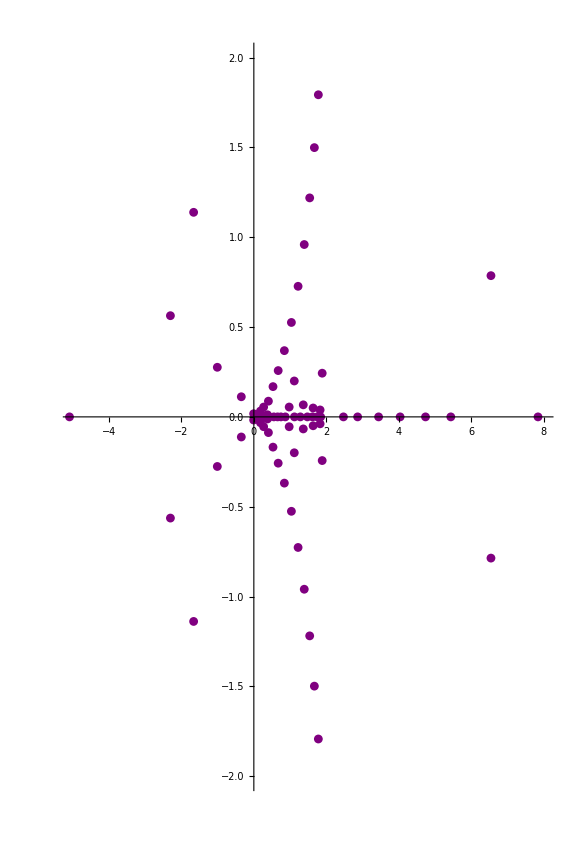

```mathematica
LiEgv=Eigenvalues[tabMlnN15eps0dot1]
LiEgvRe=Re[LiEgv];
LiEgvIm=Im[LiEgv];
LiEgv2D={LiEgvRe,LiEgvIm}//Transpose;
ListPlot[LiEgv2D,PlotRange->{{-5,8},{-2,2}},PlotStyle->Purple,ImageSize->Large,AspectRatio->1.5]
```

```mathematica
hJ[3/4,m,m+45,m]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {-0.8555}. NIntegrate obtained -0.00618194 and 0.000839865 for the integral and error estimates.

-0.00618194